### Initialization

```mathematica
SetDirectory[NotebookDirectory[]<>"Simulation/Simulation/bin/Release"];
```

```mathematica
Set[#,"--"<>ToString@#]&/@{
NodeCount,
CouplingRadius,
CouplingStrength,
TimeScale,
DiffusionConstant,
DeltaTime,
WarmupTime,
MeasurementInterval,
MaximumTime,
DelayTime,
Seed,
BifurcationParameters,
BifurcationParameterMean,
BifurcationParameterVariance,
SpikeActivationThreshold,
SpikePeakThreshold
};
Set[#,ToString@#]&/@{
Config,
Trajectory,
TrajectoryV,
InterspikeInterval
};
```

```mathematica
LogRange[a_,b_,n_,base_]:=base^Range[a,b,(b-a)/(n-1)];
LogRange[a_,b_,n_]:=LogRange[a,b,n,10];
```

```mathematica
Read2DData[file_,type_]:=Block[{data},
With[{n=BinaryRead[file,"Integer32"]},
data=Table[With[{m=BinaryRead[file,"Integer32"]},
Table[BinaryRead[file,type],{j,m}]
],{i,n}]
];
Close@file;
data];
```

```mathematica
RunCommand[args__]:=RunProcess[{"Simulation.exe",args},"StandardOutput"];
GetConfig[guid_]:=Association@@(#[[1]]->ToExpression[#[[3,1]]]&/@Import["./Data/"<>guid<>"/Config.xml"][[2,3]])
GetTrajectory[guid_]:=Transpose@Read2DData["./Data/"<>guid<>"/Trajectory.bin","Real64"];
GetTrajectoryV[guid_]:=Transpose@Read2DData["./Data/"<>guid<>"/TrajectoryV.bin","Real64"];
GetTrajectory2D[guid_]:=With[{us=GetTrajectory@guid,vs=GetTrajectoryV@guid},
MapThread[List,{us,vs},2]];
GetBifurcationParameters[guid_]:=Block[{data},With[{file="./Data/"<>guid<>"/BifurcationParameters.bin"},With[{n=BinaryRead[file,"Integer32"]},
data=Table[BinaryRead[file,"Real64"],{i,n}];
Close@file;
data]]];
GetInterspikeInterval[guid_]:=Read2DData["./Data/"<>guid<>"/ISI.bin","Real64"];
ClearData[guid_]:=DeleteDirectory["./Data/"<>guid,DeleteContents->True];
RunSeries[variable_,values_,fixedArgs__]:=RunCommand[variable,#,fixedArgs]&/@values;
```

```mathematica
PlotTrajectory[guid_]:=With[{traj=GetTrajectory@guid},
ArrayPlot@traj];
PlotInterspikeIntervalPDF[guid_]:=With[{isi=GetInterspikeInterval@guid},
Histogram[Flatten@isi,
PlotLabel->"R = "<>ToString@CalculateSignalToNoiseRatio@guid]];
CalculateSignalToNoiseRatio[guid_]:=If[StringLength@guid>0,With[{isi=Flatten@GetInterspikeInterval@guid},
If[Length@isi>0,
With[{mean=Moment[isi,1],variance=Moment[isi,2]},
Sqrt[variance-mean^2]/mean],-1]],-1];
MergeData[datas__]:=Merge[{datas},If[SameQ@@#,#[[1]],Flatten[#,1]]&];
```

```mathematica
Off[FindMinimum::lstol]
FindRMinimum[variable_,variable0_,fixedArgs__]:=Module[{x,F},
F[x_?NumericQ]:=CalculateSignalToNoiseRatio@RunCommand[variable,10^x,fixedArgs];
With[{result=FindMinimum[
F[x],{x,Log10@variable0},
WorkingPrecision->4]},
{10^x/.result[[2]],result[[1]]}]];
```

```mathematica
FindRMinima[variable_,variable0_,parameters_,fixedArgs__]:=With[{locals=Table[Unique[],{i,Length@parameters}]},
With[{args=Sequence@@Flatten@Table[{parameters[[i,1]],locals[[i]]},{i,Length@parameters}],iterators=Sequence@@Table[{locals[[i]],parameters[[i,2]]},{i,Length@parameters}]},
Table[Print@locals;FindRMinimum[variable,variable0,args,fixedArgs],iterators]]];
```

### Minima Analysis

```mathematica
MinimaDataNew=FindRMinima[DiffusionConstant,0.1,
{{BifurcationParameterMean,Range[1.05,1.3,0.05]},
{BifurcationParameterVariance,Range[0.,0.05,0.01]}},
Seed,42,
NodeCount,100,
WarmupTime,100,
MaximumTime,500,
Config,
InterspikeInterval]
```

#### Data

```mathematica
MinimaData={{{0.0000251114137724111`2.9750143161617237,-1.`4.},{0.00087828048309321`3.1525788423775434,0.0572440566600720888`4.},{0.0018974700032114607`3.202924099605909,0.0844079624855467309`4.},{4.1284487826078`2.9066620710365365*^-6,-1.`4.},{0.0001877930375049295`3.0665041040003387,0.0858689501838717784`4.},{0.0003430958701862451`3.0981331520241677,0.0573782758962913669`4.}},{{0.0001989241763113578`3.069428565418404,-1.`4.},{1.`2.31556501656662*^-21,-1.`4.},{0.0034774233875606952`3.2470712755981292,0.1755869494577795842`4.},{0.0000293147522362762`2.9814068535870355,-1.`4.},{4.8157751321072`2.251868354981211*^-25,-1.`4.},{0.0074877905091144661`3.310293307169852,0.271267700268278622`4.}},{{0.0080180746579864045`3.316407557178998,0.2813564666450283358`4.},{0.0016760652240464023`3.1944103644600843,0.1823372892816492175`4.},{0.0259349067356361327`3.4374495542777197,0.3384373479494602877`4.},{0.0256799156442389663`3.4362761946176503,0.3429352104185401373`4.},{5.1596621747898`2.9145438914625266*^-6,-1.`4.},{0.0759429690080739377`3.588755392134314,0.4261339737100776071`4.}},{{0.013316699422697966`3.364643299316589,0.3704808559625557551`4.},{0.0207441210908032239`3.411673111186131,0.3773545644670410204`4.},{1.6084879370995769403485603709609`2.8056854772439404*^-7,-1.`4.},{1.9217545598432`2.244800816828635*^-25,-1.`4.},{0.0884985284317092851`3.615329565356987,0.464602266554335841`4.},{0.0251121883592285566`3.4336329954880385,0.4138364168789963604`4.}},{{0.0210305961050282574`3.4132128146313985,0.4346503790288060443`4.},{0.0001051928583653902`3.038118032046775,-1.`4.},{0.0908407240527627175`3.620033553810563,0.4858324007013830048`4.},{0.0584558025921267672`3.546760524969864,0.4693562225769530305`4.},{0.0655296401494647834`3.5645932186520106,0.4827779225251168094`4.},{0.0379210201350219993`3.485153563482437,0.4757389112878704363`4.}},{{0.0407873081266823495`3.4949335878023158,0.4888644524241271272`4.},{0.0015430284890299367`3.188826752012044,-1.`4.},{0.1005900305221807051`3.6388953275074525,0.5332517171719245441`4.},{0.0457896185212871324`3.5109281773140038,0.5042133168334878013`4.},{0.057851291594396798`3.5451735028103517,0.5183041753895002435`4.},{0.0402499238818064208`3.4931369688658225,0.5321188344290720407`4.}}};
```

#### Plots

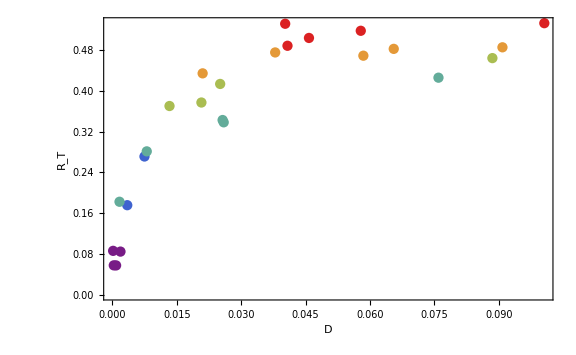

```mathematica
ListPlot[MinimaData,
Axes->False,
Frame->True,
PlotRange->{All,{0,Automatic}},
FrameLabel->{"D","R_T"},
FrameStyle->Black,
LabelStyle->Directive[Black,16],
PlotStyle->ColorData["Rainbow"]/@Range[0,1,1/(Length@MinimaData-1)],
ImageSize->Large]
```

### Tests

```mathematica
With[{guids=RunSeries[DiffusionConstant,{0.00012,0.001,0.005,0.05},
Seed,42,
BifurcationParameterVariance,0.05,
Config,
Trajectory,
InterspikeInterval]},
With[{result=GraphicsGrid[Transpose@{
PlotTrajectory/@guids,
PlotInterspikeIntervalPDF/@guids},
ImageSize->Large]},
ClearData/@guids;
result]]
```

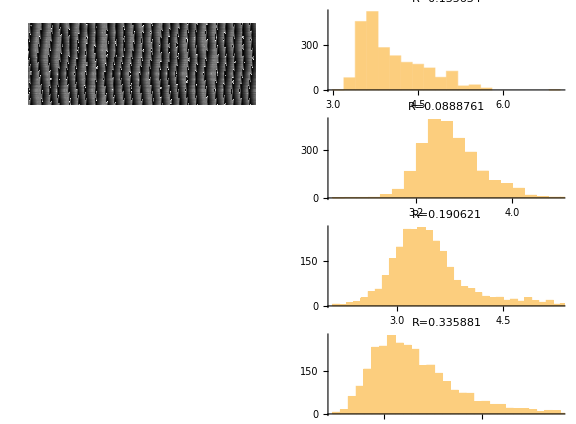

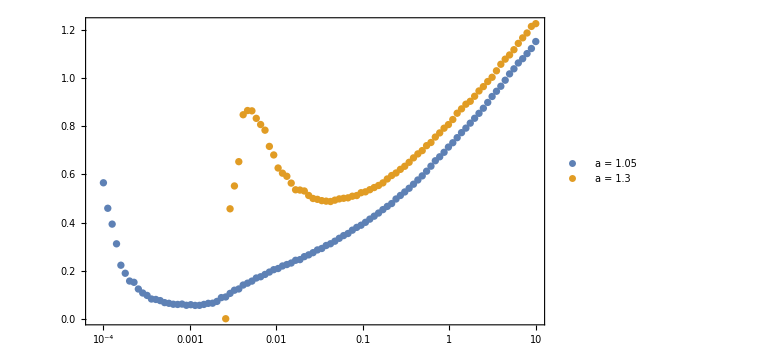

```mathematica
With[{as={1.05,1.3},ds=LogRange[-4.0,1.0,100]},
With[{curves=Table[With[{guids=RunSeries[DiffusionConstant,ds,
Seed,42,
NodeCount,100,
WarmupTime,100,
MaximumTime,500,
BifurcationParameterMean,a,
BifurcationParameterVariance,0,
Config,
InterspikeInterval]},
DeleteCases[MapThread[List,{ds,CalculateSignalToNoiseRatio/@guids}],
{x_,y_}/;y<0]],{a,as}]},
ListLogLinearPlot[curves,
Axes->False,
Frame->True,
PlotLegends->("a = "<>ToString@#&/@as),
ImageSize->Large]]]
```

### D - R

```mathematica
dataDRNew=With[{seed=42,tmax=1000,as={1.1,1.2},das=Range[0.0,0.05,0.01],ds=LogRange[-4.0,1.0,200]},
<|"seed"->seed,"tmax"->tmax,"as"->as,"das"->das,"ds"->ds,"guidsss"->Table[
Print@{a,da};
RunSeries[DiffusionConstant,ds,
Seed,seed,
NodeCount,100,
WarmupTime,100,
MaximumTime,tmax,
BifurcationParameterMean,a,
BifurcationParameterVariance,da,
Config,
InterspikeInterval
],{a,as},{da,das}]|>]
```

#### Data 1: a = 1.05, 1.3

```mathematica
dataDR1=<|"seed"->42,"tmax"->1000,"as"->{1.05,1.3},"das"->{0.,0.01,0.02,0.03,0.04,0.05},"ds"->{0.0001,0.0001059560179277616,0.00011226677735108136,0.00011895340673703195,0.00012603829296797275,0.00013354515629298989,0.00014149912974345758,0.00014992684327860457,0.00015885651294280528,0.00016831803533309567,0.00017834308769319092,0.00018896523396912096,0.00020022003718155845,0.00021214517849106298,0.00022478058335487252,0.00023816855519761583,0.0002523539170434766,0.0002673841615839947,0.0002833096101839324,0.0003001835813575589,0.0003180625692794119,0.00033700643292719284,0.00035707859649004625,0.0003783462617131929,0.0004008806328898465,0.00042475715525368984,0.00045005576757004977,0.00047686116977144693,0.0005052631065335679,0.0005353566677410725,0.0005672426068491978,0.0006010276782070381,0.0006368249944718586,0.0006747544053110693,0.0007149428986597577,0.0007575250258771912,0.0008026433522257174,0.0008504489341802677,0.0009011018251665018,0.0009547716114208056,0.001011637979766207,0.0010718913192051286,0.001135733358343105,0.0012033778407775906,0.0012750512407130128,0.0013509935211980279,0.0014314589375234786,0.001516716888470924,0.0016070528182616384,0.0017027691722259013,0.0018041864093920718,0.0019116440753857036,0.0020255019392306666,0.0021461411978584057,0.0022739657523579274,0.0024094035602395267,0.0025529080682395165,0.002704959730463137,0.0028660676169482502,0.0030367711180354605,0.0032176417502507355,0.0034092850697468144,0.0036123426997094303,0.003827494478516315,0.004055460735840828,0.004297004704320844,0.004552935074866948,0.004824108704165373,0.005111433483440166,0.005415871378079476,0.005738441648302393,0.006080224261649427,0.00644236350872137,0.006826071834272393,0.007232633896483534,0.007663410868007463,0.008119844993184008,0.00860346441668451,0.009115888299750819,0.009658832241158708,0.010234114021054537,0.010843659686896108,0.011489510001873097,0.012173827277396621,0.012898902612533094,0.013667163564620072,0.014481182276745346,0.015343684089300131,0.016257556664437952,0.017225859653987874,0.018251834943190444,0.01933891750455232,0.020490746898158482,0.021711179456945052,0.023004301197729192,0.024374441501222217,0.025826187606826773,0.02736439997074672,0.02899422853882878,0.03072112998861759,0.0325508859983506,0.0344896226040576,0.03654383070957258,0.03872038781812557,0.04102658105827194,0.043470131581250265,0.04605922041145108,0.04880251583654434,0.05170920242896761,0.05478901179593945,0.058052255160949015,0.06150985788580504,0.06517339604882427,0.0690551352016233,0.073168071434272,0.07752597488629465,0.0821434358491943,0.08703591361485166,0.09221978823334331,0.09771241535346502,0.10353218432956626,0.1096985797892384,0.1162322468679853,0.12315506032928261,0.1304901978014403,0.13826221737646563,0.14649713983072862,0.1552225357427048,0.16446761779946645,0.17426333860096507,0.18464249428955445,0.19563983435170648,0.2072921779595372,0.2196385372416547,0.23272024789604098,0.2465811075822604,0.2612675225563329,0.27682866303920667,0.29331662783900453,0.3107866187782014,0.3292971255097151,0.3489101213406774,0.3696912707195028,0.39171014908092605,0.41504047578504766,0.4397603609302721,0.4659525668664682,0.4937047852839004,0.5231099308056264,0.5542664520663108,0.5872786613189482,0.6222570836730231,0.6593188271333549,0.698587974678525,0.7401959996915645,0.7842822061337682,0.8309941949353395,0.8804883581643465,0.9329304026284686,0.9884959046625587,1.0473708979594507,1.1097524964120722,1.175849554052158,1.2458833642950082,1.3200884008314195,1.3987131026472386,1.4820207057988601,1.5702901247293775,1.6638168860761307,1.762914118095948,1.8679135990207847,1.9791668678535574,2.097046401323235,2.2219468609395236,2.35428641432242,2.4945081352303164,2.643081486974108,2.800503894183631,2.9673024081888726,3.1440354715915,3.331294787934677,3.52970730273065,3.7399373024788014,3.9626886387014784,4.198707084443915,4.448782831127585,4.713753134116729,4.99450511585514,5.291978735958447,5.607169938205458,5.94113398496504,6.294988990221888,6.669919663030129,7.067181273927491,7.488103857590031,7.934096665797492,8.406652885618334,8.907354638610439,9.437878277775392,10.},"guidsss"->{{{"63adacc7-95d5-48ca-bd36-1013a78e6892","9dd423ea-6fdb-45ed-ae2b-2cdd36409fcb","343ceb95-efd6-4595-8b4d-2e2c78a87174","b457f9f3-fc33-42d8-b052-1ea0535964db","d08a937b-e49b-421c-8571-c25703f73a01","5e9c3c20-5a01-4e4b-84cc-9e7b2ffa7a4f","b452aea1-3411-4bf8-8ef1-77d45baa56de","4f412340-9ae6-4773-ab6b-2e121c5a53f7","ddfeb9c2-1309-4098-a4de-c1fbf706aceb","8c7412c6-4bcd-486e-945f-69a6d41532fd","61ebdb6e-bd1e-4f7a-9d6a-63ede0b088eb","3c328e58-cffb-4cc8-9e95-65c727346e29","27baf275-ba17-4f5c-ad09-1f463f6e50be","d4da9b0d-6dd1-45ca-b488-fff211634dfb","05ac5512-a315-47e8-9ddd-8a6038c34b00","51daf4a1-7762-449d-adb0-edb0c5bae341","7a2ae5b4-0873-45fe-8a78-8ccb7135757c","1fb8f5d2-13a7-4791-9f32-c534f144cf30","9f8a6280-cf11-4c5e-987c-b7f464cb9e8d","6422a224-aff2-4e2c-8109-277d61318fdc","18617f33-b160-49c7-b7f9-d53f3b23079a","968260cb-a8e0-4696-95ab-1e6d10f5a18e","407968e9-a366-4438-a3cd-5be792c30ea2","62c00c75-e21f-442a-a4db-edea8907a5f9","f981e4a6-e3ac-4385-b326-bc5794d7f5de","655de754-17a8-420a-a5a9-6bced4a48449","3c7de7fe-51d7-4420-8c98-6aeccec0ad22","ba73ded0-1c9e-4819-973e-0901dbaa96e5","b7ced212-8731-4be5-a067-0e75c27f8f67","8fd2473c-4cda-48ca-96ca-f1a1b0420463","11bd9144-8b4a-40ba-aae7-e584c8fa904d","c705705a-7139-4a07-b924-7a7b5c269720","1868d2ee-17ec-4e32-b020-13ef94ba4215","31429ac9-a13b-4771-aaa6-bbb08d200ac0","15957bdc-b4ba-438f-a2b0-361e2e6cb7cb","a6c1e62b-6dc1-4c30-8db8-b3ca4e070e9c","408e1527-9d48-49ac-b687-9f13af2174ea","779500e3-6c98-4214-816c-b8109904643c","7b0a6721-c23a-48b5-a8a5-f125210e7e62","6262b9d5-798c-4ba1-8655-a9cd497e871f","43ea74ea-9ce7-453a-9fee-46c5081f8366","30ea178d-029e-4241-8f43-4fcd011cd237","2efed132-cf15-4e40-bf9e-ed7be74b0215","fceca2fa-4216-4fa6-9b23-bca0c3b24541","78b50ab3-e50b-44ed-9177-24b2c268caca","dbe841e5-1a71-4f65-85c5-7ca95778dd9e","80e5980a-613a-4318-b780-e7de788ed6d2","a79abae0-5671-4eb3-bf53-f395c597a8fe","70d5baf2-7564-42af-8d93-84cfaa637630","efcbd73c-3792-4080-9c47-fb887133586a","2f926978-009e-4266-acc9-196be34d4fbe","46ada5e7-c840-481e-a0de-10818bf640ef","ee89cebd-584a-4a6e-b091-b41ab3da9e1c","019da4d0-95cc-4131-a8fa-bced955a2e08","c0c427bf-fdd6-4d23-af1b-a15801ce3aa4","e0bc92c0-7302-444d-a28f-16a4598c143b","b06fd88f-5775-4942-8f32-0828aa68ae61","105bf928-08cf-4737-ba07-9ddb29e1b254","4cbe2ac7-bcc6-4519-8070-859b5158ac8f","956915d1-695a-4876-95a4-1a9b0c24683b","884aba2f-85e5-4cca-95cb-cdddc4d100bf","6de70096-a034-4513-9a8c-e7ba8d1ed212","8587991a-1848-4e3b-9b60-83dabb41365e","679837b2-0b6e-4998-821c-8f1e38ae2a09","5204f26a-5629-4137-8a13-23bd75069761","9003b724-1b43-4b82-9d2d-8bd181f6daab","c0a95b36-43b4-4695-b8ca-f5c6ed95fb8b","e5cd95b9-e467-4d8f-a279-6c5e298f4965","e76c8332-1509-4d3e-8b59-4191646bbaaa","9abeb762-5b6e-4d65-a0b5-489cba2b3ca6","d770d2d0-0d60-4bfd-96df-5b18da77b41b","72f5fe10-b4a8-437c-b6b5-02517c3a66d9","1e1b2369-9f1e-463c-ae50-3a3e7584a774","e31088a8-8577-4d73-9026-da7a949473e9","e2f6f004-f5e1-49ae-b4db-ddc1007bc585","2600b3b7-11ee-456e-a69d-1a5946655428","c3a3759d-81a8-4d12-b3d7-91b445a6aabd","26d9ff76-fc38-435f-942b-ac684bbdb240","26e11fb2-fc18-4fcf-88cc-d50fb26d0dcd","4e97e887-d53f-4cbb-b8c4-b2dc369c4db8","01f68908-b60d-45a6-97c4-236c999a223d","0f15a6f5-11c8-4b19-a9a2-1af935424622","e3defe60-ccd0-432d-ac9d-82c337446891","bb3bb1c5-4a44-4e28-9be1-92e58477a66c","1745fd51-d17f-445c-98b0-e9d3bc1414b8","93444ff0-f8b6-40fa-aa91-d6e4c42b3050","02d3fc03-1b65-4a77-8709-f5ffde95368b","4c92be04-d65e-439c-978d-0acfdc0768af","75bcb220-cf33-4520-a22c-9d2f5593869a","36e8276c-9dbf-42ce-b129-432280e08d0f","26fedde7-1b85-4194-b4ba-cf4d239f4d1e","f0408fb4-7bbe-4ee6-a639-b91671b69f41","8752891b-1b9d-4c3f-aa6f-dc47324e6c32","9e419da1-3392-4dd3-a162-4e23a0ab402e","ce669139-0f6e-4aae-b348-cedec2fc5ddf","6449355f-4a7a-4526-b4a6-e9a0b2142d0b","9410ca1e-fc9c-43c1-b157-27354e4f3c2f","dc51f2dc-3c8d-4863-96b3-8090d2020bfb","2e08ee0d-4e08-46d5-912f-e652bf480ebc","8d85927e-72b1-4d73-8b45-7a6d53c888bb","3caa07b5-6084-4f94-80bf-09e39e84fec3","995fb69c-afa8-42c5-9ea3-18af2331283b","de0b2514-8901-439d-bd76-885c145c1f23","fc5bccf1-3086-4644-996f-4b0dd4b16a95","23859abe-8b4a-4af4-9525-5713fdbf8830","602b2934-7f66-4776-90f5-f360dac8c4d7","8e20f6ad-482d-4b1e-9aa7-657af8857030","646e3f3e-d25a-4f8a-8cce-e56a17715381","035c65d4-0c3f-4d8a-b46a-323dbaa3e364","67390b31-dae9-4860-a138-6b954f9c35fe","87a46de1-7eba-4acd-91f0-51ddef5849fd","97b7b338-5cdc-4e1a-9412-01f39d176dd7","211fbb71-6769-4339-a226-b0330824294d","8e942446-0cbd-45af-b08e-63465d260a26","2ea41417-bcb2-4721-87ba-ab516b4e660a","a2727f58-d1e9-47d6-86e9-0e52305eacff","099b9c55-29c7-42f3-8386-f5fe59439010","28b7c7de-695d-4d80-90ff-80652db8c951","437d9591-6944-46c1-a31a-5389502a767d","88aa466d-1608-47f7-865a-bff2a371f31e","e50edb09-185d-4009-9528-0f0add18e175","76410bec-dcba-4036-8c0e-1384ae9d26ec","59c9bfbe-0175-4af4-af1f-1e86d0ae4f5a","9616532a-c179-4d24-bac2-f3173844bfdb","66d6aee2-36e2-49b8-a77b-4f49496b4898","d757cecd-0707-4720-bcbf-71892f57f6a6","d04d676c-d935-42fe-9bc5-17cbcef1a228","84483253-f8b7-4daa-9b47-f454519389aa","fdb0ee2c-27f0-4342-9559-5cae08b3c63f","1243104c-ccfa-486c-acd4-341c1e79a8f9","0e443d45-d126-437e-83ee-88bbc8f3eb14","a433f5ca-50b5-4d1f-b57c-b8383de4d0e7","1a5bc196-35e9-4316-9862-bf8ee6b8748f","f12162bd-241f-4f85-82f0-536c66d70f95","d7f4e5a4-2ab7-40d0-8621-900b59f6fd66","098e0dc3-9908-4ea5-821e-8df38bb8d716","288d32c1-1669-49ea-9115-c89974dc2da4","ca2c0a6c-e89b-4928-bd7a-6b1e4bf7dfcf","c62e36e8-cc3d-466e-9619-77ebb4d8093c","b8681af2-f399-4fa6-8f27-1f0474b178f6","2597f815-7fc1-486c-b89c-c2f5fcd515fc","612c98e6-ee5c-45e5-aa50-610dd81cea68","a0c13ce9-e667-48cc-8bb9-02756f993d26","8d71bc3f-2c30-47ca-b618-0c4d3bb06d33","20efbe0b-6515-446d-b2df-00352d6f7c8e","6c12e9ed-5568-4f66-9b31-288ded881407","65815259-7345-4be6-81dc-b57535f46d4e","51dc4c09-b547-4a33-8226-8e16daf5fc5c","a83c000e-759e-4ecd-aceb-c95fc41cd64b","ecaa8637-0946-4b48-b181-babb38d1e36a","36eb647a-9e3e-4435-b9bf-8fdac2d68ea5","daaa9cf5-1cb4-407f-9240-3fa0aa1e9b78","042346d3-2557-45c9-bf37-16dfec435ecb","b6d8cff0-eef5-4fc4-94bc-00f5878ea673","fa13a00e-e04b-4ecc-a5aa-754b7fc40adf","8b80826b-ec15-4b67-acaa-9b7b3c4ad216","8988e784-400e-4c8f-b090-73a7713d8d81","74dd8319-a3f1-4fb4-817b-44c89c043183","65654c4c-b49d-4879-8ca7-3990bc5c9976","f5c2d660-2452-431e-89ca-2d05dc6e13bf","3cbd3537-5e90-48cc-8481-d42b43ce6614","b91ee97d-5108-4436-8af5-2a84d4405263","759ec807-e16f-425d-b4ed-94ee97dbdc3a","a6fb1ed4-0dd7-4336-a9e5-5fa53eaf45fb","56a3885c-b5ed-45e9-a78a-c9881205a89e","4ea6dac8-edd5-46c5-8d05-8627d7f0ac93","2740591f-9e85-4e42-88c6-1b8a4523a2b3","97a39b8a-16a8-4205-8f1b-b25798986b1c","76cef2f0-d569-4e1b-9697-8cededc8e0ea","2e87773e-14ea-4632-ac77-22dc0be9534f","23aececb-20f1-47d1-9a0f-76d81d4c25ed","67bff363-48b9-43bc-b791-055ee02ef4ef","899d3ca7-4edc-450c-82b2-139cca9b1c89","b3349176-3ed1-4b4a-90eb-43186bf149b0","39602c63-1a8f-4d59-ab36-152d30b2002d","7fd75dc6-ccba-4435-b7ac-f73864410cf3","9b772939-9cdf-4c96-9160-9deeac5b3c19","55c61643-bea3-4c82-b78f-0905d53075e6","a7221b89-df3d-47a4-8d0b-e795ce395916","adc0f37a-85d3-4fc4-b3fc-830787281425","0d3270db-43a6-4758-8762-c5659ac8804c","2bb5079a-3721-44eb-96e0-1ba00a3ec181","a6c0cfdf-6c35-486d-a9cb-8579e4edfca2","5e626233-4a76-4fb7-a341-8fe9ea64cc8a","8c827c4d-9d98-4da5-9869-0048b8dc2c59","05a93d2a-67ea-4ac1-93e7-84a4cd44f47c","51aa1544-ba0e-4c7b-a86e-31a3e02a526c","6fdf670e-a30f-49a6-b3b7-92c2190c5492","0cc2ed0b-2d4e-45d5-93c0-57737d50b17a","9ef91fdb-ba93-43dc-8e3f-26ba341170e9","b718d222-593e-47c7-a01a-5e925c1cdaee","2f4033c6-6303-4550-9b62-1b7aa7728c5f","6043d969-fee0-4550-842c-114772e77e46","a15c46c2-086e-44c1-bd05-a1059ab3586c","dc86bd84-28da-49c2-a954-0aea9a511360","53edc77a-df1f-4083-93fc-e59ab0922775","49492f26-f49e-472e-a388-cfe82369cc31","ea54259e-03be-44bf-bff1-33ac16c82786","c0218b40-15de-4721-8616-d3ad307330ea","7ef74c21-67df-49c4-8870-bb68613bdc2c"},{"9726aa61-05cf-474d-9370-53630041886e","757bd8cd-f343-4390-9a12-5327aaa5b675","e328f051-b705-482d-a404-5cf9d3b86526","90e74422-08ad-4cad-b89f-b8613eca8285","19d660db-5719-4ecf-8cfd-66c659367303","bee3dfa0-1dca-4a80-b0ee-3b44a674e0a3","898386d7-a6f3-4809-b390-7eca0b14b2ad","e7a84f20-cefb-4f40-8240-3ad05dc5265d","ad188b9b-495f-4c92-a573-c512f2998e01","fad9d3fb-3b7a-4b7b-9ca3-ec4fc5447e28","5eeb9cbf-8f90-4a5e-997f-6b9e4863ce61","a21d5352-1401-4bf1-8de8-c68cb0a13b80","4333b763-1f8c-4d4e-b7aa-cd0641b2aefc","6ad43ec6-e6c7-43b9-884f-93ac885a333e","827a7633-d985-4a20-9aae-747cdd3c04a7","733c72c1-bcac-4119-aece-f15c2c11e051","87f66139-582b-49db-9817-66d2d4207e07","313b39ce-b29e-499f-8ac0-ca8234510552","0182f1c5-fb21-46e2-b1cc-1c46c766964b","cea814a9-1dd6-4e3b-b4c7-6fcae49540e0","5863a285-8d71-4bba-988a-0186500527bd","3d9ef11b-135a-4157-ad21-697adc0c2359","265b3fae-0ee8-42d3-9d95-c7b431e2e5be","e2bf0cc0-2e4c-43a0-b7a0-b7fd4ce19d11","0009cac7-5cbc-4216-b2f9-497b5b70c22d","ac42437f-610c-4ce8-a7c6-c37274a4fcb1","17ebf042-ff82-404a-9d8b-7ec8bb0fae59","bff45867-7fbc-4ffb-8967-dfd40edd90e9","a51c3285-342d-4e77-9d37-2e0a3a754d64","c570eca6-8dfa-4b34-93ca-75c7f17f3660","f58b21b2-c784-4638-b378-e6bd517b665f","2cfdd6d6-de7d-4601-882e-3c103da12b26","acfcdf15-ae0b-48a6-a778-f7960e4e6334","63959473-817c-4783-85da-d22de3b28e37","c3464f65-fd1c-4fba-8618-75fa203a4542","fee6aedf-d19d-466e-a13e-949fcf7a16ac","d8ca93d9-b064-4979-b51c-819e9f5536cc","d31eebab-899d-49b3-988b-902139185817","b54f5702-8f4b-4ad7-ad4a-394e93e9c56c","dfeab070-185a-4e99-8c5f-7ee61c507452","3240f6ff-da42-4cb6-adfd-57cd429457b6","f419ddc9-4296-40ce-ad07-c10432af5d21","43675eab-64dc-4b76-be6b-914b1d420aca","223b8970-f086-41e6-ae15-74a70671323e","59a96257-7c6e-47b6-b3ff-7cfd511fedde","62d1bdb1-c909-4ea3-b7e8-0219d4e80f73","02838d27-0477-4d41-90a7-434ee5b303a2","ccdafbff-aa82-42ba-9ba9-f6a7abac9e11","97eab00d-863e-4ff2-aa9a-6c63f52f90a1","ac774ab3-0591-44fe-b088-b43074b00ba1","06b5fd7f-589b-406d-bb92-a8efd3afa157","8dfd2f21-37a5-4f17-b511-4a03bb9ee5f1","76f0be01-c8db-469e-8cb0-d6f0b4c5516a","e0ac7920-322a-4910-aa27-a83cf4054483","8df947d3-13d9-4d33-a7cd-25c236423a2d","2462ab94-8e1b-46ba-bba4-ed13258cb66c","9b504ad8-0f73-4ef4-a915-cab54d6bec52","90e37f3c-91e4-4d0a-a937-949684afa8c6","0e1a2807-4c83-4d21-8a99-d5f91508da62","6882b62c-a521-4827-923a-7956ae9190ba","7ba305ef-a7c4-4924-abee-2e25370f9349","885e9dbb-064b-4b81-8bc3-f2c3f5ff91e6","2e05fa98-4d81-4398-8ab1-4c9d6cbc14c0","01170edd-f72c-429b-8ca6-1cd9f73656ad","c9ff3822-8e31-4257-92e8-f976d9416cde","bf132876-b39f-49d4-a96f-de7224da8311","7acae356-a912-4e63-9cb3-092fc3d55391","1225c1f0-2e0c-45c8-a124-c94a516d93aa","15bab6d1-b79d-43dc-a219-629d82c71354","55d4ab15-eb4a-4b28-afcb-1594b654593f","c196c07a-fbe7-429b-b2d7-f0b3abfa4b67","cfcdae1e-42c3-42ab-92da-55a78f57f26a","64ca58e2-17f1-4ad8-9b89-7d3c56a5591d","af7e5a84-1df8-4ad9-998c-6bf64ff8dd74","8999ce1f-b4fa-4420-9bb1-f74d637673bd","69bd5929-e558-4fa5-9902-8d10cbc7ae17","b25766a5-d540-4a5f-8828-20b6c13f24f0","bdfd2ccd-eb1a-4b41-9e6b-6927dcb759d5","f378e34d-af0f-4055-b598-9ddb945f4c4b","bd960f4c-1e76-42b7-91a7-16f73f7e5a0a","35b3e44f-2df9-469d-aa0f-a13c875c8b2e","eadb4d26-c9d5-4e82-85b9-6dd9462c5dd0","1a462237-74d5-4532-a906-d0640cdb3a4e","49bc0ce4-b3b5-4f56-a4af-b4ac6bd8ff9f","12b430ce-8c71-4781-9d72-81914d235b27","ac0f1d55-bdad-4ddb-8382-67496271f828","2bf6e6f4-d4ba-499f-8b0a-8f2bf571420f","8bc0e641-f2fc-4ca5-bccd-43efc2d07dd3","ce1adf3f-2d81-4ea2-af0d-bd537f04bf86","477adfbb-4d97-4044-8635-a956ec8ced90","76fd8408-71e8-4706-8e61-c562e0d825d0","c4a3b2e3-2b8f-4d95-bdef-47fb17bc1242","6b63508c-48cd-46d4-bdfb-5ab553ca62c9","418c1d2e-562e-4e80-afbb-2d38a608227b","616d3889-6b7b-4929-a27b-7374c6f5a21a","12134502-8456-4987-b9ca-1b6672bef79e","18a8cd70-e3f9-4edc-aea2-826dedcafd92","d78b66e1-be26-465a-aeb3-a291dc24c643","e9a57321-1feb-470a-846b-5d6016c5a4c7","d813118f-4567-4ed1-96d1-8940b0c9491d","f70c0a88-fff7-4075-8be4-129c99512633","8a1e6ade-c505-4ada-8eec-9a6bc228ab14","f6b4c21e-1a10-4dae-aee6-0f32fcd1bb48","eebc92b3-8bc4-4aef-8827-ddb96322adca","4fb07442-0d11-4a22-8de0-f10fd75acc9c","5a5c7e93-ab7a-4194-ac83-6d8d1b0296c4","a50dfdf2-e383-485c-9c50-c759ca0b88f9","bc7cc4b2-ce20-4b91-b987-44652b8e3159","7941d6c2-c9fa-4501-93f6-25486549ab61","3d48f500-4668-45a1-b3bb-647eb317f844","5c510f35-ed0a-43f3-a7da-df3b45ed9614","a07be316-69ce-4c43-9593-12166dbf0be2","4f6e3afc-64a9-4084-a733-a1c2339cae96","f3cfc127-f96f-4e68-9f5b-ca1a898d633a","a5269b58-28e8-4f0d-8289-975115df8cdd","b4cf8043-ebea-4a23-9ecc-c513d77f6246","7d936a3c-027e-40a5-8e41-5e5589042395","c9e2a333-5204-4687-b43a-8d727e135460","2cacb496-8816-4afd-9047-02d68cee2ebc","cc61d12d-bb9c-4e1d-87cc-ea175175a6be","9a60b4ad-1ca3-4aef-9be3-61cda51a1a25","845c87bc-b87b-438f-9512-cddc18b1d096","d0325f02-7f4f-46bd-bd8e-3857ab42cb93","baa36871-e0eb-45d0-934e-58198f4f396b","f1ac105e-ae95-4b3c-8abc-7b9d8e135ac8","4fb0a608-2e8f-4dfc-9236-716b91254c84","f254f1b5-e1cd-4062-9da7-254629127bac","19c8802f-ed36-4ebe-968c-bd31f144c3e2","ae47e1db-e8ca-47f0-be05-3f8b75b1541e","f4d51aa9-95cc-4322-9386-09f867cc8110","c6539105-dcdd-4be1-9d8b-8bd538e75c23","4a5797bf-82ce-42f4-be3c-aceed61b2347","e93fe6a6-43db-483f-ad72-2eb3c566cfa4","339becc7-e588-4077-9ffc-adfc52cd447c","9ac6084e-a76c-406d-abe6-21110c059f66","b83a6974-0576-4240-ad7a-dd97cd7acce0","26f1ed19-3029-4c62-b6f0-e553478180c9","453948e4-137c-4642-b1ee-26a10d5f4cff","71cbc448-f514-4ba0-b1e3-fc60c6b715a5","b88a868f-3410-4645-861f-b77c7273f50e","1680452f-c5e4-46fc-9063-be4728f0ea99","e849f200-6ee7-4810-84c4-799a3253b4e1","30b5e6b2-acbf-4041-a727-f7db0710e2f2","12b76dd0-90d3-4085-9a3f-9982e8e629bf","3b962126-2d6e-431d-987b-9aac59ba9c23","2c34479b-578e-4610-a127-0a7795e70cd7","4d59c2ae-9e0a-4199-8880-47dba30569c2","4a0d7e83-f4cd-43d7-806e-c852c3c6d949","2257dfc3-f8c0-454e-86b5-c600ba4e0137","5e9d58f5-4608-4ce0-a674-96c37ba1b7d6","507797bf-7164-4ad5-a2fd-afe0d61e2f2f","0dca8583-16fe-4fff-acf9-2f6e1ef6b5ce","942a19ac-aef0-4485-9c9e-82172e02d329","0455c5ac-7fd3-4ec2-b8ba-3f6fca34a5e3","72dd5dac-db68-493e-9863-19ec0e7db6db","92388897-f2af-403d-81ef-d027a02ba11e","9d7e5de6-dd91-4ff9-b9ce-c6fdf2d210b0","2dea963b-6382-4a48-9e12-af17eaa4f458","540ec416-8dbe-4107-b44e-bf2cb252f345","9bea017d-024f-4c80-8dd3-de520f70290c","b2d2a3c9-61ce-48e2-b7fe-2438d04577c8","61202480-7897-475c-a731-fadffaef8874","f70d208d-3e04-4235-ba75-31a51650258d","ba0c7da8-9fcc-4c88-aa02-2fcdff735fd4","9ea33189-6f19-4cb8-b081-91da98afc8b4","92391278-edb4-40fe-9f26-0d638b7e005e","4defc109-4c43-47ce-88d5-a484aaae1462","847e5eb2-3d8b-476c-ac85-8695689732df","9e503f4c-23ee-4781-bcc9-6d217b2042b9","083eb913-8641-47ea-85e9-6b8dfb66a00e","16109674-4907-4ca7-a8cc-08793cbcc30d","e82221d7-ff68-463a-948b-1edeb4dcce95","47eea98b-debc-40ac-9fa7-f14c9a31b45b","7466841f-1ee1-4e9d-8edd-63ef61af60bc","46071906-89e6-4eb3-a5b7-326b38709f3c","3dbbf4ce-6283-4c28-a5c4-78dc0d098528","de03d76d-48ea-42aa-bbcb-9c58a97dca81","52039f4b-d116-4a64-a853-af1533900751","3ea454bb-e17b-4a96-8520-083fa52b0f9a","4e668bc6-6514-4781-99eb-ffbd09e5d662","edc28ed7-b568-4286-98dd-41cf0248b4d2","e4b8728b-2e3e-4948-923c-b86d6b1ec77e","70074bce-b5ae-48e9-aedc-340a0442b222","5ecd8324-7ab4-4a32-82cf-3e1f92f04a2d","019beebf-fc02-4686-92c5-9da5056ff5ea","fab1832f-155f-4bde-979c-803742cd244d","3f50a365-2417-4292-a1bc-2fd131bf773a","9112c3b1-efd2-49e3-9498-bd2dbd41ed73","9a33d91b-d11f-447d-8305-82f4159702c1","a4ee865b-793c-4cf8-8cd4-7db104a454dc","504c6fbe-73a7-4615-bea4-a60e1816e11a","c0bc0cb1-f56d-4836-aa92-7035c7ebf575","29e384e8-b7d3-49d6-867c-9675bd8acfb0","185a84c4-ec37-41ce-915c-d739deebe59c","0165e931-d508-4d0f-bb79-5c036f66c0fd","541dd3d8-41b2-4a7c-b36b-081a743d3015","f731d0a8-0be3-4352-b045-da9e17bdfb19","0aafac8d-8dea-42ab-af11-7175022384e3","c548b018-f3a5-481c-b7cb-e2769bae3466","322a96be-3252-40a3-8953-e0fed06c734b"},{"71d3d8ef-a88a-4e78-aa0a-2e158f3c394a","8760ad63-5c40-47fe-98a1-411f0da5d7e3","7025bdae-1c15-4263-ae8b-1275503badee","7f433ced-035b-491c-9585-cfb2fae8bb81","3108e38d-dbf1-4f24-a8c8-8b35bfd25903","a1bb2cfc-da6b-47a4-ae52-4bfa4fb5a1bb","6031c242-7e45-4e1c-b287-7c39490d9a30","79131457-c040-4951-a496-8fc9f6b41986","79dbc849-8aa8-4ab8-a514-c97db5c798e2","13224d28-b8c9-4dc9-b21c-343011f57cf1","66d22612-c68d-4de8-9399-30d1032c78a0","53aa0af9-7a80-46e9-9fe6-2cd3871da362","4e44791c-b2ee-4ec2-a79c-92060265ccdb","8b79ed54-6db0-45cd-a7ad-c7191a7c297d","43510e32-1d36-425d-b3fd-805d3aebc45c","1d312ef4-5ae9-4b09-b53e-78d29ba3707b","e78f7393-a70e-4434-a6a9-5d1c1523d6b0","6c7ee235-92ea-4c0f-89e2-2297f9091c78","88ce5e77-815e-4d33-988e-539a67f69cef","1de97188-de30-4d10-be2a-f8bb1c79290d","3dec1bd8-a2ee-45e6-a4be-cd0affc96cff","7892f2a8-ba39-4b07-b042-35de768bfa12","8f5bf983-8299-41ee-8916-50a20e1544ca","b248f5c7-bd5d-4696-8fe5-d7ed8fba8375","363d49fe-7215-4092-9447-7908b174bc37","7b084a1e-8987-4c4c-b615-60790c1f8aac","afe1acb5-c216-4111-94c3-78b6e55a9ea7","506465e6-4cf3-4c36-a30f-7ef5397645d1","9815905f-1893-4478-a9ff-7630b0cdaa46","93b43e61-8287-41ff-8b4d-88f037f04193","09d855e1-0fd5-4f5d-a016-3174c3036b8a","f625dd98-1928-4d70-988d-88d95a327a36","68cab9d2-151b-4a75-b200-3b515d643035","22c92a4f-d843-4af2-a1e5-7e35fb3a11ef","0c8375ce-032f-4250-a190-58d7e562215c","3961cfd5-2825-42d1-9792-e5bec02fe49a","01c2fcc1-6689-4975-8d6a-eff13cb778ec","0f38f561-c26e-4f5e-a983-4e355e26e492","7db5ab1f-d359-4457-b5d1-fe20692b6401","170a60df-63c7-4705-8a5e-f45d7137b357","9d9a6266-827d-457a-85b5-facae80f78bd","b7cb7169-b40c-4cc1-8dc6-83bd5664ec83","06dc09fc-6f1e-45f1-aab2-f17ea1f16f65","3e3550ec-85ea-44d7-be51-51df841baa85","b8c783d2-4d70-4b91-9502-91a12b62fb2f","c03d5d21-b2b5-48c8-bd2c-b0bb48a435a5","ffbd1d6d-461f-4edd-aeb6-338b3417afb7","fa76d2ea-309d-4ec0-82b5-2b842c9dc003","9bfdf007-71b3-4075-a6c8-d43ef9404eb7","b27b7ac4-86e8-4bed-9d18-319c6e06a117","96b8a094-8d8e-44b3-ad52-38ed5217c3de","392aa2c5-5694-4ace-91c8-2753e7a68e89","5737d3da-b594-43c1-b4a8-6fb1433e8544","a93dcda8-df36-4e2c-9ba8-ce58e2113d0d","1062665d-187f-4e13-b342-b944a6872b09","b4f28d00-e7e7-4171-ad80-41932e641bed","4fad79d5-2810-45ef-a482-cab63dfbce08","387c467b-fd22-47c9-9bbb-207f794bc557","1ace9058-6587-4fe4-8ade-c8cf13e060f9","9a54d9e0-9d33-49bc-92ee-be6dc37294dc","e5777d1b-d2a9-4790-8b89-c00b7d0b376b","061a4f67-e9df-42e3-8e2d-6cdcadda613b","b14dda3a-c8ca-4fd2-95e5-56746859b37c","6ea8e4b4-1fdd-424b-96b2-b178930ccfdf","efccbcb5-a782-41f5-b970-fd7e3ea83931","120f6dec-3246-4746-854d-d2881a5b9bb2","33333bfb-d832-41f1-9bf8-7209e8863d1e","aeaa04bf-73ca-47a5-baad-bd38f36aa5ab","7dd47b38-7eec-43a1-a727-5b7c2ec0565f","11bee003-fc7f-4852-839a-8d52711af596","f853da8a-5537-47f4-a204-f0365d458ac9","4fdeb490-5818-4c7a-abbb-dd64ab3a0acd","21aaf48c-72e3-4377-97d6-f3e1c8da17ab","07b51b97-a159-4d2d-9a48-18be14982159","86e41ec7-8b76-4960-805f-4f1eac963e10","d60781ad-cbd3-4872-bd26-90a072749c50","7aff129f-1260-4813-89f0-c1ea48c9bafa","c3b982c2-85d3-491c-99e3-e9febd9debf7","e4c86b3d-88ad-4887-a404-24ee845fcde3","9df4f8a9-8c9a-413b-82c2-5e1f772895df","fcb94e45-16d0-415f-9f16-28cd24688817","8cdb2bdd-a2e0-43d3-8cdc-af3ce2331897","7de7e32d-6da2-4686-adff-34d47008bec6","ce69c61b-629c-445b-a579-23a248fdc430","2aa512ee-8852-4030-ab69-ef4a1a48d1b8","673b5726-3255-458e-8eaa-5b100147e01e","c08eae55-8604-410d-9129-ac57b982ecce","4d930ec2-e62e-40ee-aa94-590d95148ddc","d947bf93-8e7d-46bd-a47e-2da4e10db772","91956f30-9d6a-4a40-954d-81ab36a2f7f2","0d6046c4-25e3-4891-b06a-0d0ead9ad464","11adf1fd-7350-4a9f-be4d-eb4cca4b7986","8c47f480-7da9-4a61-94b0-88162b657ad2","890d3e01-d51d-42a2-b2ff-6c01311da6a4","1d005a57-c20c-4941-8242-a1c949029e95","6dbcdf69-a712-474b-9907-e9de40f9e987","0deea4ae-e486-439a-8dab-a578e2164bc8","89131915-3ca9-4ec1-8a33-1d8f730ea11f","b4a68792-a2fe-4099-97cd-868e2f727b7c","f900e4ce-80c8-43e5-859e-c2d7bef763e6","1ca545b6-ec6e-4d13-b90c-aea6b5ffe501","11555172-e3d1-498e-89a2-6a2049f32f58","a4b3e760-299b-42a0-8bf0-e76d2917ce15","c81cacb9-fd26-4b9a-bb30-e38395ec34af","00713514-0b97-4686-86f4-04b741190181","fa91087b-621d-4aa9-894b-13be48466eb6","ee16069f-73ed-4217-9cb5-3b733d2e1d1e","8d9c4080-c89c-4885-9899-dea72a6013d0","4b73b95d-67a1-426f-a49b-96039dc68cc0","39a8c242-ef60-43de-895c-669b2f29e1ee","cb8748c8-8750-49b1-a01f-ac95a0eddc71","38650fff-af85-44ff-b5e7-ac94a22d3ec0","a6288eb2-3aa8-412c-a617-eab9db21a0bb","f6bcf306-d7fd-4c5f-84d0-933163f13af0","4563f47b-f95e-4bb0-bc31-c6610e148779","31f6f1a9-d14a-4e7d-9097-b99dc5408a67","75130b38-59c8-4f3b-9877-77998c3a187b","c019ccbb-0dd8-4267-b041-ee96355c0d12","3e3cfce6-c0c7-4bb2-b243-16e1c636b4f2","ec753e86-d291-49df-82ad-152a1716af4b","31085063-d916-4cc6-8860-ab08228b9448","3c857316-cd89-48e0-a136-d2ced838a97b","19d874ea-5f6f-49bc-9a0b-5c847b527c9f","9db71ed7-8106-4d56-8d64-273f55edca53","5d1d5baf-2f05-4258-940c-8a7be0ca1874","b6cb8813-887a-42cf-935d-2eaaa07de2db","b20117ed-0dba-4a69-9d5d-9a1021af77c8","56792f54-2af6-4ca7-a5a9-57d2579969ea","29e0dfb2-a7ca-4748-ac12-43b3dff8d603","318e1ebe-6d37-430a-af73-74e5ae1e247a","47efdf9c-5926-49be-a284-af61190e213b","4924c52a-b178-4cd0-80b7-10e152e23cff","cc0880ae-92a7-4cfc-8d4f-6058edf67585","59140717-0ba2-4086-a34c-329b47fc9eea","7c0fbfc7-7998-4456-affc-3ee69f9e8554","06222ff8-0aa8-4f51-9673-85605582cd23","5c1e2062-9518-4d79-95f1-da72340cf9ef","5309e2ca-1df0-44bd-9a5a-ce03b68e4ca9","b753f79f-c2df-446d-b22e-e3f08ce07a88","3acb338c-3283-4c14-a536-1d15144a2e51","614229fd-8847-454e-a567-c47613395930","d422003d-3f22-4b70-8e0e-a6b09657e18d","5bacf756-e6c4-48ff-9f3a-f0013c58710b","cd3435db-c642-4606-8f08-559fd82d3239","ce99f69e-4aea-4664-8151-6d42cf8e9878","58efb56d-83fd-433a-89e6-3b2949217adc","94cf836a-0492-4208-aaec-5781ecaaed70","9304af18-abb8-4227-af27-a70c16271d09","3928c20f-65bf-40de-9429-49cf40fc718b","0668c3f2-b3e7-4bb5-9248-dcd633d801dd","79391311-f44c-481e-bce1-15b083ad6fd0","83362c5a-d2de-4a06-87f8-59b05c6b08f4","9c245f28-67ef-4372-af37-1b0b6d106b61","168265f8-f5b6-4d32-a05c-dfee0504a801","0380947a-ab6a-40b7-904d-2418c113354b","ff396909-9d6d-4772-b5bd-01be9d3d37d5","aa158eee-b748-4db2-8c89-e8be0015ec2e","a212047e-2eb3-491d-bd55-8ee24fb20b82","c70f6c96-15c7-477a-a0f4-2ede4837385d","abf97747-cab7-4607-8589-351f31ce563d","36530b96-0222-40af-9e40-afbcdac2d1fa","7f4bb9ad-cca9-48da-ac9c-b7ff66e4a507","bcad1e6e-ec42-4701-b220-1dec3ffff815","70bc94ae-10f7-407d-8f24-8d43307cebeb","fe564631-e9e8-4814-a9ca-372cbf96eecd","9f607e4d-7285-4558-b69d-d6f2dc81876e","feffb449-0df9-4a8c-af1d-65a76ba30f08","1ed930ed-1548-4265-99f0-12493bdd02b4","0d07c9cf-5198-4036-affb-ad890e2ea8aa","6e52e61e-9298-4143-8515-ac5d507a86b6","e88715e2-9896-475a-849a-e1d077df8b85","32b578bc-66d2-420d-b56e-69708a001d00","771f87db-bce9-44d4-a964-74c04ac90469","86d375f5-1fa4-42ac-aa16-97517db3a4cf","7240db83-307f-4c7e-b674-71b03da59fa3","b2830149-ad12-4507-99b9-7bc9203da9f2","c91a770c-260c-46f1-b04c-bdc481370ef6","637d3f6a-154f-4e68-b329-4ce60cc269ed","e37eb1a0-0afd-4ee0-be41-b9f9ce2f900e","acb32dc1-8985-4b8c-9117-381d6bba28f0","bce699b0-cebb-41f8-8184-143fca89527f","1cda1a3a-f911-4608-a93f-5b27c9bc4774","342cea69-04a9-4ba2-baa7-910066bd95d1","7c1d8b8c-836f-4224-862b-f12b2e91e9ea","de23a739-932e-4e8b-9da2-fef5646479ca","0f6d3de2-da65-4896-bd90-a37e799488e4","e994734e-cc1b-40c7-88a8-86c4731d836a","d0c32d69-cc7f-4486-8bef-1c5e9abafbe5","fc8c6d47-af1d-4288-b8f3-440e104ec6b3","a6ab633f-e368-4546-bfad-aac4e0b33e14","b149e00d-dfc8-4826-82f1-b5e0ed5c811d","7fcd276d-3d0e-4146-a1ac-a3778321d6ee","bfc694c6-1838-4a03-a46e-b18d3ed65576","f3896b0b-7557-4589-a135-c182816b9f28","e24bae04-e638-4582-beb8-fbf0d11719f2","25677f64-647f-4bd9-a8b7-acec5a200eca","13384d90-8fe8-4285-9b78-3d02a1dc9f46","0fff3bc7-d524-4bc7-b94c-a9032628169f","82f284a2-7c70-4c4f-b091-c52a99c7b18d","b39b2995-cace-47b3-a26b-bba1bac3ee24"},{"b89b8964-9d9f-46b1-865d-04222b4c27c6","1462dcf1-a879-433f-9f43-f46e089d39c4","21245317-2b31-439f-9b58-0c4c5d289218","c90395a9-b272-4a11-b5a7-0dc96c806e11","93c1cafb-5c14-44a7-a812-24b7023eec43","50fb982f-c06d-478d-af50-4b4146657783","062230ca-ad9c-411d-97f8-0a6f89a4e630","15e41782-be7b-4412-a334-235f2f726b08","8e79a5da-76e3-4a91-b1c6-a714b88e0fcb","998a6b2a-a864-43ff-9065-c828705c5570","a99a080f-2a0b-4815-9257-8a381c0fc930","bba8ef33-6f1c-4ad2-9f57-c4db6fcfa5a6","eba090df-0a41-4165-afdd-08cc0c9f5f16","c96d7533-1211-4223-8881-b7b9899a72de","3f8e3c06-830b-4441-8392-36cd8cc0e834","0c9cb80f-c734-411a-9b86-d918dfe2381a","1bf8c487-f920-467a-9717-b8c82019c108","1a9ce43a-2a9a-42c9-a800-5ca6b3a0b001","2ef53a85-c693-42d8-bb10-224758dc5999","66982f30-fdd4-4311-bb72-029d521d676d","fafc64e6-8991-420b-a5c7-88a098db3a81","e609155f-ba0d-4ca7-8d2e-18b259f2a502","fd66f506-247b-4083-a664-52f6c10de3c1","762295f2-3249-4e04-8ac2-92c3894a7a93","69fdc19d-30b4-4ddf-9c8c-20ae68c038fe","c8358086-ce11-431c-bee0-1bfe83590e6e","16ef2c63-e86b-4849-ba88-86c2f9108364","9344f684-d1c4-4eb5-9f7b-97dfdfc26dc5","8d234e9a-2ad3-4ee8-9d41-39531b785681","0e1f1ab7-4664-41db-b1fd-258db49c7b4f","291836d3-d09b-499f-9d33-dc6cb9286a99","999c62de-344f-4587-8ea9-5ba2c7831544","5f5716fd-db73-4a8d-98ae-697b41c7dde5","572b5e5a-ab64-435e-8ba7-65b6ac2f9b8e","f5ad6aba-cb41-4240-8ff0-6599e0a5e419","67c380d2-7769-4d3e-a2de-d4735764ff4b","76554a0a-4c52-461c-b0e3-e2f83d28f3d4","25d439d6-ae48-4eea-81f8-606cd1edb43a","beaee0fa-ff3f-40fa-bb9b-87c97ff3203a","5a2a18ba-34ba-4209-aa26-93b729949ee4","6bf04c54-576e-418e-a4f6-529eb0181330","88594e66-5ccc-4ece-af08-07dfbcd27dfc","c634f038-d5ca-4a95-9a9e-6900876e4c7a","493c3c6b-9799-45c0-8a26-f97a398b0cae","dc847ac4-5746-49c9-8cd2-c9887fb9bf31","a8acb603-300b-4271-8fe7-fbe847e68ee3","dc5a8b0b-0b5c-4884-a818-7b6faf6d2c50","2333629f-e913-4d06-9784-f8f8f8990751","4211f230-b546-4f4e-8794-f34d54cd417b","bdb8a3d7-3a77-48d7-8ccb-a33f731163b5","141b639a-f801-455a-8e15-645c6182735a","f75b868b-d6bb-4ca1-80d6-71d268d0666e","3c9a9e7b-c678-4432-a8cf-52fd994aed6e","9e3e42e4-4f40-4768-ae61-d80a96c53a56","a4b4c3da-7080-43bf-bca9-39f85bba60bc","383317a7-f8df-4092-96e5-b95a88662385","3cf2b726-cac3-47a2-b143-d14bf94b5419","87926683-eda6-4657-9e09-0fa595e8275c","5b2bc879-60b5-416f-8bf8-7acb2e1933a7","3d90c457-b437-444e-b659-e659cac6f3d8","ab3ec743-f4a1-4225-9d55-e08cb6ec704d","b36c9bbe-642d-41fd-b849-fe3180b63d9c","5276fff3-65dc-484a-9220-a5a825be1c08","f92f2c12-3b58-4ec7-86d7-a3071f6690e1","e1104236-3870-4169-a745-e716bc7283c8","1067c1fe-e673-4316-9c91-c973378f3809","f9039df0-b005-4d8c-8cdc-cfa73c2dc6e5","58ee9adb-8552-4e92-a051-91dda1217eff","1dcdcccb-bf4c-40f3-b209-8a9bf4867599","7df70cc5-1bc2-43eb-863b-b0d7e4ef1f53","92c95816-b93c-49d1-b3cf-48773a1d7a37","0042a9a6-ebaa-4a42-8953-fa8f9c790161","bafad7b7-6f27-4120-904f-cff672a1de2d","067ad1d5-f850-4812-ad73-8e8a67d810eb","ac02d2b4-7ce6-4b1b-8885-c23639616960","21fe1de0-9602-45b1-9919-3a4108d537bd","5a56f789-e885-45cd-8c92-40d23b559965","8176d7c2-e1c2-4e69-8b33-0650f079b8c7","ecb81167-14c4-4908-9437-843001404c50","df31c521-f5a5-4dd7-96b3-dccf9f91daad","109d07c3-7bbc-469e-ac66-ba2e990e171a","a3d1f083-b89c-478d-9632-f19ad95c4c25","2fe993b6-f71a-47bf-bd87-cb6f9f36de62","94c99517-30f0-4077-a153-ee1ca11181db","3485de48-5404-4fd1-a6af-abd6eff87e07","ddbc27f2-3c3d-41cd-b71a-c0de2da458e7","5775dbf2-8446-4e20-9b8b-9b1883a7474b","74867d9c-63ae-4011-966d-9a0dee1dd922","c9285967-22d5-4514-b05b-13c26ad68961","6c4cec13-09b4-4e27-aab0-cd548256017f","0706fc58-d25c-43b4-9fb1-4c9863a45a78","ce286668-8587-4a22-a7af-b67a37338a91","5475245f-1eef-41ab-b094-3b2dc7a1bfc8","23be2758-1267-4080-aa7f-27953d7990ed","39e63ea1-0c7e-4686-9c68-e3a8d08dbaf6","2ed0bb97-a762-49bf-932c-a9768f54fc87","f600ef3a-2cb6-4850-aa79-4980f85615b4","e8a4a526-e6c9-4c42-9d17-a72376aa6feb","524f53fb-2df7-40e1-9406-1627b65c3a1a","b17c068b-9a9c-4007-a7cc-f63ceea575a7","52983589-8b3d-451c-ae63-2d9de5ab2e47","aee89358-4fb9-45ee-a6f8-c57d0f4dcd01","3047143f-b5e1-4530-bfc4-42ca6fddd458","aa45570b-54d4-4de9-9315-0490d14fbeb2","705c8d24-7b2f-470e-aadc-70de87611751","cd3640a7-6e71-4401-b962-52c994d84b3a","8ccbc793-154f-4529-9d63-1d4ec6913690","22585535-b585-4fc0-80d3-a8b4715403b3","83773fbd-fe7f-4874-9f03-2a312a623329","d30d0b37-800f-414d-843d-9275baf4b3fc","4abbcbcd-8f77-4949-bfa4-9ff39e8cd050","df728b5a-ec50-4353-8b0a-346e270ef6e4","a85c6e5c-f1da-417c-a558-9d7769fc0108","a77a1f2e-ad39-45e6-bfa0-fad5809c7965","5d60c88d-cc7d-440a-981e-418fdf4cd1e5","b0e553b9-797f-4d42-8ae6-dcde68110cbc","179550f7-1d1b-48e6-b2b2-e0882c89d7e7","8077d49a-cac1-4604-b516-aabba87f4847","0d4ac0db-8b1e-4089-bba0-25546249b787","eed03f31-30d2-4961-bccf-86eaec71ace0","03a9dc7a-5eb2-4d56-9035-d8f237fd37fc","d70ca48d-b2ab-4a2c-8fc8-50f2a2fc57a3","00968af2-47f1-4ca0-bdd4-2fe6582d8d7e","6f9998c9-029c-41cf-8323-5359fe7eeb25","3a05ed24-0cda-4dde-b9db-559034c90364","d5554122-ebaf-4a16-adc1-28b57a9aa501","419a4d6c-7c13-42cd-b019-8c2aae147dbe","0233094b-3549-4dd8-adcb-89602f51b33a","c796e5c5-ff0a-47ab-8239-03211cd5b493","f6d4eed3-7882-4329-a90e-f1637e578291","2ecf2fc5-70e0-4dc7-8a1e-c4d8b4be305f","4c3d24e8-7773-4855-8618-52b91c032a20","3a8d08f2-d39a-4ec8-938b-7d23ec186fec","2a1fa6fd-a7e2-4eb3-84bc-65ed0fa45daa","43c7c4b9-a075-4454-8a39-ad630db8f97b","99519690-1244-42be-a074-b3055058039a","40f6478e-fe1d-4d6b-9f1f-803de79cbcbd","669366b3-46f4-4c97-9bec-493e707d29a5","54791984-759e-4166-bd3b-bd8a67269ec7","022d51d4-35f9-4c5a-819d-4c0f97752b7e","2de91e5f-e78b-443b-9334-d76f1f2d0010","14f11444-52ad-4415-ba27-9a3392955f3e","8091ee7a-880f-47ad-b96a-8b62a0b723a0","ced2043d-7948-4971-b453-d07c02507988","d0db3b34-9dce-48a4-adf1-4814b642f0c8","188f77ff-ba52-4d03-acbe-bef9ab9d6a21","4e17be3c-2e9c-4c42-8ba6-e3f8b8865263","e99df492-d76b-47d3-a6cd-1dd3816e99cc","32521561-f9b5-49b9-b44f-df4b712bfc40","0e49e7d4-37a3-4fad-b562-33211d97f293","43fff855-711b-47ec-b161-456538c9492b","666f9ecb-8ce3-42ac-b1ce-804b6daaa4ee","8d4730b4-8b6d-405d-ae83-0f32d3f23f8c","9546ff7f-e529-4b6b-a6e6-945c34740894","c910f92f-4092-4ee4-aaf9-a6b3595e93ad","542ae7bd-6b17-4ba7-ab2a-d53fb5ea8b35","6135c82e-3cc4-469f-9227-fef065d01cd9","a9bb2b87-0b52-4bbc-a4ac-f88a687fb9b8","a9974fff-e343-405c-b483-a585e8556aa7","47691b07-89f3-4873-9751-1be3c58022ca","0958c753-70dc-455d-9879-1aa8b30ba077","fe0e9e96-e685-4ac3-8f08-cf5d3e3bd6c8","e4a5bcbb-4919-44f2-94f8-28137c857582","e0a9095e-5eff-46cc-9f8f-5c637f7f1696","0f02f321-6919-4b7c-ba47-d5ccc54dc3bf","795c04ee-7e51-4cc0-a24e-22101f0a00c5","1deb990a-b0f0-47e9-8ad2-25853f7fdf16","6590789c-6a05-4e05-8217-2c91a847f8c8","ad7631ea-c29a-4c65-ad6e-e431653c73de","13cefab8-4719-41ff-b550-b18e34a799d1","b3656450-2a33-4083-b871-ce0952bde156","d9dabed4-50a5-4c86-8916-babbe4ab1e67","e49a057e-437e-48ed-856f-9ab3d5e80471","d48250b6-4d2f-4d53-a5ba-8722552cdca8","0130a833-dcfc-49bf-89bb-0cf90a3b6579","76472082-2b60-4701-9d3a-7dab80792f25","42708e89-c958-44ff-8718-9dfbaacca1a7","e2b3c41e-250f-497b-a367-cb92c68d4619","980437e1-8256-4959-9e4f-7c7ca9aa0ab5","a5cc9d91-8fc0-4d5d-b152-22483b9f4531","73bfcdfb-ba31-4dbc-8ecd-08ee794409cc","3bca8757-1a4d-47b7-ac34-056ec33c18bc","18b16f09-720a-429c-b613-51254e05cef8","8ea904f2-3144-453e-9aa9-ab9b94c1189f","51a44808-0a55-48f7-a54b-0cbd2d96454f","4fb3ed1f-7053-4835-996a-5a9cfca0979f","bff0154a-f144-42cd-bd46-659f5ce619ad","1594d604-dace-4085-8f14-963ca112017a","0204845a-dea8-44a0-8081-108ba9e9a3f5","5fa7dc93-c0d6-4b0e-b6df-0b6976de3566","036eb3df-2eca-4e37-b71d-bb41e1e7af22","727a9b6b-c6f1-45bd-894a-7820f2ee2f61","ab197da5-6853-403c-9336-08de26de3c86","35d55854-a268-467e-bbf2-37dfd45fb176","c1d9ce8b-d904-49d0-95ac-8fbf3a6a94b3","a5d2776b-9540-4b21-aa93-2349eda7d110","49f540cb-e331-47e3-afb5-3cbb5b68bd9e","f077de87-d260-4bf8-939e-a7fa886ed63c","6a388657-911a-404a-aa7b-e396cf7e6f3b","4d489518-532b-4143-95af-a5dcdc22e93c"},{"9721b0be-0524-4930-9970-85fa845a71c1","1375a787-a3b1-47d9-9c62-8f6444b6d63a","2bb505de-2094-4a2b-9107-a4c1d9c6bc8b","d6daccd3-b317-4542-aee0-cdbc928cfad1","f1a9ab5c-f16f-4068-af44-2294adbbc95c","da084bdf-71f8-47cc-a14d-c747da7ab88c","cd43ce49-5cc7-46b4-8c84-c7291790e4df","3069c224-79b0-4729-85e6-f5674d85f650","623c4c8b-6cc1-4c75-91da-a45e7c5d574e","d30c7060-5b0b-4db6-935d-e3e1716aaf5b","bb9b36b8-2c73-457b-baef-58a488da0b0c","3ebd2315-ce15-4fcd-9355-5054598535b2","76b14c5b-339b-46e6-9630-bc1d3a67b90d","c7f95f60-a788-4609-9407-99d331a0bc8b","bbc69e61-f87a-46a7-a3e9-950d5395c395","0180f9e5-155d-4a1a-90b2-09fa5a5c4026","75b38c9e-f8d6-48cb-afc7-c6ca3d533ef4","56c56b32-4304-4d41-8db3-5636855403cd","471eacbd-fce3-4889-afc3-8e1b54527587","3ba349bf-a74c-40db-bf59-6a0a625d8f51","1f13e4a4-14cc-4ce9-8ae9-190cb2616df9","7807a7da-54db-4d18-b14b-9772553d13e1","aa4a0c3c-7eba-40ff-b2bf-41797f307b39","fa84d9ee-5977-4252-b001-cd83850ddd63","141496b3-c130-4e7a-ae81-15c45f816dbb","9b7fa66c-5558-482a-b12a-8efd2acdc8e3","0c4464e8-c12b-4f01-83ce-0af7d159a1fa","090aafb8-a8a3-4ed3-abf1-7c0486bfe019","f27ee050-685f-4341-b275-2c104d12593a","0fac1f5b-9764-4223-8120-0c667b1eee2a","0216bfff-b204-4a2f-811c-41633ccdc695","a5a3cdeb-8eeb-431f-861e-0acf27e0dd1f","39edd902-5319-45a5-97be-4bad96b9b88c","add03ef6-cb64-405e-8a4c-001837c7c711","520017f7-c321-4092-bb3f-e23e3e714965","4cd72c8f-7b03-4c2d-8035-69c9e8065344","f42d7f46-3565-47aa-a3e5-383c0c28b62f","f379760d-aa48-42d8-aa2e-8df683a4a77d","d45c6de6-88f3-47eb-b41e-16fe0262be55","d52c79c9-2c37-43d8-8fdd-6d2ba35236cf","62f3da79-4466-4ecd-8b84-9a79de190226","1b068693-5993-42ea-96e0-1ce76fb8db5e","9054b04c-83c4-48c7-adad-7fe1d54d1183","8da68890-5b83-4980-afff-90f221408908","4e3c38e8-11e3-407b-8f2e-0e57cef03ab6","e6f65347-75ca-4ec1-9453-58acdcf58765","efc9bdc1-926d-482c-94bf-18ccfbd6791b","f439c0d2-aaa1-42d5-9f94-7f2d5c4a8099","82649e1e-a1a8-4db4-a236-4527c66c2e21","c39b75dd-652e-4d3a-bea0-6cef5cdc795a","77f5b4b6-7088-4199-ad3a-7de203b604cb","e75d0312-bc91-4b5c-83d3-ef7915fd87a7","6b153f3a-610e-4e75-825e-8d3195475440","609f41b8-5337-463c-9419-12ca21c75c06","463e94dd-278b-4deb-920f-4eb2c51a6a23","27423ec8-e2bb-4489-b350-e3da4806ec2b","d98df4e0-c372-4f79-91cf-06788a155381","94a5efc7-cf76-4137-82ff-d80c8eeb1aa8","c1da8546-1d1d-4a87-b400-ba818896a7aa","aa49f5c1-922f-4a90-83e2-f4ce7bf729b5","91c2dafc-70fb-4dcd-90dd-b5075ce67b56","dff26676-1c78-4190-a99c-76e8facea007","8afd2deb-1238-41e5-8f8a-412c482bb181","22e650ef-104d-4a69-b31e-4e761d98e2cb","1fad533e-fdf8-4ac0-94f3-d1d257750d5a","f7933063-46ca-4788-9470-69d69f9de81f","2c5bc9b9-860b-4b2e-b481-d178a4fb36dd","1b63662a-95a8-48d9-a40e-b4713e060b5f","3647a3e4-8fd0-4933-b782-ac1b919198a2","60fb0b8d-7b19-49c8-89b5-6a0d62b37d65","fda82544-4054-440b-9135-e70739227f9d","368ca1d4-ae4b-4310-9585-d387cc31041c","b34fad6f-ff9e-48e8-8c7f-851ad64effa7","18aac455-c69f-40c6-a3d2-740d43e714fa","6b834210-a817-4698-9d52-279b5fdb8b5c","f9f9748b-604a-4dfc-b125-e2c2e1fac922","1b00550b-5959-4a2d-b6a1-654dc4ea0cb7","d2d5d95d-9f15-4aa9-b9f4-7b982b136f6a","72ab4287-d6de-4e5c-a7ec-f2505f39a50d","64246446-6951-47aa-91b6-376a42ec5ca6","eb5e283b-103e-4c2c-a924-6dbe789ad30e","91b5258c-f4cc-4228-a40c-8ede662be3b6","9144a765-c2af-41f8-8b2e-fd05d33ce435","a67de838-e00c-4e80-a90b-3bb2f54f10da","4a6996ee-06c9-481e-8ba4-ba135073f29f","c475917d-76fb-47d3-a6fa-de7dba1cdc88","3e8c20a4-ae33-4c17-be6e-50146d3883fc","382a1f4f-59cd-4b57-af2b-157900b1a2d6","ae81bd9c-42f6-49f5-b6a3-8bd7c50c321e","8b625498-c9ce-4905-9565-23329776c927","061f25f8-93ae-4517-a5d6-481b2b95989b","f1291df2-65ea-4a3e-95ec-805b7d00ceec","8428f2ee-5606-4345-a66c-e823deb769b8","ba88edfc-086d-4d61-b376-0d570442de67","25dff831-0baf-441f-a5b0-4e72457f7a15","1d95a504-3164-47e9-9b8d-ddc33a6faaa6","319b0e7c-220d-46da-99f5-a9bb2b68d329","10fedba1-659a-4fae-8d05-985d767dd4dd","36b535fc-e008-4198-9bd3-1b781ded82e1","f4be79cd-692e-4e33-8bc6-a9aaf79d2a4c","fa200840-7af4-494b-b5e0-644b596c2e60","14184979-2d42-4279-a9be-915da8811f6f","676e0439-16af-4d9f-9ee1-19768e149864","4bb9882e-97a7-4387-8302-145cf56bc178","5489b01e-731b-4ea8-9470-6ed989e2c82b","65d3eda0-6397-4fa2-a12c-81716385f534","ea40264d-af68-47fa-92ad-6a633e2c77a1","7500ed02-6787-4953-aa6d-59ac3c27c6f0","f29d26df-04c3-4d32-8d3a-0da6ac401256","fe133198-ed92-4d9c-82b1-2087295a10fe","22c25561-92d0-499e-a088-b882b7053eee","4358e2c4-aa06-4cee-8e24-451577fa3b65","d93f5ed3-6874-4a7f-9927-da8325827e81","d479e95f-ba5d-4e26-aed5-3c48a0e2c81e","28d8faae-dd00-46b3-b7cb-984d390c3e4f","6092cadf-66ab-496f-a7c4-921184961f14","f09990b6-4454-4c88-873f-f06faea0ea89","f398f0a6-6e11-49ab-aedb-dbbb2586e349","846b55b7-94b2-416a-b0ba-70529e7027d9","2055d438-7674-474b-8aa9-e274df326e5d","8e49a6c3-d6c9-43a9-8105-fa0d001b1136","3192df87-e6f4-4b9f-a8ac-3346fef46a5d","c01696fc-6b9d-4ff4-9aa1-386678597d76","313801e6-2d1d-478f-96eb-14c8b503c81b","d7b2db92-5ac1-45b1-a7db-24f8e641eb7e","b3730be9-ab9b-419e-a17a-c76c2e9029e9","cf9aa327-3876-4854-b8ad-256be69a05c2","39464c18-2a0b-4b8d-b638-9fd668486b0f","d5cd6d09-a20a-4af6-8f9f-2490c6e1b7b4","8aff34db-b904-496d-9952-20732ff365e2","70ce3266-6e2e-4d74-9bae-730a35300fc0","aaea4348-2951-417a-aacd-acf6f5e98e12","e963ec94-b2ab-47c4-93da-7b6a2a36f765","99262e2a-08a3-4cc7-a60f-7fe78f04f812","c7d85559-e493-4457-9c3e-aa14210fe63a","1ea67700-a00f-4878-86a4-6d020ae61c64","945dd9e4-e692-4026-b150-a1200eb15f8c","98b05d37-f6a1-485a-b914-8853444f30fe","5af6c961-3b54-4112-b189-eb3ff7bde027","dadd1f0f-a151-4c13-811f-dfd788e19d14","24c0114e-7ff6-4d9c-bbf8-3da924ebad03","00f8c13f-73e8-4d0e-a944-abf4d1032b6e","17c1d4c9-06e0-49a2-94eb-0bc21ebdb1a4","06a725d3-2706-4eed-bf5e-e92271933a6c","43ad5429-32f1-49ef-81bf-5821d1dd50e2","731b9094-7168-4a40-988b-625275be1c8c","ad767d47-c169-45ac-8074-dfacc2f24046","84a8fad0-b215-4361-a78d-4f3e830b44eb","eb4efbef-8a6d-4f67-9e95-083f9fa62342","69bcc2e9-d1ca-437d-a032-20cf2f89cc4a","957a90b4-cfe4-41a0-a7b5-8f8c840fffa6","f6f011a6-6f44-47ff-9d52-afd1e8ca61e4","abbc2c4d-1057-49cc-a626-cfd1d91b51e8","8e8016c8-b5ff-4aa9-8544-872dc2bba36d","d0b304e9-6917-4f1c-96ab-a7feab0a2278","b5011ef9-fbe1-41f4-9f60-bfd1b2bcc8fb","98d851ce-7f79-4c53-805b-05ddde561516","5785e795-e9f5-47e2-ad26-ec50c4c13b39","f3125e25-02f0-4ab6-a035-38ace8a48dbe","3cc52016-c69a-40df-9bdc-c6882b5553fa","be6b6837-9d14-44f2-88d4-992731095703","a75fbcae-d1be-4534-91c6-4409c8545255","673d4655-524f-4d2b-b438-58e018066792","a2ea9cde-d686-4019-b4ce-f5209c06a1be","de4e79a0-5967-4aa5-9d97-48b84e7953d2","dd39cfbf-22af-45df-810f-25cfe5804355","e2658054-6fbf-440f-aed5-21b69e96dbe9","7bb6ddab-0e3d-4eec-9adc-58898e4ce1d3","1fc7da41-aebe-4462-b110-6225254e288a","af362ecd-8f3b-4523-8d46-3d296e520827","7fbfcb26-b519-4021-8625-dca8cc98cabd","c61a264c-cc36-4854-b839-d98e5847679a","980a0e7c-f5eb-4976-83d9-9ec421568e35","b6d7be0b-5be9-4bc3-9ced-4e98bc2e417f","6b924bf2-08cb-4b66-b234-f1fbc466393d","2b50fe74-3f7a-44fd-8ff7-debcdc989fb0","7e972d12-7a57-47b4-99db-b8c86b457d29","546f078b-4ded-4897-9706-0d52aa536749","b3e6c6b7-1a0a-4169-b6c5-70d79e7b1768","36062572-8024-47a4-a20f-1496c5c1de74","f74d4bbe-f449-493b-a851-d1bc62fe7b02","182cda60-272a-4bce-a143-aa2d853d7d97","1677c9ac-a726-48c5-a77c-c0387f834973","3144e340-536e-4ac4-b094-ede9a0779d61","d7c7312d-f832-4716-9689-b5baf0497433","9e4e18cb-0e88-4a2c-97ee-b0ce61f1760a","9c8b8709-1be0-4dca-a1ed-22ccf97aec05","f55e8f4f-01a2-4a2d-ba06-188366fa2983","90162d16-7c3b-40b2-89ff-6bd63b561a91","cc60e129-c4ee-4041-8071-147b2d2c9065","8a7eb9d7-bc6b-4054-958c-ac89a2499a58","e0ecbadd-d99b-4627-aff8-63413613efc6","3f6c0c91-78d8-44a1-ba67-9816b0fc05ae","69d04015-6ab7-429f-bec0-2150586d91d8","4e78bcce-c00a-4fe5-a3fa-de8017c7ce3b","ebdd95e0-0d0b-4327-94ec-d9ef58570a7d","c20285ed-0571-42e0-a13c-77ce565d909b","0d6460cb-232e-4ef5-b15a-86c4b0d5f8b7","03642ed6-8373-4bf6-b357-07e52282db80","eb5d8692-cbe3-47a1-a2e2-0bae62b743d0"},{"5ac90170-7877-40c8-ab9f-7ff4b79a5083","612cb9c3-ccb4-4383-b619-202367a4e0c2","13c24377-843c-4bd3-ba7a-b0ee7f35373b","82dae882-7134-4f72-9081-6364034d87ad","c722be11-ebc8-4891-9d0f-fb9cdc34f543","7219a566-7b58-4d67-b799-477e04c94698","e0f16c48-7bc8-49b1-bd1c-30a0f284c8ca","2b34d5d9-f4e0-4b57-9645-8adeb09299fa","9cdc0a74-028d-435e-9d32-dc33fdaeaa8c","c1303698-6a8c-4c2d-b3d7-cebfc8fd5260","a585ce5f-0bd6-4a0d-b54f-7cce4ce9fd21","ed454fb5-fb54-46d1-a638-4f11ca20af22","888957b2-c9f3-4395-a3ec-84b0eb088bf3","16c3be31-ec21-49de-b22a-71ee9ac46d42","cf9a9aa3-a2d7-4a0c-8eaf-019227d34ef2","7576b526-b823-43f9-85be-7e009c7ee9e5","e8568c57-11ad-454f-af94-ed3439420550","2b027905-02ce-4594-9c38-3516e1120fdc","5c1363b7-d07d-4629-9946-88707dcf9ab0","fbbcf592-266f-413a-ba0a-697fb806ab79","d206e7a3-309a-4dc5-8867-cc575487f3ef","ea1376db-ba73-4e27-b9a7-734c08c738c7","d6599446-e87a-465e-ba0a-10e08b83df18","bdf4af13-37df-4ff3-be04-afda1c10394d","44f45cd1-f422-4065-b2c0-5005816dfb8a","801c9b61-0fd7-4e0c-8205-4e35b2cdf0a2","f59c6db6-499d-4b71-82eb-3e0f4d86ec25","c1643e04-ccea-465f-8b00-1213baa70c52","fbd9132a-69f0-425f-a930-dd3707e38be7","6f22b706-b3be-4043-a40a-6565d19e69ed","1b9ecb96-da7e-4c15-b28c-13fdff2e205b","f25fdb54-b349-489f-80be-aa5fa2e6ded0","41d8b63b-f5fd-4c45-b8ab-cdd1fa589668","0aeebb15-57d3-48ff-a3df-46606a7fafc0","830c65a9-0801-42af-b6ef-d796e9cf72bf","225a40bb-b43c-46eb-b799-9f695a9f738f","55dcbcc3-069a-4f04-95a0-58dd804b70b6","0d55d30e-7abb-47d4-a1ed-b9115f26953a","1dffe832-bd0b-47b8-8626-781dc22a2a22","54c70325-f263-48b3-9d23-2dba67eeace2","876b8092-8eb6-4bc8-a7a4-7a600f6e6c01","459ab6a6-f497-41de-b490-45eaa343ed32","8cc87593-ac51-44ad-8acc-4d65bb28194c","ae2b2714-e2f7-46bb-bf21-0f50ea549484","2389ed23-ced9-4afd-96ee-bdcd566ce853","b421dc7f-66d9-4c4b-93c6-d9b9bdb600a8","b49e8153-2d64-4084-9909-c6a2cc603859","0bcd849b-d16c-41e9-9993-c4a218bcb27f","28499295-98f7-4fc1-811a-a992c2e7417a","de9e57f4-659a-4308-8340-7968b324e6f7","1f1819e2-a2b1-43ef-b10e-807dcb909006","669c044b-5796-4513-b396-0f80588a504c","d312c7a7-9105-466a-9999-ea8276d94ad7","d2569cb1-ed58-4f6b-b79b-d63347318d8f","edd939df-d04c-452d-955e-c0d534fb3f40","fda47855-83cc-41fc-b4b8-58630cd5bf99","b57f2d08-0c08-46c1-b14e-1e7417ef521d","ed562ba2-b809-4bad-b19e-468bcaaafec7","e42846fb-082c-4af3-98ab-b80f28007d29","e95f1204-9896-4494-b371-ac70148faa3d","e38bdeea-24c9-46ad-b216-b7cf249bf7d2","c6ddfea0-b93e-42b8-ab77-3dff56499c68","6de0ccf6-7959-4b83-9ddc-6f6bd95df355","692188d4-cd75-474a-a117-6996a17a11c0","2cc469a5-41e4-47e0-a0ef-23085e6cb3de","ae68f953-f643-42dd-ae2d-659919381e57","4247bc34-4494-40b1-bf54-66fdec1ddb2c","038ccc0f-e79a-4292-be39-a5c7e38b44a8","9b7d9bf5-b7bc-4201-90e6-b7e729dbdeb5","a9b9b801-bc31-4985-8cb1-dee1ca52ba5b","a11d7fb8-6cc5-4fb6-8bfb-cd66dd82adb5","defb8bcc-24e7-4837-9143-0d9c02f95104","2b528ea1-f215-49d5-b72e-a25d5ec76bdc","b466d169-a721-4257-8820-13672592c745","309a9c28-8756-4688-8155-ecfd98159bb0","e0b9c709-fea7-465e-8aff-abf88cd0b530","b5f8959e-717a-4813-92c1-670c905c6ace","faf09d9d-87e6-47d7-9800-1808da2c04a5","b5bce35c-805c-40c3-af19-3f1f618ac030","cbd8767b-61b9-4e41-b97c-a85f1f18796a","eaaaaad9-4f4c-4977-9727-f2a8d2bf1272","17b58d57-a277-4772-8614-d792ffd37c9c","396782ae-bbb8-4ac5-9a8b-4123b131c602","be2163f2-ed1c-4857-8b58-a886aded1351","0fed613e-1338-4dfa-96b2-5f9c5249b171","2d138ad8-add4-4d34-9523-daab62621138","c7701e33-08f8-4d03-8814-f2230fcbfa55","380c2629-bdd9-474e-9e71-c51438981220","a22b7496-fdfb-4615-bd42-c5068844ca88","66cabda9-5d45-4334-a779-3b4e9e9479b6","51f0978a-7c8e-44d9-849c-ee35f60784aa","f202de66-c432-4687-8562-02c8560afe7d","dad5bd3c-4d1d-4f72-a642-0d8bc2c47aa0","1f7c3001-a98d-4f09-958c-b76edfefe40e","00b7741a-bafd-4a56-b766-c67ef367d1d0","2f38ce49-af75-45cc-8ec4-80f26c6729c9","74e1ad99-9bb9-47f1-a83d-423b10d19dff","7028da43-c42d-404b-a458-385f43821f72","83f1e2d1-0b24-41d6-b7dc-b11a8936eedf","5b86e931-7dbe-4523-906e-04f3df3d552d","48e9c903-2865-4409-9834-b32d9fa08854","49cb5e9c-e3ef-47b9-be45-283670d479c5","077dff7e-af9b-40be-94a9-224b95d19378","a42db301-2a26-4f19-9564-44c2edc5fc75","640634dc-3e7d-47d5-9fa5-ec04f8317888","ec3d4258-c738-4e5c-a86f-603c9e9ca061","77c7a13b-791c-4b17-a053-5913e0cef038","9ec070a7-55c7-4066-9688-0ff7ccb2c6ff","6518e36f-6eae-49a3-b758-57c50e5dec77","2d22f9f7-2d01-4322-8b38-025f0749fb6a","8cb4d63a-8a1a-4117-9f41-f7cc2d0bdd96","5ce37c9b-5aeb-4710-a46b-167db620c9c0","1667d11d-ea79-4e50-b59b-246e3312ecad","fbd2a495-3c00-459f-ac04-d528318bc857","87ee16c9-f254-4416-8413-aca64d9a7676","e24180ec-28e7-4f9e-b418-4eb210871ee3","c969b341-574a-49de-99f9-7faa6ccbc3c4","64c7fde0-019a-4368-81b5-534690343e01","de013c37-f788-4d39-81e4-5041ec3a5fa2","3100bafe-9139-41c4-99ea-495088e3ece3","a069d9e8-2b43-40d9-9db2-6a77a036666d","5d11f0e7-0144-46db-bba8-60977ddd9a70","5c519c8d-e21b-485f-829b-c84643fe5004","75631e28-cfc9-4b96-b01e-2400f3273890","15536ef7-709d-4d4c-94d1-588a11341324","cc0f05b8-2a54-4346-bebe-deb44252b105","b835628c-8483-4af3-8c6d-9090d6af0c9b","c1f68395-4676-414e-b6f3-f64d2341e5a7","4ba6d03b-6d27-457f-827a-51c237266ea1","cd3da537-d50b-40bc-a3d5-95a9ccddf2c6","b1313ac1-a627-4c3b-82a5-710fb0b0ea97","8c6f80b6-6198-4363-952c-d55edf906933","861fe821-8728-4cab-8bd2-233708cd4230","18347c60-469d-4f49-b47c-f9d3c302bb4a","bcaa082c-eec1-4959-824e-d74871636d24","dbd494a9-0947-4fb3-a000-4b0c4efe7628","d310bbcb-d30e-4457-bdee-6d81af28eda5","7d75bf47-ce92-4cce-b166-43004b5964f2","80849187-7c85-4d70-8e93-db62d3814332","54973b73-137d-4bd0-ba20-1341e039b394","859cdb8b-9887-47e6-b059-898cec7ccb22","b6e72850-cd6d-4bb2-9c21-b89beac47668","c2dd21f3-04e0-4de3-ad87-9a3ad3152455","4aca6b98-0841-4875-bcdc-b9ab37fe2d83","4c28a4f2-c2f7-425f-a7ec-5f3dafebee7f","82a1b548-5b03-4fa9-96a2-30a9c08f3a06","12b15c78-9b25-4097-a50a-1c39ea8516ca","5e681d60-81e5-45af-8d15-d4b1fdeefe55","95676829-1c0e-46f7-ab57-9214a50d39ee","870429a8-cd23-4c27-9476-89b1bd8b920b","4809b57f-9b2a-4215-bfa9-689b3024d93e","30ca641f-3f41-48e5-86fe-5c150174fe47","3d4a0168-2878-4924-8b1d-61fe803212a0","9d267c96-bf35-4a48-999b-43d94bc12456","418358f2-9d87-4b01-84cc-2a49a6f16568","ee2387a0-2c90-4ae8-a16e-0a7b605ebfc0","ff54139d-82f8-425d-bbcb-dee1e48bfa91","f9de97b1-76a1-421d-a015-56bf1ad1a7d7","136ec3b3-c40d-4135-9630-f89dff300260","0d8008fd-fafb-49dd-94e5-a905ad30dc22","b72b6baa-b810-4737-b655-592e70b8e986","2a418000-f534-43ed-a9c0-6d9fbdc23a5e","faeadc0b-be2c-4e72-ad42-d1f6d91ed35c","d4a4b0ec-accd-4a8c-97c2-0ac525015703","ec86a4ed-c5d8-4c71-b542-c39224a117a1","786c5c97-b397-47ab-9065-cc01f7603310","6bed47a1-2042-4e6e-bde4-14661954719c","d875748d-667e-42ee-bbca-11172d360261","6cc0f752-0187-4eb0-9496-650fc3cca6b6","59f9636b-1700-40e2-ac63-01717237522a","45a1a1bf-e473-4a60-9db1-69ce773f6141","ddcc91c0-7e2b-47bb-96f9-12466e1c69e3","c104802e-304b-4989-a4c1-7883c87ea954","fb525806-bd2d-48c4-a87d-9c668afa5dd6","bcceb3b9-35dd-4d51-8b69-504bc9482c25","ddd64cb6-83a2-4768-b3eb-02267bb685e7","249446af-aedf-4e3d-8298-545dad9f652e","9e5ae926-2aba-4e0d-ad33-2112e2ec8a74","1e4dfbc0-2855-4b46-8359-61cbb385d3f0","d3f62eb0-3f38-40f9-90d4-b9edfa81fa8b","1ab955ce-f856-4e88-afa4-88c808fc8055","c7565c80-3b83-4dc9-a283-eb60eade004c","9c60cb26-cf07-47ed-9188-68eafdfea3b8","3e752376-218f-40cf-95df-754f19300ec6","fa9e3967-9a31-4f45-8335-228cf3b439a4","74c11fa1-dadf-4c3c-be2a-b0379b511a2c","f19eb14d-714f-430c-a054-9945ed90752f","4192c52b-1f38-4e0f-bd6d-f5a33d538efa","8dd5aa4e-7373-4c9f-ae2f-6e3fb2616da1","0de0914d-1727-4734-a837-9d435a0c2e66","f229fb81-0c3b-48e4-b977-ac699c673faa","fb4f11ea-599f-464e-8a4f-57147819b265","87adde3b-85a2-45f9-aa69-540c4162b4e0","2937a96b-8348-4482-8147-0aefc087d799","4c455396-843c-4be7-a519-147a22b89a3e","5906d845-6ec6-454d-b48f-b80a53f7657c","69498899-de5e-47b1-ba0e-e61418c5764f","256e2859-b39d-4d6b-84f4-6ab0902857ac","5b4bd701-9e7f-4b50-9e0d-d3dddd103cc6","a0a6a062-6752-458b-b7e0-5e6d82746d57"}},{{"7f48fd77-5d8e-45e8-8074-0c828daf9e5d","baff7d32-1515-4b72-b1e1-5eb0cd879ea6","95d9c4c8-e465-4b17-bd68-fb4a65d737f0","807c4c5f-49dc-48ef-81c6-a960278d20a3","3c6ce6ba-1c88-4a0f-beaf-0930f4b73df9","6e1780c3-aeb7-4789-aeba-c15e0a48de1a","691b03f0-9412-4ead-a4ad-0d77dddc13bc","9618fc6e-8647-4db9-8fd9-efd9e43ca1c2","94503299-861c-4908-8810-630db2eec8d4","9edab507-413d-480b-af91-72e0f3f0d44f","9e91d6ed-3f87-42ac-93cf-4ac82ba078f4","e4cff253-f412-434a-92b0-bad9722ffb20","45b56365-0bde-4202-a0df-a5ab4ce4219f","01bf1638-664f-430b-91b9-e7ae299767d1","fcf555f7-2216-4f8d-89cc-51a67a0acff6","545f6566-fcd7-4c2c-aefb-eba99f853e5e","62f257cd-718c-4d6f-95ce-c328bad6a73d","04cc52bf-43ea-4f70-91a3-42d0b7889bee","8e2eb0ce-bd28-46f6-96ec-50fd9a29eada","1c12220c-fc39-4a66-bf76-efd6b1eed989","1fcef6cd-29dc-44cc-ae80-66bbc0eccf10","fbb54707-23e8-4d0b-8849-ece81c2331f0","5cf8ae5e-2b00-4ce7-b3e1-8c4eaae8db8a","6ad9cfb4-0e61-4bb4-95fa-c577cbe2ddeb","9b6ec3c5-b29c-4b9e-be74-05f4f6ee9ef4","2282d22a-7840-4ca0-8ca9-fc3042511c3d","cb479aa3-36ab-4256-99a3-0673f62b5a6e","171fb6ad-8f3e-41e5-acce-ee811bb86a37","761a4661-1495-4f24-9834-46936278ce91","9a8ddf34-cabc-472d-b345-bc4d7c1ab087","43a34604-623d-4f09-9466-d7b6de5459b8","b87c87cb-5533-475b-9799-40748e28108b","d71bfc0c-b355-47c9-9f92-f8d602b95f37","0e94deeb-da63-40ff-84ad-b5c795a0b67d","3dc888be-a392-48d4-b4ec-24bf5ed2f0af","9e803f94-ab26-4bb7-a8db-1f4fcd75bc26","e976e699-c4c3-4620-a7ef-133e3021883c","d79769a5-0e29-447f-b593-6a1411bf43d1","9f38a3ab-4bc0-400b-8a56-c50331ea27f2","b7440de7-86d6-46f2-bacb-86f43d52519d","ed00b72e-33b8-4194-925a-e567319d8c9d","20ff5d73-8d21-4b26-b429-2b12ca0e6c41","c73fa094-4905-4b14-8566-1bd06a5e7555","f8f1d797-c08d-4347-803c-4228795774cc","28bdad0c-d91d-4b65-b2f1-2eadda803008","4afa9915-18a6-4e60-bafc-1dc5e4558b18","f4b8386c-3201-411e-84aa-3d7ab82513ad","db8d7572-fffc-435a-b8c7-92fb8e63cd43","3ea17026-b628-4a79-9015-0f73fcb9b1f2","6b09ca10-b5d9-4769-8995-20a6cd4994a9","ef44a6a8-7a55-4ef6-a78a-261a74cdab4b","38f6f230-b5fd-4c26-abad-c0bd4ad0c68b","b2ccc3b7-3f18-49b8-adb9-f37a338e0b67","b7af61ae-1874-4571-9d57-41e32fb1a67f","8faa6fd2-f282-47ef-84cc-ab7b92b85c7f","36876a9b-f82e-4922-b89c-eeb7fedebd97","cd770c07-da82-43c9-9d5c-7fa31f4d94c0","eaf83aff-b73c-4b96-980a-0500eb1a0f85","4f6ccf05-e1ea-41d5-82ed-065de6793977","14630ced-a69f-4af6-b7d7-cf98ff3770cd","3cadc570-67b0-4f4f-a410-8503da570292","ebbec05b-47e6-4ea3-b3d2-a3e1098fb698","a793b955-84b5-46cd-872c-3d9bbb39a266","7a65ba35-881e-4197-b159-b47d66de7bc5","9d565565-6318-44ea-b656-5906a7049df5","5a96dfc5-d12d-4b17-8698-2f1e345e6856","c8790b50-cd47-46c5-9ca8-d2b10b733669","83846eb3-433c-48c3-9711-5292acd08cd9","6cccb556-8c42-4f4f-aee3-5d7ea5e90b33","17ec24f6-5b14-4dc8-af57-3dce3eb6ab32","c4a294a5-870a-44e9-b9c7-fb4482d04abb","721f0466-379b-4110-98c7-7dd23436739d","868f367c-068a-4f4d-b4b7-9901c0b01182","3181d792-8d9c-4632-af2f-a77b552af479","8cdc3e1b-0aa4-4a5a-8f34-f9b4931c68c3","528d2fbb-4cf2-4111-83e0-c82b27c9caf4","d5dee84a-44a0-4848-8aa2-96109c34203f","367cab0c-1db8-41f8-acd3-cb72efa153df","69c7244d-52af-4317-b772-883343137f4f","8f1e3377-58d2-4d12-91ab-b6f13a94d57a","57c7ee16-320b-4442-98c4-3f4968b31917","e5b806d7-ed25-421b-8c27-252331d2784d","722d9707-cba2-4294-b6e9-805e7f691791","88e3b95d-5c5b-4e34-997a-d61a6864ad3b","1ef0f112-6e8b-4c87-9325-67cec7450cb2","4417ef60-8060-4875-92d4-ab46a1110281","6b87df22-45b7-4ca9-ba3d-b59c9019c98a","cdd233e4-9499-4669-956b-7196c060968f","bc6db012-d369-4e1f-be13-c31ab1e6598c","72a5a003-4363-4336-a2ad-17fb174b4681","df873330-4c9b-4394-9ab8-80d1cdb71c8f","71b5c131-55e0-442a-aa1b-6cc556cbbeae","35c83dd4-6f0c-4458-b716-d66ceb59879c","1266effe-2b7f-491b-8c09-915aa466214b","cb0e6d40-5628-49d7-a020-89842bc5dff1","3a6cda63-aa4f-4d0c-aff0-f1dc13e92283","5232c021-c1e4-441c-9b43-358d0b810520","4f08d0c2-c158-49c3-bda7-08a6667a2a44","a1bc1260-af0d-4a23-b848-be0fa3d01545","f072ce6b-f7e3-4c6d-94ae-b7f50710686f","1f849983-4dfa-4da2-a08f-918d20ada50a","c6cc3e99-bb86-41f3-8123-bb37dcc37d91","c59178a5-fadd-49dd-a711-91fb0b70486c","9c350c38-8af4-4125-a9b5-bf65b9941d3f","54d75a43-7537-4d68-9a1c-8ac17ebd5eb9","a8608de4-d620-446f-a7f1-9341f37f1770","693978c7-4f84-422a-a9ec-403c660d58f3","41e9af59-bbea-416e-9862-174580ebb6d6","2d6545ea-5fa6-4d8a-82e4-bb8f8a1f61e4","66a18ae1-4281-44df-b6d8-ee0efc62ec52","1c25256b-cf88-46f6-968e-3f6a324c7417","afbad02d-4b03-4038-ad75-69614945314b","04903eaa-c16f-4de9-a4a7-93170e4d2c05","63128df3-c62e-4522-a012-c257b20f4507","18396538-bbfc-47c9-8a64-aa0ccd02f6c7","32cac666-a616-41f5-844f-3e3420182b8c","62c9304a-1d58-4dad-99e2-b51c4d6f9361","43051aac-3212-4f1b-a3ab-2a7b03fcb382","081ffe7d-4222-48f8-8a98-e9f1a72e6d98","51cc9ee1-ecbf-4b44-9507-fe48e375b41f","b7f02d9c-56aa-4b04-89a3-047150df9992","1a04f3fe-e1c0-4b48-ab16-d81ad6cc81f2","8877c37e-b7cb-4a03-a88c-f04b6c2e0d05","44c9dfd3-9ea0-4b08-8ab6-ca9b35ebf662","51668651-6808-448a-934b-9b59fc8092c1","3ce2625a-f9e1-4d20-8248-5fb960189709","804405e6-4a68-40af-aa29-d28989b93160","926823fd-5ca5-415c-80e7-0493b150d83f","3e8c2d1b-7980-425c-a555-f34d7f6ae327","fcba4b97-8213-4cab-909a-592d66c1c96c","d229c366-498a-4cb9-973a-ae6e00da59cc","3e52361b-04a5-49b2-b4da-e7d69230dad4","f72ccdeb-6deb-4458-b668-8a1085ed9f75","1ddd9acb-31fe-43d2-8ac9-8f18cd225161","7fc1360a-3d75-48d6-89fe-f23c2f969884","e09e7a7b-53db-4875-a520-e34cd7215f24","56866031-9260-44f3-a7e5-8710c0d07e8e","56a73826-d639-4f9b-bf36-af1dc5a6565c","1fa02056-9882-45fe-9386-5baf8ffac192","1ef7eb38-db95-44fa-8aad-eb3eb91ec9f3","52143bbf-1f0b-48ed-88aa-cfabb304948f","6383546d-fc18-43d1-a0f9-799b3cd8dd95","935f3ce8-7bad-4613-a731-bfd5c1a46c31","8c02a7c2-0128-4077-8199-469eeb72bf1c","243c8aff-69ff-4daa-8b0f-a97f1c8f940a","8517d7d8-1e96-43b3-94b8-050be7b46a67","fafcbc8a-c14b-4353-b8cc-d3f51b729411","8a7e11b4-be69-4a7f-beb5-3d2103087284","57d08b8a-7f27-4b6a-a038-1581220225f9","90d96793-d8c4-4e1f-bcb8-c1b2387167f0","b0ee9818-3f9b-4195-9dd5-83b577de2539","2bfc7f79-31b8-4b9e-aefb-c748653bf195","41f6e8d7-b908-4399-ae47-d2d1a2c74ccb","bec1c77a-9177-484c-bbbc-dad2b750869f","fa4dda2b-4c29-4285-b917-d886e0bdd2e1","83db0375-b314-438f-903e-394cb26e862f","24e65b61-ebbc-429b-a96d-f0912a4c01a2","d7eff31f-dd95-419a-a5b2-9b504a52f864","5f81e551-912d-4b7f-b944-c05b62943cf3","e39d89cd-651b-4659-bc43-210b8344299e","20dd1eeb-abcc-4534-8f28-9c1952c1b2ab","0a152c6e-5df4-4a70-a7ac-93fbe632df0d","34c2a92d-23f3-46fa-8e42-cefa4d2fb6ad","ff8d893c-1cba-49e4-96b5-ff3de77123a1","27e6d509-f5ac-4e14-853b-0dbab7ddf491","47870c0b-0ac8-4f7d-b594-53bc4152d6bc","f57e58ba-d508-42c8-a73b-2f857cbca384","e83cb321-095f-46d4-968c-45db13aed1e9","dc4a7b13-b9a4-41e2-8b8e-f6b26792582f","2a959a86-e3b5-4a24-b592-f739cb347957","de04ffee-b40d-40de-b5a3-2e24ba2ac251","b275e615-49a7-4847-884d-2f5231b7bd16","af348434-13c0-4886-8a66-d2fbc21bbf84","b20c6b58-91c5-48dd-bfd4-bf2bbc567ef0","7509fe31-6d05-4925-a925-384d343cd4e2","608edaa0-2e7a-4d63-9035-2d45cf453f5e","3268335a-cee7-4df2-83e2-5e29133be935","39177256-b918-4169-bc86-9cb33698a84f","7e753065-fed4-48bd-8890-8a1e08842594","6f7bf09a-31f3-472e-ada0-41a5528464cb","89398891-50ec-457f-8359-4a507db41d4e","ef4bd803-01fd-4ece-ab82-3d51ab854320","d10a6d20-aa29-456c-b719-f8e8441e0de8","501cbed3-8445-4f12-b465-9586d9b90dd7","bc9fb7cb-ef2d-4b4f-92e3-6824f48d810b","23f8d6eb-edf8-4a85-89f4-1629781cfdcb","fca121c2-5cc9-4bde-851f-5aa6b2175c73","94e1e13e-4923-42bf-8219-d6ff8b832c3b","62e6ed88-b1ed-401a-aa83-36a7a6307678","43e333b6-a1b1-4ea7-acd5-3ef394eb1b4a","7d9d46bd-4d90-4471-bbe5-8d5f2fa9840b","c36494f6-1b98-4f85-aaa4-7932cab40023","a34d0d94-58be-402f-b461-ed585dfe086d","50aecc49-b783-4abd-8cf2-1d60f7b4c2ad","96a05c42-0036-4b4c-994b-df5694de41f4","861b8dcf-6ff1-46eb-9328-596450b019fa","52c8d816-fc5d-44f3-8c62-7e61e0193cfa","4a5806cf-17c4-486c-b64d-40eb7f09e892","039f821b-0c63-4845-bb7b-f9288eadc20f","823065a8-4806-468f-9296-27ad111891ab"},{"05d6ade1-aebe-4eba-9e39-b44e416c12dc","ce247c6f-8c77-4a6d-b5c5-8af17f058418","a232b679-d11f-4540-adc7-5f4a52857821","10c5a63a-2d08-4f1e-8390-b2056deb1795","b29a3abd-7847-4c58-ae8f-ca4d13ecf6f4","c6b3f6ef-e59e-4415-9335-9a3104a6a716","f12a9dca-19b8-45e7-95ca-24e066b54f2e","bd8030cd-5016-459c-96b4-35b3b5510f47","8ab0438c-ab74-4170-bd2f-23e8e5976d3b","22e35a15-548f-4b6e-807c-a194cb2782da","d85e19cb-14cc-4181-a779-b11f22be7154","13ffb598-aada-45f5-9bd6-ee25969bfc73","deb398cc-62b1-47f4-a7f9-6c7837b7cf3f","17ebc4c5-b6f3-46a7-beeb-1b43835ca185","69e62be7-c56f-4a9b-ac74-20d6f3dea370","fd98c610-18a9-4958-ab22-825a8982c9c7","edc7799b-f467-4eb7-acab-7ffd9e14230b","5a8c29d2-ab01-42ef-b1a3-46f6f276cbee","088c8cc8-ff1a-41be-9e7b-60ffad0e1c8f","6f8d1299-430c-4ae3-b214-a98c32fe6254","4bbf6a76-51e8-41b2-8fcd-1268ef557e17","40ea7346-4044-4c6b-8852-814b12d28dea","61d930e8-a1bc-4116-9038-db1312c48036","149747a5-bcdc-4af7-b2cc-c0ef05e96156","2650e6dc-15f1-4201-a433-0d8c10de3f5a","d9e0bd59-4bbd-43db-88a1-a9517b79e640","abe33a9f-ac04-44ae-96f2-8e33db792063","c7140d08-9055-48bf-b7d3-654c9d9c3b8b","97dec7d4-42a6-43cb-9edc-971ac300ec40","5d41197a-7a69-4b24-a9ae-c7609cfab73a","5b6b816f-0651-4bce-86c6-22f278103036","0b0b3b55-6af0-44ae-b743-4f624b5fb4ba","be42d22f-f569-41cb-9aa9-83504b70d85a","72c291c7-2469-4da2-a05a-063e12ed6217","dace0354-3cf9-4f31-a4a6-5c8b854d4d8a","df3775ba-efe9-4fe7-9d3f-081d8c20058c","021889b8-f099-4cfc-b77a-a60bb5f44b46","5aa6e3e5-178e-4ca4-8b1f-01223d35a55e","b208ac54-ce9b-4289-95bc-23410001afb2","aebbd84d-034b-4a55-9bff-8d331289128a","5bd768d1-1b0d-45d8-96b6-2e0c91a46358","988499a8-39a4-41d9-9956-c30d86fd4536","3f2850bd-ed44-4b9e-bc2f-08bbe36fce1f","6173521f-c10b-4b1c-a2c9-d4fd9118df3e","355d9755-6b0e-4164-85bc-1ef47c8b7dea","ab839645-2367-4c14-a62e-2b4faec8ca76","bf73e0b1-a076-40c1-bf1b-81f2fb555137","c97ce147-6d5b-4bdc-ad9f-81127e992361","1fc9b7da-4756-4822-bf20-776b135c6409","e5ffc286-1a01-4c7c-a047-6a47e4e1f19f","4c5ee58c-4e5c-49a0-b4a5-e319768ebf01","14c423ab-9869-4efb-9cea-7f35395a17a9","9936b7a7-9012-441f-b935-7b260d026c67","7439d7dd-5e05-415b-b7d7-886f9e6ab076","93e192bf-e43f-4058-8f8b-7354c2864c9f","a6897f8e-7a01-49b5-a7e8-4dfcd7622daa","d990fe5b-d441-4a55-a271-42a2405291a4","08ffc38c-136f-43f9-96e8-99a1ae17e47a","e7919a4f-47c8-4944-867f-baac79804ece","f40dbe56-3324-46f4-a796-6dba05870782","9210c82a-17d6-43aa-bb1f-bde35d3bb743","c69491d4-4568-4712-a829-f3455cd7285d","4b615969-0a43-45e1-8b55-71e6b8468fc5","061655c6-e816-4375-ab47-7da7667b8d67","93077201-4776-4a00-bf70-4afc3217d37a","38401115-18a4-46bd-9b90-0ac7ebd0db88","c25fbda8-d94c-4aae-8d72-ca5d4ce88762","e763fa69-ee25-48d7-8fb6-ad136217affc","118446c9-ce04-4a6b-bcd9-98e1dcedf614","0c927149-7713-41a0-b940-20a4f0cea166","84286ec3-00c6-432f-a98a-f51107bb900f","fe0ce87e-b732-4968-8836-fae2ba084c22","5726dbbc-a7f9-4ed8-9eca-3c06f440286f","cfcf1f2c-6644-4587-84d4-e67b5f3ff720","bb97e800-81a2-4918-b565-b76243ce1bac","18d764cc-5fe5-4d80-a747-a4a0d1845f6d","35725a66-9fef-4472-b0c7-2b8dcf255bac","107be42a-d083-485b-b593-0811c2787f29","46c8c29d-f814-4ee9-b039-85bd99a4826a","1e671349-e0fc-4036-9455-bee0d5ee8ef0","1c5ebdfc-b6c6-4579-ad86-41634db7431d","5d0bcaee-2344-41a7-bb2a-ac13cd51be34","ff716e7f-b91b-41d9-b252-06a89535ac91","8873c701-a43b-4402-a521-b0f299e5e268","30f74b97-42ad-4291-9549-69ac56b89791","370e2c8b-764f-4e7b-9313-3e23b44db393","601e0fc7-a077-4b3c-af78-fc3db0637b1f","89de96f3-8d96-440d-9261-e1427c556533","94b950f9-3952-4f86-b143-b2b9e87bf128","36db954a-28c1-4793-a3b7-47b70dc3dda0","07aa1904-f412-452c-9efd-4681285e0985","5c4744a7-a645-45a6-af92-2493e7797fa1","c4345766-ab68-46ee-a787-67f23e748df9","abbb95bb-33d7-4f4d-8f5a-42ad179cadbd","3423b2a4-c9c7-4855-ab5c-a88a9e1080ac","1284eaa9-f3e8-4402-a8a3-c6e91d69e73c","9f1e3cc1-19b1-45cb-ab08-53e00c2d1020","719af94c-9796-4768-b1ff-c9e1d93b3a61","fde5714b-61da-4159-a34d-11446942853e","02a2a9c0-e4a9-43bc-bb6b-947a4ac124f1","3c84b390-e316-4efc-a6f8-67462b31d5ff","492a9078-1a27-4239-90ef-52f635c3d31e","1442ac65-b56f-4bd0-917c-732bbb468732","cda9eb43-1dc9-4ace-bc3d-0f528dd12568","6de88a9b-f483-4f34-98af-1225cad0c922","6afe1fc4-f3e2-4f60-ba12-335b0f7c7f5f","800aea2d-8bd9-4d2a-8cfb-df2aa5131a4e","0d29bf31-0338-437d-ac94-1f774959aeb0","8bc558a3-9f41-48bd-b423-a76ada19f449","cb10cdca-987f-4f06-b01b-a615254dee0a","830a50e4-d521-418b-ab43-a59d53e1d4ab","5e9a16bd-0908-4097-861f-6264d5f07ff8","9ce8e7e4-35c0-4f41-8d76-034ad06f9a2a","f0dbcf83-86b7-4026-88db-0deab40c69e6","578c4608-bd47-4161-90d0-629fed656a25","5b06ccae-7423-4327-9e82-09f6e26b5585","b1ac5fd4-2ccc-407a-982e-3eddd1e6b5d3","96102d32-70c6-4f4c-bd21-17e17673759b","59002949-c65f-4ed8-8821-d8246d68f9f7","2737e2c6-c4ea-4e4e-98b9-7f7234ca1331","26337c06-f21b-4f73-9aa4-9ea829220bc4","b41f0c63-34a2-408d-9c1d-676c9f1d3987","114b68e6-1fbf-4a38-91c6-e677d54511b4","099b3602-2b95-47f4-83f9-51ccbe7b78be","d53f4ebd-8127-4a6b-bcf6-f3a46637d649","aeda9aff-ea73-4584-9834-5ecfb6278abe","d8d041fd-a3b3-4090-af4f-15eaaf37fd52","cfa60ff2-76ee-4aff-b1cf-9ac06c57318a","fe2048f1-abe0-4b8a-87e7-d80b5f2d2a2a","8b9c15fa-fac2-43f5-9e39-b211106a64f3","d48c81cd-7006-4532-8e49-50f333e91890","0d3d1a64-35f5-4435-ab72-4b2e1a49ea3f","dc13b855-435d-411a-baa3-fefe2221c0e8","cf759be9-8960-4c87-ab31-339ed2693b2b","b90e770a-3c7d-45e6-b872-0247e856aeb1","b790dd4d-454e-48c6-b32f-f06ed5e47de7","f8aed52d-69d1-49a6-a9e4-9eef5673ed40","c252a4cc-67c3-4325-ade4-b0a273712068","e015e2e5-6776-4e77-8915-303eb6998673","ee295e70-5275-4ee2-8f52-e3c03e8ee929","3cdfb767-31ab-455a-a6f4-9375666e1bc1","98efc35f-b56c-407e-ab9a-022fa2421869","ea8efc46-0fa0-4873-9099-d222f7ba9bab","9166ad47-6e4d-4dfb-af29-14db534469a7","30b898a0-68be-468a-bb63-ec86614b1263","83f5e9a7-2dba-4632-be57-9b65abe00a7b","702d8ea5-f5b4-4357-9d69-254fd1faac1e","094500e9-896a-4d69-9d2c-8450d5809848","d62bfa4d-ff06-465d-9294-141f2e04bbb5","5d81d247-6725-40fb-876a-7e08a8198c51","7c7e32a3-aff0-426f-b9ac-73a3a4e908f8","a0ab6d0a-9217-49a2-b6c2-2a20568502d9","e60ed1f5-5ac8-4f67-ab2d-f5e84d71a3ce","49009250-942a-48d9-a4fc-ee6ece97ba08","2fe2c91a-eef1-46ca-aaaa-bfdec2c9e08a","8a6f3528-e201-4ce0-b66a-cd0795137140","44cd4a01-ea2d-4fda-b487-c08fc808a61d","b9df000d-bd69-4681-bfdb-ddd032211b6b","fcd37033-7d67-4182-bcfd-d48967bcee08","fe0391be-8569-4063-a88e-005ab9e911c1","7a5a2aaf-6a2e-45ee-9bb8-dcc93389b98a","dabb5b93-9620-43ac-bd8b-d614be838c8c","47c55fa2-9a5b-474c-bca8-3a311f0f6273","ea50d96d-cbd8-473f-b7c7-665014bf4b9f","23ace773-49fc-47a1-86be-806f7d8543f0","e6f2b26e-66b1-4e2a-9fc0-1a07017fe808","07d4a451-21bc-439c-a534-b9111acff67c","aabfd7bd-4940-440b-85bb-533600316b6e","9f0bd40a-239e-4ff0-ad5e-338f0125de92","2da8b5ad-78f6-45e7-9922-50359a226f57","c3a814b6-32a7-4251-9e88-b707aa65e579","aa13a1e9-9acb-4a24-bf3b-cf33487741d2","82effd93-0055-4fc9-99f7-a9d2413d1686","4f40b134-7448-4cdb-8095-34d9f753a8f0","2105630c-169c-44b1-b40d-87020274391c","1aaad0ba-0368-4b12-b713-5375716936f3","d57e5b3b-79d7-4354-a342-314e292b7263","c2e5bed7-6a5e-4489-beae-0ba965b8aa5b","82a5d465-162e-4894-89f5-eb90d1e0ddb4","6586a24d-fa1c-4865-ae6b-b5f77f0e3459","b33a0f53-2692-4e41-826b-2cf112eb48d4","06693211-047c-499d-b844-d215212dd006","35a860d2-12bc-45c3-a92a-e7a81520bd8d","0f1bb80f-1d60-4483-88e3-2fef96e6da27","f9269708-91d5-4d36-a35e-47bedd80088e","14df8718-3c5d-4877-b016-9fe2a039233e","5f81a177-55a9-476a-a092-701b13c07ba6","1e9ca539-4946-438e-9dd8-1d0b4cb58bff","f0031604-d5ae-4856-8f1e-f10eb8a539b0","5e36fda7-df3d-4584-9abe-b64a78e14b67","e6479c9c-cc53-4474-9131-9021c6fb5519","fbcc11f9-6482-4927-9e6e-1224bb8b06ec","f299cb7a-bb20-41ca-b30b-6bd387653842","02263ff7-ed10-4a83-aa44-78b5bff313de","377db355-42e5-4946-bcd6-36d02bea4403","653414cc-9e4c-4541-9b15-e527385998f1","12c686b1-fed5-4523-a325-f46df967bba5","9d4fc328-8078-43cb-9bf1-1ce208bd4ea4","a512dabd-1727-4b6e-829d-68eec0c2546e","4d3d292f-25cc-4192-b676-ca7f8b8cab5d"},{"3e31e199-a773-4d3e-b3ed-1bd8c6e2aae5","b68cd019-0994-4d2d-9803-a1caf314f5dd","893a9192-3cce-4df2-b199-809aeef32d8b","8df0df11-52b2-4862-98bb-804729742be0","270df023-d05e-4a88-9587-0c792e4f2cf9","a385c522-4eb0-4a69-80a1-7db84c5d703d","74370874-64c5-4177-b6b6-c668c569a962","a67715ae-a7ea-40d1-bc11-25158a047bc6","c4fd98a2-94a7-4e8e-bc52-95091bc0567a","b040c1db-79b6-4d91-8ef3-13b9f86da984","0a231d89-5a4f-4205-842c-1af35b271058","a25753a3-1e0c-475e-90b3-5504d8a40470","509a0243-3596-47d8-bb88-93080882236c","5b4b91b7-9ace-4f21-a2cf-3805b4d730b0","05b2d4de-131a-416a-a96a-7b747f3b5008","aabf587b-2624-451e-9f31-660e706d9f0f","55a2edff-daaf-4fda-b868-e85c78369a57","c7957d90-e526-475f-bbd7-291d49796540","725f63c3-ab5c-4d35-9ee1-b6904ac65017","4aa208fb-472a-4d6a-bb58-702f60200da4","66f09973-9a4e-4ce6-a1dd-7ae72e077fc3","a4a63998-bb90-4deb-af0c-cef927cbb829","aec24d5d-52c9-4561-b879-51bf2ace6b59","dc881a7e-213d-4d01-accc-7ff0180748a4","b72ce12c-44c4-4357-8ac4-9180d67fe2a2","b7b077fd-c942-4e0c-957c-3b38e26b405c","8ceb8108-39f3-4d87-93c2-70b5d6c82c04","f164d28f-c009-4d36-bb32-f501e8c268ab","71166655-1445-42e1-9e99-aefb35f81d7f","68a87d19-2ebc-415b-84ff-66248a9c8061","49176020-df87-4868-9cff-21350da6670c","9da36d23-8a0c-422b-8ed1-b2d2c70ce0fc","d21c7d4c-49d5-4ae8-9ed9-8d4b734a2bea","b7a055bf-12b4-4826-9d77-55d6b781cb5a","004901fd-806a-417c-b6fb-7568cde2fee2","6ec0f2f3-db51-4b58-8aa4-d79b3b25a697","a027204d-c015-4ef9-b90b-983900d350e7","d106dc47-95c7-4254-a8f9-96eaabd6b318","b42dd428-8b12-4b23-8e0b-96f90c6a3f08","f44f03de-42c4-4c9c-81e6-964d41e3b7fb","41da7c3a-9427-41b0-a05c-d1d757626b3e","9efeb12c-9902-4eb7-8094-6ea9f9c85256","66a0fc3c-2094-4d1e-8e0e-2f995fe15ac0","b77eda18-4820-4c59-8b27-63917057c60a","0d2574b5-752a-4fef-a085-6a1610d72c35","87d3f69e-d4b2-4241-b2e3-d8d06addce84","4f308498-2cd3-4a61-b4b2-8501bc17f14c","eec001a8-89b4-4646-9689-e4c7421f9ed7","61fc2fcb-fa08-44fa-9782-7b925a478a6a","afc88b0d-6d43-4bf2-9864-7be2be3eacba","9dd3eae0-15ab-4145-a19c-89b4cfd09432","1ce88d44-cfe9-4eaf-96b8-4fe8f302a013","79ee9332-a25e-4d23-9c12-334ce0d236e9","a572fa70-7159-4079-8b27-aca4dfbcf5c1","df84cdc6-8fb8-424f-a679-9f98ae852118","e91a1c2e-959c-4e20-85b9-0b11ee4dcd2b","44d29e71-e595-47dc-84d2-fe3827eecf8b","ff394814-5bff-493c-b1c0-855bc924024c","79fb8a1a-f833-4d13-8ec7-97a4b326cfb3","735dff07-1864-48b1-80d7-fc11280a5d1a","ee2468c8-bf9e-4431-945a-4b5d767a6158","c94a3dd1-1d0d-4b8e-abb3-cabc0d119bc1","ec259315-88f3-4949-8121-38b0e1360526","51ba7a01-3422-4afb-8439-7f821cb693f0","0c0d4cad-6209-438a-bd38-eae42a211f75","9728ec25-7ed5-40fa-8874-4c77abbe802b","c911cc36-08ec-4297-b295-fb51c70356fe","82843f0a-4761-496c-8298-08509999cef6","6ea40180-fb77-4117-bdc7-b19352597cce","cc041db1-86f6-4795-a1d3-e75b63632bdf","72a8666a-f5f1-423f-9750-19c5c9303e08","3194e73c-e8a2-4f4f-bb6d-ea24e39049c0","b84da98f-d450-423e-aa31-8c7552970b48","6494f8a5-e0a6-4009-9011-41789b4662c0","bfce1d08-e060-40b3-b2c4-176dff3c7b85","3d81094b-1570-4641-8864-729879348172","ba84297c-c692-414a-a2dc-db47de7d765a","9ccd411f-512c-45f9-8a49-a9b2160e18de","68099cb4-7cef-4fd8-a82a-1a35610f5c0c","84aee0a6-735b-48a2-b896-38337f918411","9722be9a-929b-40fa-b579-4b8ba0384707","190e0ac2-087f-492d-9194-39bcf61648c3","80070cb3-73fc-474a-8573-f60b071d2c42","1f668c59-ccdc-4992-b755-da643575c217","74aebb8a-7b35-49c2-8ca7-0092d38c0134","3432f8e5-d3ea-4026-967d-e133cb4872fe","50e3ff2e-aa28-4543-b69d-7439021ea85b","20f96260-8b48-4c6d-a575-b28f78fa195a","0fcebf9d-396b-464a-863a-049231ed8b45","145d79e7-a3ea-4f04-8575-350691dd65b6","17b143df-e0a0-4a59-ad36-0bcad2291313","3fd1dd01-6511-4095-bf3c-9774ef481579","03790a4c-c321-44c8-8f7e-0e75b311813e","f78b917d-bbc7-46d6-b800-83940ed7119f","fdc9eab4-dae8-4fdc-95bd-1f8ba4cdeb29","f7fb7c8e-3334-4017-baf9-47ec74fe6c86","a2a722d3-bf5e-41c3-943c-4fed0db46bee","0445aa62-c67d-4b2a-a086-b3e32d9b488f","848f2a5b-5dd5-4c70-9e2c-7c837a33024d","29142214-25e6-4db9-bd43-5c3708b50967","5828fd8f-b64f-41cd-a5f7-35f64ace79c8","15d4cc49-46b0-4988-a693-ef48bfe3d615","c025e791-c6cc-4b8a-8276-1026b3d27db6","5995dfd9-edfd-4698-acc9-cad81eb86128","77f60b5d-7c07-4015-b6e5-e5e4bf750814","f2e1460b-4522-495e-b8f1-93b70187cb26","97889eec-323b-42b9-8e20-de962f0f1b22","dd9ddb5f-4180-408f-baa0-167dd6739a54","93fb66df-17d7-447e-8633-81ccfef22e18","4bfde1fc-7517-4766-ac02-87280a7d1118","84c22ca9-2a9f-452d-8379-3b48e911b24c","8657a80f-0031-49aa-87eb-3b4cdcb62ecb","f0643071-166a-496e-b826-cc0287651b87","621ca034-30c9-434b-977d-6aaefb202858","be240e0d-030a-4b41-b4ce-5a40115ef5d9","e3cff8ff-eb43-4008-9a99-6554431cda09","192d00ec-5c31-45e1-86bb-e473a8b2e237","f6bfcbf0-c9d7-4822-b240-9faf643d2ab1","05136f66-a7f1-4dfc-940b-e41dd3b1a79b","df9cf111-9d4b-426f-b819-b185db8b02ea","0092bfbf-8d3a-4753-81b1-57dd70f1fc02","65ab6936-c145-47d4-92d6-d9cfec7c1c78","f585734a-f958-458c-8971-5907a5c62e15","bdbeb445-8745-4e69-9b3e-24eff77361f2","8a6579dd-394f-493a-8e9a-9b377157b66d","7e51aabf-cd25-44bc-bef1-4c8305e52751","aef074e2-8169-40a4-b43b-d73549490481","82625892-d1e0-4c65-9afd-a91d9a80149d","cac0b94d-d3fd-4656-a0c0-3cf113d9959a","926b8ee1-bed4-425d-ad2d-ffef56314224","95da0ef9-a0e6-40b7-ae11-de4e4284186d","e0708b25-f67b-4e1c-8e06-71b1878c56f2","ab03f37f-6cfa-4a84-93e5-c7d8fcf3e3fd","b9484026-9710-4e40-929b-38b2aff236d3","43e74950-f244-4cd6-95ff-6277e38cac0a","58f85442-6a7f-4335-b177-8e6d2b2e47e7","2f43c29a-5397-48fa-8d7d-c9fd7ba728bf","a3f01fc4-6756-450c-aad0-8d888abc31b1","36cc08b4-12fc-481c-a6cd-127df7ea39f2","ff3143cc-6322-4dc1-bf78-d20783ae2a87","170d6063-182c-4d85-a816-b6ded3b901ac","b41c6d78-76fa-48ba-ba14-6718d06be393","55e1b78d-a245-44a6-96bc-44bbb50d9bb6","6d80c471-8458-447d-b085-e6ae826aa810","f28021fc-899d-4be6-bc22-e1f32b35fd25","e01b445a-44ae-4b43-8de3-c67f215695e8","9c458980-3665-46ef-aca1-23ea1e6c0f52","b2fa5768-9a6a-400a-ac76-e3c201c7ba11","a12e783e-876a-4d60-bcdd-57e3b4334e53","963deb5c-6603-4dcb-9cc7-d5b3f5ab8bcc","1b9c049b-bbc9-4615-8f7c-8b397b902d7e","965d74f1-e32c-46db-b7ed-8e5052e293fe","5065e010-6e7b-416c-abf5-66b322dd51f2","9c4e3a3d-6531-4869-990d-7884441907b2","cf6389c0-97d9-479a-8eb1-58d0e27b6109","bacb3c7e-8f5a-4c7a-bae3-633c03bdb691","1db42fed-a31e-41ea-a3e2-5583db7216a7","f580500f-57e6-44de-961e-4d9ddea38074","0c037703-3014-4dc7-85a6-a5e16d39bd84","26bffed5-a72d-4bef-90d1-79cf41b7309b","c800f412-faad-40e3-bf74-ca16de90d3ca","4d36565d-82e1-470d-baaa-a78e286175dd","5ee6e21b-6f3c-4284-8d53-f6ac7c94f84c","aba80841-836d-4f20-8a5a-8d37ebae515f","92904abc-162d-4747-a8c9-a30cfb00e263","85e3b519-b251-4a1b-8bcd-7d2f6ff48ef3","d1d48c50-b467-4845-b75d-387c3bc3a384","e2f4a94e-4d96-498d-8acf-281e0336c9d2","45432c98-a58d-4fe9-8bca-71a3120f204b","0946362b-45b3-479d-8df0-a7f0575ce162","3590b1e2-6c8c-47e0-8775-a8f57784e361","4d2eb58c-ed47-4fd4-823b-55e71955fbb5","d135a771-8133-4015-b94d-4a429f7359ce","3edfd697-9826-4691-bc3a-7d874bdd666d","11ca9e03-dd57-40fd-a35c-07f12168d5ab","79208ec2-c155-4034-b0ec-2bee567e3193","a1204627-bfcf-485b-af67-d341767c55f3","64bd8bec-57e7-4902-9a59-6ab504916b5c","94ad42d8-da0d-4d4d-bea1-02ef132bf7ea","4c4b8086-d088-4d80-ba8a-ddca14c82e14","71670451-8eb0-4275-a38c-ce41c593cbff","f41d46e3-5591-4b53-9ff7-98490ab40fee","21ef6176-0909-4224-b3f9-c511bc049370","d9c45d7d-4cba-4915-9d07-e81b4dcc5aa9","a119e2eb-9f3b-4aaf-a001-72abc1e13f20","5b7e1647-207c-4859-9739-90ea7f72634d","b0afcfeb-a954-4451-89e1-f5c374bc4ba7","b6993f8d-0f5c-4031-ade8-55d0978f2e87","670f974f-feef-456f-a61f-8fb19282cffb","d46807cb-c036-4781-a9fa-39433e540c48","84d1a7b0-754a-4692-8f02-eca1f4ebd53c","7d92cae3-fe40-4fcc-b6b2-50c471675ddd","07153d5d-186f-4984-af42-ab5371ace2b3","30c40667-0f69-43be-9b50-af7e4f14d5dc","4a7455c8-1415-451b-8050-5ee55f8f87d5","17f0fe0a-4cfa-41fc-ad58-81d436f4c871","b04bdeda-fdb4-4eda-b7c5-77853d90b539","72170e42-63f1-402b-941a-6792977c6748","48b8651a-5571-4ad9-9836-42f698e07172","c4a1a6dd-4c93-40d0-89b0-5b84962ef6e3"},{"22c03316-fc92-4357-bd9d-8ebf6ae75756","c2eaafc4-6e20-4795-93cd-91ef39b9f433","37672132-e3e8-4a4b-9ed2-91bfbc5f4ff7","92348a0e-1b26-4a4c-9cf1-ec68d89902ed","7efb2a82-a4f9-4b34-89a9-6182c53f60d6","d93f4d86-16a7-47f6-b962-41b0b12fd1cd","c20aec8b-ce89-4f73-ad35-97ddaa11366e","a51d4698-91d3-441b-afa9-f8c7bd371e70","0ca0990b-9da3-4ae0-833e-77d56784eb82","defa9fdd-4cf6-4ad4-8abf-dadfd54d4227","1ce6f988-6750-42f5-b16e-57419dae7eef","f20d723b-7b16-46cb-81d1-dbcacf52a4a5","c752c8b1-4bc9-4297-b258-9fb2c4dd2c2f","0ff62865-cd77-4be0-bc83-49e9bd7fb861","982d954e-5946-464c-a86d-627d7287ccc0","53d70f95-15de-4679-9a81-72e7ad17331c","c743d88c-cdee-4ce8-a391-f2069b7f8cec","e698e30c-c258-456f-a207-bab97dff4aee","a07bfdde-7127-4861-ad4c-9250b3f3d7c5","c5adef5d-bd95-4ec0-a9ea-9778fb349e5e","dd865ae3-8b31-4b39-98f1-4ef787b64292","f14818a5-da26-4ac4-b079-909beaf63542","ab6f988c-8c62-4a0b-9e03-ab8215b916b7","bfa0559b-dce3-4cea-b771-a612af0c7c29","38d44e3e-7a2c-419b-9522-324405bb73ae","51d9a137-8a4f-4040-8294-b7112c9f8194","8c195a11-8277-4ffe-b8ad-618b50808dab","d59b94e5-6f4c-453b-93e5-2e6ea759c83a","145e3e98-4a4b-4cac-b0c6-2188b8fd831c","45d45fc4-269f-4db1-a00a-849672f655ca","12c6501a-936b-4bc5-bfd6-e163d0094be7","175c14ef-88d9-45e6-a42a-7acab735ba66","b802bd1e-61ee-4af7-a4ac-1fc8f5a6d34f","2ea4cb9d-feb5-4afd-ad49-5f887d4ad2ab","4f022339-a98e-4c8d-8b8f-9dfcc06e4707","0d08974a-8610-496f-bc65-d0d1d4533c1a","64d9aa59-f245-474a-abba-4b9fe6d07c10","7ade2d6c-fa5f-423b-9da5-bd125d6c11db","f7ac6a4a-a506-4c8f-9861-a14548245a43","a2fe97e6-7d42-4137-ba56-d00529788148","cb450f81-dba3-4093-9b81-6b94bcb8491f","8f28d30f-8edf-418d-ace6-3e11ce3b510a","4dc10f98-3674-494d-98cf-6fefa6309940","7b5dcf81-2ccf-44c4-80fd-1f63fa41aaf7","25cc110f-18ef-412f-a107-f0a95f616e6b","7acad603-4a70-43f1-a92b-924fe332b19e","af15f52e-911e-41be-9c72-57ae2553b385","53e7016b-1a8f-4b27-bdbb-913ff63d2af8","89e9360b-173d-4b60-912b-3546b9d7ebea","d8f190e8-2f94-413f-bb06-d76ccfa4c0bc","70a3041e-4401-4aaa-a513-96b4e7edf8b5","26c74516-417b-4e5f-8be1-cde8f049f940","e160fe6f-1f0a-413c-a664-c89c0b984273","a49f920f-8bd4-408e-b9a7-0c80eb4705db","f485d261-9c6d-409f-86f0-3c9a264e7c86","df829840-6064-4c58-adcb-ecfab67f0c1e","3a5c2eee-aee0-40f8-b1c3-39fb4346e2e6","db83abcf-7a04-40c7-a75c-d75a909bf55b","2559e981-462f-4fe8-b64e-08f2156e6a7a","2bf63dc3-6fdf-4cfb-99b4-e465577d0b59","f548f6aa-e773-4687-8a5f-b6a33410956f","25edadd1-b770-47d8-a640-1696786fd290","352f3a24-e2ba-4a50-93cf-4cfdf46dafe0","73a3d5ac-6deb-45ee-bec7-1374ccc089fe","142e3dea-6499-4af3-bc28-f59b4920bc20","61575705-86be-4e21-9ed5-63b4d3b1e0a9","bf6bbda2-b107-47d3-a5ed-96b4d6fc4524","64deb023-7e58-4bff-89c1-d3529b955584","b06e15a1-c9f8-4375-a579-fe1b7a5fdcdc","eaa44602-33fd-40cb-9ff5-73e0aa31652c","adedabcf-0902-4906-a44e-1977dd76777b","42aaf5ec-8ae9-440d-a311-a6d5316a154e","9a96f932-95dd-46dc-87fc-41fe72d51c1a","17bce420-2b24-41b1-a4ba-6d43e7019fa7","629045d4-9e4b-4409-9db5-af3fa3155de9","f40923e3-ea8d-4add-8d7b-43d630277ad7","2358521d-3d71-4f2f-a143-f793d01303de","6b923aca-6c2e-477c-b6e4-ef632458041c","1ee5a94e-5b44-4a0b-afda-f6ebf8c2e309","e38789bd-06f8-4a34-b64a-7e35c7953f07","d81a5177-28b4-4b94-9d5c-90ca3f68a363","bf7e2971-6768-4c0f-ac1b-31f47e1c6785","a8069c18-cf3e-4d19-8de4-3afa765ec2c6","b0d917f0-362e-4f9a-a70e-5b0fe376cc66","37aed50d-35b2-4a7e-a60b-147929c96b58","f3014f15-4218-4143-89e6-13e235217c59","b30bca86-94dd-41ec-9bff-6252e5d89274","825ba388-c9da-4f4b-8698-3871dade221c","9ebb9f19-a443-4529-a1e8-81cecd4c849e","5157a972-5055-4714-8dfd-55722531e69d","0f4e5aba-1aaf-468a-9481-b15c98ef6f78","3102efe8-aa25-47ac-98e0-d7dba96c794e","3b3ef828-0b51-4f2f-90b9-fa2781ec34e2","3f2092b0-0e88-434d-86da-f089379234bb","1de63279-2f61-4fe2-ad09-daacd4a5b162","778e175b-df29-4fcf-b381-32251181f70c","3252d9ff-5c9c-48d7-a426-523d488820a3","11d7f1af-3d6f-4f30-a2ad-40ebea26396b","a6fb3c20-6eab-4263-bb08-4fda31a7f968","eb327403-d73d-4913-a8e7-49fdc1f8979f","34eeae92-0d11-4c7c-94c0-3ff61c9d4d36","4b15ff9d-5350-4fe3-bcf1-d80881e7236f","6509a549-5818-4080-9662-5a055d0b36f1","4e6c6c81-383d-4c75-b97a-6b4a390a679d","d01b84de-6af4-4ef9-9b01-9f71d7096e1a","150d4a73-c6b5-438e-92ab-64fd71d53922","0e12b212-9d29-4627-a40c-fa01f67bd0f7","cfd4ed97-a9e3-4a3f-aef9-09975ecb2ba5","82d60fe0-e1d4-431c-9211-ab57f4441b8e","3b873047-1462-4c83-84bf-6660ba7180e2","519da036-b1be-4459-be6a-a67c3ffc2476","034e94e6-091e-4814-9f02-36b0dae770d5","f7938b67-8797-45ae-b04a-d5df5bdd695b","e96c0bd0-7e5c-4409-9deb-547980e15acf","507192f4-fa38-4e5f-bbde-545f2f1f5cac","476024d7-d5ef-4dd9-9ee1-04f74375da16","f0c0d9a9-a328-431c-ac14-ae0bb5c7a8ee","6cc4d06e-f630-4210-83a8-9747c2e64c62","387dfb49-6af1-4c0f-91db-c69b6f79f515","43292e89-7bb8-468b-bf2b-6a66c7e62031","0a4ac47e-ffd9-438b-a5e4-b1b4fbfc7b40","29bea7a6-230d-40bb-bbe2-6757bb9ed384","9393e84f-1b66-4d13-a94a-5e3109bcf978","29584da4-a586-4983-bc41-6ed02906f4bc","1cbbb5ab-3123-4c4a-a074-b60594b6c11a","3e77a611-04a5-456e-8341-438c937013b7","8ef398d8-ef38-4225-b301-67625d74c1be","4c880838-58f3-4be6-be50-5af3feacce01","9294a06b-2c42-4f05-b97e-cab485d7c1d9","ac20e900-67dd-453e-8f06-1c2de304a97b","33384df0-961e-439d-b690-232b7ee2bbef","ff8c5eab-77ba-4798-ba96-12835ffcc199","0a6e3f34-8d02-4088-aed3-ac9df1b894d2","52689582-69a5-4d1d-95d8-4dc99704108b","fcdc5b87-d5c9-436b-8985-ffab3e3619ae","67e19848-77a6-468d-96a4-d64e52180a92","1b6334f2-8a87-4709-8204-99c7f4bd0098","e6488bc1-60ea-4b44-bf17-97f3e6f5fd74","ae0f6006-d26c-40b1-badc-4a65db734e05","c5dbf8f8-9371-48c1-a2e8-2857a284a160","6a089eb7-daa8-4745-9e19-e0b3b28e9294","44dd6c9c-d5e0-4cb5-b196-f1143aad4aac","42d23f09-e3e7-4f28-b1e1-308b49fcec98","163eb16c-406a-48fa-9302-9832fde00a53","e920af20-ac31-45ea-964e-beb3c61ad112","9856212b-5c30-4b41-b330-4bbcd33e9977","c2700e6b-ebf7-45fc-a0f4-1cd2ee37159b","2b5077df-af4a-4c44-a4ba-45a65d30d3d9","577818bd-4dd4-4637-bfa6-1f83535bf41f","977a791e-d51c-47fa-9d0e-9e38773a548a","b14b2eb9-f6eb-4e83-aa9c-b5262d41a496","4f3bc809-06f4-4434-a182-34cfec261dab","2a960301-5388-4485-b3b6-1685dc98bea5","b3643ca3-3070-4ea0-aaec-9aaf31e14c66","fc8b5bb3-369a-4cf2-9da9-97b56ca24fee","8f7002ea-800e-4d95-b6d7-4a61c9b43f97","6c710f0b-0e14-4658-a1ae-98bc2e318ae3","5a18f52b-23f8-4224-817b-80130dcf8547","2c919b19-ac05-4068-8530-dc254475cec1","4c502933-10f5-4da2-9710-12a70485a910","fbde1790-482e-4f6e-a1e0-b1dbf5ce63d5","de9f56db-f1eb-4083-b866-15df89209090","38d23a16-5091-43bc-a202-e06e2ac2ad10","781ebe24-d001-4bc7-9764-f5198729c47a","6717df59-fca6-4849-acee-1758e9f58035","b83e23e9-f6bf-45d5-8554-6f300d60364b","020a5daa-afe7-4ccb-a8e9-eb76510a7688","c7d576a7-4b3a-4074-90a9-0441e9e7afe3","31d0a460-5412-48ff-b9ca-7d88b5f3c2a6","3e1cf146-6e86-4057-ae68-15a206881ac0","7a7e2b0d-4b21-4998-bac1-b36df2d6d2e9","e7893a10-9ec6-41f7-8380-885defcf5d31","92cb42eb-405a-4190-b426-aeaaaa1e52e8","ce9335c7-2fec-47c7-b7f3-a656c4dee0da","f42cc4ed-bb44-4dad-bf11-b9ee44b1db3d","3ba84409-55a9-41aa-a93e-123a22da58da","6c5c8d94-ac07-4a4e-94fd-517a9ae59a75","641b8aba-dc8f-45a0-ae95-d7d24e88a05a","2334dc2c-b7b6-49ea-9898-d498d6860a92","927ab1c7-241e-4f90-9171-e5a5387e24f9","77f52609-7953-4cf4-8679-4b05e71b09c7","986e0f1a-33c7-4487-a8a2-e7204b6b1a3c","20fbef08-3bc0-433b-a35a-6714861bdc0a","0481e958-fbd7-4926-8d1b-c40f09ee41f3","3528084a-ad5e-4b3d-8685-af6c7c13ab8b","51058494-c0e7-4d50-97ff-7378cc5b11fc","3296beba-5566-4b6d-9b79-850a868cae6e","f7e77f3f-d223-4dfe-9526-0967a65d3143","3aadec85-e341-4889-b9ed-5c56484deded","6becd80d-8998-4ea7-938e-f440bb77c46a","039e1993-41cf-4c3c-8c57-eb02479d7645","35032ee2-3eae-44da-8dc4-02e5af3d4aee","494c27bb-1867-4b96-935e-360e8fb9fa5b","49f5ab4e-7cfa-43b8-b717-e7f6dd6e3077","f4e140d4-92f9-426d-b83d-7f7a24678339","537c6e08-922c-44ec-adbb-7cde19429511","57b29a85-71db-4660-802a-99031b8fe665","d64dd92a-8a6e-4892-b61f-1a60974c5e6c","680bd531-273a-4c33-894c-765fd407bad2","5919dd39-ca5a-44da-bb81-398b6726bcf7"},{"dc03d2af-a8e1-43e7-a3b5-5798009c0aee","f39ebe6c-48ad-4616-883f-a6d29c211e15","7ce93597-af61-4b0c-a271-7d84db6a23ea","b1a3d445-4aa6-4baf-ac90-03d34694f8f1","7478dec5-e82f-49b3-ac05-6b98c207a7a7","d9b21476-0634-442c-8f1d-5a1e66bd3781","77647b11-e13f-4b80-9e59-b23619d2f34a","42163b0b-2ca4-4152-b99b-87105b6fdeee","d0e16d29-8fa7-4217-a47d-c7a66d711e48","bdd3b855-304a-4d06-818f-1a214b3ab270","2c6f7a90-23a9-491e-ab06-0d4855120216","08c4ec3f-1362-4946-b169-d274f3c8e790","05f435f2-6dc5-4d61-ba2d-0aea24439704","1352932d-caa3-4088-bc43-bb1a79f48505","cf39819a-acd7-4353-83ca-95af804b116e","000aad98-8f38-49cd-96a9-990d0674afbd","3c15e682-90a6-4fb6-9500-b825222ef533","374636f2-7500-410f-af99-8448aeb861f9","f58ccf27-9e20-4320-8ea0-9a62fb834910","06178722-2f77-4532-bbd5-74b1d0045bb7","cc2f796d-f621-41a0-b8a0-e149ff5fa204","b290ab77-800c-4640-ab0c-a36bc2eb4bac","1beaa077-4b46-4c97-816f-611ea409ff24","ace158fc-a501-4b28-9a00-68022eec7479","f9b86eb4-d16a-4cea-87c4-c88e30266ec0","6ac6e4d3-b75e-4298-bd85-989a9829de5a","61636fd8-accf-4d2a-86e8-96d16ed7b7b5","460437bb-0d1c-4182-af98-4b7a92254eeb","79d34846-1432-4242-b1ae-0ac1ea4e5349","bb7fc43b-f17e-4c41-9207-c496a4261fbf","50886e8c-0eb0-4028-a60b-8581bfdc6ad8","19887b1b-fc7f-4809-b5a5-90411fd33d03","bff4edcc-81f9-4261-9ea1-6e0b7ddc4ec3","3b944855-2f48-46c0-bdb3-145189ab06af","5f6927de-0843-4e1f-a3b5-df5e8a976d1c","fc2ffa77-7d21-44f2-889f-a4e8489ab056","b92780e4-94f6-4b42-90ba-7f67fdaebf52","2c2df26b-506f-4054-b2a3-3f738e24ea3a","a780086c-3b6a-42e9-971b-3d4833a6eda1","661c58b1-5677-4e31-9f41-74810794220b","c2e4d0dd-f49e-40ae-a732-c1c1824389fc","807bb118-0923-40fe-afca-ac0ebcaaf48c","74413627-8b90-4ee4-b655-56a6e713750b","37f35e16-1387-431f-885a-7841add8396d","cc146418-98b3-4329-9d69-73fd4ff5a27d","e9ba1779-f83b-42a6-a4b3-9919428e446a","f9068e50-4f2c-4942-a2be-2651e72965d2","a4cc7d06-dadf-48aa-be0c-1dea59d70571","c2ec7613-9838-4907-8e8e-0ea3714b8bde","4d9ee9c0-7e12-4ad9-9a1e-7457dbed0e71","cb66d706-9400-4ca9-b2c5-8c414c73516e","ea067c61-b59d-402b-9bec-ce6801e62e8b","1160211d-0138-4055-bdf4-0794c17ca8e0","d6736598-2ad5-42c0-a00b-01e5c16fb8d8","60aa99d3-f73d-4b8c-b229-d8baedae7316","9a3c6a44-50dd-469e-89e6-303c064c2004","56537889-60d6-471d-8ece-b05f36a02ee7","26ac5f58-6474-49eb-b0c6-945569853053","09d73737-ca57-4536-97e9-e6b6ee30c611","85621061-5651-4ae4-8230-3c4fb0695f53","ec0c90e2-9487-4b13-b510-5d18bd7df76e","1b8f9142-6582-4ada-9d75-5883ab250bbc","08be83db-07bd-4916-8b91-dc8108ba4288","1506d456-d67d-460f-a255-d916539629ce","5c49333d-6b2d-4d26-9b7f-7d8c4740c74a","ddc97668-6799-43e7-9a1c-b54e415453df","b343bede-90e2-4cec-bc34-a101d71611aa","1ccf03d4-829e-4ded-9bd9-2824ad946308","95b7e521-2003-4d41-a11c-382ad2fcb8d2","899f86fb-8326-407e-a72a-525f59099017","f2fe83c8-2112-4163-9914-c4fd7f4c134a","d6986f29-6d89-474a-b7a8-997319833697","55288af4-14bf-46b5-a1c1-537a5864b6fb","8403786c-0f6f-458e-b520-047e44b6137d","9c707dc8-7412-4149-a7d5-4d942d2fc78a","c7e5cad7-8891-4ef2-b65e-573fe13a7d3e","9e9ebc16-8c48-4a61-b7a1-1104f0500b79","1a597634-444b-487b-bea5-332cb39a691e","8cb85c30-2e07-4e85-891b-3c30ea2c9c54","fcb2774f-afda-40cf-900e-8041f5dfa7b2","16e8113a-513c-4d50-9d2c-a74785472828","f7e81636-8d26-46b8-bbb6-3857ac779890","d22096b1-df97-42e5-be19-687b350f3f1c","69e916ea-b574-4fbb-bffa-8266711a0bce","dd153629-c8c0-47a6-bc0e-25f382a99f75","106d62ce-f2b1-4dd1-b10a-5cd005b9f4a7","d6243c7e-e7b2-46cf-924b-db983ebc99e8","8d3431ee-7397-47ac-933c-1f3b9ca68aed","638f312b-9e33-4051-9f95-5edbbb6e4cb3","c95e6c8e-435a-49b3-9a62-c7c79ebf8524","206242aa-0e23-4c1e-be5e-d4c21c0f75bc","86143bae-b0cc-4bd1-a246-272b8f342c17","a1e9852f-db0b-43fb-8a09-9df4519d25a1","17f836a7-2eac-48c5-836d-555b2bed872b","aa52108e-3f13-4090-a676-dbf2a2a0363f","46ef655e-b4fe-4879-a202-0715baaba780","586e6d73-6189-49cf-aec5-60c33e7369cc","923cf269-66e8-41da-a113-07ed2e410c6d","de92725a-5f58-45dd-9115-b829f4d2ec7a","33650581-abe9-46cd-b68f-f0dd7ea62f34","a349b010-972b-46c1-9074-d0a61de01f07","07752c72-d649-49a2-80a6-cd3c560f9334","4ea9fc16-6c00-4fd4-8a4f-e10c8aae2316","a6c849e0-78f7-446e-8a7b-04447b7962ca","9f3f55d5-a534-4bad-a377-fd3002bc6ee7","0977f51c-3454-48d3-9dce-2ac1cfa88445","99ed83ec-2ad2-4927-8402-a5225032b8f2","b14df532-a1b9-415f-87d0-78d4ac6436d1","d7b17508-7ba2-4d5c-b21f-be3a8c26a5f4","ce1bfae7-542e-4cd7-92d4-e1d659a39913","398cff12-9b71-4e81-976b-fa8577a4336c","563dbd5e-1c95-4c47-a8b9-4c2d45007b1b","e36c99b2-ebb9-4301-8f76-7e10d6a062aa","3bd2b636-7422-44a6-83a5-abc8a82e2c08","3a412014-bbff-4868-bc24-45e0aa3992d8","7030805d-3892-46c6-9109-9a8e544f2d0b","c3a3c8db-431a-46f2-8e2d-b64f8b26a348","14afbc49-6b81-491b-a89b-8f45e833a3ea","bbd9a479-66b2-46d6-80bd-6d2cf194b7a0","0d3d6a91-0c33-4583-9ea8-c43b26aeb0c0","3c8ebe5d-8f83-4c20-9b09-ca5927348de1","2d0d6c8a-4c5f-48b5-b4e3-08b39adf5ca9","ebe1e3e0-2f25-43d1-a904-7ab51aedd93c","456dccb1-325d-4ea7-85ac-848c88bbfcef","cbe28e38-8964-4932-b5be-c59af07f282a","f4e2da79-8fa0-4f71-8552-e04410327385","f9d5338b-1682-438f-a957-de7f696bf27a","64c5abb4-3c29-46b9-ab07-2c4173e29169","b5af48cb-49df-48cd-b247-aa68a4e24034","932f021d-b293-47c5-8c35-d9a64f5466a5","2719ee34-7008-44d4-986f-bce3b0db664e","14636be8-8d2b-45d5-b901-a2bd49b1d0f7","f80da2dc-9578-44d2-92d8-dcec6262f40e","6d7bcfb0-edc6-4f13-a5fa-bac7a401d6fc","bcd239f3-d205-4dc5-88a1-4581e2e26ebc","6d2fa2f5-ac01-4636-b539-d2d0a9a21872","93a035ee-0859-44da-a756-4bfc44529b77","f49eb9bf-2179-40cb-a324-34faf3b221ab","065eb2a2-83f0-4c80-88b9-c0d8157bb8ea","d80f43bc-02e6-45a4-b164-1a60ebc4237b","4dae15b8-1544-403c-b0df-2cabc54d81ad","209c012e-f718-4604-9d2d-c568af430fbe","bea4f691-1fc6-4026-b713-39992167a00e","4ea52abf-48ad-49e6-94f6-92322692748a","4ed47787-26ad-43ba-961e-f273619d47ab","bf2f4f68-a4c2-4381-891b-6ad2fe7e6ee8","dcc7d064-99d7-4360-86ff-0292492dc782","00399928-c969-47b8-a2c1-3990ab631572","389c0796-cae4-40b9-b183-56f15c87c386","492167d2-bcd2-48da-ac48-68a2b86865e1","df4ae07f-692e-43ac-91bb-37f2c747c84b","8f6097f6-fbad-4d7d-8a68-74b9b7781d45","67b25333-7aff-478f-9a1d-968f1859ab94","eb95f2fd-3d71-4d57-b579-a6e443cc60c6","6c8bab5e-02be-472e-ab8f-497d36e6412a","2f3e8d30-7387-44a2-893f-e958632b454f","ed581640-8029-435a-a9fe-127ca6f8fd60","9e966d83-949a-4832-8668-d9e3d4f16a60","e9aceab6-8899-4432-b323-d5875c135bbd","23facb18-5384-4e17-a14b-d9e4da8dd6e4","e4842742-1d09-42b0-8557-7c7945dec217","0d726b6a-cb5f-4cc5-80a9-1c88ca737bc9","722196ad-21c4-45b4-95db-bc42bf68f48c","ffc80a6f-40b3-4de7-91f3-6f00252ebab8","b8a97a3c-97b7-4a7b-a6a6-8c065a2c3ef0","3bc2a5e4-f38e-41fc-b955-ea72c21ffffe","acce0dd5-799a-47e3-b565-9d6218313142","0ad4d409-247f-4224-9090-066f65898859","b82bbf9f-9227-49d6-8dd5-c1ea97828ef3","42dc5c5b-496f-4be9-9a6b-7a9a8934c3f1","e9a45923-9a1d-4316-a145-5f5be4bb6de0","e576db16-cc49-444f-b347-dd26f1bdfd9a","340d5d3c-1614-421f-b519-830534aec916","59543ead-a03d-478d-9b10-dffb0aca6d4b","332bcf79-9333-4ae5-a6c2-813eaa7e9f14","47ee8723-1c97-467e-8a6a-0686fae721cb","4a930f58-ea70-43c8-a042-5490d86f98f5","07c9e1c9-564b-4f04-a638-7e8645315a6e","2611ada1-a2ec-4dc0-9673-343e3a9d03e2","d47303e8-2a64-43b0-bdd0-16fb923b8a54","7dfff285-20a9-48c1-8622-e79da1b58698","7a05c4d6-bfc0-43d1-9f72-619c6336c72d","873f5737-ebd0-413e-9027-7ce624e30f3a","5eacb64b-77d4-48d4-8feb-5c9d4a25f760","90443270-a19d-4dc9-b215-8afdde19e172","8fd2910e-0be8-4a36-b8a3-f166c6ac77bb","4708a069-6080-46eb-8005-eb36a48a35b6","65124571-653f-417f-8e34-36cfa45a0d8f","f2a68899-2614-4bf6-9605-1374b78a5780","dae5c8ea-7bf2-4ccd-85de-c2b8c1db7db9","7788c9ea-aa5a-4939-969c-37d3a35edf7a","7cb73fd5-046a-439c-af72-546469145817","f8c8e524-25b6-4ab2-892f-9e6511e70d52","d1424d77-925e-4148-a734-c1e88f383381","7bda08f4-556a-4f6b-a309-bf97829b89b8","7251b06d-63af-43fe-8508-39828ee1d661","b7e8ddfc-2ca6-42ea-8a8e-43d0a9edb895","0d96e8f1-95c6-4fb5-b68d-f907b9404f83","c5a83c9a-dd4e-420b-969e-afa566f7014e","9653eb98-88c5-4685-a06d-f881640a7e69"},{"59c75be2-24cf-40b3-9064-16eea3ba032f","a2ed183c-32c4-4315-9a6d-5e1f9ef0f520","03849987-df87-4dbc-8fbc-f927c1491d52","f1a3f388-abea-438b-bdbe-f91cf53d6599","220cfc32-0795-4ff4-9b49-ccb3b52ce27a","d8092753-dad2-48a1-9295-d48cd0be6456","2841dd6b-3767-49f4-9b7f-9a9311a0998b","19db7eba-ad50-4a3f-97e8-fa61875f785e","49c79b84-6422-4a91-89ed-f1b2838ba997","a2637df4-ad4b-40d5-93af-7664bfaf966c","24d3317c-1d28-4410-8812-f5aba4a71d92","39ca0a41-8264-42f2-8e71-d2c936ad67e6","eb5acf52-5d9d-4a29-a094-334e3a6a3ec3","081e7d4a-468f-4126-b49f-ded5fd15d5ba","8289d709-9fcd-4555-86cd-d2d319288722","52764e1f-2ec3-4e91-b722-7d7475991be7","f2aad218-8169-4657-a267-f5ef6a3ef648","90376263-41bd-4cb6-8a47-b42bfc7bac1b","da470ac5-d6cd-482c-939d-33cca7f72fcb","b03211f2-3a9e-446c-8ec5-54ec4c6d26ad","688cc5c3-6347-4d9b-b117-94d39e482a57","ce33047d-6b21-4285-8f45-8fec47fc425c","45f6914f-29fe-4129-b21d-93d9b765e492","8e4de18c-1b7c-43c2-95d6-2c69facd552c","28f7f7e3-5a03-4187-9049-95337b5a960f","a4c656f2-527a-4aab-8cad-162349497313","ba5f626d-c140-4bc7-8b25-3c1bce4e5b28","05166301-1a67-4049-a4dc-bb280ad86e2c","0575ba55-95be-4ae8-a514-12d6d7828c06","d4873117-1f9c-43b0-989a-18b76d12d203","137d6570-b880-43d6-9612-13a0c206391a","65772a68-da4d-48b9-ab78-57688a939bd6","39863bc8-f02a-498f-b753-3426b8e1b658","fef427e4-797b-4d91-84a3-9a9e9e47a488","42f6bb68-159a-49ce-822f-71bdea9c2237","30687ddb-a704-4584-b842-ee851e13b149","ca2951ef-2867-444a-933d-1f15e8bb7154","46b38073-31de-49ee-bb48-85fa4acddc5b","edccf757-8830-400b-8f8a-8048094273e7","aa787e31-96b4-42b2-a542-4a5cfb4a6647","4dbfe0f0-1833-412e-95a0-64b608d08280","b99d8251-ab30-4b9d-8bc0-1337bfe85a2f","dbc02a4b-9123-4b8f-a9bc-f2b1c2bca272","953a1ffa-110f-474a-84e1-bf5005dc03eb","cfd363af-5ac8-48c9-856e-adfc6c87b406","d3c85c0a-8195-4771-a1f0-f72e37235846","8c05f3d5-9335-43d8-8c3f-d04c256e8544","87155744-a46f-4228-b25a-ca729022633b","33422901-1788-4c7a-880d-e6aa92a27010","6ff8e66f-36a8-4dc9-af89-bedc3c4debf1","738584ef-6232-4bff-8ff0-bea0f05190fa","502e7f41-010d-43fb-bd43-0ea566285739","7cc0ae1b-1411-4701-a935-c9caf86ef6e1","3349d0cd-6cdb-43f7-bd25-1b2703ff94bd","56428cd7-daac-4b5e-b116-fd7853058305","6ae64cfa-6e33-43dc-b0e8-f14ee537a7df","7f87dd8d-75e0-493e-b7f6-2a51678f72d9","2531fd6a-1a8a-4d22-a4cd-9ba95488a456","d9843a46-5f3b-4e8f-8664-132ac3c60045","9a445ad7-c363-4b86-893e-3cce0f7619ed","9ffdfff0-3532-41c7-a434-e336c97f33e5","7fd0ad64-fcec-4139-808f-c0af6b6cbbe4","5ba6427f-b8f9-46c6-9c6c-66c3c486a007","686ff15f-e8f2-456e-a767-c1aec1a39480","0d0438b0-9855-4641-8a6c-5881213caad1","0a8bffbe-6706-4a12-9395-edb637bc656d","0fcb03a9-bd0c-421e-a214-54c93bc767fe","e18e63f2-116b-4c71-a2d1-6f31237f9b9e","840b3127-ec06-49b7-8c49-a98a5ddec6ff","47f89cb0-f137-4cba-89fb-357bdd6159c5","95868eff-71a0-44dd-9640-bed773c3cad7","9dfcef87-823e-466e-ada9-e12b3c41285d","35f65672-e75d-4492-a4e9-f3410981ec26","5f7737e8-b087-440f-9387-4c7555d36646","253cb8a7-2daa-4cb1-a14c-bbd674caea07","a9451375-c68d-4005-b9b9-960b6399c003","7118b569-8a6b-45c2-8979-3b43b5203b3c","df82cdbf-8cd1-4322-ab77-a7cd965f039b","89cc8416-0998-4388-ac63-f1f28ce37ee7","97c81602-7785-40e6-a8e3-7d3d4d0e7dc1","33485c58-52b3-4ebc-9c7f-18c51ff8bf87","f0f0810b-4339-4d03-9382-4050afddfc0f","cba202f9-66ed-4376-9b4b-2e5566cc4cb0","d22a3b07-a381-498a-829b-da34840580da","9be79174-94e6-4eee-9ebd-41597e014f90","d8926491-db89-4304-bb67-f43f524616bf","12aedbf0-9aad-495f-a36b-db83e0241ba7","86643043-add1-47bf-abc5-e05be60f5db3","d7365180-613d-4f28-9f00-5b3f67e49311","416dd050-ed7c-4479-a46e-75563825deda","0734ea3d-6025-406f-af07-672044b16004","613f7602-3783-4a58-8721-e1b88ac7ce54","aac053fb-10fe-4054-9f09-54bb39a571dd","e75966c1-3d55-45a6-81b9-1e97226d5eb8","093e1256-1aa2-4cbd-86a2-6ef028e2c361","ad1a4d57-c51f-4377-be17-8c04a0ff4126","2b9276d3-e87f-4a9b-9429-f5cf915381da","7e0cf902-ba68-48f6-97df-645b4316573f","6f6217d0-6055-4d6a-adb4-54a8fcffb7b2","6b58dfe2-fccb-4196-b7d8-76f2a7bf1ea3","2595f38d-70f3-461e-a977-96f9ca757680","ff2e1539-b6f2-4f2d-8a9e-4d45175c8eca","fc23d8fb-740f-4082-8c32-43f5cbb115fa","9bf16649-30c2-481f-aa84-c3a3ab848c69","6c10448d-c8aa-457b-af92-085b0b14c6dc","268139dc-4ad0-4011-abce-199df289fef7","5255aed2-f514-4c64-be1a-d9b95ea822e1","c18255c4-0dfa-4e8e-9147-f1e21ba118a6","afd9a2ac-1bb4-434a-a2e4-aa4326482cb5","36c9ffb6-3b73-4ec0-a661-e1030223b45a","7144c5d7-9111-4e2d-bd47-302c284fa0b2","31d265e2-432c-41b7-b850-b7b83ba80802","579c499a-f6e7-4355-ad66-cd24e2f5a336","589fd402-7991-4ae4-91ee-8667e74749d3","bafd198e-d15f-4aa6-a703-69ac8ad627e3","1e065a5c-b4af-4d21-811c-5ab31818edd6","52a78ebc-c8c6-47d2-9cb9-e9ff734e7eaa","ea5784e1-c702-446a-8990-77c22667ed3f","931768bc-9dad-4f37-bd69-e4e06338c2de","d59de666-4188-406c-a6dc-37c7a0ee5976","79d6770e-eedb-4153-a950-52bac9f1297b","59935857-5e62-4d57-b35e-533b520b43b3","6461afdb-8416-4d34-bbc3-c67f13975be0","1c6d0115-84c3-45d6-abe0-cd4b906be5aa","b89ce4f2-d9f0-4beb-96ea-421c8c9a0d04","3da9a7a3-6e55-4b03-87a2-2f0ee626f968","c5c2802a-702f-4dc0-a859-c08368dc9d5a","3438bcb0-3019-4600-80c4-32e1fcb922cb","f5beca43-380d-4604-98d2-7377712da7cc","5415680a-42df-4fd2-90c3-506d2008558a","cafdb094-7717-4777-9d35-9c1f0953f48d","5bb9d9e0-b54d-434e-a36d-e9892727af45","561ee222-d314-4332-a446-520b1877e6d6","3193a96f-1cfc-42e5-a1f1-9ca91bf1b5a3","9e8acc51-24be-4bb0-92ed-35f79834cede","c1817cab-f7fc-4a43-bc84-bfbdb11a080e","e72772a2-d301-44d6-8cc6-006fbd140412","5c441cf5-9ed5-4396-b6b8-14dcd225ae8d","37540f90-692e-423f-b143-3762f1de5f83","0007eff3-3b17-4a9c-b29c-80915eab4e46","60ba9f3b-f3c9-4b0e-b343-a8d07be88852","2b15934b-3f2c-4975-9664-46ee5bc07f2e","4bc098b8-388a-4203-be94-0adc36c42d62","670e83e4-22e9-49b4-94dc-0b9d4f48611f","597f52af-b1cc-498e-8c35-5ac325d8f71a","ad1b25c1-99e2-42b7-b469-c6d72275cf2b","11773057-f9a5-4cc9-b527-37ded8025076","9e7ceddc-47d0-4c95-81a5-3bbbcbb93536","7403e078-6892-45e3-8d9e-e7bb694744c9","c78b60d6-e422-40b2-8b7d-148f54054b92","0947d582-4d78-475b-b64e-afbbb44f2e8c","892a10b2-1ea2-4c67-85e6-93fcf1dfa256","a4765874-6588-46ab-9fa0-f1621c6813c4","9464aa52-a9ad-40f3-8cef-fd7e11e2fad6","6154faee-19d3-4b4e-aabe-d1e0fb9543e0","6f565584-4c6e-4bbc-bc9b-8caab97bae9e","0eb63783-9900-4e31-a580-debe2b2de82e","49ba5121-c41c-462b-8edb-5c641c0d420d","5021e04f-42fb-43b9-a5c0-76a524bb91a5","e02fa809-d927-4d3b-8325-5ab926ea9f41","9198ed76-bf97-4248-93eb-2aa31526c4af","18e3f839-438b-4979-9b28-5f8cfa953d12","7b9286bf-e59c-4013-9adf-bd66daec78c7","85dcb2eb-509a-4119-a7e2-ec8c00c434a7","f69e1819-8ac9-4873-8ebf-4275346839c8","7967416f-492e-4bba-96d4-6a251acb3c00","64c071f0-37ce-4c8d-b033-33c4e29a0f9d","6a56702e-3c06-4289-88f5-6aa7b754fd88","3a6296f4-4fd9-4355-8820-ae9086a10b4f","b375de48-1251-4103-8240-92aa947ddd17","52e99328-7e7b-433b-9d37-6328692035b9","48089000-2dee-4323-a98c-2a49dabc0585","6ab9f03e-80a0-413a-a96c-e01e9eb36e7e","f07c7448-caaf-436c-a91a-01df659feab9","0b9dcfcb-b717-4915-a386-3db836aa2840","cb47f96a-1631-42d5-aa3c-701911b549d2","8e89a47a-346c-47bc-bff4-111e97cb8d92","9d17b32e-d21e-4f5c-a54d-3c25af155e57","3b092881-be88-4d9b-b9ed-2223d2de7d7e","14f43762-ee33-4f34-be3a-00c4f25f3fe1","c340e132-78ea-47c9-8895-e261665df5b4","f43256b2-a1fd-434b-b658-48fda6fe6039","39eef6fc-b021-4859-af8b-e539efda7202","c060bfed-f518-4dfa-94f6-5fef60cbc44b","54ff5423-b4ed-43c6-ac69-16315f7457ec","78578d28-c76e-4873-bac3-50d1436e9def","07fbdea6-1480-4547-824e-1c126ef700a9","369ec66b-99c4-4ee6-8b3a-6592fd1a6e36","c79c0abf-b6ac-4281-a30e-e0c7aa2a1de9","67f84f6c-0122-48ae-9bff-045141958dc4","c4c94e10-b2ac-4395-9d21-ce1755d82074","2385c9ff-5f25-403e-81cf-274b1bf94401","082db16c-7bb0-4137-bed6-8937d1a109a3","13bd87cf-e131-46ec-b58b-922f2fa9bbc6","1c3876e2-fedd-481e-8ad2-25e4005413fd","57245b76-ccb7-4a33-83ab-9fa06611ec3f","21e834dc-be87-47bc-8b52-c355accd82ef","15fac5a5-02a4-468f-843c-36adfe3f7c60","c4a55b27-8529-4ded-8c21-ed1ec6191d63","28234e70-61b2-46f2-9f4d-4a00f01a1c04"}}}|>;
```

#### Data 2: a = 1.1, 1.2

```mathematica
dataDR2=<|"seed"->42,"tmax"->1000,"as"->{1.1,1.2},"das"->{0.,0.01,0.02,0.03,0.04,0.05},"ds"->{0.0001,0.0001059560179277616,0.00011226677735108136,0.00011895340673703195,0.00012603829296797275,0.00013354515629298989,0.00014149912974345758,0.00014992684327860457,0.00015885651294280528,0.00016831803533309567,0.00017834308769319092,0.00018896523396912096,0.00020022003718155845,0.00021214517849106298,0.00022478058335487252,0.00023816855519761583,0.0002523539170434766,0.0002673841615839947,0.0002833096101839324,0.0003001835813575589,0.0003180625692794119,0.00033700643292719284,0.00035707859649004625,0.0003783462617131929,0.0004008806328898465,0.00042475715525368984,0.00045005576757004977,0.00047686116977144693,0.0005052631065335679,0.0005353566677410725,0.0005672426068491978,0.0006010276782070381,0.0006368249944718586,0.0006747544053110693,0.0007149428986597577,0.0007575250258771912,0.0008026433522257174,0.0008504489341802677,0.0009011018251665018,0.0009547716114208056,0.001011637979766207,0.0010718913192051286,0.001135733358343105,0.0012033778407775906,0.0012750512407130128,0.0013509935211980279,0.0014314589375234786,0.001516716888470924,0.0016070528182616384,0.0017027691722259013,0.0018041864093920718,0.0019116440753857036,0.0020255019392306666,0.0021461411978584057,0.0022739657523579274,0.0024094035602395267,0.0025529080682395165,0.002704959730463137,0.0028660676169482502,0.0030367711180354605,0.0032176417502507355,0.0034092850697468144,0.0036123426997094303,0.003827494478516315,0.004055460735840828,0.004297004704320844,0.004552935074866948,0.004824108704165373,0.005111433483440166,0.005415871378079476,0.005738441648302393,0.006080224261649427,0.00644236350872137,0.006826071834272393,0.007232633896483534,0.007663410868007463,0.008119844993184008,0.00860346441668451,0.009115888299750819,0.009658832241158708,0.010234114021054537,0.010843659686896108,0.011489510001873097,0.012173827277396621,0.012898902612533094,0.013667163564620072,0.014481182276745346,0.015343684089300131,0.016257556664437952,0.017225859653987874,0.018251834943190444,0.01933891750455232,0.020490746898158482,0.021711179456945052,0.023004301197729192,0.024374441501222217,0.025826187606826773,0.02736439997074672,0.02899422853882878,0.03072112998861759,0.0325508859983506,0.0344896226040576,0.03654383070957258,0.03872038781812557,0.04102658105827194,0.043470131581250265,0.04605922041145108,0.04880251583654434,0.05170920242896761,0.05478901179593945,0.058052255160949015,0.06150985788580504,0.06517339604882427,0.0690551352016233,0.073168071434272,0.07752597488629465,0.0821434358491943,0.08703591361485166,0.09221978823334331,0.09771241535346502,0.10353218432956626,0.1096985797892384,0.1162322468679853,0.12315506032928261,0.1304901978014403,0.13826221737646563,0.14649713983072862,0.1552225357427048,0.16446761779946645,0.17426333860096507,0.18464249428955445,0.19563983435170648,0.2072921779595372,0.2196385372416547,0.23272024789604098,0.2465811075822604,0.2612675225563329,0.27682866303920667,0.29331662783900453,0.3107866187782014,0.3292971255097151,0.3489101213406774,0.3696912707195028,0.39171014908092605,0.41504047578504766,0.4397603609302721,0.4659525668664682,0.4937047852839004,0.5231099308056264,0.5542664520663108,0.5872786613189482,0.6222570836730231,0.6593188271333549,0.698587974678525,0.7401959996915645,0.7842822061337682,0.8309941949353395,0.8804883581643465,0.9329304026284686,0.9884959046625587,1.0473708979594507,1.1097524964120722,1.175849554052158,1.2458833642950082,1.3200884008314195,1.3987131026472386,1.4820207057988601,1.5702901247293775,1.6638168860761307,1.762914118095948,1.8679135990207847,1.9791668678535574,2.097046401323235,2.2219468609395236,2.35428641432242,2.4945081352303164,2.643081486974108,2.800503894183631,2.9673024081888726,3.1440354715915,3.331294787934677,3.52970730273065,3.7399373024788014,3.9626886387014784,4.198707084443915,4.448782831127585,4.713753134116729,4.99450511585514,5.291978735958447,5.607169938205458,5.94113398496504,6.294988990221888,6.669919663030129,7.067181273927491,7.488103857590031,7.934096665797492,8.406652885618334,8.907354638610439,9.437878277775392,10.},"guidsss"->{{{"4f1c540c-4241-4f15-9778-91fa7041406d","e6989556-9ead-41d3-b71e-d26d2dd4521d","256cd3fb-8f77-4b02-9337-280732ed34ad","5a17e217-5e6b-4b29-988e-9427215463bb","b98c6cc7-174b-42a4-b902-7bcbec908998","e2eae0eb-cdcb-465d-a2e6-278cfe380b6f","c6a4dcfe-8f81-4287-b81a-70c3de4c541c","633ae2b4-817f-48c3-bb7f-1aec4f93c0b4","1aa85608-89d9-49b2-be10-9155bf021a51","15fa36bf-e4a6-40f9-ab91-b7eff1ab82ee","a3d98ba6-963e-40ee-a705-ff357bfb9e2c","5406ce8c-c7e1-4f74-8b91-970a66250f3c","148a2e8b-b247-492d-88c8-592bb6331389","cc4e57c2-65b4-4796-9bdd-724c05e2d234","4cc779aa-5235-4de4-a319-18d115dc289a","6af9fc08-da9c-489a-b1aa-cc3a36bc732c","35f7f81e-c724-4531-a81b-0f89d43bff05","32edc747-d1f1-4ab6-8d78-0660a220d96f","3b259f8c-35d0-426c-bf64-fedf9423d0ba","c00bffb0-6073-43b5-a319-0731497ca229","1d052d30-0113-4eb5-918a-5736d0c3044f","b77ee112-d4c1-45ac-8c9d-84b1defa1012","6c703857-031b-4a35-b8d0-be6423c7c510","25cefdb3-c433-4a6f-abf2-a84a3569a0dd","0b0fce67-54c8-4b0b-8a4f-a35cf979585a","6a532e2c-a496-408d-83b5-02fd3d02b694","9dce3f12-a406-4cce-a3a2-d8824e17db38","397845d3-01ec-447e-9a2a-8e703f5c561f","7632e87e-da4e-42de-87c5-dbccba41d7b3","712d5ff6-3965-4213-a4a5-950bf3d4e2b7","7d4aab2d-796b-4a2e-b300-e7e689a3a518","8eb3bc09-d2a9-40e6-b1d1-86212f223cea","ca574a54-b2b7-4062-9863-163699cae2f0","c44542ec-3b18-479e-aabe-4c9e29ad774f","53fbd1f6-634f-44ec-89d4-05c3731dd777","58fa6a13-1951-4783-8a50-b20ce5847e02","d704f3bd-a364-423e-b10b-25e7a9acc112","e071a6fb-f163-40a3-9ae2-0c4d2a1daf24","f9a8497f-bf11-43da-8b26-473803f4dbac","719a166d-ee4a-4cd3-ad7d-d717d7766741","3c7c99c0-f833-4601-83ac-727ac3b678d1","64f234bd-2b5d-410a-ac96-a5657c4c8a82","8a5f7c99-bdb9-43ad-9f32-74b71d0e11ed","f32860d6-2fff-4ab6-a69a-1a7bd8a362f5","cc8e2be0-26d9-44f8-9945-202ee8fe3dc7","6e08420c-2db1-4693-9378-0572603c83c5","e1062431-fd7e-4c16-8536-45d10778aa0a","45990947-4a7b-4929-9d5b-62d3e8c5954c","e8f0c6fb-3c0b-41cc-b573-424bf7c6ccf6","7a6d4417-3a82-496d-bd7c-6f322c5361b1","490357df-18ad-4431-805c-bdaf389f0663","d6434cde-1dbb-4aa5-b893-59106aaa6c1a","52df57fd-d059-4317-b8f5-4163142d2059","4640e38c-55d8-46d6-beea-48cda311c3e5","55a48b7f-c57f-4d2d-a20b-89c889303171","3318a471-bc21-4823-8463-75e037b17320","05a2e815-dca3-44ec-8d1f-d5312b786746","0595f1a3-bec5-4fbe-902e-e9fb56eac670","effc9905-f7bf-4a7d-b1e7-46a3d1dea85a","5b677a29-3903-4255-bff3-20e1bb1b16ce","86dfa802-0eba-4299-b568-afefb5c5a284","27780a89-2837-47bb-836b-6bf92a899621","b54bbe96-8f1b-4ea3-93e7-15bc5ab4d4ab","d9ac5a7a-2d39-4558-9629-b2ca32ec181a","bb4822b4-d318-482c-9dd1-68f197a60aed","a8d4a04d-6b97-4e95-8370-938427aca0f9","15264f17-849e-4047-9595-77990c54a08c","3fa413d1-fda6-4d1c-b9f4-0f70b40af6ba","a4c0effe-8ad9-407f-8b27-40f995d32a46","272ad182-6fdc-4346-b872-cfd56086ea30","c3cbea11-860e-4365-88f3-7f84745b5cb3","7d5c3c86-3a21-45e0-8c77-1e60f7809c8f","06ccf751-2906-4e4c-9aa0-5e6edc72282b","d1e5e542-e38b-4d84-8dc3-f699f217014c","57a09421-e57f-415f-80bf-09b3c48b4f05","34336780-ecc0-4667-97c7-ad81eea2ac93","b214c584-f782-4556-a5f4-46638cac0d9e","9b83ae15-770b-46e1-86e2-43cb76fd1cda","c469a732-bf8e-433d-9d8a-3f4654bbe3ce","a1477e31-9598-407b-90c1-82d4198e2d99","00f9a2a5-d17f-4157-b520-1482d5561967","712b1f65-7170-4c53-9ccc-1a60a9bde5b9","a4999168-b573-4eee-80e9-f3abd3f1248e","5a25a22e-9b3d-49fa-9306-2e8f5276697a","d5f0bb67-2275-4636-995c-19d78c8484bb","8e0bc876-e807-4b75-a83a-42c8df7f44d1","5b55588c-eea2-41d9-b179-f6e83ea00c79","f4731a20-3ebd-49b1-83b0-50c7974e252f","444787b8-b418-4f81-a69b-ebc44ebecaa3","509dc5e0-dd60-404c-98be-bef677c06b50","bbe31b72-e376-4d52-bc9c-158b69501296","b0a66941-4bb8-4307-9300-9306ec9c036f","a6efb8f3-44a0-430a-b263-d72cf4bd6a52","0d05660a-7e5d-4f78-a1ac-1b99b51de271","e064f782-7c06-4e48-89e2-4b51295640a6","6568a727-4164-4be1-b52f-27e2cb064c43","b4861f50-eb89-49ad-958a-98874a36b239","f3a963b9-0f32-45d0-b33a-1d44b1be18fe","423f4cb9-f8ef-482c-bdb6-77ad592f5065","ee7e777d-fd6e-4f38-81fc-c6091a71308d","f6c2fd97-fdee-4320-8513-8268e2435ab8","70f67eed-f557-4924-ba47-bbdc51f07af1","8527da3e-9eb7-4998-a27d-4ccd9b5271cd","d4ee63b4-ef7c-48d6-8279-d51bee033c97","781bc2cc-62e9-4d47-9371-b383efb53b26","fcfccc65-c310-4ac7-8a93-da2bbc776580","6e5bc705-1472-4989-a094-ce1dd20e0d81","1641e3f5-60f4-4087-8d66-841dcd1a85f3","1ca7a279-07e6-4dde-9a35-96be2e4457bc","6cc23d07-8a8d-4de4-84d3-8aae570b73bd","0ae04cf5-1797-4acb-a891-8a5d759ccc50","ebec3ec1-1473-4eb9-a73b-ddd693904180","58389fbf-468d-49c1-8c43-6b29e1583a7a","b779eed0-0f71-49dc-9970-615b08d7df8c","8217a9c6-e66b-49ca-beea-354ea8b60c45","a86085cb-5335-484c-9c90-3f3e69252fb8","17548b86-a2b5-4fb5-8f91-154574a43929","aba9c9c7-1ff3-461e-a62f-64c69cd2f088","cf40cc6f-6ef0-4cb3-86ef-03881354bac8","224b9e26-b420-4897-927d-924d2d253821","a5b2ab53-7cf4-4120-bb59-cc3280c0ea62","747f89c7-707b-4401-967a-32264a0f75e2","d7012ffb-f9aa-4217-b306-c775f40c8360","e577f003-1add-48c7-9f86-7549886d1472","c4679d94-1abe-4638-a9d3-37da406c27b6","35a1a77f-61e6-4515-a1c5-e2a2565ab68f","2b3185c8-31d5-4fa3-b853-b519291e6015","3328067d-4d43-4793-9f52-e5e5ceedda9c","4245c2bf-5fad-462f-a705-cdee8e6e0677","8ae8e2fe-b08a-4abb-bec4-16f42b64d6ea","83a1a02d-3c35-4b4d-85d7-1bcee50039e2","1500f282-deb8-44e3-a8f1-c2c727c75c7c","710be913-a1e2-42eb-a73a-68992d7617fe","66a3d1e2-a81d-4f99-b4a3-cc516db08f75","089bc2c6-ceea-4687-b420-430191339d18","4cbaef6d-37a3-4362-8d5a-b0962fd88a9d","a6cccd12-a6f7-458f-b212-67fc6198758d","7880da6d-f606-4e5c-9bef-41d4331d8fe7","b06e4d36-fb63-4423-b728-0d27223713bb","d3d30458-ce52-4a1a-ade7-9bcc7460673d","f06f7bfa-a66f-4276-8d65-93851ea6a01a","fca9b076-c245-470a-b0b4-0e6d540a01ba","11ceea2e-e6df-4c43-9184-9420cfe6e153","aee7bf15-4aeb-4c2e-9d24-b578ad927b20","f8abc684-8e8f-43cb-8f92-ae2a7af78b1d","46a20603-9450-4c2b-9cb0-9301132776f8","ed831411-5328-4efe-b86d-31b908b4948f","d81d7d93-a2e4-4c41-8f3a-39df4f30e1ed","9bc32994-0049-4b3d-bc83-59be0aef6453","b77a30bf-bc20-478b-8a9f-1c959b1c5dc8","6beb5c87-625b-4a5a-b299-b9c82aaebb16","92a9d9b4-b9cd-42ab-8af2-8f11cbff4e80","2c5cbe3b-7ca0-432d-89e9-cbb6d3412423","abb97101-c5de-4dfe-b9d5-13f4125d3a3b","19611a03-6cf3-4d75-9e20-52e76b9e16f5","ad7fe941-ea1c-4700-9428-5fc26200bae6","c847d49b-d388-45cd-a331-7e7da0a967da","90ef9dfc-9e5b-4011-80b4-fd3d4ff18eba","f60bc73b-2a07-4250-a80a-5489cd0c52d8","91533b48-f071-4eab-8511-473631ac234c","e43d96f7-49cd-4bcf-9d4a-856c91513082","721ab031-8f15-4105-9614-6733173a464f","4c7d54ba-4db0-47e7-a723-d56dc61f446d","ae5ed47a-fb91-428c-bd18-18d4b6fad7f7","7c1797ab-7142-4a6b-b83b-e86af45ac20f","f409418e-b9d4-4253-8217-ed90f5f94ecb","a0bcefe5-f610-4a35-9023-d63f8414493a","80584715-5175-49d1-b698-959144bb1437","1cc1f1c7-8802-4b0c-b7c5-2f82e4171ef2","fbcbb66f-1b19-42b7-afd6-72bdf42deca1","2d023d2c-1ccb-45b6-8a6c-486a3d0ba5d5","59fa4f80-6774-4808-896e-875f00cf3708","aa0dc45c-a5e6-4d6c-bb76-b3fd6e47156a","91778693-cdbf-4134-bc77-d9af0d979afe","dda8b2c2-b0b7-4f4d-b5d6-e03ee37f6f93","ecabc561-be6a-459d-acc0-965b854399bb","3d9b8f82-51ff-4707-ae3d-2f4e3836fe23","3ee3fd1a-9eea-470e-ac90-1c2394a8cf47","be7038e2-4632-4793-b328-90f81781ceaf","60ae0c3d-a15f-468a-9b45-c540b7dd1c0a","8f251944-75be-46b8-8643-504b99b67dd6","77dd9c48-13e0-4e1b-9445-7fa73a5261ce","b3c1b801-aebc-4443-ae4b-e8abe9daa1c1","ecae7f32-67bb-4c83-867c-615b53121f8e","0713be08-75d9-4440-8482-0d7425441ec0","1b1dc2a7-1f94-4c5e-b192-5a841aeab361","101d99e0-b86f-4a35-90fd-a620257a6dca","c9b98b29-bef1-45f0-9d96-1e0dbb92ac12","65ead5ae-c38d-4f80-8c59-2e397cff7012","dabfbaca-4952-41aa-9239-e03aa7c5f838","51181f82-295e-4b20-baf6-9eb579a0a72d","40718dbc-25e3-45b3-bd0c-a8a2a79dd9f3","ff9b5341-fdb6-4eb4-b1ff-326f0b59a720","65e60596-26a7-484e-adf8-e50fdc0b33c6","009b4bc4-fef2-46a4-acae-200d79fc0966","591d12aa-b9b0-4800-aca9-e3ddf6bf7114","3afd42bd-b42d-4618-a145-03d1db299384","81e26794-a230-4d4d-85d5-c27936a9c774","af02fb4a-77be-4e69-9492-31458abf4171","f074cc8a-07d8-4062-9077-bcf4a974c7cd"},{"f8e953fc-0978-4cb8-bbcd-c343f65b9d1c","beb0c2e7-6098-4283-9651-ced784e817d7","583b3824-8a60-4180-a2ce-1fecdeb570a1","6b432f15-c43b-4a99-ac28-ff736a146bf5","b7032f8c-2656-4aae-a07a-1ccfcac99031","82efeace-6ddb-46d7-a0f5-2c1197a30d96","046da28b-0175-468f-951b-e5f2251f27b5","50d42fb3-4f7a-4f48-a634-f0b35e778b2f","319b0124-2583-4fee-93c6-9a56bf510f59","c1e9c58e-d852-4d55-a8ca-b7dfe408d438","1f40d0b2-fcb9-4bc3-a31e-5525e493c4c4","5b86ad4e-18a5-4ac2-a9db-4f6bc1188aeb","35b05b5f-1457-427c-b4a7-2709bc1372e4","41f3392c-5e73-4493-8b86-501a01762e84","c134000b-ea94-4e07-a402-a78290035422","7fadfd99-d009-4d52-9b66-6e93879f1024","1e0f9a58-0295-4282-9ff4-a97cee9ee293","07f5876b-c1b8-48a8-8d36-4cdf5cfa9e70","8f36ca72-d81c-442d-8edd-d01dbf0f2df8","e1e8d1df-01ec-45ca-a91f-dead46dfa4a1","90e34147-8cfe-4261-ac77-f59a40a201a5","35754078-582a-44c6-b297-25b8cf603e95","603c61d6-5789-4843-b793-0190bfb06031","4c8ec314-4087-4feb-bea8-5d9736bced2f","f2b8f3d4-189b-4915-8d84-71d0ea912813","5434447a-1a9c-4957-be84-1a4050c0f318","7da6e971-4cc6-46d2-be42-a84f21b76a24","a548d7eb-2de0-4b81-b51a-74fda8a0cb5d","cd99b8ee-964e-4116-9b2a-c6541dd8c6a1","8bd70c3e-6990-4a9d-9904-ea8f2019cd66","b2daaceb-b653-4c49-9052-78bc0984065a","fe9b7c8f-de9d-4e8a-a881-52b529504885","ae024689-70af-43e2-9910-d53720a48d50","18df0eb3-54b6-4623-96f2-b88c1c541ff2","b8f347ef-f4c7-46a2-b2c2-7a78812d8bdd","99c1f7de-2a9c-4e16-8832-a74bc64af3ae","5e673bf8-46ac-4db5-8fff-8c871fc8e822","c32d50e4-4ade-4387-a00a-273d6a4d7b1d","ec2b9b25-eb40-441d-84f8-6a75b1669704","c0d012df-a09e-4f27-8739-9345e6dad401","9ea58cbf-d042-4f2f-83a1-65b6d3bbbc9b","a25d3189-8f6c-4c45-b69a-13483e152fd0","3a2b30b7-db41-44a5-b771-52abeb919656","64ede391-1fa8-49d3-94dd-0773a2b50c86","b34ae263-67ba-4048-adb3-0aa990af4f62","dcb66813-4f5a-4fc9-be64-537a1d174b6b","e7a97ad3-ca09-41ba-8e09-a37c6498f351","316d9a97-d612-4cea-a5f5-ef609aba6b7b","b9560901-7937-4eb0-9e2c-823139b51aab","d9cc2927-77b7-44e8-99bc-6cd6c5549c0b","9f056a1c-57ed-48b7-ae47-68b6c34265a3","ff379b60-119a-41db-907a-a853aa274271","8dd8b2b2-c072-4d96-b926-3dca5f90c196","24828e1e-f108-4b93-88c6-31107359f371","312e5295-3c9f-488d-8b47-9a5859e7a235","e5433168-555a-4455-94b5-7e0293ebb5f8","34462455-58cd-4a9e-9f1c-9d13fe799dfd","af05ba0f-41c2-4055-905a-3023d47dddd6","a4c7babf-ebc1-4b96-b4db-71ea9dddd67a","22d43b57-ee9e-4537-b7fe-5b525aed390c","1ce383c6-c4e8-4a5b-9a36-5e7fc09c088e","3a873216-708c-49e5-9cb6-3cc7034658aa","6a50e185-819d-42a3-bf1c-51360180dcf5","ff8b3fe8-714d-4464-96b0-9962fc18dc7b","98092fb3-889b-4dd4-a95a-ce8864341128","43747172-c102-4241-b601-922c7626ae9f","e89a1fbf-9bc1-435e-be47-b72ad11b91fd","9366f72b-ac91-439e-a9ab-5f5c816b538b","73fec136-fdb6-43cf-bf12-4a4ce29fb4b8","72ce4382-70f1-4afd-9d78-c635333c0b79","8ada670f-7370-4ce9-b28b-194bd5012d8c","0fee8f63-8186-4006-8dc7-160efe97fc86","3d4ba4e8-014d-4dc3-99b6-2ea5c2dfc754","0eeb4cc3-c547-4bbe-aae2-9982a6b76404","a403234a-278b-4172-81bd-8f080ba942d1","17e8ca57-aa85-44da-ab4d-106be4252b45","8b7b3aab-355c-4438-a7ae-5df22ec4d3f3","fba71881-c9aa-44f2-9eba-608b99c7f277","d0ac5802-6631-459a-be9b-1263be620631","ede17f0e-fe17-4165-b3d3-f6d0b2eae483","add666e2-1122-41cd-8ff4-662f9b298a96","86887c79-c34c-43f4-a0cc-49b87d16f622","acb894c1-80cb-4d5f-a517-23671b823658","d3fcba82-20cc-48f1-b0ef-d2c24a26000d","67b8ad01-4d57-4a51-a80e-27145065162a","7e06575c-3f9b-4fd9-bbfa-7f43cc8b104d","19f622eb-3409-42bb-bb92-2117d247c47b","76f93e48-0614-465a-a2ed-af0c33c5d6db","f1467ecc-d238-444e-acfb-c56eabaf78fb","bfa98881-bb01-43ae-9212-84c3d08b92f1","d2e32513-4c82-412c-9bd8-3816f4d516a6","673e7808-b9db-441e-b069-197df0735b75","f8d63d25-ccbc-4d2b-8b86-63f403700787","3425cbf5-fb49-49a6-8ac6-cc7966eae2c9","d4c01b87-c806-47d8-83bd-cbd0225d8c2f","f308242c-99f1-4f9b-9ed9-29700e3d752b","8214fbf3-af06-4a02-8eea-043f8d9d7dcc","fa66b9b0-7b0d-4f9e-9b81-e79c6d76f59f","51d09c97-20ca-47da-9183-b7f3663025b3","781447eb-03fe-4af5-bbf2-085f9b3b85d2","520ae013-5ded-4d77-93be-0ec05c5552f9","96fce846-aa65-4e1c-93ef-8221f0385bca","747ff4ed-6cdd-44fd-915c-7eda12e95d98","fadeb3a0-023e-46f9-acc9-5a1a0064c27d","283d9a50-189e-47b0-a3cb-0bcdd412a9d8","538ca036-b566-4a39-aa90-8b551cde1b41","e2497365-e7c8-42b0-a46d-0d7a9fdd425f","dc6f392a-6208-4959-8752-ce89c6f5ca78","be9f2b27-e1ca-438a-848d-8a4e9910403d","5dc35122-1eff-4673-b71b-6136b9d21d8a","f83dac95-214c-4050-a7aa-c15359e5fc0e","15552573-ab14-428a-bf61-bd7554bccb24","ea1affcb-006d-4606-9db2-74935cd314cf","d87268c7-4242-4960-896f-a6cd74d35e4b","e7e1c629-1c8c-48b4-9442-eeb5725ed4ab","ed25e780-9729-49bd-b5d4-f99beb5eaa6b","5b39c5f1-c662-4d59-912c-3ee17fa52563","0d6924ab-2f3c-4222-825b-3fb042c5616d","53e1034a-ccea-44ba-83ef-2f7b4434af0b","15570c99-0fb6-45d2-a844-f9cad8cc1115","e7651545-e353-4966-aee3-278c7cc72a01","ba98ddc3-e328-4a5a-9a9a-2c2ec8ced075","db3ac48f-a2fd-43ec-8c1d-ddca8a90dd8b","240457e1-5f3c-41c8-9e69-05e99dd0e793","a0a44a52-49e2-464d-9258-84d65186d126","40562151-e4be-4f3c-b062-ca86d55e4794","2de37c80-d168-4f35-9de7-95067d0f659b","c7fb1136-337f-4163-ab45-d76401628175","ec53d76b-a388-4aa7-9a05-a6deae815b2b","93f9a3b7-7c4d-4632-9b01-3229268fb7f8","fa46f863-2779-4c13-b25c-1c8a32c15cf2","2d5d92ca-de24-4784-b8f7-54de2c64239f","8b691e60-f8b8-4437-96c4-2f5441cdaaea","fc9e441b-bb15-4785-8292-b16650995d12","fa85bf7e-cbd9-49ed-a2b5-c378c4dbc15a","826c3e73-0f09-46ff-9389-5c01176dce25","7052747c-c8c9-4ad9-9d31-80d47e9d9044","a911f442-ae5b-41de-be81-2cbb73ea96d6","83a63eb4-d88c-441d-8e7b-eb6cb9fc39e8","86a4ebcd-df49-4865-9654-37a4d38dca58","f1abe0f5-f190-476f-b578-f496eb11d0d2","202bf0e0-98c7-43a0-a518-60c442bb2b49","5b3952c3-eb9e-4d93-86ff-7dda45c03b0f","11285f36-e4da-4042-a13c-b623fc7ac136","a1ad405d-895b-46da-b2fe-5732a63f9a8d","1bbb0e8f-6ba3-4a55-a29c-7d30d913a8b4","42590cad-3588-4e41-8ae6-39698a1e8c3e","a3c0caeb-e4e6-4c19-b60b-b169b065d694","0b709446-7f5b-4647-9a07-12e1d5b8974a","5772732a-d41a-4300-b9fc-86635462fa45","1f7e69c2-cb80-474e-aaf0-8e0d1052002a","b3f38c8f-24c5-40d6-a684-04c937247f94","be23c4fe-d535-4563-bda6-5fb8592fa12b","0cd5d31e-fc0b-4fad-bd1c-8d8fc727333d","ac6e880f-587c-4677-a985-f713c1e09700","48f27dd5-caf9-41f8-8fad-ecb2fe98c0c5","d1932c5b-46d0-4fca-aa63-00bb504bf7b8","b848f0c5-8b52-45b6-9d54-d8df9cae10ce","88b2f5b5-a92d-4db9-b02b-e527a4bf7db7","43a67b83-6679-4000-b54e-2bea775aaaba","0947a1ff-903a-430d-a844-d68b3658ec5a","446bdf43-f182-4639-820a-252811ecd4bf","330151de-996c-437c-81d6-0b836442f531","d653de4f-0a78-4786-b1e1-ad63796c50ba","b7dca212-9b22-4e33-aa1a-b689865b7d25","92c8eadc-7a4e-4fe3-9c08-a1e4177ac8e5","59b74941-484d-4dce-86a4-176a8efa300c","2dcd1518-3663-4e0a-a36a-fb3c38978637","53823971-28d9-462e-9cae-0553d4fc927f","5c75e71e-e757-463d-9542-3adf53dda13d","b62f61d6-3152-4784-bf7f-d094a7fc14c5","e6cccb2f-f44e-4007-af5f-aae9a31962d4","7c3d733c-11d2-4a50-8739-2f2188f99ea2","6febcefe-1c3d-4fe8-85bd-fca77f8cd3e1","a7ed56a5-4118-4a91-b9c3-86a59c06da7a","ec9b3899-8fa3-469f-9862-b3158f0fb86b","ba22169c-7ac2-4d38-a0e7-cd248e2e7491","a2e0f685-161b-40be-a4ff-1d943e1b60c5","73c9e869-d9bf-4374-bff2-62b33a90747c","238f5c82-1e28-431e-8cc8-2d9de970c62f","f11c7837-6075-48f4-9df7-33b1accda582","fae8a486-829d-4979-b6f7-fd45dc8662dd","1ce59a16-2c5e-482c-bb6a-a13c76ce2d9c","3f4ac7d4-1889-4002-a6a2-88fb4f39714f","fccb4749-85d2-44ad-8aab-ac901536dc1a","4c8677a7-8588-4dd3-b185-17c6a5052d09","02e67948-eb1a-4836-917e-373d33bebc8a","f3009c81-35c6-4787-88f9-3298be5da5bb","dfdd0ac4-159e-49e6-8477-fc6fa529bb4c","08736cca-6459-4562-80f1-7b695e7d50fe","31bf820c-30ec-4dfa-95b8-a72dba277553","901dd956-7ee1-47ca-b67f-a5f79593c88e","9759aea6-4226-4b37-82ec-a51df86514b9","24905a2b-3797-4b23-ba84-15a8c454e9a6","c222b70e-af58-4c56-b903-e08586fdd8cd","6760d835-5762-408d-9153-babbdf94ff06","2ef923c0-b192-4a9e-9027-47410331da04","b3016cf8-3606-4e73-b91e-8a911e3aac4e","26a4042a-bf31-48b4-b77a-b05548fe9812","ad8138be-b679-4844-8679-04b09e0441ff"},{"ae3f9d17-3938-463e-b6b1-e983e4072384","18e0973c-52af-4ce7-8fbc-ff8f697f1bfc","faa71e47-87f9-42af-89a6-21512893ebbf","be07dba7-484b-4e06-82c1-fe8443bbc227","6e495dcc-0af9-49f5-9917-447d28490c39","9ffeabb4-8ba6-4982-99f7-7ae1d432cd74","012cad59-28a8-48e6-9481-285ca60e40b3","0728a9ad-4e61-4502-9bde-6c971fc09c10","c5f9b46c-63d6-4f9f-bb63-457d4853ff19","a5fa553c-a95d-4901-b588-0faa28672e7f","f2da2d90-7d8b-46db-8738-716a475951d5","35aa25e3-fadb-45fc-8c85-0d1e216bf342","d762a357-a1bb-4ce0-b97e-36251257f7f2","cdf9b697-17c4-4842-995b-cec16844ddeb","5cac4cc5-2145-4830-8fda-2682a7debd06","54e0ac1a-1276-4976-8b20-fe451726173d","2db74345-da8d-4c21-8a6f-57ab72d5e699","aa765e9f-e796-49a2-8abd-1eb8e614c8f8","d1832a84-eea9-424a-b0ac-86d5dbe3ea58","351b9c5c-37d1-4c62-8dae-20e2595127e7","2c3617aa-fcb6-4123-bd59-fe8efa823285","ccf51541-4598-4e1e-b05f-5d9360b1d7c6","f01d21ed-2abf-4b82-bc7a-edf06d321501","4e5fc19e-5ffa-4862-9dea-98a2266e6641","d998759c-f1fb-4ec9-a82f-7760cce911b9","382b596a-ff4b-44dc-95ef-da811d07786d","23d5adf2-330a-4c84-99e9-78e8f2d367b4","e1edfe0f-6d9f-4aee-a0cb-9d52100a6b0a","6a3b6821-5b39-4fe9-aea7-781be02644aa","12f4269b-7675-433b-965f-9ab92e144dc9","0ab41e33-ea42-4543-b0cd-9a5dc95cf3e5","e6402d3b-7968-48d2-8928-058df0c1e04a","52d8f2fc-eff2-4a53-85c3-18181ccee61b","64ad606b-5d44-4c6a-8b19-5a2830388f5c","6e5ee394-9c79-44c1-b116-88a8a6fc7208","a7ef60c4-ff5d-4629-b864-c94f06ed8d5a","4dcea6c9-4d9c-43e7-94d0-5cf1c9cad40b","b3f8de5d-84a5-413b-a4c5-7b52de4e21d1","0df26c0a-7e0b-4e52-9119-e7d981875713","02f040e6-f0c7-45e5-ace5-e521b702a48e","afdb47e7-2965-4b8b-9874-10d917dee25a","3eedcaf0-6b05-4555-8036-1433871c0f1a","c61a2eaf-7aef-4588-bdd0-c1e4a95998a2","5d7d4f7d-141a-4d72-a72f-31c373f4f3b1","860a4001-c7a3-4619-8d5c-bbca154f26e8","1d6eba5a-8758-4e2a-a862-36a0521fb4a1","dc103534-da23-4c2a-87d7-9bd95b0e0d86","d3d0c437-e202-4b63-a3aa-3ff1df51af1e","eaabed33-ff9f-4f0d-886a-981b4d0e24c8","4231b472-860a-4280-8f10-2c372f36c85d","279b0c16-06ed-4c1d-ad1f-7d87045043a0","c28907b7-e9ae-4c40-93a0-df1ef74c58a8","572c40e9-4c38-440d-b51f-4b81599b6a33","b999e5be-23d3-4352-bb2e-484d88aee982","f0180455-6144-45e4-8e5f-e7ec4e7220d4","166a4fed-1d86-4ce7-96d2-cea40e1494e8","fcc8da59-6e8c-4421-9b8a-8439cdb0bfea","ff1f860f-5bff-4b4e-89c7-9c2c4731ab55","14d7bee6-5579-419e-b080-44b29b5fd515","a3634813-8192-4486-92c4-54cb20bf3cb1","ddbcfd30-d62a-4aca-bd2f-ae7aab45df77","ef530ccb-054a-4ee1-b6d2-b6ec2c4312e4","39daec9d-7d7c-41f8-b50a-637f87081a47","e76726a1-1175-4bfc-88ee-4cee750873f8","d8c02a14-7de3-4c07-83d4-0df5d172f416","ab282b26-b3f7-4fd3-887c-8ed25a6e63d2","3c9d35df-e1ff-4fa8-9789-8c7f14eb7519","7b624b8a-b5a7-4e32-8db2-60667678ec4d","af9f275d-1cb0-405f-b755-7d36223d0c13","ca19718f-0822-43d9-bcc5-785bff29f74c","3be10846-b4ea-4ed0-91e8-c90a33efd0c7","548386fe-a2b4-4f51-b941-ebc1ec0a1b18","6f2086a1-c3d0-4938-a0cf-00a12e7ee230","6069f088-29b0-415d-938a-92b23bb7fbf0","493164ee-3877-4f95-8ee7-a879045a43a8","9b3a83ff-2c53-4deb-a5f8-9fa2081b1c58","9456fd90-bf1a-43a7-b550-c2a8d0644fc7","b8310faa-beea-4606-8f00-7ee49fade9e2","ac288538-336c-4dd0-8f33-142dfeade7f0","cf4c2471-72c6-437b-94d6-37bef8e77abf","b7da7ef4-111f-4201-abd2-2b88ec8e0e22","2d837ace-25b9-4cd6-8aea-d903952b44a4","3d047d2b-81a4-4d66-9a0f-0dd41ddb5a58","a937859f-21a1-480a-b9c5-852929f9476e","6867add9-ef1b-4c1a-8d91-76ca07c14bef","51a60ba7-3175-4498-a3ee-fd0cbd85a73d","e73887b7-87ab-4e16-924d-8be6a4de1327","20bf77ec-d8b0-4361-8aa2-d616a624b08a","d5939ce6-8685-4914-b702-87da86259bff","b1e0cec6-afcc-49d6-a364-138c7567af7b","761dff7c-7af9-41e2-9659-d9c3a000be2b","7334544d-fd04-4aaf-a45a-20ff3f8adacf","dc1d45a7-669b-47d0-bdf4-f97f919c049c","d6cc6c9e-cbd2-414b-a447-323bdc22abc9","cfff846f-8da4-449c-84ae-2aabe6da59d2","d9adc566-4f6b-46de-b2ea-c93385d7e32a","f63863a1-b88c-4b90-bed8-83c9a9bbff72","a106d6ce-0a70-4290-9d41-8efb663888cf","275957fe-6715-488f-8b0e-d3fdae4656ca","132b2eee-a34e-4471-8687-3aa72f4fe41c","91b35fb1-a6f3-41e6-bae4-41b11745a3b4","6156b819-a6a9-4b9d-b980-a102bbfb19b5","8023842d-7a13-44af-b5cf-938507c7e50a","baa746d0-55b6-4180-a3f0-a9a25d1bc7bf","e916998d-7de5-4fbd-abdd-5c969216c4ac","f77185f5-735d-43a4-8486-bcaa3fb28c18","68517330-d627-485a-9155-8a6da51070f9","d44986fc-ea6e-469e-b032-34158dd2e385","cd705a7b-7d4b-42b5-b9c1-1ba7c12fc08e","1500b701-64c2-4530-ac61-42a2b0083898","75e54b6e-9a80-4386-b0e0-a084cdd156c2","d3ce6caf-1b46-4007-9626-cb1946090186","afe22e39-fdf5-49a4-86a8-9af4e9f392b5","f31c2bf2-62fc-469c-b334-f178eea30864","5c72a83a-e97c-4cd9-821e-62100f787a6b","06ed29b5-0446-412f-bd49-ecff0662602d","d6726796-cf88-4714-b396-ee297af150e8","c0a73136-fdb8-490b-b371-7f70645ffab6","d5380402-afe6-4fc1-910a-4508440d1846","1d31b8dd-4a58-4bd8-b85b-b2bcad5d40b6","f79e49a5-2d1e-4502-be4e-086b28300166","6aea648d-ef25-4de7-9acf-7a07b8232d8a","bc81aaa3-69ea-4994-81d0-a3fdedfb94f7","9ca35d58-2973-48d6-b23d-36d5f5f97e95","0a2b3db2-cf17-4107-9d42-b1fce95b718b","0044dd04-d61c-48cd-b04d-7609e90d1889","cab5a1b5-1a6e-4e3f-9219-e0570513ae89","77d7825e-cc8e-441f-acf1-3b7debbf4fd6","847af019-70ac-446c-b4e2-ac3330c67393","fe2c097a-9fa9-41f0-a62e-0cc401f734c6","e1808677-6f76-43a8-a50c-21db772532b8","3982a96e-a5fa-4d23-9444-1b8bbd42b17a","e3ad9c88-e93f-4063-88f2-2ddf8cb3ce14","24c95a6c-198a-4482-aee1-cbe8a04c218f","99e5ca0d-4df5-4a47-872a-9a3b9600148f","2af9b1c0-415a-4dfa-bb52-e90c5c3269b3","34f5427a-b708-4527-bce5-504a5b681691","ffe4341e-ba7a-4811-90c9-672ee51d7964","30a08f73-2cfc-46e5-9f62-b446c31b2d22","d7b8d613-384c-470e-8d6a-b87d7ad5f04b","ea902aa3-5941-4feb-8afe-6ed5319d4dff","807a198e-e7c7-4b77-83a8-3acea01eafe6","8cec2e5f-249e-45ff-a0a1-f0cde95fea3c","bbfcd3a4-2fc8-425f-bfd7-63cc0e18ecd1","d717c3a8-8ef6-42fc-9c90-fe1653f90329","957afa38-07f4-46c6-af0d-463a3180c049","43fa73c1-c73b-4399-aa86-2faaaa7b2907","2e437a1d-0133-45de-9a67-cef6970dc479","e40509f7-a3b7-451f-96df-91bf2628e0a1","7ffa8bd2-247e-4a3e-bef2-9b25a92ce4e4","77ccaa54-aa77-47e9-a131-23009096fbfc","ee2839e8-aaee-49ea-b978-a8e84b625853","3823ed53-0404-4e15-a2c4-a5cd25763892","514bcbb0-f29e-4625-ab41-dedee864ab28","e1e51191-635c-495c-ab54-6a6eabab7611","5628a959-a9f5-4b2b-a1ca-90f5db2d84a7","beabfb8d-5856-45e9-85a3-ff315c2dab8d","fa7122d1-b938-4caa-b19d-8c168ea1e1a6","3526edde-5b1f-4144-a45c-c6327c04dae8","2ee3ae07-dfc5-4c12-baf5-7a628be7d57d","b8b56668-6568-4c84-9665-12dfbb79c199","71053251-67d1-41c1-94c7-38aa1bca785d","7833a4bc-2e63-49b7-a36c-91bd3d8ef978","8183bacc-7ee6-4c71-82a7-ca0b830b5a34","c6fe0e88-00ce-4412-910c-4f3bf9f6b33c","c7f7f689-4c4d-4399-83ae-33c7ad5c822d","9e449b66-f7e9-4543-8a13-deaccea30c44","1330b78d-7fa3-493e-8f09-e851aeb31d35","89ec2b77-207f-41e1-a0e1-532fe3c124f6","35da7453-55d0-48e1-b163-dd75a75374e7","409d5231-8b45-4a78-9bc5-0fe1c5236d28","06cb9db6-85d3-4c8d-ac67-9617537f7bfd","174c7655-339e-4a58-bea6-259845f85ecd","8c473d9d-e956-418d-b0c9-5f833091b453","eb94ae6d-6c3d-4c98-985c-58c369702f32","f435cead-0576-4949-9deb-44627199f5a7","477b7300-de76-4e75-adf2-772791b51a6a","ba3ea816-415a-4cbb-80c5-2d9db8fbd83d","c1f2a13b-8510-498f-8ade-28e8d8808101","d3cb1ee9-82df-4fc5-b2ae-46338a05398a","c4dc525a-fee3-463e-9e7d-0ac9073a687c","4db89fa7-3361-4186-bd07-5d95af6d5006","3a030e75-c230-46a7-b0a9-5cb2a3b2e061","59046b2c-b726-4044-9fb1-27a4b54720e8","b442521e-1d56-4edb-8af5-93e33fac8aa5","dc9bbd90-2c96-42c9-867d-2671459d3ba1","e116cb28-71e4-4584-94d3-624ae703248c","99432ca7-ac38-437b-b3fb-871968759d5e","56c23783-348c-4eb9-b055-b883812d0484","a92fdbb4-afee-4597-acf0-234aa713331e","3f78352b-bc42-40ba-89e4-c4f614c71283","26eaff92-0804-4f9d-870c-b39d4fe6ef41","4cefa9e0-3726-475b-b139-38381fafb541","2b26fac5-bced-4da7-bed2-8a80af28e457","2058921d-eadf-4eaa-a33a-1d07ccb44bd8","11c419b7-3b46-4dd4-b7ff-ed388c59834e","927b7dcb-eb41-465b-a8c5-e1170aaef5d6","9d10bb36-450c-4754-9bcd-81b292603e8e","6a6daaaa-71c1-4508-ba70-0278ef637b59","eb7c712b-4835-4134-9bd1-4de24a88d5a5"},{"f5ce0dac-174c-4ca5-b063-ffa3911db35b","6c4ebdc7-75c0-4b5d-a121-ebc362abfad6","bb1e4760-fdf3-4700-aa35-dcc58cfbb746","b50b2500-b8b2-4f97-bd9f-4fc72af9f0e0","d81cc517-b375-47e4-8208-0a829668a908","1fb77d75-2e75-4468-a8d5-d64ef20daee7","c36d6704-9703-46f8-a035-dbb2ecffd111","c99fc0b6-4c0f-44c1-8e3a-3d476402c6d1","f017af3e-b9db-4507-a384-135f261e1f3d","f26ef2b8-9d93-428e-b2eb-70eeb836d81a","0c30157f-c0bf-4619-a07e-0cce93b877b4","1a1e1fa5-95db-482f-b58c-1ae2718029b2","ce96b8fe-f9b6-4ddc-a092-68b65aff838c","d2a3991d-8e3b-43de-ae0b-a25a7695cfb5","9cf1c688-4b97-4022-89ee-022ecf4c5fe8","24049e93-f0ad-404a-86c3-57dad325ff94","4d701509-143c-4b1d-be5f-0a54e9857a75","76189a41-230c-40f9-b57b-50998670f7ef","5f867ada-6718-4544-99a3-da94840c3db0","efd2a928-c6d2-48cf-80f7-0be62cd00ef7","eb62410a-a392-4d5d-b70a-cd780b0630dd","74f0ea3e-9ccd-4d17-a12e-6e3883c87def","832fa04b-2d15-4879-a387-103d1b37ec6a","9f3b9158-68ff-4ff2-9db8-d56af08879b5","d91eadd1-e029-4942-a3de-27a5c92e8701","5c02ba15-5923-43df-9027-1ee0b340e1b4","4b8341c0-cca1-47af-9f1c-f6013f776d1e","216bc98e-db3d-4cb2-9eb7-3e6a442bc487","3101a68e-3664-4b66-b080-f3ac0b35303b","e293f762-619a-4423-8997-bb572b9f89af","21b28113-ea16-4c5c-9609-1bb50cee9584","abff58b5-075a-49b4-b6f5-29463e750896","a8d5ccfc-b72b-4224-96b5-f6f1b28312ae","d68e10e5-7a6f-48ad-b031-7f196fd52978","06d996dd-85fb-41a2-8d50-6b0707c6ad86","7e8934c3-271e-42e2-8130-a9f945ab346a","a7c26421-3d41-488a-aaa0-9e8530872119","e3cf4fcf-7b28-4ecc-a47f-5369e412f526","d505ded9-64b3-4194-bc25-0e428f9714b6","9df44d24-b12e-4791-a3bc-e9c412aa6c6a","a32a0e4b-a7cf-4c64-995d-c00894fc746d","cb1d1065-8dce-4232-8ac4-57c99db52601","c6c1d778-4cd6-411a-9fbb-00b67711617e","9a0bd3e7-d8fd-4fd4-891d-cdd63bfe3955","21a5805a-cb67-4be2-b5d9-843d4b8a6f6b","98fb22df-74ac-486b-816e-b8b961bea829","cae4dce9-9b5f-40b7-861b-573db4e3d288","2cb9203b-bc35-4c51-9588-3618c8304e39","ab20ce72-1dee-4c93-9669-f7931a5d9dd4","939dfec8-eb47-49ff-aa1e-4d62cfd77c1f","c18117f3-1406-4395-b98e-edd460db12fb","17bf781c-e84e-4884-a0cc-5eaeafd5989a","d3ba20a8-bd1a-40ff-9cb1-75efcf935f4a","a218ddc2-9e30-455f-9a09-2a1b9e962e03","a40c0795-fb95-4b20-a0b4-f19bfccdc66a","fa8ac978-8c2a-4ff0-96c8-4d7c8a1bf864","0b3e088f-f22b-4625-a8b4-92f3be1c7be1","65f5ddb6-d9bf-4477-83b5-78fa7a632d65","5dfa64ff-e4ef-4043-a251-f70ff12b29a3","e426b18f-1d66-4c75-b205-2bc73f14c509","cb476b8a-7552-4dc6-b8a2-6401c5cf0e27","8754be8c-e5fa-48bd-b427-7a2cd5b4cb15","ea6cad36-71f9-4147-bd41-ca66c39b8042","379ddf0d-361e-4289-92a1-167095ad17e7","ba5c9776-a070-45ee-b2d3-2ce4840a1fe2","5d6fa91e-bb06-437e-98ca-1960961e550a","a193da27-8e26-4c71-9e1d-68945480752e","771e1263-5c67-4852-9345-583358d953f6","63a76c1b-39ab-414d-88ba-9031b522a3a9","6f9a4352-3185-4f98-9089-42570dbb29cb","96bf06be-ea19-4cd1-bf0e-ad969368d64a","a3af884c-19b1-4505-9cce-fecd3b1b4e03","5a7c7ed2-814c-477c-8864-ffb08dc87672","2881704e-fd3e-4191-b6b9-87a70bdfba87","c103b6d0-0d3c-4c99-8b68-52a702b51d2f","a0a682bd-fe4e-4780-8db9-3ef9525a6de6","0aa83074-bfc7-492d-aa87-129b2a1e2644","2725cb09-5835-4f13-b896-a86c68d8a279","71bd4541-b5d6-467c-889b-528d115b460e","e9f8861c-47ab-4ae7-bba1-94426c2a0d48","7d8a069e-71a9-4ba3-b1e7-5c19c29e559f","79183946-3cba-4584-b069-a430135edf62","1f4b17ff-1501-4882-a1af-45e8dfe07b25","ee7b4d06-7143-4760-8014-c94c2d404215","e8cfcd5f-9b83-44db-ada9-9e14a1ba6052","68ca4981-cddb-492b-a458-69958024c12e","bb947be2-30ed-4cb1-99bc-0f2fdb512a01","f63e698b-bf6b-4642-8b0c-d3d70ff6cf10","cf52cd9b-ff10-4b1f-9fa5-c7b3239bc038","1e771038-12b6-4bd5-864e-28df0284f683","534444c8-af88-4eb6-8a29-2018e0b7ac12","6c3228f6-40a0-47f5-b0ab-d32cfaa49eb9","e3e43d48-9c15-48a6-bcf5-237fa22f9f1e","ae5d32df-7bf2-4d81-84dd-89929ff41657","6f78e167-d11e-43fe-93b9-c2870f2e2dbc","d9b8f581-b7f1-42a9-b24b-2bd538dc7985","99c7a7d0-cf8e-4528-833e-d8f4fd2e81dd","295951bc-689b-43dd-8ebe-b63a5f029430","1e0b177e-f143-4677-882c-c2ccd3188dc8","3d5789fd-32ee-4e72-934c-d71430157c6f","d982f2ba-5f23-4d6f-9ed3-312ac29ce970","bf937fbc-c96b-4a08-9327-0210986db8be","8bb27ca1-f5b1-47fb-a371-35a63325d8b0","0727855f-8494-41e8-a362-ce700036b8d2","dd9ea532-0f59-4c17-a3bb-cf82c87757c9","11fdb939-4265-4ae7-b025-092d0574dab9","686ebe42-ea67-40c8-a733-9733a2465128","0d23a844-c472-4ba0-9683-ac01e367f56d","c076d507-98a0-4dad-99b8-21ef5c40987a","e2b22087-8e41-487c-a76d-4565ba30333f","8c8ff52f-b48d-4438-a48f-f8e217c2aa50","ad3bb677-3203-4423-8ce0-fb96fe9f2b56","8108a3dd-3b0c-4664-acae-76a0708896a7","247a7a5f-e611-416d-9921-9531111a486c","ea3e19d1-6756-4931-85b7-27affad4bc45","48f2c940-7dac-4522-b297-3d7b9ab503c6","33d08d9b-44d3-4f7b-9093-8f47622fc531","391e373b-945a-46a9-b4ce-d87d2a15c50f","e64a0bcb-26a5-482b-8947-d6f91fde1ecb","0f627b2c-e282-4d7b-bfde-987825fecf49","c7301492-bb83-4558-966d-8cd86b7c3f30","0cc21583-816d-4466-8b66-ef21eb2fa1c0","4dc3f32d-7c61-437f-a60c-aac50e28e9d7","d850033e-f6c4-413c-9bc4-cf9bb953d725","7a22bb9b-a327-44b2-9fc1-4306e103bd9f","3310d1db-485e-4527-a3c5-70b3bfa491e7","deebe1ac-38be-4fad-af73-ba4f3532ebe9","b050c3cc-1f40-4f30-a0e3-a7724e0657ef","c841f619-0ed2-4087-94d9-8e1b98823341","71710cbf-5889-48a5-a3e3-9e191385a989","c609ee8e-fae5-4642-989e-efddf67ca820","acad905e-ec04-4e54-a8ee-24bdee4a4ab1","a319d94e-9e42-42e8-a67a-fd13c382c206","d54912c2-6c45-4ca1-ba97-c118fa8d0ae6","e0bb85db-6b01-4b40-b138-1bb645738886","d58b5fd6-e1cc-4b7f-97bc-1dc8ae8e6744","d47dad5d-8d78-4836-b75a-5ec9083e7e59","8e75e2eb-d60b-4aa4-a78c-97c909def938","73af4b03-8ec9-4ca3-99dc-32b6101a7049","3b7db068-4618-4d1b-8f5f-0f5f520b325c","fd629f4f-ecfd-497b-bcd3-a860d6d25c82","48a970b3-2883-4abd-8d51-92f591002f93","2804bdeb-83e5-4bff-93ef-4bba8db4a9ff","a3e69dcc-9881-4063-b560-ed8d2298d5d6","8d257b18-543c-4c98-be19-2b77dc3bdc35","ea9b254c-0df4-4639-8d20-816dfc232a8c","bcb745bc-3512-455d-8473-7f984b4985bf","c0c326dd-f891-45da-9b6b-3eff1d6ce4ac","f3147472-295a-40ad-b03a-ce06f615c316","2b74ad6d-bf5b-49ab-93c6-399e96b84b47","8fc7b5e7-7479-4105-8bb7-d14b533cfe1e","4fd5bc31-0813-4bcc-8d55-c83e4aaa6a30","50c71060-62e0-4c7c-946f-b6c6e593c62b","584fa104-a534-4efd-938f-0d799d7dc78b","94fdbd94-1a88-4536-8b7f-7b2bdd15dbdf","e6955419-0b2c-4c35-b538-956d4ea3efc3","6bdc0051-d04d-4e4a-b96d-6d581e839627","e87f965c-e9cf-489d-a229-088f60e2176f","34895838-598f-46a0-9c49-8cc176c0672e","bbb41a3f-3eb2-4056-a167-1034b57b70e5","4f822704-2ca8-43ec-91d9-73018b30f4dc","7098d0a9-fee0-4908-81a8-34b355577dc3","1cc23c28-1f42-4238-8612-06d7218f02bf","1c343bff-5455-4837-a55a-6bf66c37bc37","ba58de3e-bd4d-4d5a-a9df-a329331732c3","3659a9fa-bd05-450d-94e5-397a2a1e2d7c","5f18fe10-bdeb-4cde-9731-782b28f5cb25","b75c1357-cfdc-4025-8eb8-7ed129f37f83","7fed4215-63b7-4428-a858-85f7b8787593","34aae434-e316-47e4-9ff1-d7eedd40d96b","4e299b6f-a5f0-4f2c-a57e-5d40463fefd5","09298bd8-8d19-4122-98a0-f44b43240474","25cb5332-4ac6-4d1a-9c0d-c2020e8c0691","c159d5a8-6f63-4bd7-b908-5fed589e020d","11898f8b-6ab7-4df7-b62b-99fbdc5d9021","b1d033a0-d43e-456d-91b3-21672e7aebcd","d6b61a84-8f6c-4787-8b29-b38c45759524","104c5d88-4992-490a-adbd-4b125d55fc50","3a7271d2-2d2a-4a68-a2be-db4c98769e52","041cd062-4169-4106-ad7e-1edc3c47f71e","749e9741-e8f9-4e12-bc78-10e5265f067d","ad36c8c5-e2c2-4b7e-8af8-5b914a67bf61","c1919591-3c01-4f05-9969-1196c9cb5c0f","5b233be5-7d9e-43b6-b85d-6c79e7a45b7a","f797c042-fba0-4893-adc2-961ded0bd1bc","133ce027-64ba-4475-9590-482fd4ecd1af","8f3ca5f1-d745-4505-a620-40be9ead0a9a","5e6486f5-772c-43ff-bd8f-9e10cdf8de26","d812ffac-310f-4ce5-a806-6b328b7f4f9c","953fb088-d61f-4e00-a177-67a0c1656e3d","2c29c6c4-9a19-4400-bf1a-09717efb6a50","d5b0bc14-b9fb-4d97-ac1e-8b2b44b02bf5","d4d73133-e221-4d6a-9a64-ca0403886114","1b11cbed-bb53-46bb-a7e7-2fe8c73fa737","246e9571-e7dd-489a-9c14-01c9c50b309f","02c745e2-430c-4f87-9b03-626f0fa213f7","2fa13137-422d-4cda-9d19-e8a2af0b859f","29115a2f-8e67-4b87-bce6-754d78551c4a","25ad8f13-f107-4b27-91b1-0e6102cda3ba","6d35fb59-3996-441e-86ac-ac90b77eeba9"},{"937a2a62-50fc-4967-93e0-0617d60bc47c","c04a6309-bb36-4253-a387-d7b5575996ed","9eaf71fa-f67a-435a-bcf9-01453ecda433","dd66f5fc-e168-4599-b4d4-ddb28c84de95","8f4a73dd-00d8-43a5-ad27-08f7320d7407","f525cadc-30ea-4ea0-889a-a9068de43517","ae69be5c-06b3-4db9-b1b0-df16fd7ddb99","39558f96-416d-4adf-b497-46743751763d","1947f83e-1aaa-4a51-955d-c42eba9f6700","375c61cb-b807-4c57-a65f-9acfb03ad286","d9a57c34-2ef3-4271-ac86-65f81f9e82c3","b7757342-cbfa-4b3f-847b-86daeed4b91d","fcdbda7f-c199-4368-8989-44867a2287ba","302048b5-e9de-4824-ad64-8ac1a0460263","59b5893f-bc21-48df-9901-94d90befa21c","d8797759-6edc-4769-b687-8b7498e93e1a","15ae6c59-71c5-408b-bf4b-91c792e77842","661e9fbf-74af-478e-bb7b-bca11ee1c9ac","e113aef8-e3e8-4732-837e-4e8f9f3670b7","550b3df8-202d-4b29-97f3-b95a8c2be71d","c9f2bde7-08f1-4be4-ba60-9bd6ec658fbe","12179bbd-8fad-44c5-86c7-e0f44e6cdbd1","90071f1c-7bf4-4bb5-bb1c-db3e33ff7da9","bacfddfd-8b7f-490a-8bbf-976a7f24c0eb","d3242e92-2a2c-4936-b506-3b4bb29944bb","3034b6e1-2e8e-4ee4-ba48-dc73b32a15bd","9c34f602-a1ed-471e-ba37-603022c30b3c","bc27eb0d-9a26-42cb-a162-dd4b642958d4","4f2d0b87-38e6-4a88-ac50-e88dc32be3e1","f48b4dfb-82ea-4238-839a-6a24b5374e30","61e298f9-6f8a-41d2-9662-5420a97a1d6c","b314f88c-59c6-406f-88a6-a7de8c080d29","e9e5c135-bf52-43eb-89f2-55c3a5bfd70b","c007d89f-e155-4562-8722-23e19cf61a50","13ffdc3a-6a87-4bf0-a38f-fcf6da807bf4","80359184-0ac9-4f39-8cc6-0b17bddc6ff7","d616c793-2ee4-424c-abf8-61a12b462328","568650dc-c946-4798-806c-527c2be5f01a","0c984740-f028-4d76-9dcc-bc15a23f7c9b","aaaaa542-d2ed-4f7d-b934-067bb968ee35","1bf9a941-28ad-41c3-9035-2283dab05b4c","f1170401-435e-4472-9069-d97ce5b991de","e9b676df-b1b0-4f61-9190-c5ebffb8e098","87388eb1-2fca-4d45-b1bd-d257afbe6f31","35f943ae-58c0-47cf-87b0-1351886ea302","28c62554-0555-4d1e-88cb-b1bef7ac2335","90085bec-9355-4948-896b-e49482395d74","ad6a28ae-7d0e-447d-a497-94b6cd753dbe","defd090c-49c3-47b4-b9c5-3d3ae6f7af04","fda7eb45-744a-45a2-986b-f324b6e02bc5","6d5377b9-6931-4247-a94e-e2ebd3dd2d44","414cab00-ef3e-4858-8656-0161901233f8","51f065a7-1f71-4354-b643-8fc092b4fac0","5d8f95d0-66b2-483e-9d69-5f6ad50d194e","e133cf51-b526-4908-b441-0ca828bd8ad9","fc6b9f40-128d-413e-92fd-62de0414e623","f2190a31-b41b-42f7-8738-6da95bd2952d","fb003c9d-ef83-48fa-8683-b14d2ccd59b7","64013042-772d-4477-a154-0a1eeda3b543","328d3a01-c5a8-4bfb-a099-9fe83a37f69f","573bad2a-cac6-4b3d-94f6-a1dc89528f20","2c7f1778-bd6b-428a-b2e0-d337314e766c","28be0a7c-75a6-464c-9740-79a285bbf0f2","6bb708e6-a1ed-444e-ad50-0956920e0ae6","3a000dd6-04d1-4b17-8f86-0bbd6b0e8a77","03f89bb4-540c-4bc6-bea3-0c36e74d3425","8b32a2f3-6fd3-4bdc-828e-badc62b08372","255dd393-f873-48ef-bd95-235b66586f47","8961eaf8-68fd-4b44-82a3-9f10a4d6c00b","a8f580be-b92c-4c39-9014-91c3e6bc57b2","c89ab8b2-b849-40e8-916a-a49f08af1718","eff4009c-133d-4d62-8e8d-5d50f0d4b9ab","b079727e-33f0-4e6f-80ee-db6c03f36556","135505f0-2956-47b6-8ec8-bb65923ea869","b49eab13-e161-40ee-b5ff-a16ca59d10cc","de0b139a-253b-44e6-9204-9bb05b16b17c","46a3bf31-dc8e-4662-98a7-369770c87ae8","9e133077-88c0-4ab8-80ee-d41edef79868","118bad3c-b629-47ff-b9e5-c16ab5e61f8d","775b3237-f260-4755-af24-36e98af82409","a08c8cdd-78be-48b9-9ec6-ab4e582b3dfb","28ff634c-40e7-4763-b6a8-824ff0ba5a24","96de9672-e152-4213-a796-0e0f9ba40c7b","b3195ce5-db91-4457-86f7-60bfa71bd495","3bd40f45-00b4-4151-b8a0-881c1cccd664","8d723b56-8dcd-4b32-b61b-5154079c5a1b","4615447c-01f6-41bc-9f1a-854180d7da19","25cac164-a863-41a4-b632-dfdcd5c732ad","b411a3af-f3b5-435e-9dfd-ab0482288eb9","4dc850ef-d313-4293-b473-6f5af321a7cd","0574da99-90e0-4e2e-9816-715c8d8ab4cc","baf9644b-c237-441f-a860-445d9287b696","45bf3540-768c-4a0c-b07e-d0028d1e2b57","cec83160-e3a6-47c7-9273-e79f1e57c040","052b6e37-62ca-4829-9fc9-91e18b0612a1","5ae2f5fb-b910-4611-ba7e-2796eb482c9a","6d46ceb4-5ffa-4910-89be-20ef225f72fc","bffb2323-6dbc-4095-b70d-23618e9be2b1","adfabbb7-4f41-4ddd-b380-5fa9272b3001","e0c0da47-1a8b-4e0c-b81b-53ec2ccb554d","fc58914a-ab72-49dc-b8d9-545c6b2105e9","94c07d59-f375-4f62-a6a7-cccb22dc0e29","452e5ad4-63e4-4ca0-9f7e-8e7a2f8995d2","11cfe6e3-6c19-425c-8f59-423a793ffdcf","9f2b958b-df76-4e36-ace1-c3ce501453b2","00534e9f-0e34-4620-9dc0-43626db6bb7a","384c7ebf-2da6-474f-a161-7ad3eca00657","b55c9b62-92db-471a-8d1c-8afd4c7c3251","cac134a5-fc81-4fb7-a56a-8ef2cebb3b1e","07d748ab-eb34-4229-ab87-813eff6baba1","eea6b1f0-ffe8-4956-80b0-1b73656e6f0d","e8c96601-a72a-4fb3-9a01-d4387b8b30d8","d43689f2-03c1-44fa-b659-1f88c2c9e2dc","c4a38884-f528-411a-9081-00551b9957d4","928455fa-1330-40c1-8e17-fb78ab342124","692560d7-a387-4d82-bf7d-ec80303be71b","86073709-3ebf-4e2f-af66-f29934337401","587b82b9-4518-40e7-843a-9bfcef0a797a","7ce5cc6b-9387-4af0-9487-632def7debb4","f0729fe7-e302-49ae-9d72-8483b8943c95","7c236737-3555-4446-81d6-e4783bbf9d10","38124e8f-2a94-475c-99d3-42aacc9120a5","611bef87-e810-43fe-9c38-466f48867623","399c0d02-b60f-4ade-be62-38e0d7d06bc9","09def730-a9aa-4b01-b8ba-20aec44d49cc","307a2be9-d867-46a5-a066-9b32258f7045","3ad90a67-8a8f-43f7-8428-f8ecbee885e9","e80981e6-7e10-4b6b-b54d-8faf9e5775a5","f8647c6c-ca92-448b-ba4b-5ed4d9f1f519","8326a3e4-6d28-4314-b4f1-a30230d7666d","17e826ab-f0b6-4c3e-be42-1cee3cdb696c","aa5feb96-d112-49e3-9c9c-4ddebed7f1a9","b48a9a97-fdc6-44d7-aff1-c380cce77b64","56ba560a-a832-4c3b-9758-1a540c442893","a2afa1ab-81cc-4b39-abc0-f7873b0fa91f","bf88396a-1574-4148-a42d-9d88cceb97cf","ec19f735-66a6-4725-a4dd-590a99ae1a18","00b354a3-ac3a-4a6b-afc0-66f6ad7e5328","2f6211f7-93d0-4240-a3d9-57aa5c22795c","5f307898-edd3-4036-8354-60ed349b79d9","5572e351-5c79-46e9-a2cf-6b6e9b8465c1","b1ce0340-ad94-4c71-b6a9-10c28f758617","2e393725-2e66-477a-b3cf-fd036008b113","c358e302-aba3-4893-8ff2-b7f160c39600","907b017a-be59-4133-84c2-75ea1e279204","d7ce6228-3b2f-4495-b434-ee9e9f1086e1","0c69cd5b-34b5-4b42-ae30-1fae6b3515ca","0fe233ec-ec82-4f99-a785-93df4dbf09c9","ed3a77b4-c7f9-4afc-abb7-2b9f9f5175cd","0928cd0e-6fef-4cbc-a1c7-4126d5cbb88e","b324438a-63bf-43d6-af40-6874fae9fed7","c6ac3240-3b71-443f-87ec-ebefa431a794","89590acd-fd6a-440a-965e-3cf3c1572a54","822cc700-d8fc-4c38-a721-60cf1b5d0e8f","25350d1f-5dea-4703-a6ee-86948eee2e07","58fcabdf-dce5-4136-9d7c-a76b385be78e","585d55b5-efef-4fa6-96e1-1db388420a40","f3f199ba-cc94-4938-921a-18743143a4c8","f1eb51cf-88f2-4791-8ee5-12dde629ab06","5517ad11-1272-4ef4-9d2b-4d4dfbdc8cca","e1e95070-a53e-4a9f-8ed7-75f68eeb7cca","8d79058a-cc78-4f8b-8c83-c3725debb116","166c4458-dfcd-4d42-8829-603bf5d1348d","858427d6-abf0-4544-a039-f7f9ee655e8c","8c62a9f7-39b5-4522-8a61-36114113fc16","014f93c0-029e-41e5-a900-1f2e8f043cdb","5f0309e6-870c-4a18-b3c7-a067fa9f6e15","691489ad-89b1-400b-a3f3-eda4dba79cb3","035a0e16-ebf9-4b48-aa2e-c040fc90bd2f","f4c8c31c-3ed9-4c68-9a91-3041c3fcfe9d","d9740310-1099-4f15-b583-6231151ea3ac","6b1e0f15-99a0-4cab-bf72-ea241e31769b","c07315fa-eeaa-49ac-bd5c-105a999efcd9","22d7a765-8f64-49ef-a182-ae2874a50c94","b82c832f-256d-4ac9-bab6-1b19ea8b6c56","fb9d5233-2b85-425e-9f9e-bc75533c8106","a04820a5-30cc-4f32-a988-4b23125c2db1","2d9b9899-65a5-4b75-b6b2-7da45384b06d","3fac1988-ed16-4285-b9f8-cd0caf9cd043","1a5ad069-59b2-4fd6-91b8-9973bfa3e98e","a24fa5b6-e669-4935-a124-22e562f04d14","508fe8ba-52d8-41d9-8507-355d05c92466","151ffa33-b033-4c76-8a9c-996e64cbcd9a","740cb803-6f5a-4455-bcce-aa5f144bdf9f","b8260877-ca59-4f8b-adb6-51242f1fc62a","8a29451b-5623-4d1f-9edd-62cee8dfb311","54c1eaa5-0514-4035-a439-f9552f161c99","0230ccea-08e8-4ee4-a398-c386a0609c80","67387aca-67ed-499e-818b-c0d1712cff7a","c45549ab-511f-4337-be8f-34216405b1ce","358aaecd-b77c-4233-9f14-1651ee6582ea","a454e2d0-04e2-4382-9f69-3b810fb0c9d6","09e2f04d-5d8d-4029-9a0e-8c5d7020b866","75650c75-5f50-46ec-800e-2efbbde2f109","fb5be696-86be-412e-8905-d333cd0bb593","2004496d-cd07-440f-95dc-7a1bbb6da865","bd011c94-d791-4e9b-910e-48544869d163","0111e643-3e24-45e0-ae5b-07f34d31d9eb","3c8b892e-b4d6-47fe-b41c-21393856e239","1add0f39-e351-4503-891c-0c24430e720d"},{"d05434ed-142c-42a0-9796-7043e541f979","27700c1f-0c0f-4965-ad17-e9c3e52a9fd5","18913a54-fc3f-4420-880a-2cac24e6a9c5","b60b5efd-1660-4fa0-935f-d8aadaee9e8f","e4654398-1631-40ba-b1d0-aa7a80273ad1","24cf8946-4ca5-4b46-91ff-f79bb71bfbda","086c138c-fa5e-431d-bc80-633771a748e2","d6f98f92-f1db-4aab-a310-df7e50592889","77f7d130-aae0-47a0-aeb2-deda2ec3d5d3","43412dfa-c5d0-47f0-bcc2-6a8badb0007d","d9423fdb-34af-4dc6-9a35-56cbfbcff8b0","6b6fb4fc-747b-474f-aa68-010c1f2ebe8a","639c3d13-1fa2-4f7a-9879-d15033fbe2eb","240bf7e8-aa49-42b6-af11-934008e46863","7ffea847-2f07-47d4-a9ec-bdc919f893b4","150bc471-5d81-4c4f-8fc2-d70a96d9f8f9","6b66b79e-bebc-417f-ae55-d349d39f6919","74937ff8-b90b-4602-be60-140fdbb507a6","30a8c501-f601-42b8-b237-d6e29f581d26","93121213-bb44-42b0-a90a-6d4e1c83ad72","41ed630e-7ebc-4b49-b528-5f6bfa0e6aa8","76a895ae-bd93-4db1-b252-e872f3164601","a9dbe23a-bb2b-46c6-a7fc-f4764106fed3","24f3cc84-ca1e-4618-bb3f-d0a4d7b39540","3ccaf3b5-da20-441f-8473-0e7da4ec2371","9698525c-6e98-48aa-85e4-e1b45be441ad","5a168364-7f2a-427b-bc9b-9b460c3a85d3","8e1cd208-1ffb-45ad-9911-bc5b0497ced8","66e50c31-ec2d-4ac9-8d66-da73536ad78f","23cc19db-eca9-42a3-bd44-1d76f89afd2d","02a56e40-be7f-4d6f-9f60-6ac05a936de9","65dd1988-bc3d-4e4a-8851-760766d95835","9a379176-b195-4379-961f-fcdb9eeefd1b","fc7800fc-edcb-404d-b2dc-c98ca973bc21","7e914683-10de-4440-934a-16f138eab116","b9ba621c-b851-45de-a19d-dbc4f46cad50","d6d974d5-fe86-49b0-b315-e59c58551caa","dd12ad72-ebbc-4f02-a128-df29217bd1a7","01b322e7-925d-4e56-badb-6cdb0ffa3e28","976c12f9-a08b-404b-b4ae-339c879ac725","13559831-b011-478d-af53-45e406244777","8f246351-8ce8-41a6-9e23-010d1dd5019d","3cc44092-8f00-4aa5-b1fd-df001194d752","4268ae84-816b-458c-9275-b16cf453e0a1","0d7adb7f-cf36-48d7-b53f-2626a33840f7","297c7b78-c70f-4b51-be37-720ea50b6264","b89ce475-3f5d-46e4-87b6-16f34b602de4","209f24fd-b02b-446b-8a02-3ebe1e92378a","786fafb5-d724-4e48-a6ec-eb8fb37609f4","dc0103fc-2da9-4d31-b43c-cd599e064017","efb32c21-2ab1-43d0-8ce3-3d88377b08eb","c3595684-adc6-46a8-865e-8f3b7648cfd1","9d0489ea-c8b5-4780-ad76-888a5b446413","6ed309fc-63be-4c66-84a8-2fa330d31b53","9573ffac-698c-44d9-a49d-6d3f6e9db93b","f2de051d-8ad6-4c7c-b67b-27204b69cb39","a055a8dd-0dc1-4be9-b9f4-8133f92d2830","b9307d4e-8b85-4ed8-aeaa-b0e0bf7ad6d7","1834273f-e671-43d6-bdf6-4a70c18d2f23","ea6b95e0-25c5-4969-a673-06068603e90d","5a8d72e4-0199-45fe-b591-2a2449cf8ac9","205fb58f-6e7f-49f8-b839-7bacc7b9afc3","74c2f1ae-083d-4d7f-aa86-cc4ca0bb82dc","c4df2b57-fa3c-4a82-9f72-92c1f766c77a","35f2464c-3e76-4cc5-8920-17f427957888","b15b36fc-467a-4780-a1bc-72db7abceec8","b204b68e-9f91-416d-97cb-a9187549ea34","5f7958ee-b2aa-456b-b316-4159631d1b55","4574ae65-cb60-40d6-b636-0f6012f0becd","5a3d6359-14d2-49ad-ab9d-96ad53aae235","16790173-65ba-40bd-a22c-7cfda651b96a","e0061b99-4b81-490d-b843-db0a2e7e6258","a7fcfbed-1c97-46b5-be62-73de02b26f9b","ba2daacd-e683-4a7f-9664-ae1de13cbfce","b38e7e0d-01ff-457f-a269-386ed16916c8","8cf7e41e-9da9-4ba0-b8a9-1bd4f8fd1ac5","9ff68f44-20db-4533-9d04-a5c6a3214ef0","3bf689d4-857a-4b1a-ac31-a53b9cd48d4c","1c9df319-8cb0-4ecf-887a-9432f821fecb","fc04207f-e61b-46b9-86ad-d44987aef42b","e4ba4437-aac2-457a-9f04-d8cbc084994c","3b84e288-b14e-43f8-ae20-1bd0e0b26eb0","2db7d89f-031a-4473-87bf-c2532c18ad17","4484fd34-5dfa-42ae-bd9a-eb2062e68479","076606dc-7219-4ad5-8ce6-8841122f92f0","7a2b48bc-c715-488f-a7ce-5d38d665a353","051f9a91-f56c-49b8-b95e-ecf00d6c81a4","b577cd33-b2dd-4827-8769-9ccbd84410e7","43c4f8d5-6a1f-4545-a744-818740531fd2","3750b0f3-1b3b-4d48-b74d-bea9959a96ba","b680fa27-d027-4890-89b2-e5fc1d661f13","c30114d0-5e44-4d09-8b2c-c9c86162dab8","57794246-f33b-45b6-9027-8cf5ab2a8926","47e0b5d7-37d7-43c8-9d5d-e253d8870a23","dd8e5174-217c-4366-a888-f4b896611b60","1777e97e-7ca3-4ad9-b8bf-d3905ad62ac0","05c37335-0699-4d5b-89e3-862a80d0f995","f93a9b4b-9ff7-4045-a27e-8bb3eeec0969","d6660c98-a9cd-4522-86ab-f423c1f5b616","42eeb6f1-2eb1-4877-9ad6-986f4412637f","40843faf-7050-4868-ab3a-a9e1fd680c0c","324f5e8d-2cf9-4aa6-84c4-1cc6d59a3600","83fd05b6-c905-405b-ae16-4955ddc72f70","49b12d4b-77dd-4194-9d7c-ed4a23ca42d5","070ae927-6a08-4dde-9980-f82cd1b997bb","ff609aac-d0e4-4c87-a756-34acc2ef2ba7","4daf61b0-d778-468a-addd-0fb6caa527ae","47f7c19d-fba5-4886-a16e-4c29c6f8280e","e65b4712-025f-402a-8095-b062bd8b371c","7fd2ab0b-49f8-4dad-b626-5f408f1d5637","a7f52bf0-71ac-47d3-9303-9262f635372a","353e6499-e125-4ca7-aa0e-9dc37086525d","b87efba8-0a9a-4b6c-a8e4-e8784a8f4986","ef0ddc35-2651-46ae-86ec-934a89810017","c90630ff-a5f0-4a03-8477-48133520342d","7d529749-16a5-475a-9ae7-6d4497c68cae","ec4622ef-9eeb-44b5-a8b2-94325a495e7b","f5475a60-fc48-4c18-9492-4116de78e0f3","bba62ddb-fa27-40bc-b376-bdf46bab77e8","2b52d3b1-22c2-45ee-bb54-aaa136b894f0","dfb155a2-57e6-4150-951d-f647fd10e872","4f603ea1-38b8-4a64-b99f-0f765d3f2028","bb56b353-208b-4ea8-97f2-acf7eea41279","dce793b6-0d23-48cd-b1b4-8d9d219ff05c","e8a9b7f1-edf0-467f-95d2-a03e6c55f4bd","f2248e23-0348-4374-825c-61af0508d33b","6ced3cac-b14b-4ae5-a66b-2a7da9a58cd6","750b77be-3bd2-4e0a-9af2-75bf4e8629bf","722a0eda-6b24-4775-a6da-9dc650642c01","b050da68-8763-4c34-897f-12a032d9f779","1e607555-52a1-4fa4-8a2c-3bf9a4bfb4ed","827872c1-993f-4129-9590-6ff11ba68c2a","1ceeb062-7516-4b43-844e-8466c69e1d85","e3581396-b762-4789-9fb0-b5a234a63ef1","4280f3c8-b28f-46de-a0c1-15a84566a35e","89373961-af27-454c-b1b8-a05dc82657ec","c9e645ae-a2e5-4f64-96c5-fe219ba65e90","f94725bd-d265-45e4-a18a-81b6cc09328a","0f5f02fa-8bad-4ee1-9814-794b8965c6e2","ea77cf64-5a18-4bf3-a39a-da40570e7020","9433f0c5-4c8a-4842-86b7-703ba9ff9e5e","9b9e5999-908c-494a-babd-294a86998345","789726af-c849-430d-8d77-1a67fd4425d2","91f4c2e6-89b7-4f19-ac53-f6567668a4a1","0965e0c1-6e51-47ce-9f29-5cb14e5c29bc","51e55d54-2aa2-4af3-99a6-2ae3fa2aea6e","47fa5db3-3cea-4e66-aca4-568590911bcb","97293d38-a080-4718-b515-70de509b2ad7","34e0fbb4-d110-4c41-abc8-f2a7ea86a6b6","e8b78daf-a653-47fb-85ef-becb5f60be25","c8c48c92-b921-4181-9f20-2c2ac5e27a61","182f81be-c625-43f0-bbf1-2f8c314cc0a3","33788965-510c-486f-8c11-1f19881151dd","0a404f23-5b25-431f-ab7d-5166804f38c0","ee71b508-6937-4837-9558-86ac0eafb3c9","f17c3565-83f1-4de2-a997-54b8702e4d66","df07d85a-09db-47bb-a366-e80c3dac0cf4","9ea8b6f0-1aeb-40a0-a711-0eb34b4a273a","f744649e-a26b-49c9-b91b-2959b10fb6cc","9941b12d-401b-4c6a-a219-9415f0dba4ee","528a51f6-543f-4cd1-9900-9179105cc8c6","db617d2d-9d05-463f-83a5-6dc81e3f918c","254c39de-b376-4613-9fdd-21713fab1595","9f3bae22-e36f-467c-b496-4eaa07ca3d89","80b30218-d8a7-41dc-bab6-03cc3a4f5cf9","258384be-455c-4afb-9c88-6c01794399ac","8becad1e-e479-4df7-aef5-a6f9b2357d94","4084f0ab-4ebf-4bf7-bdf3-c0b8dc53c4c1","fc76f993-babc-49fb-8421-26d3c91103a8","6d757984-7a66-4653-ac34-28dec7d67d88","54998019-70a7-4ce1-a5fb-efd85c90b0bc","0b75828c-da24-49d1-a999-75fc4727280d","cfcde161-1f5f-4553-bd76-ca976b1654b5","ff277f42-80a0-4748-8fae-61960d95ffc6","8d145d26-54ef-4cb1-a24f-4641b6919e78","4f0a3cad-8ce5-489f-9e0c-18dbbc5b29df","48383d51-e985-472c-a45b-f9ea24957ac6","6356a508-3c9d-4f0c-8c65-aaf62da4f312","71d8fdc8-d1cb-4c78-804d-538be5b04fbb","6e137115-74ec-470b-827a-b013836881c1","43be55ce-7be2-4d60-acbf-8849c73f62d9","61e18dc4-791f-446b-b17f-e9dc33559a00","eb3d1632-a029-47e5-b040-24a4abcf29a8","1288ad67-665c-4f2b-9c8c-fbdfd7c2c48b","9c2db90e-d33a-490f-ae43-55513a57b635","95c3cc86-7baf-4bef-ad7f-550f51df7c9e","e8a49bfb-04d3-473a-a758-cbd2fa7bb137","ed1803c3-7126-41db-ae89-8dac827485c2","3904b5af-4b2d-4e92-92bb-b19464723a79","23016cc0-2c90-4715-be06-196dc00259c9","2ec2ffff-93eb-45bc-99c4-7430c6203295","0faaffaf-30fd-48c3-9af3-7ec17a67b0d0","0c39ca07-6b11-43ce-84ae-cee988b9d7b6","862870ef-f673-424f-aeeb-6c8f927a54ec","59c6079b-d865-4696-b9c9-ff7aedcf8d63","899a8396-f28d-433d-a9c8-4ba3d8f74215","722b6e07-6db9-4583-8825-1946c3e08eab","ed08b4e7-5a1d-4781-bf81-7e2126698aab","e6e0bd07-aacd-4dce-9f17-8703d43e96c7","db655ab4-1f66-4229-9798-6e97d5fd1a0a"}},{{"f66e6047-5501-4a2b-8e40-e0f3f92fcd66","eb562a8f-110d-415d-8678-d888a8059308","dbc4d87c-a066-4cc9-91dd-28666731939d","2c8d7f53-f34e-4a3b-9e54-5da8f0e7753c","1f17fa8f-2fea-4126-897f-d7f82a7376b5","a5c2d162-9b8b-4d3d-9366-d86b3b3941d4","f5d31a4d-2e6b-49f6-a8a5-9101361db26a","d415aed2-7033-405a-b8ec-3dd160a5555e","6e96f6a2-455c-4eec-a014-0f7ab1f961a5","9ad66d41-6760-436b-8ac2-cbf65efbba75","2760d4a7-6ff8-488e-a8ac-817ea111668d","3c261a16-17dd-48a8-86b9-46c20ca21956","3d5c5886-5306-4813-82c9-d14dcb999308","0868fe61-dbc3-4821-8e66-9dad5ee6f8c1","9e112c41-6f99-4960-9303-356771d483ae","70bfce0d-f9df-4559-afdf-ed1e1be93d48","7dcd00f8-7c66-40ea-89d4-984685267edc","cd2afa7f-2cd5-4c19-bd35-d07644b96919","63e8a6d5-ba21-49b1-8274-c1070da19aed","c52eef8a-d14c-4c60-b305-6e9861bf8ad2","3d90b4c9-bf9d-49cc-859c-598b878d45de","e67ba08b-37ff-425f-ba9a-65bb54f27504","7b650227-711e-4a48-91aa-804ebfb53d08","03115ef6-ceaa-4b0f-bde1-56e41a02e148","3dcb0e3a-ed20-46f2-b54c-5709e720f677","5d1f616d-ccfa-4796-85d6-2abeb7897835","c8cc6642-8ecf-4cd3-be19-41d8e02cec46","03ccdc1c-3883-45de-86ca-ecc2b7d8984a","fa697b19-9bc7-4ddb-b370-31d8b581288b","d0a45aaf-4b21-4a45-af1c-4c5d5e3cd1dd","0393a7c0-3245-46c5-b181-0c2cdc630cfb","48c3c5a4-0bbe-474f-935c-459bda09269e","2d7ce93b-b9cf-4f73-8a1d-19b7a216cc2a","244f4ecd-0e36-48ff-9973-4f881142f42c","def35e79-cb2d-434a-a8f8-f58dd0b1ba07","24df95ce-335e-4fe6-bf7a-6f5abb64ee48","a7fed398-e97a-4cc4-a756-684863f89475","94f2fe2c-9672-47c7-8c4f-479e97bc9b5b","f2e373c3-4747-4554-b3b7-f112b8da298e","b847fcb9-4bfd-4710-88e3-8a95bfcfbdd4","c7ca9927-f297-4cdd-a272-029a3fcc8105","909874c8-1893-4cbd-a33a-a1b1226616c3","3e495094-29fb-4f30-84d5-d32f3762812b","eedf8913-265f-433a-986c-77ec3197539f","47d50a98-4f7e-425a-8d56-effbbc13b065","28a1aadc-3ba8-4ce6-b045-d8e6412f0a9c","1c6ae50c-85af-4dbd-adcd-ce117a40ed84","b120465b-e483-444e-956c-77a3a8cc1e87","92a05828-36d9-443d-8b6f-5a994aff50ae","5d20a4a3-1f7f-4499-8e29-6c4b590850c3","fd2c64e7-eace-476c-b16b-27f7433889bd","c3def8ee-b6f4-4aa6-bc4b-d0a1b3587d59","545a636a-bd69-4aac-a0fa-fd3fde139eb5","297e5a4b-5c84-4cbc-9792-afe30b71cc63","d111f356-9af5-4ce1-af73-50f8d153c33c","06c3357c-dd6c-42b7-be1f-2dededa0ac23","a9806277-dae5-4679-848e-0c6e0ba3b7a6","0eacdcba-66c5-4091-b4fd-7e91f2ff8872","e46de5a3-1e6c-4ff7-a111-b9ad6a7d4058","0ecd08b0-7fc7-4de5-8fcd-48cf118f346f","ffb32a30-6d10-467b-8458-6fb7ab357367","1a721ff3-bfed-4148-9ac3-04116f5be4df","8c9170ca-f7aa-401e-b9cd-bf619d075f36","25fe6bcc-e8f4-41c1-ab13-108040dc0e19","2f5e6d43-b707-4c1c-816e-984d8d11ac48","95b07042-f5d2-4954-be41-4624b6b70208","7576d762-7c6e-45db-bd17-e2e63a4b9aeb","03659c0c-48f1-43f4-b793-a2b6f41d7d00","c05b822d-52d5-4b6e-b1c3-f560f4005e70","82a9c2cb-45c2-4fb9-a5f8-df9b59672eca","358e2358-0269-4389-a21a-5117daca3936","3c4a2523-507b-4c0e-bb02-a82c3915c8f4","d51aaaec-d689-454a-8623-ff8327bf38e7","b867e809-f258-4089-8ce7-407c8b6e2e41","af1b5bf2-b615-439b-b011-5ded9c7da133","ec81fb44-4a4e-49c8-bf0c-eafa7adf9c7b","b4f835df-15cd-48cb-952f-acf99dc20a48","15e34ba7-3788-43ec-9201-ce05459c6878","8cb98621-df27-4989-ad8e-3a20be0d4c43","cea8ac96-d868-477d-aab9-645a5c7e54fc","7e1c2ba7-7a8a-40da-9adc-2c61e379c390","94f78e92-e871-44c3-9d1f-791e8ff12de0","7af9ba99-8587-4dfc-bccf-da1f0318c0df","6432c9ab-471a-4d0e-8ce2-adc80500477c","fa1d122e-88b3-4ce8-a4ae-3973e0cc2bc4","351cadfd-d516-43c2-a369-2b6759de8898","1357bdd5-8e3c-4586-8ef0-cc1ebb4f1576","046bfb59-8047-4019-9bb5-a7ec3c003f25","3712ffe0-421b-4bf0-81c8-9b524d90924f","2c668f94-ab5f-4288-9e9f-be698f50567a","bd8d55ad-463a-476d-8696-9d92c038eb0e","0286884a-2d69-4015-8604-221ed3374fdd","8a27ab9b-e38d-4f66-a2dc-593876fd8a12","c683923e-8c0e-414a-9df2-b9c594c1bbdb","ed01fb1f-f949-4e60-86a0-9fe283c98324","e81193ad-8626-4c58-8956-cfaf32833b30","5368e9e5-8e26-4349-baeb-7e75711ac430","93563874-3f59-4054-823b-be7413fd391f","9f74693f-1484-42f1-9d0e-eee69ebc0711","df64c692-912a-4ff5-99d2-c84fdb0128f6","fad51b4c-f080-4a16-8f82-dabdc027cb35","d084d489-69ba-4a87-bee5-6188a789108a","439483b0-40bf-4a7e-898d-e0c05cdc101e","7cbe3f3f-e92f-4028-bdf4-839fa6fb7f46","cb090ab5-061b-498e-9fc6-41353a32b517","8f15452d-93c5-4deb-bf2f-ae108b7e9152","a596831e-aa08-4abe-a17f-ac6dab957fa0","f3b4797d-f55c-4e17-a7fa-c4abe0e33fbd","a122454c-3678-4950-86d9-76b717b541e2","9e39566e-64d0-430e-b814-06fd09f0a8ef","69325670-5456-4c09-aff5-4858510b39a6","0c81ca73-fa8f-4a5f-adac-06f4394cdf47","9472fb54-8d96-4660-9564-a35f92e53f6f","0da9b4e2-2eb1-47d7-9b61-f9399336257d","717481ee-5052-4949-a5e5-9b8e5d379bee","b85e6f1c-9ecf-46f4-b59c-f79459c9b3ab","bfc393ae-8bcb-4dd8-a2cc-b04bbf9ddaa2","b19b6286-7771-45cb-bb52-f6075c93081c","0ff1d0c5-5b94-4fa7-8965-d434cdb06586","e4fc6f97-813c-42f5-9d9e-2d3abe3da05b","f8d8948f-72f6-4729-9664-7fd7afe3e6f6","0f15a7d2-02ff-4518-94d0-f624b28f7308","bb486968-8689-4858-a60b-3592233f30e5","37665874-a380-4c68-958f-b02a077f55a2","de4b1423-bf32-48ad-be8e-89e6be2a99b8","90f43ae0-8ad2-49e8-9c81-936d993efaf7","c9149d76-1d73-4b80-9e5a-2d827b1a175c","f17070d4-f28f-4324-874c-48cb60132288","1f117a9c-c254-4897-bbb4-f709c3894eb9","2e145607-cb07-4443-8d20-4328f6af18ed","2d2f44f8-ef8f-46f5-9b78-0c62f2a28a12","e0bc2244-58c8-477e-bacf-0065710de051","383979c0-16c9-4f4f-a872-70769897b3d2","a90b3fcc-395b-49ae-af58-e7c9132f4b99","110d5a30-6f7c-4949-8842-bd9daaafee89","f8e23aaa-61fc-4002-9438-f0fc7126425e","3a2249de-95e5-4f0c-b7c6-f5adabc78091","3a5401fd-fc18-4ff1-adb4-64ad8eb10f45","1863fb47-1df5-4b95-a5b2-c232ff3254e4","58420432-813b-46c1-9d16-9d634377e0c6","40c7f32b-85c6-4bae-b1d7-0676aa7519f9","56ecffef-fe4c-4e3d-b770-798db232cde7","4c67f403-d89b-4a3e-8b81-087620f6fbd8","430863ec-9053-4512-9f40-ce04cbcb4442","6126d1e1-5a59-4bbb-8a7d-b17044dcac12","d5f1a5a9-d265-4602-ae3e-3825d2d08a13","f8e6eeb5-a5e4-4fe3-b526-980715089df5","ddddd987-d555-46bf-b014-fd805282ec8e","157df92d-1e3f-4f13-8ae4-92e3b22ce570","4f5dd790-6204-4fd5-89ad-fbd8c2259a9d","58be9a1d-2400-4ed8-ac22-b7b5ebb4c91c","2ae68d34-ae13-4200-8fd2-5f79af74dfe4","f278fad0-bbfe-482e-bece-a99aec785db6","47fc45c0-437f-4499-8d0e-769b18a01bd3","7c0ad90e-960a-4dd5-b7b4-f3738f2e682a","e0533926-4e11-4430-94e1-17e384a7e618","2205f3e8-fdc6-4e57-868a-8c03111cfa7e","f662c05c-7382-4986-8042-aa40476f511e","d79ec61f-d2d1-4dc7-8864-a74489cf86d7","363b29f1-7d3c-4959-a75b-20cf9845328f","cbe073f7-e37e-4dbe-9a77-da05a34676ae","beb06240-ae83-4bde-a506-1d0e929ca761","6290d995-673f-48e1-8968-3a90fd0d447e","d95e1cbd-eb65-452d-bbfd-c2c58905fb09","6cd958a2-58f9-4fde-bf16-019ace433096","99964e92-6954-40bf-a4e0-3f1695ff7adf","67f818ef-e0de-4d87-94ea-cc037b5fd767","f33cd59a-258a-4c47-87a3-b378b5c85f22","32431d41-80e2-4659-90d7-8fb6f999eb16","bd1f888b-2172-467a-9bdb-a79d7fa9574f","30c2b5e0-d1bd-418c-a799-69ac92424834","89a851a1-94f7-4d09-9d5d-687ddd578e93","7d2649b8-db90-4817-8caf-50648b19adb4","90ddd21c-1b5c-41f2-a4be-6e7d422189e3","263aaa63-3e8c-48be-bcad-0fe29872d917","89535640-b361-4850-b20b-ae42b38b087c","7f9eb0b1-d594-42c3-a04c-6537303bd298","fd8eba55-9fa7-4b71-bbf4-9de555b31260","d293f364-9031-4b6f-8165-9b0872b78931","59283821-aadc-4529-ba45-cd7440dbe286","cceeb324-8548-46ed-8c60-e726c4a869e1","c8a524bc-fbc4-4080-ace4-3325b544fcf1","1dd465ff-6906-4c6c-a653-ce863ca7e636","a9ec276d-ad52-48f7-949d-445c3ea246c7","e6db1694-dda9-446c-93ef-1e8e61c4de7a","f5b42268-caa2-4b45-ac17-9c5b26f2703f","2d32321d-12a7-4cef-b61a-3f50f1ab4599","18c6fc81-058c-428c-8878-9ad100785e4c","dbf8882c-9e9b-48d5-a1a7-cbe45cc07677","d7bbd613-8b39-47fc-a19d-88273f2f58ee","266d8e5b-4dc1-4921-b7e2-c88298c493bf","39fd3da6-3abc-428a-9a0b-9a706f47d74d","50aad6fa-8183-4f3c-a067-5aa6c20995d9","e3fa0a4f-a268-4242-9e50-020327d316df","2f5efb67-6481-48c5-95d9-709bbf3c7e23","b90cc315-d375-4b03-a8d2-7953af9de571","205f95b5-b2c3-4557-b679-f6618b65333d","fe2c1714-2546-4175-b2cc-bda3efce699c","d7dbd5e1-e3a0-4faa-b45e-7d525b21fb43","4f79e325-ec77-4fad-b37c-d84a1bca914e"},{"2cdf37cd-4381-410c-9a02-ab12a88b28a9","3516137b-3562-4663-8041-4da380c0071d","d1cf0834-b3f6-4c96-b913-19babd3f3a3b","256ae2d2-8f75-47bf-8ae6-715c88bbb94f","063d3027-d753-4764-8603-64f52eeb25bf","942ae9a0-9151-4702-ab8e-02ffe31f5290","1bcd01f2-11fa-46cc-8306-7dee5d744f48","dbe78709-adac-4a1d-ac69-2983a33416f2","0e93be54-0db3-48de-bb76-72b71a39d4c6","f4afb472-4631-4905-b169-5b8b7cd74828","a036dd21-c837-4742-9eed-1a50c2147f15","d70ae292-ba41-4cd1-bcb8-9d4a07bad6c8","870b8a58-eb5c-472b-b327-34d8542c81aa","14bf3fe3-0207-4097-9a10-9960d70433fa","2c421dba-ce47-430d-a2f7-e6453323eb24","b8f925da-3db5-4329-b55c-7d3f1641f159","028af924-596f-4083-bcec-1759613216e8","0198ded7-1297-48b1-b7be-d793d6b8ed96","11a86d22-8dc4-4b93-99db-747fb4f152c9","63c3f9ba-a78a-41d5-bc05-590c46e17500","38c4bd5d-7bb8-445f-a7fe-3fd8f936133e","2726350c-e1ec-4562-939c-3948df42363c","f1012f5e-b8f0-443a-8eb0-8c85f6aebb7b","a45c6001-5650-4148-b28d-0ac423e4e939","b370bde8-a0bd-42f2-9f4b-f422ec78140a","a78784c6-b4ea-4080-9002-2ee294da5e26","51f48c47-cdd4-4012-b850-f9a0bb973f3f","2544cd58-cbb5-4444-bbc9-826ca489e451","3666c4fb-2639-458c-94c0-b1f0d0edd028","5123814b-c7a1-4574-b94c-083e57ba5c94","9ff6807f-0841-454c-850c-18fbad127f94","a2f5ff31-f5b8-4ee2-83ed-e289511d6990","d3530efb-eca4-450e-a622-3a3d218e7799","e2ac31b8-362d-4a63-95a0-b4cecdb34a21","ae6b429f-ea7b-4c12-aa3d-51b46acda569","8b9382f7-10d4-46a6-ab90-b8f99efd1857","b67279bc-63ea-4d24-9585-51b4b0dd419b","072240a1-a219-4296-8250-f717928e0c2b","0ea20853-2d34-4cae-80d1-c0a2d5c05b95","5318d287-4acc-4d41-9edf-9fe430e7e5ba","b7e56fd0-8e1a-4e73-9f85-cdf775cd283b","dec9ed6c-cf3f-48c3-9398-c330512f8c17","c8a446c9-0e67-4f05-940b-3ecf2b782b14","b7c871ad-adf7-437d-80f1-f35c54a592f1","57d8649f-54f8-424a-afca-43d4af92b290","9c61553f-79da-420f-81c0-27be77446cae","f4f9641c-3be9-4794-9f9c-ae1feb5949cb","89b38aa5-f463-4a83-a7b5-e2a38becc750","e4e385bc-0113-4cf2-81f9-729990dc91fe","aafc704b-f6a5-46b1-8884-d1bb01bf8ddf","8c675f53-08fd-4325-b83a-97dbb27097e2","5d4ea665-a6c0-4937-9336-ff341802d7e5","c703a836-fd4e-43a7-afa0-1651e84f1232","1094f3f7-8d71-4d75-a39b-ab5896882c0f","6727d863-71a2-480c-8ece-7c0cbcbef68d","4e9236ab-f3cc-479f-977d-b9dcb5663025","0b3fc5dd-4bfe-4ca0-b599-d0c0e5c2bc90","aa6aaf3f-35c4-4edc-b37e-31ad4b202114","f519dd6c-d546-4289-8d48-fb68a84145f1","6066dcd3-6dee-4279-85b7-ca8cfa722f8f","a3609fe2-5e9a-4d38-b3ab-7490fdb64f60","3b0b7d5e-f0de-49f6-8c84-c04a43f9e3a3","9f231048-bf54-4573-87bb-0e7a684f4742","4eb8a4d9-2193-4124-862b-1ed047c095d2","12108847-a6d2-445c-9631-e55097ca7f3f","aa95d3e9-4b8e-4f60-b4cf-66b34428f6e4","abab8b37-0405-449e-a1cf-24a3dfb1e24d","32d6a850-cf38-4988-b3cd-99f104fffde3","484a5f04-3dbf-4d0c-840b-263a4c79b0da","1528d613-ea39-4823-b846-bf786f0666c0","b40b24ba-f0a0-4d69-8199-6e934d7a5946","4ef2454e-c555-49b0-9d02-e77dd8b95c76","c1900e60-44b1-4059-83bd-a0e66a49ff08","19daf8a2-a540-4ddb-9fb5-1d0b082bfbdb","eb8af3f5-d576-491d-8f9e-b7f8f64982db","3842c104-6c5c-4338-9175-5092cb17f2d4","d46e960f-480c-448a-b569-0c3bd72749eb","73493073-61e6-45e4-add2-c46bb5451e75","26a2c338-f59a-46cc-a240-1346f04928d5","01a48140-6e7e-47af-90fb-96de0450d84f","73f0fa85-4f13-4f9b-9dbe-bf495a2b97ce","8705bfae-3daa-4677-8185-a4dd6124ad27","9d06c598-9953-4312-a5db-f00d22aaa7fa","8b50ad45-4b47-474b-b63b-398714a0efa2","413c986d-1544-4227-83c4-c836af5f708d","0c8f59f0-a82a-43e8-a714-18b43abc9cfb","43ef3dfc-5258-44fa-b811-0e948caaa0db","b825418e-345f-40a2-9515-cd0682f8f6eb","d5db1f23-04a3-4a79-8438-7079112172fa","7c024307-0915-40c3-b281-fa145f03b1f5","a84d56ba-f2d9-483b-a5f1-4610483bb6ca","027388b8-f64d-4a0f-bf5b-0b67de3d4850","cf8de362-5e8b-4b85-bab4-2c2e97b8cf73","553781f3-6fa9-4d20-b4e3-6a27461ec987","1d4b044a-1559-42ab-9e44-d43e61047fbb","a30bcd9d-a2e4-4864-85a4-adf4a9f4795c","a429d29f-3074-4b00-b91f-e3b47e6b6b27","383ad76d-d867-4502-906b-ad2426d12d61","4436db9c-a2b2-4c74-8647-dfd0bad48b35","6c77ae50-f1e4-46de-8461-f2375d34a913","78e9a8e4-6c5c-4172-a149-5d9f14d1059d","82e8a6e8-79ba-428b-8c60-d76836d4fd2a","8d19edb2-056e-402b-8991-9719657765ad","ed37dbb3-5571-4feb-a0e2-ec95befe2157","afc4e04b-95be-4a94-8976-0799df91d9be","b2ef8602-9ffd-4e16-aaf4-04f7f605fd73","29d1f31c-c8f0-43d0-af9a-eed9eb5da22f","3c719d52-e489-4ed5-8bbb-3c6109fdd342","eb74799b-81ab-494e-8465-54d69d9dc301","45f0b66c-4332-4505-8aad-d1be032aa440","bf22153b-a241-4017-9968-c6cd0e001071","2cf9e60e-6a58-42f0-9a63-5ec9ef69756f","84d7b04f-bc9b-4a22-b9c0-e0d58820cd0c","ea4b4c90-e0c6-4c88-bb8f-2c71e0cc018e","2c58ff9b-0cf1-42f6-8016-65f2ff2cc754","ec949b04-594f-44ff-9e4d-1766c2f5e633","df11d26a-ae6b-4c1f-9b4f-01b72674bb31","c9b10177-3b95-4ce4-a4f0-aef6e627b686","43ec1150-88f8-4739-9525-0abb855ca6d8","a824ef76-bab3-4d26-b7c0-9262f2bdcddb","c4290a80-bcdc-4029-a575-d96f2c5c9e27","0165c838-1cab-4929-b4bc-3b58914ee176","13f1a031-abed-4211-9981-458e02bd6fc2","25df4a7f-da8b-44dd-8b2d-cf24fbd03bb1","2f894c0e-8ea0-4ac5-8e38-58f84f192c28","69f9a8ab-05c2-4878-9632-49362c7fd7b0","f851503a-0372-4ee2-8c7c-10838a370dab","b108fce8-c932-43ae-8d94-a8ccc1b0222a","9bf06b44-6f69-47e4-8477-bfa2428857f3","b550f533-461b-4f11-86aa-4e37150846f2","64e3024f-405e-4336-91a3-ec7027efcbeb","26af2ac3-990b-4c76-a928-dcf072d30796","e1190755-a10e-4a60-9707-225e871b8811","de5315bb-59b8-4768-bdcc-7f85ba4b216a","1341c7a2-5852-43b5-bef6-4caa7099b2e2","6f811b03-d280-4ed8-a154-4c5b7b9c95d5","5f45843f-a877-41c7-af37-45dd12507378","79892f23-854d-4781-93fd-0864846dae9a","897b1e34-f4fe-45f7-8ee0-1f611485906d","ec272dc6-e401-4b75-9d5d-19e5f505ddbe","7f490764-449a-4dcd-97fa-b2247b2fb55d","6264a6e4-b8f1-4886-8796-6d2752a12628","a9382079-4385-4d4b-8c99-8e5c3b89ac8b","633e2e6f-29f3-41ea-b935-f74764a18a95","95335fd2-7ec6-408f-b88a-36142c8714dc","57cd0181-2886-4976-8b4f-b7151172717f","815ff349-256d-4033-894a-51fe50690608","58474e12-a6ea-481e-b06b-bf6e850a57e8","8796e214-e5bd-466c-9c04-b7f9c823abc6","cf37f288-33c5-4a13-bb1d-fb23f645f954","e3beecc1-4060-4f04-807a-12cffc7c905d","9f28a7ba-6063-48f5-b894-d70fec0fb944","6dec45bc-05b7-46a8-9ca8-1929fb696d74","cd180bfa-9c68-41c9-b1f4-63f290d5e2b1","9048696f-cc93-4fe4-9a80-8feedc8bb205","1d68db33-bc88-436b-b62d-553e4d015593","4c27fcc1-b985-4a6f-9ef7-f418e72e2000","bd57eb74-e5d5-4bee-97bc-ee56ffa42468","62d9ba43-6072-4779-9b93-0a04d1d07436","0ff3d90d-38f4-4e84-b41e-c937a9a71193","5d796fbc-2d71-4bb0-bd86-65d23afc5f1c","d5444595-eeb5-4421-934b-5794663a94a4","bb5fc2cb-1898-4339-bd7d-330bed2541e2","9ba22e4a-d247-4233-8bfe-1a6703129ee0","642c05a8-8972-4983-be69-cc14dc79df4c","cd2a61f7-5a6f-41a3-a91b-21075305fc0c","baaaae0a-cefc-4629-9a01-c3fc38b401c6","18aa5674-ece2-4b4b-a1ed-fb6b1b106b27","5a016f75-0eb0-4236-ab67-cf417fa898ec","079563c9-f383-4493-b720-7d742ce0d12e","84444f65-9a7f-4446-b4b8-22744b6bc5ae","d9b3ef2d-a4a7-465d-a466-b3812d89418c","56b66c5d-08f4-4caa-a0ef-d62678223917","3a7ce079-93e8-4ba2-9337-c4ea481ac8de","40468307-ea08-4636-8ebb-0fb8423f6d79","b0f40209-0d4a-4829-ae3b-33c69ecbe330","d60cc839-edde-42af-9461-d0409b933903","6954093a-e8fb-48aa-8451-c4a900412034","8e3215e7-55c4-435f-88e1-3f233851e76e","ee9e3666-4611-467e-a225-715b045d3dfe","d94b6c19-7000-461d-8b7e-d2bc385610a7","904b3306-17a0-4427-8e94-66775e93b0b7","24e5ab32-5274-478c-85f0-d35c10d41bbc","cba5632d-b96f-430a-94ee-6927a4e41b3e","067a0a71-f18c-4e6c-aaa8-5ad8866e891a","fa26a940-055c-447f-bcfe-86965cc45aa8","eb0e9026-6399-4233-8510-4beca030cded","c5b5f987-dd02-459c-916c-b556c7105aab","53534fc4-41ab-4f06-9e1e-045607b3974c","a938642a-87c7-4092-9a24-63df47d0c90f","a8dad9d1-66b8-4465-a98b-35d77898877f","6fcb22dc-a9c8-42b0-b1a0-98cad1825a56","aee7b7c5-90f1-40ad-8b2d-75d0685d6858","2052f2a1-30e9-416a-89cd-03f1b4a9d44d","3f7d3c51-32cb-41a3-8603-8d26018fbcb9","d9138d7e-7263-49d3-83dc-afc5731eb7dc","71cd3ff2-b42c-4417-b92c-1d7216ce57d2","1a837d8b-5282-436e-9247-05b649e20e9a","2880f538-dffc-4af8-98f9-011e5174c36b","67309aee-1952-46d2-a966-6d5f8922c3f7"},{"25217142-875a-493e-a4f7-a610670f7de9","f9398eac-0c2a-49bd-a493-f05143d706ed","b75284f6-bce1-4714-a96c-131f4e74b625","73929fa9-e842-4b3e-ac9f-0b8e2f8472f8","2ae96904-bbec-4de3-a7f8-84bda8aa6cd6","5ec8c9b3-9a43-499f-acfb-9b4e0226a352","6e45e162-6c34-4972-836c-4bb93e26b10f","e583633c-a268-43ba-a297-1c66724807d3","4d6bc9be-21b0-41c8-9444-1f54c6694757","e92cf01e-27ed-448b-9cb1-2f68e56b928e","7d5cd6a0-a87d-4caa-a3d8-abe124615576","4bcc2d6d-beb4-47cd-9751-f245d92ab1a9","89ee7d88-89b0-451f-9f91-58f175670b7b","1822ed36-b038-4432-a482-4da959a78641","5f08dad8-434f-4f33-9d76-6e4b30a78f43","d8087a7a-43c4-4bc9-a4f0-fa7c40587262","8e3e7f89-3b32-4103-8d76-3078fafd7fea","aab26258-2659-4996-b6a5-6dec4ef43b23","aa964ecc-554f-4bd7-b530-4f9976db11b6","a308d7c3-6708-4e4d-aa68-6baca14b09d5","a7f00644-9d36-4c0e-83af-ef649dea9586","446cd354-ae32-4b9c-90e4-06a964f21a47","09d0c304-0150-40de-a2a0-deea239485eb","411d5c89-2f73-4865-b420-f060af3f438a","d92ae7b5-3f95-4708-b1c0-3c0aa4097fb1","5ca6b0ea-9055-45fa-8968-fd3dab904c05","3226ac3d-b5e9-415a-909f-cfda0debdf0c","6d89e9a0-2c20-4acf-98db-befa0aa28e6d","ada3fb27-fcba-4827-8769-d7e02099b7d3","9c98e5da-e029-41c3-922f-d941235c42a6","d91ba87d-1ba3-473c-ae9d-43c98300bda7","e0215803-874d-4fe2-87f8-943ed171f027","9d4f53a2-9670-4a62-8c33-792b90755426","02cbefb2-d793-4341-8518-2677a02a371e","c2b82b66-29c4-4d01-ac43-ea9fa9ed2cfc","adf0c711-4471-4fef-8986-8cd856f08511","2d38f455-2038-49df-8052-e846db740454","d2b8a3c1-8abc-4908-9280-0c5af52e6ad4","3ea81508-fda8-44bf-b7be-41e71a77e5c3","14aef6bf-d346-4c23-a8c3-0f5cd6cbba5d","00cfd40a-86ba-4080-ba5f-4f225de675d1","f13edc77-a229-4b30-bdae-7ce40bd0a23c","32976f77-2c4e-4d51-a84d-6b24aca22e19","19a1bfd2-9630-4997-98a9-aac9f636a3ee","ead0a70e-d1d8-4c1a-b17d-828d6b179a4a","d9188977-7099-42dd-b06f-98aab6b81464","e6199427-ef34-46e0-aff0-237dad099db9","f4759716-0bc3-4d16-a7cd-a588220bf24c","1f0fd0ed-a924-4031-94f6-ec933dc290a7","be96fd4b-ad4f-40dc-b38e-76da9392c449","4bde9b14-cd7b-41af-8a0b-23eed1598cf2","838ca773-e1d3-465d-b2cb-b4ceeca5889c","eda33ec6-35e0-44fd-acce-1ce3719e0a81","5cda7b73-0c82-4344-a87c-927860e0dcba","2e5f32e8-758c-46b3-a9e8-baad87a5a094","f6d1fbc3-16cb-453a-9647-5dfb6616cce9","ddf890f9-c319-4733-bf57-cfdcaf21878f","b0a7659d-052b-47ab-b43e-ddb3080a886a","b3da7bb8-5f21-425c-b4c1-1ee948e57982","46a44ad3-3bce-40ec-9263-5f907059dd37","12dc5cca-1dea-49e4-9540-0744c5d0ee5b","6eb6d6f3-39c1-4e26-b1bb-86ef9f7eaba8","986857c4-9910-4e9f-b66a-753f4c932e26","b046bc40-bbf7-4e29-a09e-bd77f259924c","ab4327ac-180f-402d-9eb1-8fc60ae7d0b6","4d553a20-aa64-414c-b000-9a2f80d29ff5","7f1a05f0-3be4-4a87-8694-df6fc694c732","facbf366-3e5f-47d2-96ab-8fda8421412a","7d5f1038-655d-4238-bca8-4674d359aff0","5df03ddf-31f5-4f62-b035-6eaa07d7f637","b5a92fc3-f593-4075-a949-c3436c649bab","ff2dc8c7-9e63-488c-917f-44d89f8dd952","1a6a9105-89af-43c0-a86f-1787c6560caf","54468cec-b9d4-4f03-bfdf-ab40f282a810","38c4dd10-c7b4-474f-a86e-547b523f908b","c0681211-f9b4-4eb4-a0ec-e22bc701365d","86ab840d-e3b1-462d-88b0-4c10c531ca12","7de0d67a-9a0e-4391-abde-9cbf5ab2a7e7","b8de97d1-0f56-4291-a12b-a6a714c123a1","1d3ad241-23df-4e80-95a2-a3bdca3e58d1","af0d51a4-a90a-44c1-910f-613bf1e13d3e","33d76789-b10f-4cd7-97b7-3a2d32c2e146","d729a673-1e2f-476e-a137-e335c2ee53b8","5778df08-e518-4f74-ada1-1b707a1a30b5","414b141c-69a8-4247-b0a1-b16b72b7502b","bc0166fb-1adf-4d94-adad-c1ebb57ac8fb","a8c6f95b-7a3f-4df0-96fa-cb0074e769e3","604e8208-2991-4fe5-b6d9-f1c6a4758b22","d3c5920c-cebc-4cb4-bd5b-2dbcfe7894b1","6a5100fd-74ab-42d5-bda4-9bd9a21046a5","2ecab86f-f70c-4202-8f15-a5dd103c4368","46786df5-9272-4a1e-956e-99ce0fb05b45","71e42dbc-ad0a-4a20-98ef-9db365a422a1","11c4f8ce-3a57-4209-ad4c-392ab61adb3a","069db539-5707-41fc-890b-a8d30d7cc781","3c999f74-fbce-46a3-8487-8789b3c67037","824df67a-c057-47e3-b498-06729b1427b5","2f5db43f-ce46-4930-b5b0-090e09d0fc89","853b1452-d802-47f6-a940-811eda7d5d92","ab11dccb-d818-44b5-a5a9-4ba3147249fc","aff9d925-e9f3-4fd0-9b99-bef28861c33b","d23390d0-6329-4338-aeff-578ac7222a9d","f6de73ec-d6ba-47d4-bbfe-17029b2d8e84","430d7eaa-c828-4f52-b346-1bd23ee3bd0a","682b7252-df39-47a0-8c04-8f9f3817e923","842c20aa-8671-49e0-a7c5-572816514800","2c33e4e1-28c7-4069-8eae-d2c1e1522dfd","e70cf7b9-7033-406e-b0fa-8671b61bf277","e38149fd-a2be-479c-ac77-f35dd3681fff","9426e591-a806-469a-87a7-11a46a82c7d2","6904f2ca-1a9b-4644-b9a2-225563bae3e5","fae89cce-e084-4d29-8d97-6272c9d18945","3e39d58d-f5e4-4b93-9333-e5f9e5b32fc5","e1aef573-b1f3-4bfb-8df7-a67bbd849bbc","5796c3ee-f4d8-4a39-b52b-8253a517748b","96802868-f029-4734-b070-8124259aa808","96aba14c-5f8d-44d5-8008-59b8073c94ab","f4733cc6-5bfb-4dce-81ac-73335cfef393","3adf2321-dcb6-4948-8f85-e10b94481034","4622628e-889c-4b3f-ac39-d5793cc01522","df1f9cd2-6ec7-4ac5-8680-12d590a6b75b","ded9fd2d-9a67-4cfe-ab40-0a99e6134097","2939dd0c-f1e1-4256-9dd3-dcc5c2d9296e","4d2c2037-659d-4789-a3f7-2743e149d4a8","eb8709b0-0e9a-4f41-84cc-74ff127f6d24","6153bd8e-a74c-4818-9053-23c8252f8198","78da032d-bc65-4d4a-8513-99cb1f765be3","c73733cc-b3c5-4541-96e7-96505be8a1b3","6c2ebe13-c6e2-449b-a69c-0435e5569f03","e5f9b57d-8500-4ade-ae76-7752132d9918","83d3edd5-60cf-4430-8ad0-63c5b6c43562","1f817180-63d7-4e68-9a45-d3d57e36e43f","42450db5-8466-456e-b2ea-ed96d254fd92","57e6e084-fb5c-4d1f-bc4c-bbd9d4b2e253","a6e8fa85-d245-42af-8b35-3c92d221a190","3d5891b5-4754-4eb0-b2aa-29c9d30ff38f","8d64a95b-4ce3-425a-a888-f45b59f49563","7552e0c3-7258-4839-b204-30c44e78bcce","955531ea-c787-4aa2-84c4-e5726a505473","76a62ac6-8cb4-4e1f-9fda-56ed4a372e58","7f70bdf5-52c3-4229-9814-f73c14dc602b","c417862d-2710-498f-96cf-e3b99207c16d","dcbdc4ae-4e29-4f28-9196-90ad89f877d4","bebfc0c6-6025-44aa-93ad-5ab237ead04c","b05c5ae4-497d-409c-947b-2d31d8b1329e","8c1a5e5a-e478-4ba4-b3fd-e58bde53c6fe","fa06b035-888c-441e-a553-54573ad1e823","ba586e29-733d-462b-bbc6-5cb7b66be374","0172e1ab-f068-4fcf-875a-8a503eeb179e","f60cee3e-b42c-4efd-aaf5-6a98a0a0cde4","db62804d-07f5-4d45-93c7-10c7376d69c6","50ed0cd2-c96d-4cb5-8ada-772a4bcc30d4","55e58f96-2ac7-4491-a25e-94297e04fba3","c4b48345-b586-4722-8acf-48833800e2fc","ec903b10-f1bb-416c-a21f-ec6be50618b7","3e899562-561c-4ef0-81f2-8e5dc2e3bf3f","c24b79eb-407c-48c5-820c-47e21559ce85","20afff55-3526-4114-b66e-7608901e9bc0","f7d8ad5d-5b7c-4680-9133-e66b5d20c5df","30abb999-0270-4ba1-a29b-ab8bcbc4c828","d7e973b9-769d-4d90-a5f8-8a3c5c773799","ebdd2792-3ecf-447f-b04c-478ff19ce1f9","e6d44d74-a154-4af3-841f-baa0f786c626","ec4a5aed-9239-4947-91d8-96b73f3c17a1","42c0965b-93a4-4784-bb3d-b3b9cb3a2cc2","0a9745c4-1916-45a4-9ad4-6894b67a97aa","efa167fc-16ee-45d3-bcb7-b1a4b271857f","951c7a18-6b5f-43b0-8366-7a944befc1f1","c31876e7-921e-428b-9924-439187194bf3","c560fb7b-ffca-4849-8be4-47c81282ab2c","016f44a8-c473-4b84-819c-a14195d75632","bf27a446-db0d-42ab-a3d9-0c04002d54db","3c7664af-686d-4024-87f7-ad32ca378273","babe6261-2472-42d4-8d3a-65233bf7b853","95b88ec2-4bde-4934-bf61-280ef98317e3","0dc2b606-3963-4257-953c-cc87dd69740a","c5d04610-0594-46e0-b36c-d65d23d08704","51880a4e-1afc-4691-b491-fa303a94e71b","de62f2bf-9e11-406e-85ba-a60bc62d6fbd","354bdfa8-adc3-4ffe-82d9-326b2a0a767f","4c71aa8b-4e62-49b4-9524-726724f692f8","559e2828-cd31-45ba-b947-bb055778e3b9","0454d66f-fcf9-410b-bdf4-e7b24eae15a0","1993d2ee-7b42-4884-a16f-dd7423305497","731d9f2d-8692-4399-912a-f845c21eabb3","1fa9dde3-4a74-4c81-ac13-094bd09c4e11","66c9abb7-2516-4556-8bb1-8a3c5c1fd3cc","7ada539b-4b8d-4265-ae65-fd828ab37d04","40d60b3f-7f74-44b5-aa8c-4601bdbfbf4d","30d33bf7-da97-402f-8f09-79ed1092ece6","17bf4b11-52e6-45d8-a679-5f7a153ea638","40269ab7-0760-491a-83da-5b7ecb9ecfee","2ce186cd-3106-4417-83b7-599d052fc999","de43bc3b-6219-4374-86f3-8b8f59659ab1","2eae945a-5933-4ebf-94a1-b86fd7ac2b5c","97b72cc5-8e0d-4aa4-b7ff-174a7854df2e","3794b9e1-7e7a-4015-8161-d740ecd46850","e939c6ea-17d9-403e-84c8-ff58250ec095","fef72177-33d1-4383-b3f5-0f4d9222fa9b","707d7067-a088-492f-972c-892ba0fc8de2"},{"049dd0ad-db26-4a57-bc43-18995c217a09","a48e2c67-24c5-4e7a-8632-116cf9cc0111","637fbbd8-51a1-45c1-90dd-5d6c52dfcd84","11dc7787-4c73-41ee-bdf4-3d7303254156","03f29464-5a10-4608-9ce6-b13fe147c5a4","8396d077-4785-4bab-982f-6eb80795d719","fda1d1ff-5431-42ff-b563-1c34cda52dd8","f0f329bb-109b-4948-9bbb-973283b39acb","eb261e73-6485-44d2-a75a-7b341a6c2246","59fd66bc-4350-49d6-9a31-c7cc279618f4","1836c7ec-29a4-4e4e-a0fe-ae035ab39e82","4ff9b038-bd62-4509-875b-a5da97cabfaa","83d0f74c-85a5-4756-980f-bb020e811c5e","eb359079-cda8-44ac-bf45-e1fef48c9c53","64462b39-1a31-4c2e-bfdb-5b4458e25c5b","fde128ee-b1b0-4660-a9c7-1693bde09c84","2e094009-a9a6-4117-b66f-77da42487e0c","e69bcb48-0a54-4b88-9764-f7823958ba3f","a67a41e5-2723-46de-8475-91336d59af9c","5af30d17-58b8-4191-b69b-0e542ce6e567","6def5f2e-6c3c-4e68-b242-f8f8ecf5cf58","31147874-538b-4ee1-a076-0731e852cf90","3ac3653b-b516-4ba0-b3af-4470ccae452b","75fd2bfb-2ac6-44f3-b2f3-f04dc5665e2e","0ee7c47a-5e52-4fb5-8f1b-2b394f4ae94a","eabbd2af-7556-40a8-ac41-0c2ea6811f56","bd5f9f32-e21a-413d-9af9-bcc711cd1334","16b48f83-e72e-4063-96b1-aa20f55cb259","2655fe1c-ca31-4fe5-b381-14089ab6d336","06c674f1-c9cf-433b-a700-ac42d77cad84","6b4845d9-d991-4fad-893e-317c16047f1e","5650d944-a1a6-43b0-ad9f-d0ef121af796","44abdec6-6f94-4239-b766-d70afee1b7dc","70e2a1af-907b-4ffd-be3c-62ce89005fc1","d9e718b2-b99e-4dd6-a000-57ecfd8e6f37","d1abe5fd-beca-4f15-b9c2-76d4f5c4bc01","0ffbca00-e720-46a3-b542-f47c7aea5d3e","bc65fc06-f4a8-48e8-bd3b-92670c651c1b","3d3c7753-c7e1-4196-824f-7f483862cd8b","9605f82a-e82f-479e-b293-0d795cb8ecf9","021ba61c-7ad6-48a8-aff0-15d7746f4609","05de43eb-2425-40ee-8f08-1f4edc11cd48","617e083f-e351-4215-9d17-b9e8150d0709","c1657f4a-ab87-46d7-a95d-6527e450565f","e7342abd-681a-40b5-bd4b-2e20967d64d9","3b5a64a8-8a5d-4712-82e8-32c9644632bd","6c696156-8e77-4c3a-889f-9ef5e5009bd5","1ac39ac8-8e63-404c-bcf0-9276e3fb03bc","81a1529a-a028-4a4b-85b5-98f7b01965a1","a7c2e6a7-187c-4b33-a092-a6456f553647","0bff0b55-60fb-435e-84bb-61d65da52e06","04a0f30a-f528-48c0-973f-eff26f3992f7","c6bc4448-e36f-43e9-8aca-76df8fe3a4ba","df583d3c-a28a-4539-88bc-18499e045176","f0790e2c-658e-4651-9526-73cede4c64b3","1ffcc598-451f-4332-a8af-cd783fc4e449","da7ce573-cddd-4aca-a961-647989b37b31","91887843-d82f-4b72-a04c-3af7fd026e0a","ec5f001f-a364-4b59-bfcc-162144a3808a","fbd34d27-f8f6-40e2-9e46-e04abb9dcb13","6bced33b-93fd-4071-a126-f4fa9cadb495","0237c41c-526f-4039-9b1b-819f3e417a98","fa5691bb-abb1-4e84-927d-bc3d2fd0fd21","1f570950-4e1e-4a92-a246-73be1f0f6329","34d0a40a-edfe-4d3a-8f9b-d851fbf454b8","a53f6f34-2e4e-4790-aa65-6d8fef4ede29","e6b1bb5e-b3d6-4e52-b72c-a58029d13282","ca1a469a-1142-4ffe-b396-9af70bad084e","f835ea9c-840f-466f-8f2d-6c284ca4981d","5142d363-2404-48c9-a636-4dcbd7114c52","36e2a99b-efd8-4ea1-b78c-636235b6a1c0","45015eb9-bac3-42f3-b01d-b6a7606dbc95","32619fe2-75a9-46b0-994c-47bbfbb8833c","524bde59-33b1-421c-b7ab-421ae71cad38","1205fd6e-1b5a-496c-b55f-bc26627c0e35","191c5a91-c877-4f98-93c1-e8614d79f614","eaa4dd25-ce25-4c31-b7f9-544126272ec2","5bad8f5f-7686-49bd-8fad-4815f4879cf0","c4a8780e-16fd-47d9-90e5-3c0decb6bb52","af48bea4-1e03-44b8-8dcc-66ac43857df2","e348e28e-ab90-4671-8dd7-6fc31af89fad","79cabc5a-5c0a-459a-8375-fe38732a2dea","1865fba9-a702-4be0-b3fc-ef39e9c2734f","96e3f4dd-d8b1-45d8-97fc-e839197366c6","a4223f8b-846f-4a34-a078-009c46741cae","1681c903-b8a3-4765-8f98-0aee8bac696d","2f54c4d3-80a2-46d7-8c38-b6bb41a9a904","cbb21a88-2216-496c-a8d3-1ee255cc9b61","6aa48c9b-f0af-414d-b34e-cbbf2d740e8a","35bbaea7-982b-4ad2-bd50-c4227d748c3d","f8ec1f63-d72f-4e69-bdd8-5d03ca2a17f7","bdd0fd5b-cb78-401d-b31a-b75b3b599f29","c5e24579-b225-4fd9-8947-38d6fdec5c83","2a7a3796-8c9c-42a5-82df-a9edf25f0296","6506e548-bba8-4b0b-b6e2-ea3064f7fb03","c0dcdcb8-54e7-413e-acff-26cf7684a46b","5d1acd66-e096-4e59-80c5-42f317b7292c","ec1df764-f723-449b-a120-aa6d918f4761","61835ed4-b50d-4fc3-b2ab-b110d8dee82d","ce5ec376-ef12-46c3-b153-4aca239b4a9d","7b7decaa-a2bb-4c2a-b93f-3fd332191a9e","bbb47fcd-cd9a-4338-aba2-0e4af3e3f33f","7e4d4ea0-691d-4e3b-a392-f910e2635b61","5b3c52d4-b9a6-45f3-9f72-db2492d12b7e","bbca644f-8218-43d9-a238-3f214b89f194","d8115f33-90b4-4bd8-9ae2-34b7c98db27a","2c55b747-e401-4cbe-b975-9125584bfea5","aeb9a151-b047-4507-9292-0aca9f309963","dd93f6a2-1314-4393-b288-227727b54f89","8f3793e1-051b-499a-85c1-7368e26ab859","cdf50741-c38a-472c-ba77-585059251946","07ed87bd-1f9d-4ab6-ba99-1dcb04522ebb","68112df0-744f-40c0-a5d2-462956381bee","a61f7592-52c6-4b49-ace8-f0cea0bd1c24","9f103ddc-4d67-4991-bd3f-8ccd7c76020f","6e432e61-f3fb-4f5d-839c-a856d75741b1","86003e8f-33be-4546-88f3-efc69def8fcd","eea2a9a1-ee84-4633-8ede-2a0710437796","23f97579-1980-41d3-b6ee-4ba246277c57","9c90fd85-f66b-4260-a481-51ad89e7ed9a","db98c5fe-035c-4278-9801-0129313e1cd2","24309d65-dd63-4f24-8633-49a8c8cc57f4","0f01a04e-d787-45e9-83e1-b830d22fadf7","2948e746-35ad-415e-8c43-041fcc82cf47","94d0d5ba-9b96-4dd4-8c9e-7dfd6e48da96","ce5e46b5-5677-43a7-9a36-97ba933cf540","8ef673c4-4ab0-4026-9b26-caa1f07d06d5","e4c0a038-d6fe-4a5a-9a89-1f38eb8f6a98","506da02f-cca7-4280-b191-c777f465210a","75361b33-f8cd-4c62-b001-298afddf91f7","1b445abc-af9d-4721-9514-3b0939eea0d0","93509321-ab95-4cda-89d5-e4a879bcd5cb","0372b17d-5db2-4ce1-8f0d-0b7e9f343c0b","a59d54ec-e273-43b5-bcd0-a1b044d8eff1","56b3bb62-de20-4cf6-9959-6a8fac20d23e","4f35f051-b072-45e9-9840-b7914fdc3cac","1ac1d1de-9429-41a5-bcdf-7d1b621a7a0a","558c0893-67a7-4344-b1e7-9c7cb3b699fc","1c4ae435-477e-4e51-a54f-a9ddb5832b04","4d817005-1a58-4139-98c4-189663d9297d","844aa0f8-7214-4393-bcbe-27ad3cf6a434","5724a9d8-0835-4b41-9e08-68166da62f3f","743767d2-534c-42ae-9828-ca6d0142332f","1982fc89-b629-4fdb-9d7b-bd1861e4816a","bcfb9c30-4ca6-40ad-a3b1-f72f51e8df7e","da7fc235-14a4-406a-98a7-78bbb29a25fc","fa70aaac-20f9-45cc-b8d0-59f291f3f983","193dba8f-e232-4d92-a010-bf3a23d9b0bb","f4d9dab8-5603-4ffd-8f96-13706b251b93","ad99edb4-961f-4dbd-b6ff-13cf4b3a0011","e667e812-c8e1-4047-8fd7-edbe34cdc985","ee022308-645e-4647-831b-9c6fc010d91a","c5d9b772-f2dd-49ed-b702-ed3923941e7e","2ee1ded3-11aa-4e43-8f61-f902f2a1eea7","da6daf58-e343-45fd-9a60-9be5ad66ce7c","50288e9b-f4be-4b3a-af2b-6c67f19b5233","7e36b804-af87-4dec-a1b5-350c4651d95c","d4a3112b-c9ca-4806-9f65-9570cb25c2a8","17dce370-3178-4055-9ac3-f9d241d67d2e","8e99e36a-edf9-4d6e-bf5a-c7def78c2bc0","f7b876d4-6784-433b-a92b-80b69e0d336b","7ed85999-57e4-46a7-9d88-ec6008c58b8e","f0d8f48f-332e-4e7f-8dfb-cfa8a9ec857c","fb1e5c88-f5d9-401e-92ba-937d5bbbce9a","d9b5b640-0901-4737-b19b-129c13e1d1fe","8aa3d8b9-3696-4d15-9b2d-0550433722aa","e793da9e-2138-4f10-837e-c578defb297f","2ce5f11b-1ffb-47a4-93ca-9dcd77191d1c","8f2779e9-f6ba-486c-a2d0-dc778a43d422","54eddb68-3d23-4a70-b857-6e2e9b1fd852","5f45ea9e-a4bb-4eac-8920-f89a4b58db17","2e716293-7815-4635-afbf-59b45eca5d82","14730b1e-0ec5-4ef7-8401-9ce77a799c0d","e136eaa2-0146-46a8-91a6-b12a0f8d49c2","d4eb4a44-1dea-444f-85fc-3f30038f5cb4","8c8180a9-8de5-4ec2-ab4f-95947810c828","055b148b-1255-4ca0-bad7-d73b3cba20f6","96d52e40-78c8-42ec-b2c8-546399ab768b","70f97359-3c83-490c-b78f-1c2ed4ec845d","1bf9fbd6-68d8-40d5-bad4-faba8526583c","9634f7a2-4e7e-4eab-8d77-46a7df84fb2e","09df7eed-6afa-4e9f-b592-79c05120d163","fe82df2a-ef27-4b69-a97d-98f0b54df045","768344ea-acc1-4877-8408-454762028971","30361ef2-28b9-4781-a555-62c19964055a","c933229f-cb7e-468d-99ec-12553661018d","01f48761-e516-465a-b598-1a5429208ebc","cb42caba-bda1-4cad-a19f-b37239a0ad63","39195ecb-0125-405b-b286-f98f5c6cb002","7bd80e13-3443-4b28-811c-41524005718d","72a34384-dc98-47f2-b4b1-888c8d94748b","8edc31a2-5fc5-452c-9a5a-e6d048d010af","72c1f336-6a04-4312-b773-7abf4a99b4a9","1d57a626-688e-4064-8cd2-18a1b1222e86","37c1cd33-3686-4097-aa63-5cfe38bb3079","451623e7-bb5d-41d0-98a6-3c5851633b98","e181356f-2777-416b-bc2c-d964e5af58ce","0d8102d0-e04b-4c91-905d-4a6088f3bb81","b47ec13d-61fe-48f9-b88c-61f29db1671d","03b60bd0-5756-4b2f-b337-fef45ef51063"},{"a71b4c23-c894-4e2b-9fb7-df9180c85e5a","c9f0c79f-b434-492e-abf1-dfe36cf0b23f","90780fcd-e047-4e5b-a617-65f085b12023","77433953-b543-4ee6-ae17-f8dd5430dcd7","a025daea-c5c0-4958-b691-93f015cde6f0","a4435b5d-f881-4baa-b899-1ab0bd656569","5dbc53f5-0cfe-4394-9684-01fd2f634ea7","becd5b88-50da-4eab-9e65-9a4342a55569","b65e4a6c-a935-4187-a981-a306b65f5681","240ec7b1-98b7-4015-8d5d-1d9241ce3311","fd973a77-95ae-42d9-b8f0-e1979807be99","538e0f37-b755-4405-b764-b09137fa54a9","bf8ebca1-85cf-4ff9-b77b-0ec9706cafcf","85bb9239-e3f0-431a-87c4-4f716150b4c0","cb95be38-7fe7-46e2-8299-d2ab1129ca81","ca17d558-47b7-449c-8d64-d1547aa86ca8","fe3b4bd9-e798-4a2a-901f-624f94956499","d9f53261-1b32-4219-bfea-75da8d9466a3","874ca457-320c-4072-8509-1e7619c69fe0","a6ab793b-1b04-446e-b2e3-588524586e35","fe3cd771-7d5e-43d3-9667-0a8f9b6019e9","ea9a48f1-e597-41dc-a6e9-73f5c7b799f7","2f31b8a6-c015-43d6-a2d0-2ece141d3404","8995f819-6212-488b-a2c3-1486dc00af37","68f1eae7-4856-4a7e-b566-af9f02fe656a","521bf441-8c26-48d5-874a-2b5611d2452f","b4a3e616-2e3a-47fe-b7e6-db6765e656fc","de97ebdb-af03-4aa1-85e7-bd873472cb74","ad506c4a-604d-4b9b-a248-a807ed4d0254","97128818-dd2b-45c0-a0cf-2cac36a59b41","86f3cf53-931a-485c-89be-5eb26691a079","d541c766-300c-4183-b59a-b85e5c291488","92f94681-eb18-4dd8-9f97-ff7cc608d2f0","8e4468bb-329f-4f27-a9e4-78320a026699","522a2040-fbf8-42f3-881e-8c66519b4912","e8ba0122-fa09-4d84-8b63-67f283282a7e","e02ad6c5-a4eb-4364-b023-dba1ad242e96","cece68c4-9afe-49a5-a630-804109dec676","ab997bb1-03df-4ce4-b783-bc0e67fbf39d","1bcf470d-a648-46ad-9adb-92fcd168bca8","bf49b722-a363-4c0f-af2c-00fc1d212ace","36b79f6f-71df-4f39-a67c-c7be8828c913","6124211e-69f5-4bf3-b2c4-60ab30b0f005","47fa3110-65e8-483c-9f80-5426935efb3f","ef955e9c-6819-4895-a967-24ff812fe1fb","f778b2a6-ab43-482c-ae6e-e17f77884c1e","e53a8de9-fb57-4800-927d-c1427d8ca321","410caefc-d3ff-411e-9d4a-7657718ad8da","46b156f9-73f8-45b7-8cdf-a1bfe455d6e8","f32f5143-619a-40b2-a27f-b94e80f15d50","1f6bb2ef-740b-4caa-9a08-d91421beefae","2148de31-256a-4949-9cf1-47c5839d92da","369998ef-df23-4155-b719-afd65557cd99","7d95e104-f6ef-4d42-968d-d42291c9d10b","bc92ed82-d4a4-4e78-8fbb-81adc4dfd52a","43216a3b-9dd7-410f-a900-75e1027e7ca4","4989757c-befc-440e-9969-2635c9f7cf13","4d75f6c4-ff14-4a12-a82e-6f1fdabc50e8","c7a358e3-0e15-451c-8d3b-caac3e5835cd","a370a028-23e6-4693-9d59-f060f80ecd47","0c1edd45-3d7c-45c8-ab56-8c755de3a818","fee76c80-c5f0-4689-a55d-bcea5503309b","410c42cd-1229-43eb-a4e8-a053d9fa8055","b87d72f1-f39a-4268-8895-228b0d0875f0","fd54e203-112e-400d-a08a-301a1f096bf1","ece820e0-b083-4aa8-b0e1-67683b50f086","7d8579d0-b2f4-46c3-af54-26a087656a4c","823c5c4c-ab9b-4a95-902a-4cc99c72aa84","6b7337b5-5e28-4927-9dd8-ea0165757b3d","485e0576-673e-4dae-931e-d8b9d584ac46","ecda6ae0-a142-44b2-8146-425e954ae860","d8ca4906-3baf-4588-9a7c-cbf5bd46f316","faad7ba4-222c-448d-85ef-3792656e6785","40da9f73-a38d-40a2-8f31-e0a622ddf2a6","1fd732f7-8b74-4a3c-b5c7-a08ae3b75aad","0737f0c0-d31e-4a9f-a5d0-9d32d4282545","fddc8203-d236-4299-b3a6-c87f2634f0e4","692a2a02-cd0d-47ec-968b-7a38d62aff1a","1d975018-5d63-4d2e-85e0-6628384c4ea5","e235d120-0500-42f1-a726-1fafeda52e5d","35ee8d8e-2354-4be1-a759-ae94b495387a","95960cb0-3d7e-4dca-bafd-12dfc6b48df8","e95ba197-2544-49a2-b95b-4e81054d8635","aae9c326-2eb8-458d-b37c-63178d3a1422","dc9ef79c-d2b6-4e0d-9ebd-a6133f75e9a1","237262b8-c304-4ed7-923d-097ecf0ae591","84954a22-90d4-41fa-9c7b-c2498b6486f7","9382426d-b2a2-44e5-8928-0a4f8a59350b","ad857d8b-7a38-4abb-801d-3accd498e15f","d93b7b62-897e-4618-952a-2f7347b08901","742d747e-b907-4605-8746-30c9106783a3","cf64d028-833d-49cf-8364-a88ffbffffe9","6e3955c9-bf17-4560-adfc-208e699eee85","f5562db9-e0af-44f0-a9fc-ead4891f9a03","2b8b246f-2dba-4c7b-abe9-38c7efe04893","fb4dbc04-54da-4025-a3e7-1ba48b64d682","28c1353d-e1ea-44cc-899b-760f1139e8b4","43eac161-b1bd-4afe-b9fc-7b3b7e614666","bc64dc63-9dd3-4eba-b74c-8a064c111ace","83e07281-4fc8-4d8f-8dae-8b38112393b3","2eedb1df-5e11-4f29-9423-2dd640109740","de20355a-87a9-4ac1-a51a-d6e8d5185d72","654e2e32-e279-4520-89a9-b00e39dcbfd4","866a7e05-ed1f-4451-b9bd-5d0f2bd1389a","241d75a4-cb63-4d05-a698-3241ddefbde2","9f2a55dc-1c09-424c-88d5-16fe5345b85a","50d83fba-fa4e-413e-babe-128dbbef216c","9f96d473-6976-49d1-9542-6b2b8b2cb11d","62628978-e64b-48a6-8505-8fa83fc7c5c9","df3808e4-c1eb-479f-be6c-ea2a23ce6b5e","e0e46c95-9e3d-46ae-a75c-fafb0120bd81","4e1c7031-c928-4529-9911-72af285d57b8","a91c825c-90ba-4220-8caa-09b5c5564475","5537edd8-1a1c-4474-ae41-3f5d2af487bc","652abdd6-fd1f-4821-9a79-4d68d9f780ad","3fcac142-3493-4548-935f-cad6976fd71a","947052ef-d6ef-44b0-8b52-ee80c29f1fe8","59957bc7-a941-480b-a433-b71300ef4b9f","3f3c02b5-70c0-4f94-acfe-ab4a9ebb25ac","68270551-7dfd-47d8-a0d3-96414d6bcfe1","314195f4-b91c-47b2-b094-ec8289f919ab","39d0a891-4d2b-4094-be46-65f5e2bec74c","8ddfa1e2-91ca-4012-8c2a-40f09c020e1d","612ddaf2-3781-4285-8d18-2f31a7876401","e158eda3-473f-4acf-b43b-18d6d3efcc49","f8fed5e2-e682-4bb5-bb72-34eb3b28bdbf","56a6c9a5-3bda-498c-84d0-a48f5e0b68dc","86c428c0-d47e-4fd1-9ed9-9d2d91327024","88ee4bc7-1702-4f8f-9d8c-3d4f3834c334","97519059-b7c0-4415-b50b-ea0698b95640","55df3a0c-883d-41f4-8f99-ece84826c893","53f0c49a-15e8-489b-a453-e034a67edf18","00c3064f-3e2b-4b64-96f0-a70d6d99bebe","f70f572b-9548-4f00-a55a-27a490ef8d21","da2f47c0-1879-481d-ba85-3a224b5c62d2","04129307-dadd-44fa-bc5e-9803e0166343","14b6deed-6e05-4751-9a9c-5e856b09e54d","bcc9500e-5808-4dc2-833e-7c658d4003e1","3e9f6c33-54b6-4c14-99a2-4b17b37d0916","bf829af2-adb3-4fb3-ad6e-91a3ae7dd547","31186095-c2a6-4d3b-b00d-33caf239d242","1335bf23-bde7-48cc-88b6-c4db2281b092","4f6aa716-033f-4c03-82cf-2018399912b3","afd0137e-70ee-4b7c-819f-3b197706332e","f89ad800-274a-44b7-894c-7e6024befca8","78434040-3057-456d-b696-72e0adbb6272","dc165b7c-ef40-4eb9-9c7e-384b08cdb28e","f01ae3f0-3ac6-45a9-a7e3-b9ec79cb7654","9053153c-7861-4e9c-9fda-9b55238249c1","7092cc4e-ecf5-4355-adfa-acdefc06af0e","43b6e591-b209-4c36-9180-582102d51e52","3e98058b-0004-478b-b73e-d4784c089a91","b7f271c4-30fe-4d28-aa84-76342b336242","76cddc91-0052-4da3-a5c3-0cef6d5d31af","4385696b-f3a4-41ce-b23b-11d4b680d0f7","60e14fe4-8621-49fc-b567-77808ce56f46","be99cae3-767f-406b-bd59-31d4328c7342","b51e65a6-48f4-4fc0-9188-8f8a66f4aca0","056ce6b4-b037-495f-ae38-3f92c52c7289","2bacbab1-353f-4c07-b95a-530286d5e062","8fc35d48-0508-4f5c-8943-e154ca76ae21","e65e4bfb-25c3-4e03-b5ad-112b43e07d1b","78aaa64b-0445-41bc-911c-c1490fe60907","7fd84d09-8741-4cc7-9be9-8b322f774b1f","43abedb5-7e11-4c85-8782-fd2f076481a5","f575ae66-fa61-4dbb-8892-b02f2187fe8f","bdb08cd6-fb7c-4ddd-a576-53627ca35526","28f7bc63-6341-412a-b3a7-8b3efafaed3d","fe3e2135-b348-4d51-b298-c52c85ac9c0b","8edf98fe-65bc-4cf0-a50b-e86797bb3dce","1cf77600-c841-4849-80ca-afdc8e34069f","fbff63d0-337f-45df-a74d-e2d4e615c969","77766e9a-0de0-4a69-9cd9-2bc507886174","c94c27ca-d335-439b-93ca-19722f01ce3c","2c8401c5-fea8-4779-82f1-16441ead965f","bbc41697-e9c7-475f-a54c-4598a80b2de7","2d03ffa3-d089-40f6-9224-736581638b30","5d552a74-423a-49ae-9001-0f36a77aa7ec","eb55cf85-7f3b-4547-a5d5-1d44bf07a066","aedc8f01-95eb-4d38-bc11-65bf63f10036","221c7cb2-0d6e-4982-8a35-d52e07d0c511","c1ed4d92-dfe8-4b14-93cb-93726d4f1b7c","067bb1f2-204c-436d-a9d1-9dd6a22c0a75","a3284532-d648-4d7e-b069-f6e3db9c5540","105f8ba3-3daf-4338-b213-7c6ad71ed03b","58350900-2a42-4f9a-bb72-c07887a3d52d","11b53876-7125-4207-8cc1-cab14251e24b","318c7177-3ec3-45d3-b41e-1f380755f0d3","c80f07c8-1231-4e52-b352-d3fc02b002b5","f5c2c59a-3505-4d8a-8c95-23635654c5b7","2c34758d-9007-4672-910c-9f6a89fce9bf","f7f060b6-60d3-481e-a4d9-a83f73bf0e20","65921a1d-7302-449b-b834-765316047538","b2e375ea-5521-410d-9cd7-7d822d1e02c1","58a94a10-0c1a-4838-844d-b556e029118b","de3cf845-706d-4705-be32-8545a335c38c","dcd21989-a344-4928-b068-cfab7a9bc0dc","3474c094-ca6b-4b9c-aeb2-8438ae0c0048","c34a0537-beb6-4a65-a4b2-029f9a5c30e5","f6347182-7f8c-459f-ae10-3665abba64d6"},{"1be58501-28b3-4d53-809e-4cbf4912cac6","30a088e3-96d5-4be3-92c3-bb49eb7e528f","ec62213d-f924-4dfd-8f77-529e1ab2fa9a","b460989c-3635-498f-ab52-01a3c51b6120","dd4050e0-a7dd-4c41-b470-03701c6d8425","ca0f0feb-384a-4f56-8f6d-977cdf9b8258","232c8777-feb1-4277-99f0-c37de971e8d0","0c4d58c2-ab21-4556-9ad2-eb0c769993dd","3e8aca3b-0740-4ab0-80ca-3d4e8721e279","aa69e38c-977a-47a4-9445-45f6dd413607","0b6702f5-f547-4c80-ae8c-5ea17b4ee2b2","c342a9e5-b62f-4aac-8eed-c6fc0f3717d9","6a03a144-ca8b-433d-a309-493b232b0208","8c02128b-a853-4b0f-9b17-898c747345a8","7933d9f9-56fd-4d11-a8da-c64e7b28c5ad","13a7df03-cff0-4373-9b7c-be75a8439d53","f6fde8a2-f608-49c1-9a27-f9a09ceda867","3918cf4c-81a0-463c-81d0-be238abf12c8","6acf6ed2-8911-46ac-be38-0446ea858635","122b5fdd-32ff-4111-8e4e-12625de8df1d","976c15b5-17ba-40a2-b02c-4760b98fa203","f96f7acd-2084-49c6-808f-01d9568a11ec","af2c0bf4-5bde-4e59-bd40-69f28add2dc8","5a1ef99c-4cf3-4b4e-9765-fd8974b44f7f","3162dbb4-d57c-4269-a523-c97364c8a662","cec699ba-378b-4909-b883-09446a51932d","d3dbf418-f9cd-48f4-955b-008c70ec945c","83bdf4dd-f95f-40e9-9eb4-19999ff3d8e1","291c2a6b-816e-491d-9ddd-b3ed49e79a02","b93c4fb6-3133-4b9d-9c27-b55be8226832","0b897a1d-1a34-480d-8507-5d6380f2aca4","edc462c7-a8de-4d20-a5f0-1d94b395bb0c","a9f2833c-729a-42f2-9c1d-e422f7bb8db1","0d937b1c-646b-42ed-bffb-1587d450e8d8","446402f1-a971-4875-b938-305bd2901812","7fe01986-efb9-4790-a83f-b1595f56cfd6","454986d8-560f-4788-a3d6-15a17d696614","323dc09f-6faf-4030-8fe1-e887dc3909a3","67a8933b-26e3-40b7-a4f3-07ccc8922b91","0c91d528-aa07-4670-bd71-62acd33cf542","50e22d5a-e2b8-4f67-961a-51f769d74cec","a8057769-0761-4cff-9a3b-fe8b66ac80c5","a17da2cf-d954-40df-a998-924dc3882f24","8a1f0dd2-5eb0-4f88-86e7-c4e553700d9f","50e99b15-796b-4f83-b937-f52c0db9a795","ebd23c9d-293e-4998-adf4-d4677d9ff480","bd1a77a1-4af0-4bec-94ac-5d09b9c8d42e","2bbb38b6-5f29-44d2-9b2f-b6710b5316b1","abd1230a-412f-4114-81df-c3687710b98c","ead7da9a-66a1-4075-a358-b586ce31d190","ad6ed036-a359-4a5f-9876-fb0892438115","59dac524-d8d1-4b6c-8721-86f2e0eaa7ce","84c520cf-5d9f-4cfe-87e1-201d7e3693b9","1e73af41-da97-4040-872a-dc15ac2dc047","6827f25d-8631-430f-8bff-a97d00a209dd","769f6098-c947-4757-aee7-eb10549603b2","3ad79916-1e41-4d3b-b71c-dab4df85fe1c","0faab952-3ab9-492e-a3f8-6ff1e25aa799","1fde0ad9-f092-4af9-8d87-b334a6ee26a1","32a7eb8a-c99f-480b-8f12-67922b1ea40d","f34a4785-f000-4d58-b6d4-ec4a7a027541","514774ea-8ffa-4cc9-8cff-aee2f5ce5f7a","40b9d6ca-2a99-4ab3-9ac6-acb9792051c2","599ab40f-a902-4bd6-8b25-19b99e1fde59","0a463036-ce04-46cc-b3f8-061735d48e51","2b544e94-1b60-47f7-a61c-f31b4697c7d0","874e60ed-a2f9-463b-9b6c-325ef5b4d221","6be928a4-52dd-4597-9213-2875a8e8e82b","c4447482-5a0f-4abe-975d-3282738e9663","7130a9ae-907a-4031-a406-806bfa5b59c2","e4201a94-b024-41e2-891c-b39b312a6e68","92ac808a-de39-434b-9bb5-34cc12293945","cce397d9-0ac8-4c37-9eec-daf210adaff3","f9f88b0e-aa26-4473-b82d-90ee07711b1c","ec7edee3-978f-46e9-aaa9-5e1c98564aa8","ef8d86b1-45f0-4959-bffc-db5769f733bf","65133315-78b2-47f9-b3d8-17224fcdd477","592acaa4-7765-4542-b3cc-dd191fbc8011","4ced83c1-58bf-4cdc-953f-29ac632c6895","ea1b3f19-9e44-4beb-aedf-55e17da29106","76ad90ad-038d-42a6-98aa-caff1c1928f3","a0dd7869-a372-4103-bd1b-ca2085b752d7","f3ef3ba3-56e3-4dbb-8af5-1a98f7681cc1","a1e57fb4-355f-4f3b-ba17-3ba17b0514d0","acddb2c2-fe61-4d43-b518-7146884b3b1b","02a77102-2fa4-4ba6-974f-d76670e1fc34","59164601-b3c9-40d4-921a-c4a162611fb2","13626964-0561-4b20-a3fa-5ca7d9624741","6485e850-5fbf-480e-bb18-4bcb54ed8664","09d8c035-b96a-4676-af5a-0d5430e4b235","0cc765a2-04c1-4169-82b5-2c9615dc7e2b","ee1e3258-3145-482b-aa19-e1ee2ee9c851","95ca7ab7-d8e1-4b8e-b18c-47b60beb8cf1","a1c5a084-344b-49e7-9ba8-1dc4faa671c5","bb612106-af3f-4d11-8533-bae9e273669e","c7c4463a-411d-49b9-8238-52f8ebfe9a22","72c0b833-551a-41f6-adbc-e004a76c06fe","b9a1721e-4f19-4da4-afce-5edd6fde3179","fcf16f75-e613-49e5-a62c-de0908e56f4d","68d92a45-e876-4b32-be85-bdffda2234af","d642d98e-5855-44bd-b389-a7f72010c2dc","9f2575e0-f052-453d-98e9-41ba52605e5f","59084281-1f2a-40df-aed3-9c23d254054d","21876afa-4096-47eb-ac47-31f2aadc2d7c","bf26c80e-56cc-4991-a672-71b0738fd1e0","3fa2351e-83e8-4fbd-a07e-7d5b3b44e411","79c49c4e-456d-460a-9278-7f3a990766ba","c66c026f-f6a1-4f24-9234-03d2d566307f","bf0b1088-6bd8-4e3b-8b2d-c184ece91036","f1507a7f-38c9-4221-8437-0d85a8508888","655b1d55-87b9-40c1-9065-5fc1844c0e98","368259a2-6221-41cf-8ed7-c2f9d59defce","db8d1180-7a1f-425b-84b2-aa133a653d29","f2ee73db-9393-4027-be7e-8e6b79966a9b","3dbfdb8c-dd72-4b4c-a73c-8d7be13a67b9","4f8a4a64-3745-463d-91c0-014b638ac403","dc0f89f4-1eb5-4cee-82c7-3d33d316f4f1","def12b3d-6adc-4cbe-8e54-b9799b266d6c","55b110e9-0b76-4d3c-8224-601326391f60","240c347b-dcf3-4bb2-8d0b-45c54d55bfec","821923f2-bd0f-4499-9d7b-b978216a93ff","03638874-39bd-4609-ac4b-9c84237bca6f","7eeeeeec-ead6-4464-8603-27e4b4770b8b","f7f30a98-e7bf-4395-80a9-896124130154","a6694241-5242-4417-9827-5c945d9a274e","767e763a-6cf7-4306-abd8-5f64f24c63cb","7c45fe98-7f4b-45c6-a06f-c48f6c4f4098","adc56fb1-48ce-4da7-a198-652ceb06a37c","a980e981-4efd-47c8-ac4a-a828130320d5","b5eadfde-9241-4a8b-84ed-aad11986cb8d","774f0437-ef20-4da9-a445-f4794ae8a4ec","afc7b191-0ac9-4581-9f08-df5050000ab3","3ac2ab9a-af42-49c5-acca-6d389d9dcb72","923a8f1d-b032-4d53-8e99-5368594ed146","ba39a59d-d570-4f20-90aa-749d7d5d7533","bf42fdd9-4317-4588-8ef7-88f1d436aeb5","35ff7ce7-3484-4ae0-a6bb-fbab8ffaff4b","dc78b714-3a90-4fc1-b75a-df80b3b4fdb8","c16a3530-0ffa-411b-909a-9150dfbae0b2","bb7b7370-27b1-4492-870f-8b7b0f118180","8eb7a08d-e54d-442f-af69-2c1127823a33","ef5cc347-c57e-4a6c-a792-296edb3c8730","3e62ab3a-80a9-4a1e-be47-bd42b7890036","2e6b29b1-2621-4d09-bcb9-b9c74111ccaa","f1f8cfa7-df96-4886-998c-5334116f82ee","d91319ef-03b1-4f6d-b7e6-c8f4d042a601","854ef999-a120-47b2-9163-57762a5b56d2","f0182d97-89bb-423d-8b39-04516026b5c9","0736b4f6-2a64-4d68-af9f-7628cc8004bd","c7c63ad9-bdbe-4158-9f25-561911fa9710","281b507f-0539-4313-b5ff-4684f140396d","4fa66697-42f2-47af-a9eb-cdb49d3da2aa","81f3850e-aaa1-4aba-bbb4-31a6f4107406","6b612cd8-6cd1-46e3-a1f1-b813c0cfaa1a","d01ca491-6618-46b7-b501-0675bf13d35f","5f07bb79-6cda-44dd-a3be-a8e0e031fc54","626b2fdb-470c-494a-8caa-a096538da950","5a72221b-591b-4daf-b074-87fbd613db1b","5331c3d5-83ef-47ec-ab4f-d983797a98c9","214507be-fa1e-4be9-8328-15f507239fff","969bff51-0587-4afc-8cba-e79b8e3e953d","a5307f5b-9ed1-4962-ae3a-b0ac5877e13f","fe6b6019-33f8-41bd-9b30-580437a6eac3","deb80700-964b-4b08-80e2-bd283fb2141c","246a191a-21cb-420d-a03f-582e08153572","2d1b814a-df34-4bc0-a96f-ca5592424308","21893178-8e41-4648-ab3a-df94b2e9e194","eaeb0317-ddb3-4578-88a0-3133bfd946a4","79ca1fa6-365d-4c84-b631-3ee686f6c413","6a5102e4-398c-4205-bf2e-36b1813a8340","a21a172b-b79e-468d-b76d-bac09318bcc1","7d427ecd-f521-428c-9c7e-976d04182cbc","5bcb650c-f705-4b9c-b701-6543fb0031d6","44b34dfa-5715-4428-a600-3da6bd96e01a","ca889a0d-4c56-45d6-b4d5-a9ce44cfbd62","bd635659-c110-44ec-9495-a79e82b7aad4","74693f03-055f-4623-bee6-70dbbfbb427a","32e1ee6b-5499-429b-bb00-2feece22a6fe","885e2bd6-d75d-4c71-b388-7b381b4b76a9","89dafee2-483b-4235-b62f-547075169969","535dbaf5-2657-4cc3-974f-230a7c8a55a6","c16cf6f3-48a2-4f42-bc66-cfda238668c0","3632a4de-f0e9-4334-aff3-637a40cd285e","4d1bf399-b6af-49ef-973b-a8f12cf6660f","dea5223d-466c-4919-abcd-b8fa098f09c6","9b7c128f-b243-4d36-854a-e9685e4b3381","b2fcade3-2c43-4be1-b3d1-8774575646e9","a178a0e1-48a6-4aca-9013-9175083744b7","b0ef9cf2-af2f-4c80-a954-5aef3b32b999","ee430bdb-ff67-4133-b134-f156dc7b8770","bad2c9c1-3291-4818-bc74-0b099b237562","6606fb16-226a-4f64-ad91-2a73cc3c85d0","4f9cbcfd-c764-4f04-abee-83818f340e76","9b6f4330-57f9-4596-b5c6-901de9fb3f5c","4e31da0b-f3c0-4acf-b834-a59db42fcbb1","01c1923f-4a7d-4085-ba89-68fa27a21eeb","c1918773-617d-40a2-affa-d4ddb516138b","46a84f78-f6f1-4211-92df-a3d509c6f37a","b1f42618-d0b2-4f43-aa7a-83d61411f726","30ae848b-5ce1-4db5-a728-c0c95b386a19"}}}|>;
```

#### Data Combine

```mathematica
dataDR=MergeData[dataDR1,dataDR2];
```

```mathematica
curvesDRs=Table[Block[{curve},
curve=DeleteCases[MapThread[List,{dataDR[["ds"]],CalculateSignalToNoiseRatio/@guids}],
{x_,y_}/;y<0];
curve
],{guidss,dataDR[["guidsss"]]},{guids,guidss}];
```

```mathematica
minDRs=With[{cutoff={0.0002,0.01,0.0003,0.002}},Table[
With[{minXs=Min/@DeleteCases[curvesDRs[[k]],{x_,y_}/;x<cutoff[[k]],{2}][[All,All,2]]},Table[Cases[curvesDRs[[k,i]],{x_,y_}/;y===minXs[[i]]],{i,Length[curvesDRs[[k]]]}]][[All,1,All]],{k,Length@curvesDRs}]][[{1,3,4,2}]];

minDRfits=Table[LinearModelFit[mins,{x,x^2},x],{mins,minDRs}];
```

#### Plots

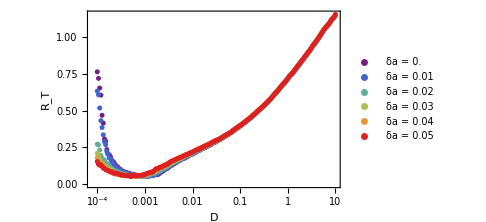
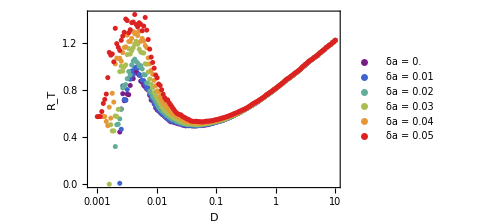
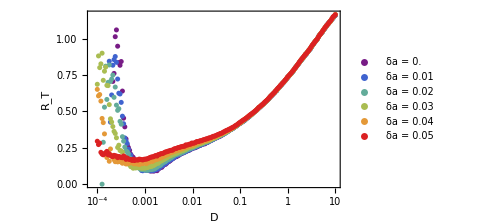
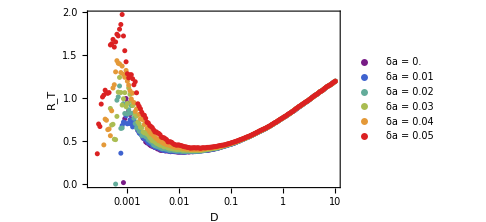

```mathematica
plotsDR=Table[ListLogLinearPlot[curvesDRs[[i]],
Axes->False,
Frame->True,
PlotRange->All,
FrameLabel->{"D","R_T"},
LabelStyle->Directive[Black,16],
FrameStyle->Black,
(*PlotLabel->"a = "<>ToString[dataDR[["as"]][[i]]],*)
PlotLegends->PointLegend[ColorData["Rainbow"]/@Range[0,1,1/(Length[curvesDRs[[i]]]-1)],("δa = "<>ToString@#&/@dataDR[["das"]])],
PlotStyle->(Directive[PointSize[0.01],ColorData["Rainbow"][#]]&)/@Range[0,1,1/(Length[curvesDRs[[i]]]-1)],
ImageSize->Medium],{i,Length@curvesDRs}]
```

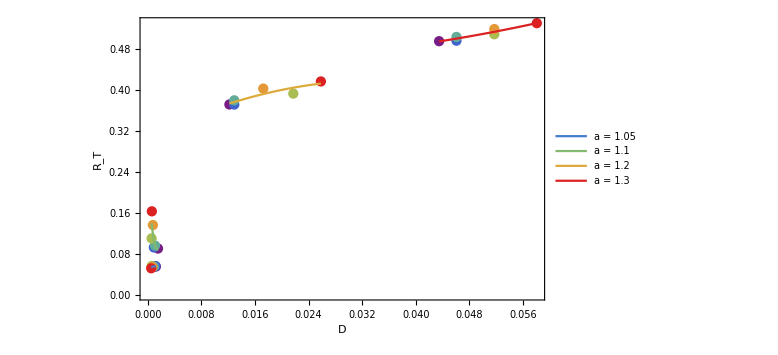

```mathematica
plotMinDRs=Show[ListPlot[Transpose@minDRs,
Axes->False,
Frame->True,
PlotRange->All,
FrameLabel->{"D","R_T"},
FrameStyle->Black,
LabelStyle->Directive[Black,16],
PlotStyle->ColorData["Rainbow"]/@Range[0,1,1/(Length@Transpose@minDRs-1)],
ImageSize->Large],
Sequence@@Table[With[{minmax=MinMax[minDRs[[i,All,1]]]}, 
Plot[minDRfits[[i]][x],{x,minmax[[1]],minmax[[2]]},
PlotStyle->ColorData["Rainbow"][i/Length@minDRs],
LabelStyle->Directive[Black,16],
PlotLegends->LineLegend[{ColorData["Rainbow"][i/Length@minDRs]},{"a = "<>ToString[Sort[dataDR[["as"]]][[i]]]}]]],{i,Length@minDRs}]]
```

#### Exports

```mathematica
Table[Export["D:/plotDR_a"<>StringDelete[ToString[dataDR[["as"]][[i]]],"."]<>".pdf",plotsDR[[i]]],{i,Length@plotsDR}]
```

{D:/plotDR_a105.pdf,D:/plotDR_a13.pdf,D:/plotDR_a11.pdf,D:/plotDR_a12.pdf}

```mathematica
Export["D:/plotMinDRs.pdf",plotMinDRs]
```

D:/plotMinDRs.pdf

### σ - R

```mathematica
newDataσR=With[{seed=42,tmax=dataDR[["tmax"]],ds=minDRs[[All,All,1]],as=dataDR[["as"]],das=dataDR[["das"]],σs=LogRange[-4.0,1.0,200]},
<|"seed"->seed,"tmax"->tmax,"as"->as,"das"->das,"ds"->ds,"guidsss"->Table[
Print@{as[[Ia]],das[[Ida]]};
RunSeries[CouplingStrength,σs,
Seed,seed,
DiffusionConstant,ds[[Ia,Ida]],
NodeCount,100,
WarmupTime,100,
MaximumTime,tmax,
BifurcationParameterMean,as[[Ia]],
BifurcationParameterVariance,das[[Ida]],
Config,
InterspikeInterval
],{Ia,Length@as},{Ida,Length@das}]|>]
```

#### Data for DR 1, 2

```mathematica
dataσR12=<|"seed"->42,"tmax"->1000,"as"->{1.05,1.3,1.1,1.2},"das"->{0.,0.01,0.02,0.03,0.04,0.05},"ds"->{{0.0012033778407775906,0.001135733358343105,0.0009011018251665018,0.0005672426068491978,0.0006747544053110693,0.0005052631065335679},{0.043470131581250265,0.04605922041145108,0.04605922041145108,0.05170920242896761,0.05170920242896761,0.058052255160949015},{0.001516716888470924,0.0009011018251665018,0.0010718913192051286,0.0005672426068491978,0.0007575250258771912,0.0006010276782070381},{0.012173827277396621,0.012898902612533094,0.012898902612533094,0.021711179456945052,0.017225859653987874,0.025826187606826773}},
"σs"->{0.0001,0.0001059560179277616,0.00011226677735108136,0.00011895340673703195,0.00012603829296797275,0.00013354515629298989,0.00014149912974345758,0.00014992684327860457,0.00015885651294280528,0.00016831803533309567,0.00017834308769319092,0.00018896523396912096,0.00020022003718155845,0.00021214517849106298,0.00022478058335487252,0.00023816855519761583,0.0002523539170434766,0.0002673841615839947,0.0002833096101839324,0.0003001835813575589,0.0003180625692794119,0.00033700643292719284,0.00035707859649004625,0.0003783462617131929,0.0004008806328898465,0.00042475715525368984,0.00045005576757004977,0.00047686116977144693,0.0005052631065335679,0.0005353566677410725,0.0005672426068491978,0.0006010276782070381,0.0006368249944718586,0.0006747544053110693,0.0007149428986597577,0.0007575250258771912,0.0008026433522257174,0.0008504489341802677,0.0009011018251665018,0.0009547716114208056,0.001011637979766207,0.0010718913192051286,0.001135733358343105,0.0012033778407775906,0.0012750512407130128,0.0013509935211980279,0.0014314589375234786,0.001516716888470924,0.0016070528182616384,0.0017027691722259013,0.0018041864093920718,0.0019116440753857036,0.0020255019392306666,0.0021461411978584057,0.0022739657523579274,0.0024094035602395267,0.0025529080682395165,0.002704959730463137,0.0028660676169482502,0.0030367711180354605,0.0032176417502507355,0.0034092850697468144,0.0036123426997094303,0.003827494478516315,0.004055460735840828,0.004297004704320844,0.004552935074866948,0.004824108704165373,0.005111433483440166,0.005415871378079476,0.005738441648302393,0.006080224261649427,0.00644236350872137,0.006826071834272393,0.007232633896483534,0.007663410868007463,0.008119844993184008,0.00860346441668451,0.009115888299750819,0.009658832241158708,0.010234114021054537,0.010843659686896108,0.011489510001873097,0.012173827277396621,0.012898902612533094,0.013667163564620072,0.014481182276745346,0.015343684089300131,0.016257556664437952,0.017225859653987874,0.018251834943190444,0.01933891750455232,0.020490746898158482,0.021711179456945052,0.023004301197729192,0.024374441501222217,0.025826187606826773,0.02736439997074672,0.02899422853882878,0.03072112998861759,0.0325508859983506,0.0344896226040576,0.03654383070957258,0.03872038781812557,0.04102658105827194,0.043470131581250265,0.04605922041145108,0.04880251583654434,0.05170920242896761,0.05478901179593945,0.058052255160949015,0.06150985788580504,0.06517339604882427,0.0690551352016233,0.073168071434272,0.07752597488629465,0.0821434358491943,0.08703591361485166,0.09221978823334331,0.09771241535346502,0.10353218432956626,0.1096985797892384,0.1162322468679853,0.12315506032928261,0.1304901978014403,0.13826221737646563,0.14649713983072862,0.1552225357427048,0.16446761779946645,0.17426333860096507,0.18464249428955445,0.19563983435170648,0.2072921779595372,0.2196385372416547,0.23272024789604098,0.2465811075822604,0.2612675225563329,0.27682866303920667,0.29331662783900453,0.3107866187782014,0.3292971255097151,0.3489101213406774,0.3696912707195028,0.39171014908092605,0.41504047578504766,0.4397603609302721,0.4659525668664682,0.4937047852839004,0.5231099308056264,0.5542664520663108,0.5872786613189482,0.6222570836730231,0.6593188271333549,0.698587974678525,0.7401959996915645,0.7842822061337682,0.8309941949353395,0.8804883581643465,0.9329304026284686,0.9884959046625587,1.0473708979594507,1.1097524964120722,1.175849554052158,1.2458833642950082,1.3200884008314195,1.3987131026472386,1.4820207057988601,1.5702901247293775,1.6638168860761307,1.762914118095948,1.8679135990207847,1.9791668678535574,2.097046401323235,2.2219468609395236,2.35428641432242,2.4945081352303164,2.643081486974108,2.800503894183631,2.9673024081888726,3.1440354715915,3.331294787934677,3.52970730273065,3.7399373024788014,3.9626886387014784,4.198707084443915,4.448782831127585,4.713753134116729,4.99450511585514,5.291978735958447,5.607169938205458,5.94113398496504,6.294988990221888,6.669919663030129,7.067181273927491,7.488103857590031,7.934096665797492,8.406652885618334,8.907354638610439,9.437878277775392,10.},"guidsss"->{{{"4f7e4e5d-d864-4392-9e62-035277f932d5","c4bf3c43-9860-4120-b0ea-8cceb86ad03e","ed1a16bc-f255-485f-8cd2-86e879f526ea","a839f4fb-3ebb-44e2-9530-d5054b9f7787","512bfed6-102d-4540-9236-058b6deb3edd","91440996-fc0f-4b2f-a559-89920a91ad0e","696dad25-9e2b-4bc4-9c39-d90b5edc7d20","9fb13194-4ca2-44fc-8f68-18a304c0f22a","c12950dd-f63b-4cee-8dc7-fd4dcc78160d","3fd6ea64-24f2-458e-b1f6-b08b39ab7e3d","5b1439ed-4eeb-44e4-995b-acd4ab52025d","1b006b86-20c0-4804-87bc-4f16742f9557","04b424ca-35e3-4862-846f-71739abbffcb","fe70db0b-37c3-4b6f-84a6-f9f0d27e88f0","d19c2608-856c-4460-9e3c-38b827333c46","b9c98302-609c-45dc-8e02-23afff56fa4b","e6f6d076-de22-40fb-8ad3-ad06da3790ac","61035768-7a24-4933-9164-64c39619f233","0e0b47c0-90b0-4c05-ac21-23a2d6ed867c","03ecbb87-8efb-4cf5-b504-c9c61353e915","cee31d2a-218e-43af-891f-4e20bfb0ac9b","1969abe0-3bc6-435b-8652-c232f6f5d92c","d7fa7ad4-74c7-475c-a18b-3252474c993d","4187d20e-ff78-48fb-abeb-de9f915451ce","339512d5-9d31-4f46-947e-8c6568053a1c","2f2eed03-ecef-4d2a-9f81-d42bbffc95d0","b4f5892a-fa4b-4ec3-8e00-0b9f653022e5","54928573-ac5e-4fa0-8549-144acb9de57f","44a753ab-af05-480f-be75-cabcd8d8da71","59a3b3c8-3ff9-4f7e-9851-8feed840b9bf","d3fba90c-996d-4851-9aae-bc76eea02788","45dd6728-880c-4963-ab3a-e2649958fc8e","a07ca69a-85d2-4a97-9346-ecdefb4ba8c3","41127d96-68de-4777-9f82-ca8967715868","2c13f90a-b295-4d8a-b037-6c28903aa025","9a38de6a-812d-46f5-99e5-1f373f04099c","558f1e87-ff0c-4b78-b484-208eda3523ed","182fee12-048c-49b1-9289-f7075b000351","8a9b9ae8-8851-4f71-b0a8-e522f0fa4272","e3598f79-787f-44bd-9057-5e9e9330136f","533215f1-a383-4f0a-a1a4-cdee9726ec84","776f41ea-a076-4316-8a08-368ed10eda9c","9a750a75-ad5a-43cb-823e-b66bccd5e029","fa0725c4-b536-4289-94e1-12a51a954fd7","9e0366fc-edfa-45e5-a1b0-a2f4e5b3a8c3","d466566a-13dc-4235-ba8a-bff653c9b73c","da1590e2-1219-411b-897c-56cfa058cd9d","a09a715d-a147-4d1e-a9da-e5fd45a1f705","6a19f860-9e67-46fa-b151-0006e9a13ae3","5af041c7-aaf1-4030-8787-dc3ad3370945","b13bddb9-5869-4f94-9446-4d48979544c7","3bbf9897-45f5-4c4b-acd3-c30988ae560e","20bb14ee-ee79-4ad1-879e-34d589cc2629","54dec78a-b2cd-46c4-a874-dc9eb2277fda","d63a6f77-9ddb-47fd-aa89-bc6aa00354cd","7530cfd7-bbba-4cde-a2d0-ff9a35e5cff7","4c4f515a-989e-4b87-bdbb-77b99e060ced","d9e6f710-8b9d-42fd-a020-497f8d564a83","ee110f2f-9b0e-4b31-b6e8-369117b3443c","55e06fc7-aa4a-42dd-8f1d-ee923db17545","d36e36ca-0951-46aa-a69b-e03b7a2df9c4","eda5d18b-6b2f-45d6-b512-61cfb6a04b58","916b88f2-81bb-477d-991e-533de8dcb94c","39635ddd-ade3-4414-bb27-db69b78808f6","8b2f430a-4de3-4372-9582-c2f7fcb0d3c3","26dbb268-defd-4537-89d1-80cba0911197","29ab9034-c190-4a28-9708-9198c5cd9659","37c00691-0bfc-4fda-8098-9670c1cc86de","9c9e0a35-6693-4c91-b88b-dbea56287dcc","bdc2f7cb-81bd-436d-b987-a404d5d4d45c","585bcf53-e27d-4f47-86e1-821a1bebed5c","1587885e-904e-4a8e-9cc4-7d8cf2e6cc2c","b1d425ee-ebbc-448d-a645-b8c84afd300a","bbc7230b-a753-4d26-8985-5245e27ed4f5","ab8c7aef-f6db-455d-a88b-1c7aeb79a37b","e22f3ee1-8cb6-46f8-b613-b618691f41b0","0f3c289f-2ce7-45e7-a39b-26c5ecebcd29","260b83df-4562-4e4f-8af8-9f9543039c53","efdddde7-8ce0-48cf-ab67-af1dce16ad88","2cae419f-d9bf-415b-a293-9e68714d155a","a7013be2-bede-4cc6-a43e-79c202cedc99","16d2685c-94ed-49a4-bd6b-6db5f4c443f7","15682778-1160-472e-8e85-f00a0b2b4797","94a05b20-475c-44a2-bf76-6af783d9c686","fc278313-54c9-469f-a15c-7a2612a28477","1eef5808-756c-4279-894a-ca4a007b0aa9","2e4a43ea-75c9-4397-be9a-167052e309cf","acb64da0-8b07-4544-bf75-056f04aef2d7","c6ad1a62-c73b-4420-8616-01fe12ac5a0a","6cb370d3-d2ee-486e-a942-55363ed3cb2f","4fc59e50-fa3a-479a-8a1f-c940bc143c64","8de6d3fc-a137-496e-8f81-29ee7e4ae1e6","73fb51bc-a5c2-4664-a93e-0497e5f38527","a970e964-be14-4b5b-9ecb-2e53e729e79c","cb0327e3-4c7b-4218-ae3f-ebcc44fb83a0","ed934f05-4ee4-479a-a7de-a7239be9b3d5","1f51d2ad-a154-42ac-a405-6859de40b6e4","e2b43c0c-b25f-4964-a465-50c1711eec92","b6e62c38-758b-4ebd-8348-4895c8103753","4ee75f03-ffcc-464a-b324-de562c54dd73","72d85a34-2349-4881-999a-796785a33a38","7cee1da0-c0f8-4272-b029-89f626afb8df","aced5296-9a2b-4b34-b605-36f624703228","3cd824ca-0c26-4d8f-968e-a60f0b5e54d6","5f93b525-da2d-4ff9-91c5-fc5a089c1d18","8b70f453-a02a-4d20-9d59-1ac064313d0b","9e20b09f-001e-480e-9f47-9cbbff60cc34","57f841d1-9c72-4d88-9ba2-a2e076d7d5d6","aceb200a-26f4-45aa-8785-0e0018edf5e3","6aadb9ba-6d33-4101-b2d6-3cf3e6774104","227a62e7-5570-42d3-8597-1e5bccfc46f4","84978d04-f6a7-4fc0-84ae-e9d003037de7","385642e2-d13f-44ad-811b-8ba0b2355fb3","40e9b069-0240-4fb8-840c-5976577cf33b","58377822-2fda-4fd2-913a-c88c9cafb77c","b0296f13-d9fc-4d20-b25a-f7dff68abdf6","188931a4-3f19-4a61-8fd4-3458c175c9b5","cb1d867f-c673-426c-a2c1-5b6f7bd4aa30","6716aa50-62f5-4b18-b18d-2893f55ab72a","4d99f07c-a1c2-4a81-a513-9f75dd876235","d1154d08-20a1-4ebf-b751-f920294732aa","3eae84f6-2d4f-4be9-a381-743ac7a818f7","6b8c84e5-eec2-4be6-a52d-f7401ef58803","5a9447ad-f477-4df1-8427-0baec2ffaaf0","d81436ec-d104-48df-8165-976137551c20","ea2b2529-b8a1-4284-b00b-398a62eef7dc","ee5e85cf-a6fa-421c-842a-286847bc4d87","69167e92-c0a3-4443-babc-648de6d03c51","66f546bb-b5eb-48e7-82e3-5c86be8bec07","e74f92de-4a8c-4968-a7a8-6286ee8b5b5f","cf9dafbd-1b64-4338-97a2-0cf15b254525","cf11f135-1bbb-4197-a02d-93b85d2b64b0","7991bcb4-557b-4964-a429-5d7d5444499a","17461f01-734c-4d4f-ab46-faeda3ab2076","4a6dcc06-e970-40fd-8233-7ef6a397e8b1","084ab66c-a440-4e21-a9ec-6252eb7c9283","fbb1881c-75ac-4ff4-9d12-2aad8839fcfa","c0e47caa-b07e-49d6-b326-efd1fc0e8eb4","313471cf-6806-4a25-98ef-cbfb17b968df","94b0b768-aa72-4b5b-a4d0-16b1569c7971","e1ad6df3-169c-4cbe-95e3-973cea2f68e6","34f70f9d-4842-451e-93a1-752d9030ae75","018d79f2-6781-4016-8d7b-9fb6c0b18b3b","e7a1df3b-cc7d-4048-b9c3-e4b1b8e0c373","3b2545d6-5bbc-4c62-b8fe-5a9a19286216","a48a7030-2c86-4bb8-b9fd-825cfaed02b6","b63a79d8-c796-44aa-ab99-c70873efc751","4979ba31-d548-4396-95de-47b32f599075","d9cdd924-0109-4bdf-ae7d-e097d3669716","c8a3d2c5-73b0-48e5-9645-68d74968d268","8fc06bcb-c6ea-445a-92ac-cea8176c3204","03be1de0-b5a4-49d6-a311-46f1c32c6f61","79fc6b52-e796-4abd-8c79-d7e7bf40d7e5","d949c3d7-0230-4b94-8ff1-10137dc8136a","f390b061-8292-4459-ae2b-8121051b0d91","af95200d-01ac-490c-800c-3f28e634eb37","bde99942-a2f5-463d-8342-96d7469f02b3","d3d38c82-887b-4f3f-af28-30050969f023","c07bdd04-1ddb-4e31-83ea-d475b77f8fa8","e20d24a7-2021-4d3d-b792-57ba77237a89","661c304c-5676-43d5-850d-dca453427005","fa2f771f-c850-426e-8176-8217467c9725","6de7a6c6-ecba-44a7-966c-e2d4be256180","4905a72c-a141-4c00-a82c-80a2dd3a1ebd","39f019d2-dbaa-4381-b599-ed1483831ac9","0716b672-a745-40b4-93cb-7ba7578bbc6c","8904d0a4-6f43-461c-b7c5-7f9a18c6388e","233040d0-8d72-46b6-8367-5ab7b1e18939","4da5ee7c-69ca-4820-9938-b660482be419","40f01242-1713-4500-9062-f48333ddaec2","ac13c173-923b-4734-88f2-1f000034b6f9","2f2806a3-5c0b-4f24-a447-0ee3a22096e6","a48ca880-7273-426c-80a4-7c3c4d86cc06","82786bc9-7838-44ab-8a57-e8d2ad267d67","442067b8-133a-4013-b822-f7d7fb98ba50","d6540fbe-e54a-4bec-8951-f979c1cf0697","525bc14a-db97-4659-a10c-6beccde27927","776bcc28-0eaf-4746-9cc7-143da0ec15cb","6817916c-adaa-4f81-b90b-082d0e0bc2ae","a368bced-f558-49af-9cc0-6f9ac5e58678","5683662e-66e4-49f9-9d14-cb93ea30f492","080fb303-eb51-42e3-949d-8657239064d1","9ecc4ca3-08cf-4997-841d-2144fc98e12f","83f22409-e220-4b6a-988c-cc93b435c11c","2c884170-5429-4556-a172-b38a50f2540a","780fcd5f-32e4-4274-9ba1-8821219f00af","d1032651-6665-4e0c-8914-7c6a3781b594","e0887567-ef95-44ae-b093-f9d2bd005752","14be7916-d67c-4c00-9fb3-acf4f6e2fca6","b331b715-f071-4691-bef3-152580604cc0","afd508f5-5c04-4fa4-9400-15cf3a3a99ab","bece595e-2ebf-45a7-b7ed-55d7afc0f98f","e88a87b3-93c4-4b68-8d93-782182ebb505","c6e89eb4-5c06-4004-b559-3683522c4a16","5280050b-65f3-47b5-a7d4-ef5f03bb404f","dd352a28-73de-4b0f-bd9e-deada14e0eb4","c5e988a0-9067-43f4-a35c-2df2fe542cd6","a950bc26-aea1-4fa0-9751-e762023367ea","7423d1af-68e8-46a7-9a30-efc2854dea5e","83074cb3-2ad7-44e1-9752-ab4d91f072d2"},{"255e3173-beea-41af-8a09-4cfbe9d89fc3","a8d777bd-fe8d-45cc-86a6-8762bd5f81c0","46d21e90-a5ca-4b9e-9613-8830c85bdd63","4b321258-f4b5-4d52-aefe-1ab80666dd82","c19ae435-67da-430d-8a32-7e19a951798f","b24e5a8f-d059-4902-a864-e91a40cd22e8","634abf81-0d47-45e7-b403-e3000749be30","a3ad9b96-deca-44bc-81df-4847a9499809","3438bd85-8b41-4284-8944-bee0806ae5e2","29f44a0a-c4b2-4435-8bc8-a0e5a0ce8390","d3bef2f9-de98-4de5-b236-0a758467be74","779f5055-15ee-40b7-aaf7-a5321d7af2b7","9c30ee0b-86e9-4666-902c-0489e8fa04dd","adb89595-7f51-4510-9252-d3d819ea7926","b4306fc3-c40d-4d8b-9a96-8fef09e9e7dd","aa5ef770-5884-48fd-ab5c-60f15d4746d1","08b23b0d-a58e-49ec-ac49-1c6620740cb4","f8cef20b-30a7-494b-a37b-dd50302f5d6a","0dce09d5-c8b2-4fa7-9c4e-6ff939a7c49d","79a313a9-524d-4364-afdb-6d753b68a415","b7debca5-88e9-4d93-9b01-751de0e5111d","342b34a1-7400-4b24-8f67-c38f466264c9","bd4e593e-b921-4ccc-969b-0957d72fb986","69b70aae-bdcb-47d0-9b1c-4be38d508a6b","9669a49d-372f-4e9b-8c8e-f0ae3bc562d6","3d5cd6be-c708-48c1-8985-a4d31bd55886","37653917-a31e-4b4a-86f3-f8cd216aa8db","0821e0da-f3c2-45b9-8acb-374cc20a8927","a35e2067-6bbc-4e92-9cdb-adf0280fd32b","d97491a5-b9e3-4200-931a-2970786e2565","d9bf3c04-b6ff-449e-95cd-64cf8ac8e0ff","3559b46d-a4fc-44fb-b5d5-fe9b8ce4700e","45649713-6d53-4867-86e0-4d7a7b9c9891","41b1326b-7292-458e-ad19-b0753b22bea2","7674d2cf-6580-48d7-95a3-88cff20c4aa6","822573f3-b368-47c6-b462-af6e93fbb516","4393907b-3e3a-4fd4-b18f-e03fb26dfd3a","38d24a4f-3c40-40f0-85c1-0f8a71999968","7718d299-43f5-4407-8df7-3cd819575a4d","1067a64c-c311-47b9-b84b-ba1c897bbe12","136da7a0-9a4c-4b55-854f-eb367b218cc0","d3166983-8c43-431d-bcf1-87b5fc0d1229","80186bf8-c7cf-4e7d-8ba0-9d469b70e416","7447cff4-5db4-43f8-a803-3243d7b14500","45add63d-38fe-4c3d-8f5e-6bb4d55ab637","ac95eeed-35a8-4947-877c-fafc8881d514","080734c0-de44-469d-95db-8509bec54bb3","65dbc033-db63-4943-9ac1-1a6939c6ef71","70d45a9b-2e98-4c46-b83f-217b90d6259a","4a19988f-7ee6-40ad-b1a5-cb7fe839f935","e6b41ce8-60f7-40c8-afd9-befa4d991283","9e5c9d60-0f09-45c0-81cb-90c64d2d412e","09033eec-9f35-495d-aa4f-6884ad1c9a3e","a470696b-4c45-46e7-a8bc-779fcb6d9d8c","736bb336-a8c6-434f-91a8-3b9945535a51","2f122cda-545e-4955-9c9a-6c52578fe52c","22f95ad9-fa9a-46cc-b0dd-1ad703caa53f","ae26ca6f-6688-4b30-bd31-af1b27bdf3e5","2acc22d3-be40-4140-b541-6eb721c85441","14947d8a-1b7c-4daa-a4a3-caacb28fa919","62ee7ea6-4f98-446d-aa7b-a3229458c8e8","2414aaea-aab8-42e2-ab5f-f8ca4cee2978","341aefc9-dafb-4ea0-8bf7-dc649a470354","714f33d3-ab74-452b-bf89-61b4df30b0ac","0adfefd8-2946-467b-8ca8-e407668528a5","04a1bb3c-fa7d-41ee-aad7-d2b30df3289f","c2a52eed-de52-4e41-9b04-d0cb4aaecf54","14a4b58f-6df7-4a0e-b3ce-1a81f1f04422","ddd267cb-6254-4259-8685-1791964d0d20","b1183cd6-f5aa-4efc-b8a1-43959f2a22e9","6541f449-b9ae-4f6d-823d-6d171dae1ff6","4fcd22ba-4683-43f6-a2c2-6102bfdf2a88","4c59d420-3527-4835-8cc7-74623f7e6ec4","3d807302-f22f-4816-8df5-177e0e037a7b","8f0ca982-511a-4319-b5a6-7f1e81af4b97","dbc37a85-dbed-407c-bf0f-26289cb89738","75f60808-bf54-4be2-95b6-5a49a3ee1b18","4a3ad427-f004-4cdf-8564-e26294f1d30d","75b1471e-76c6-466b-a6d3-bb13e17e971f","43842e1e-8f9b-405a-aecf-f00f2db4f19f","d3e12951-1a5c-489d-9cc8-17dd6c3f5d5f","73451b73-548a-4dc6-87f2-a588f83ecced","a44d6fa0-1c2c-406a-babc-efe4003c42f0","87b4e930-ed06-4fd4-b178-7fc1b5ec7768","a120d23d-8046-43ee-9213-17120899ff85","5a174fa2-8382-4c21-8a09-ec99ffb87938","eea53ff9-2032-4f75-b28d-3475b20d9d19","e96bed12-f45e-4644-acc7-c3c6f7be7c85","6b9dc883-c84c-4063-818a-9e1138f40939","d6e0e10b-ff75-4752-9af5-34fd71cbab2f","903ae028-e6e2-4df3-95db-7db45ac16df4","e5e62684-a5fb-4b4d-91a3-83982dd61ca2","f88dd2b1-6f26-4a93-a193-45dafb2c5eb3","5bff6231-eee8-4adf-939c-6bd18b135d16","675047c1-7991-44f3-bf7a-05da37fe6624","df15e3ee-6a3b-4bf2-8ee2-385e0aecb257","a1bd0623-67d9-41fa-9e7a-7e7f061dea15","6a633cc2-f0f9-48f8-8de2-0443f748c240","40f2cbe0-dc01-4d2a-8156-b51204402dd3","f3292634-4b9e-48ed-8656-86c1e9b8333a","7e74cf57-af9b-45e4-a642-884e43d9e6d0","9a365b0d-d26b-4989-884d-5d8851976479","e6143b8d-e128-44b3-9967-7132c91b45bf","180757c7-c835-42a6-a956-8fedc59f2fce","77f4d49f-0073-4f86-9f19-196e34c4c7c8","01a052ab-ee82-40f9-a42e-d5a8b19d2276","95fbf5b9-c96f-4d44-8a1e-4aabc6ffa1ad","cb5d6299-2413-45d4-8330-23a0237e053b","bc8336a4-19f6-476d-9ce7-e6f968a22b53","7f60fb80-ca62-4789-8ddb-49bafed0ddda","ca4ccd9d-9ec6-4cf0-be80-8dc0ab344374","91208231-924d-45c4-b254-891fb3b9857a","aa58a5eb-313b-4b9b-80af-f05b9780cc89","78a93c99-ef8b-40f3-b1ad-1d4a78f19732","b66a71e8-8623-417e-9fee-6ac78a4b6a31","959d80d3-1c9a-4b4f-9014-014a98299388","7ffcf046-69d9-4be0-be32-88392396af2a","4850efbf-daab-48fa-9789-8dac2956e75f","09b4e647-98fb-483c-99e7-f50793c13c04","5395dd03-6546-4167-95b3-4cb0443cf50e","6c414909-b304-4cb5-bc05-f766c75d9f80","d3189e83-65d3-462a-a687-0720a95d01af","8edd0cc5-5070-4ed6-a24e-18b3bc10e022","09fc3fca-9a30-415c-a8fc-5a50806df08c","5b1db563-4ef0-48f9-9a61-c9c5aae7303b","e7573314-ca8d-4965-89df-6779ecf11985","f088b75a-04a0-4a00-a824-13d54a4e0eac","9d55eb9a-45ad-4980-803a-15899a1a9ee3","e6f91d9a-b3fa-4119-b838-29c0ae74331e","15adb528-7a51-48fb-a87f-d1547ba85b61","f7585a05-0d80-4204-a2c0-9924e7e769b9","ce6302db-28b3-4d08-8f6d-e943ffd50ca2","439137a4-7a30-4ef6-87a3-5c1e0d54141d","795d679e-7014-4ddd-9a55-5eae09ad8338","c1677ccd-f922-481f-9f6c-ffc5c2e837c8","e7d96da6-c65a-462b-a73c-a4f368b5727c","ebb0c739-2ac3-48a5-9f0c-f36cf8892dfc","c705a7bb-99cb-45af-b185-0e0fb9d590e2","0bdc82d5-26a8-4277-8f7f-3fda90f023e5","8381ce7e-9852-4bb2-a4ce-f6253260cc50","ebb97d79-08c8-4987-96c1-51c025adf026","81ffdc19-715d-426f-9d67-5a37e438fcc1","0c33947b-e9f2-484a-b815-cb67b70225f3","58930e75-d12a-45c9-9259-893a83028bd2","369e73c1-a165-4ed3-abdb-edcb8dccbfab","b6547468-cc83-467f-a727-60ac62de8cc2","80893c84-4461-41f7-8c3b-1c9e01e32b37","86a464f0-38a5-432f-98f6-03b905cb811b","daa7d2e4-791d-4ce8-8efd-8cd47095e5ae","d69d5a2c-6aea-42ce-985c-e5efe3f9f3be","f2bc9e2c-001a-4184-a8a4-4aa97190a4ed","5c939e41-500c-4075-ba01-c4a3a646736e","fb7dd386-e1e1-4808-a31f-40ab19d2fe3f","2953b68b-4bec-4c72-8fbe-e34382e6ea36","b6f4ead9-257c-44e0-899d-c7fd7b003c42","8ce60fb3-8d8c-4fb9-a125-5e22bc07cb79","e93fcf10-4b9d-4635-81d4-b134646601ee","3dbdcfd5-cf7a-4833-a048-f735ce2597a1","b5fd2ab9-755a-408c-95d4-c02108c0833f","c91ceb84-5683-411a-9725-385077e8bf65","97dbfe17-ebb3-40d5-a498-e57c25f72cc8","7f90f1e0-d7be-4a8e-8705-d215915866cf","f7bd59f3-cc27-45f8-97ef-959902f3f188","93148be8-8066-4921-b47c-ecd393ef1614","c4c448ab-bb41-4cfe-aaa4-f64d4b9fb6dd","f723df31-af5b-450a-9ae4-ad6e6f3910b8","cdaa1f2c-0b5a-40f9-bce6-dc2e761c7d15","d031c1c1-c2bc-4be5-8708-610da1ad7888","456c6b8a-1a35-47f3-b0c2-fe4f5f9f3dec","f2650fd5-6a0a-431b-b2d2-1d997ab7bdac","9cf8bab5-4c6f-43a9-9d5a-44c3d5b05e28","44170c5b-0733-48d2-bf32-7a4239e6bc14","357d56fe-b411-478d-bfe1-69564d9e5cf6","c8e735e6-f027-42b0-9054-2008c715aba1","25c63e18-0c7a-4440-a468-e99871a60745","74e1ab85-a0c7-4a3a-88ce-0a7f206b6560","e304e7cc-a4eb-4d2a-ad99-e2e250b03799","dbf44395-913b-481b-807f-877e5265001f","cb252b6c-8e9f-4662-8e3b-1ad860af0bb2","a388da59-2320-4e5b-a89e-be1057a2e04a","71d0f3de-661e-415d-a69a-1191e931ecf2","e3c7d025-af04-4fdd-b12b-c431921eaef6","8f767190-f5d0-4f4a-aeb3-51a51dc5a6f9","435bb918-084e-4c98-b642-7e879c4c9130","aac89e1a-7458-4bff-acf3-a2e5af683fa5","f55904fb-1186-4237-9e5c-5da40184c3c3","31259755-9bc7-43e8-ae8e-192d74ccb1ec","708741d1-db30-4211-9e12-45283fc4f494","76c17181-96b3-4b02-bb37-73673bf91bc3","f69e2a30-294a-464d-94eb-4da4c616e85c","61ebef6a-a918-44c6-aea1-a4090086735d","48ffd064-b1e7-4027-9778-a0f95b89a717","ad98c0e2-421f-4a5b-b612-da7188490cc2","9b41a1f5-86db-4d0f-b6c9-3d160a94e5b9","d867cab7-abd8-4f03-95cd-8cd3766c805a","134b60ee-eebe-4f5d-8152-a29e9063999a","4e0caf14-9a6c-4ec0-a52e-425e6dd041b0","50a1bb35-9cb5-483c-a39d-95e6421a0065","c7a0466f-5590-4f68-b5f6-309d7198730e","37587ac5-a22b-42d4-af80-85d8ce8c9bec"},{"f594c8e8-d8d2-4234-9bc6-6208359d847d","900efbf3-4563-4936-b397-37526f466ff8","930d67b4-c1c1-4de5-be8b-8980491612f5","975cabd8-0cf0-4f9e-865f-d82eabcf1f8d","10f2296f-d4f0-4865-b833-f4a2c066f146","5753df54-0f98-41ac-a8e4-beeefb01a79f","7cd7bd41-ac32-4211-8c22-3bd3653eae14","a991fc5a-a22a-4b22-abd3-a7a92f9323a3","2cff6688-071e-4a27-a0ed-68f877a98726","973ee19f-2420-404a-8fa2-14a354214506","6100a5f8-d75a-44a8-8fb0-7c060c642210","9aa595d8-fd34-442d-a8ec-dd70ced64569","1127a170-65cd-4a7a-8cb1-a373ac908642","98f2f6df-2d0d-4365-bae5-5809516d2dc8","4b30ab1b-5bcb-4896-887c-534ee7aacaf8","e6b7693b-ba21-42e5-9f28-05f78c0663ca","53cb32b9-eeb0-4a92-8627-988f27adad9c","8d61f809-a9b7-4e9c-b9de-926ae2fef15d","60068df6-e442-4a3e-b8af-eb48eac86edc","328ae3c8-f0c2-4c8e-a58b-2838bef8bf47","b465eba4-2a89-4f6e-a790-1762bf5b15ab","4ef4b246-4aa5-4551-85ab-b5985bdf0d81","b1f50ec4-a92d-42dd-877c-8bff4dddf1d7","a2fe2151-ce35-42ad-9e82-4b88968d8c5e","4e864fc5-0ffc-4dfe-8fad-148794099080","084ca00e-4dd1-42dd-a133-86ac9ed58b84","7e5cad78-4d08-4b5f-90ff-e859984a1075","67aa1c4e-134b-4c8d-a92d-2c54bb2c9976","a75d8f70-0852-4f40-8ff1-8026989c5315","712107a8-fa85-47be-ae3e-bdfd31d94e14","6f2c69d8-59f7-4086-802c-6c8a98b4ed2f","42c8d3d2-8dd1-472b-8538-f88237dd29cc","b26a21da-edcd-41b1-88b4-e99788b63ef8","0d7d03bf-46f8-42d4-bcd8-e91d0eb70009","e38c21ba-d14b-4a01-876a-c6d482370a13","2cfdfea4-446a-46bd-8080-0e34caf7eb85","e9ca6ba5-6c96-415d-b2e2-302b0caba713","709dbb23-e694-43df-8cc3-c071dbb1ad2f","156f0e55-053a-4095-a995-7343f349fdd1","2729a4e3-ea1b-42d0-8a90-edbb70c2be25","dc3100b4-5525-46d2-9535-63e439cc35d4","1dfcb0c4-9458-4ba8-92ea-1b4d6a9d3ef1","8333f198-fee2-4699-a9ee-53acf305dd8a","1f6f2948-ed1d-405e-aa9b-b6d0a1bb53c9","0843df6c-18df-4ca5-8cd0-e734b990a2b6","47b675c8-6420-4634-9203-7d672a72f0a8","e4fb0bc9-0332-40b3-8096-0a4ebf1bcb3f","6323c54f-cdc9-4d95-af94-a35f5e4e74f0","d34c2f35-6c3f-48d9-a819-53e88991389c","bd8020d3-16be-4b46-935c-ecba0c14995c","f2b84d9c-7566-49ec-9d6d-d8cacf7d47dc","202bae2c-e169-4f2d-9f89-68d7bd5b5ea6","9ee4fec0-2a73-452d-9337-65b7a5f9bf8a","d04004a1-b812-48ca-a34c-b95bc6b3acf7","524b5f7f-3fd7-44e9-a4c4-2277a1842e94","2706c7e8-4d6e-4829-b622-ff5ce0baa105","b74b7fe4-eaba-4d24-8d18-92eafa16247a","08641970-839d-4eca-8813-b62b61b5d06b","9be10d52-72d8-4fac-891e-f22df93ec10e","8e3c55be-d1e1-410e-9e4b-d8a808af6021","67de8596-304b-4644-b06d-9fa5dafec0f1","160642df-74b4-438c-9703-9dbdd89fd6b9","7c799add-7e40-44df-a785-f42debaed64e","bb09ecbb-6694-4dd5-9f2e-24388e18d664","db0e4c01-6a28-46ec-9d60-2b80aa95842b","d3f778af-6a27-4c46-a44a-b87c6fdc50e8","91486951-c3e5-4ceb-ac22-a3c8568ec4f9","6dd0d486-1850-42c8-9880-2c511161292e","302401ad-abf5-4435-9505-2d0e1175f97c","81ae2b02-679d-4174-a2b9-8786be6d1d19","6917a68f-2dc9-47af-95ab-9f9ff6b4eb21","014b1ded-1cf2-4e9d-828f-7ca04370cf80","0ca47285-e4cc-4892-95ff-176af9eff957","7a1aafb6-6f47-4ab9-975b-9568ec7d3529","da5a7570-2259-478d-b45f-357f5991e450","309cf88d-8f22-466a-bfe5-0ef943f3b373","0412642f-4030-417f-9573-138b76f9adb5","ca62acee-35d2-4c46-afe6-42eac9044f1c","30b8a5fe-d4c6-4b89-912f-fd490de77490","b70bfcab-b187-458c-9b7e-a2733e25a225","20bd7503-51b6-4761-ad10-2854e4b583d3","94f01e70-375b-4122-9c1b-767900ed2188","cfe2b025-9fe7-4a7c-8d83-3f79d074a212","8db79fb3-c13b-4f75-b2c6-3ff867ea4308","d4bb4ae1-ff50-4c00-8f0f-2491935020d8","94fc7d64-7cdb-4dbd-97d2-4e8f8646e68d","0cbcb5a3-92b5-4f7a-94b6-ec986301756d","53504203-5d49-4d8b-8101-19a14f621224","b77f0e50-8fe1-4fd9-a278-806669cf02ba","f7a0c399-10a7-4f59-87b4-ac1750825bbd","7f3593ce-087d-45b6-bafb-aa921a73d4fd","ceded074-7b8e-4f31-b113-ecce1d7444c0","4b2e7640-c5fd-4984-b877-b2dcc34a1e02","3feb00c4-556f-4153-8df2-b377b0977e3c","fdb5e5d3-4d33-4b91-a5aa-af0d7cfcd613","18db24e3-3475-4ee4-9d69-8eb8182e608c","c8bb8ef6-9476-49db-aed4-a1f273259ebe","a7a2aa8d-36cb-4600-b6dd-b0031cb66c91","cd830bac-deeb-454c-965b-beb9ef14ab5a","0a6a8c7d-0033-4b9e-bbb2-57ef66a35f84","b6884c42-42fb-4fa5-bb95-f3f2daef2299","eea83e68-bf5d-4a76-b2f9-06deb3b9d22b","99c14431-35ef-42cf-aba5-c4d364b59926","3716e888-6853-41e3-8c04-238cad3fa105","3b2d1e7f-3843-49db-984e-da73fca34f72","a54383e7-c212-4c8d-ac67-afa332427dfb","989f4a55-1e92-499d-8105-64ae2d769182","9eea446b-72dd-419e-833a-ae6ba0cc7c9e","33d19bf8-11f1-4b45-b804-71e857914942","4541f436-9f30-465d-b4a3-06852f6dd910","b06a098c-bc3f-4486-9dba-c03ddd5c9939","486e4d68-e2f0-4bb3-8026-5496b804d966","0c3e2145-124a-476f-a3c6-da399731bb6d","d45dec48-3012-46a4-869a-9f3bfda73fb4","bf96f09d-f095-47cf-b41c-419002190d8a","6b93d026-91fa-481d-9585-ae87b53b23fe","582cf2ad-5668-4963-b3c3-e8222e430024","41128998-9ec2-4680-ac82-3f671135e365","090205f7-3008-4a9a-bada-08fd84f209f1","2858c717-050d-47a9-9dd7-35708bb5f7a5","8e56c6a3-09f2-462e-a158-821966ca7a6d","635e728e-3b27-4833-9a47-85b81ecea09a","85925485-b75b-4d9c-b481-1778ebff93c8","91dbfdeb-8e36-4fda-a52e-effc0bc9f4d9","01339886-ceca-4b4d-b28d-c0479fea6bd3","a200a857-c941-4c2c-b4aa-bcb59a95cfe4","c81422e8-d9d3-40fe-87e8-7b6fc518902f","a909aed2-1b35-4f84-a977-f58d843549a4","8566df5f-f6b6-4713-8910-e2e8ad828e75","baeac029-75a4-4031-b288-75b18c2ddc8a","e5e76168-0a3e-46cd-bef5-d32b090719f9","91fc4a05-26b6-4b16-9406-4ecc890112cf","fcaed007-d5cf-4781-a618-bcc995554b82","c686a249-34e7-40b2-9633-f18a0a1dc7ef","84343385-5b65-48a9-976a-798418d4df91","28243922-f594-41bc-95b3-fc45305d02ce","65441c74-4fe9-44f0-ba8c-1188e961322b","c92bf817-b05b-440d-80fe-9d3c0d5cf73b","67c2219e-0db9-46b4-83dc-d014e241ebcd","4adea037-3686-49d0-8e01-89be9c984cca","254cec92-ea9f-4f1b-9e2d-4807a060a0ed","c1b96614-0bd2-48eb-9ebb-a75464bb453d","c03be014-0f4d-4359-af29-8684ba21a1bd","9b58ff13-06e3-492f-a905-44db59b3cbd7","d2beb0b9-74ec-4b00-9498-fe1ceddc4cdb","a80140d0-1645-4e75-94a5-f4f94e915d93","dca8f679-56b2-4b02-a394-d725dd91c8ce","f13d4c94-83da-4225-addd-113a57112993","7e9e65d2-8c2e-41b7-900f-7ffb3c341f08","fb2819f4-b394-49b8-94c3-bf3e856c23de","2d9a017f-9607-4d8d-8f1a-2d3284f1f474","4d7f5401-ae03-4c32-9965-7e45d136218c","c2e10a38-85fc-4fd7-b56b-4a870b311b4c","1cb1eeca-a4d8-46ff-abd5-7a265fe21703","4c154d12-971d-4195-bee5-55e44512291a","8e72e439-5529-4e66-9684-0f39a3cb88b9","db446edc-295d-4fc4-becb-d00c44bf8a91","5cb2013a-736e-401d-a43d-097e7dfff21d","0f060a3d-e101-48b5-92d7-d3641cb6bdbb","1940257e-da6b-434f-953f-020d7af3d802","492d7f96-8084-42f3-81c4-61a730eff667","a60a21f3-1379-464a-8e64-ad10a9f06170","d10029e7-a9a3-4318-a3a0-da37616d7278","39f7ca60-8224-4a4a-8acd-781fd3eefd13","9233af10-8ff5-486d-b422-ee297631eaeb","97f66da4-99d4-40cf-8876-dc7f2444e0b8","e355cb66-2120-4382-8c1f-024f3034f90f","074c8c4b-93b2-46e2-a2ed-c793d254360b","3d603add-7e3e-4bdc-9906-509bbeb1d290","47f8ab60-85fd-4091-b004-360644b5a96e","1ab9fb98-bf07-4dc2-bbc8-fb91678387d1","9978f231-3622-4a89-b6b7-f8ae1414bcac","0a65d1f7-b163-4f2b-939a-53faec8d9f74","0c00858b-786b-4f5a-8c63-1c3fe2808bac","68ddc6a7-60e6-403c-9001-a0677ae88aff","af938b80-0718-4cec-b5d8-b3e618c72bc4","ed1a0666-7da1-46b9-89bb-ca5af8df960d","42571e47-8066-4276-98cd-c1d0cf241a06","12404abe-1829-41ac-bd6a-84c6d31b57e1","a93f4e50-77af-465c-80bd-b37568d0cda4","ae70a293-9611-4145-8095-7c4c48b153cd","5af764e5-96e9-4310-9fc4-2af349a826c1","e52d2090-2401-43ad-9b09-0e6d34368318","fbee289b-de41-4397-943d-e2e469db68c2","b5fa9dae-07b5-4ac3-a654-86bb2ca9e447","ab1e8d53-3994-4150-8755-af75ab221d3a","36324991-8189-477d-9d55-9d797f9e8be4","6bed39fd-3d52-4dc5-ae9b-39ca44e07976","18df03f8-8b6d-48d7-b9a3-b8c84745984c","b43ea18d-42f6-4ca1-a9d9-7088745f2c97","b9f62188-c9cb-4ffe-9867-106737d3efa9","54d8bb5e-017d-4bc8-adc5-706498b3188c","d5d0a28c-924a-4f2f-ac4b-3e749e8df3e8","f0a8c35c-0f67-48a6-9311-9f04ffe7f8f3","aa6a79ab-c460-48d4-9058-4a7ececb4063","ccdb60a4-9258-448b-9844-14e7dc6e5999","87e58eb8-bea9-435f-b55f-4c424c84e795","a1877fb2-fc64-4ada-b74f-936ae046a455","c1a6458d-6d5f-4368-87ca-309e20d37cbf","a91db1f2-29b1-443b-b56e-52172bb245a8"},{"85a90150-9829-406f-8e1c-8b435cea09c6","6c020bad-9a39-4630-8c11-6616234969c8","15009725-5698-4f63-99f4-b21cdfc697c4","3cef25e8-fc59-47ac-97be-9911f08ccada","e315ceea-9766-4ba5-96fc-6735d988f614","2cc66b01-f3b1-4fb9-a487-d17afe8e059c","d7417843-d168-4e6f-8965-d38a5d8ed7d7","56cd0874-faea-4134-b795-4a7df704224c","9ba6e511-db50-4f29-b42c-82b7658b0115","5a40761e-dbd7-4d62-b6da-a7a48c5b202f","abf7883b-107d-462f-b52e-659ece9c8371","9dc7c66f-8921-4bf6-bcfe-86f81a83e968","b7b17a75-92e9-4971-a5a8-165ed0061904","648b6da4-1916-4651-83fe-ef49197ebf8e","9eebee44-63a1-4aba-bcfc-2a6ee048818d","429020ab-c4a9-40b2-8ff5-24469a364c62","e643b3b1-24a3-450c-aad0-4cc7c030eb00","b1c67f7b-e960-46ac-90b2-5c1c77696359","cde48caa-341d-4524-9309-6f139528b52f","12f1ce78-081a-4253-bb40-6d667dbac9d7","8862a03f-286b-4bee-b394-b7cf10fbe2f9","6c590f9e-09be-455b-8bff-3bc1cd2377e4","9c3fd106-1390-4dbf-a68a-d1f954f63b9d","bc41dc38-aba4-4bd7-af67-bf012a68b9bd","4697d4ea-47ec-4d04-a9f4-39bbb050b9b4","54e1e553-7863-433b-b1b5-0e6f4efeb5b1","f513fbb1-eeb6-4dfe-a6c9-5787a2c1c3e6","33041ba9-ee67-44b6-952c-5855a20748dd","b98f56f5-d610-470e-8b30-f25951b30e34","f8c8d85b-bfa5-4269-b929-9b5c96de4df6","ffd893b3-5636-4106-ad22-2ad1f07c109c","89db90ba-f484-4597-959a-c8e9c16dae1d","27f4462d-a361-4d29-975e-b0660823613a","5d1f84bd-4b28-4ead-a4f4-910b82fbb949","4a974669-8ea2-441c-a000-ab7f758ed7b1","fd894ce3-afaa-48b7-a98f-3fd557659e5b","61eb3ebe-cd9c-4a9c-8412-6f197b03a7ce","dfbf3c88-2155-4dff-be8f-529593bd669d","b2a58212-7c9b-4ecb-8012-067404fce0af","cca8739a-cfab-4af8-904e-5069bb5daab6","09ffa9be-567c-4a36-9519-d4e2d69f5c9e","95966768-56c7-4ce4-883c-8ceedad5d981","43addc23-235c-4810-95e8-6d0138a06b01","07e20127-2bad-4ee4-8604-ca10ec22c4aa","f721e8bb-6ee5-4fff-b6ef-357b278849d1","f42589ca-7d52-4005-b319-ef322d08056d","8cb8a7a7-cf06-4b01-9f92-8337edab1cc7","8e18f1a9-6f99-4c4e-86b9-72c9d6fb4ee6","3033edc0-b3c1-4e73-8152-8fcc77773acf","d4c4f200-3193-40ed-8aa1-cac10b784e5a","16dd4204-7687-49ea-91b0-55284ce17f86","66fb30ea-e130-4b2f-9f76-e2759b9a0cab","bef99a22-7a2b-4e91-adb5-67688bf6eb2d","3efd8387-6a36-49d4-b361-3f29cec1cc4f","2aea59e4-09f6-4fdd-be38-1cca4da43803","878e06ce-86bc-4a6d-bdc7-5b9cbd3f9094","87e56de9-0d6a-4bfa-8d93-75a9934c2f8e","de52db12-de5b-40c1-a076-6251b2dfc614","d75984bf-ab97-409a-a722-8b039aadd42d","6e413a3f-0eea-451d-98bb-8819179f0cd9","649da110-2f25-4b27-af7f-6caf8835f3c9","6f12eedb-a96a-4b24-8a96-03c3e315c954","fe50d8a5-03c3-4372-8e56-165717d4dbd4","b6df6dd8-1098-44ca-b6c6-22b3f9b5b1ca","8e969b2f-913b-4526-b4ce-6704883579ca","c6310d8a-6249-48df-b1b8-b3ce853c86f9","c70f6a05-61e1-42ef-ab1e-7a9e9871cf33","abb6f324-6d69-447f-aa15-259aa2e96963","1c7c5315-5cd8-459d-8002-f45e88adc309","ce3e5448-c2c6-48c3-91af-446d669abf8a","7d6374e3-0476-4252-8caa-440267582646","041a48d1-0e90-4b2f-87c8-e26b7585a930","786f3f4c-ac07-47ab-9252-c919f9bd4974","cb5d008f-fee6-4b6f-84ef-bcc5ca15a839","4a682518-c6ca-45f6-a9e2-9a4467338aa1","5ffe50dd-519a-42dd-ae0f-7ab6c5201e19","9930b828-3ee8-4467-864d-233b1a815404","b4a218f9-e504-4676-af28-5a7224b6d917","751815ae-254b-4fe5-b5ef-e4084f8cb14b","fe4ed28f-b031-4747-887b-2007f1ea5997","e74873d7-5b3a-4779-a322-d43adc9183fa","b5bf78b3-28a8-438e-8883-5c250a5fb09c","a489cdb6-3b56-4a5a-8b32-f596600adc13","43af0829-86f7-46fd-8b82-58df06d15054","ce0334cd-fe3e-4d87-b6c2-0bd20330cc5a","44078e8f-59f8-4265-ad54-6c6a993195be","f97cea94-151d-47c4-a6b9-407b362c9929","5e4a9403-12db-4052-8f4c-e34524a2fe44","3c8dbae9-a309-4128-8c7f-0cb836de7119","e3af057d-3640-4777-94e8-13f781e1771b","b7d538d8-8b5a-4511-bf79-ee226d91a607","4333b6cb-fae8-45d4-8263-b4b98e77d090","2bb821eb-a727-4977-9602-cc7dd618ec90","ae387b05-9516-494d-b9fd-ef5ae32152cd","84333fb5-072a-4ef1-ac87-7746d441dc56","01b9230b-7d34-4989-8a59-4d359c0c8dea","c5822960-e518-4b8e-a7ab-06175153372a","017ba245-41c5-49b6-8a06-8112a1ec2730","38ef9b0d-168e-462f-b7f4-62bb4191d85d","bd50720e-2f14-4cb4-a604-19f19832cd03","7d9dc9ab-590e-48c3-94c5-4685a824a108","1aeae3b6-a797-481b-b930-f3aa7e4397f0","d58e4100-a65a-4990-a1c7-351c1329c357","25cbe7df-ccc4-411b-a0e2-64847144bd9f","a8ad61f9-d6f9-47f6-b480-09828a3ac92b","4d7ae040-5ad4-42db-a53a-3ed38d1df2c2","31747cdb-600b-4114-90c2-bb92d961e600","d2c4998d-8b72-4f10-86b8-f65daa96aebc","7e57a1e8-d2ce-4d34-8607-4fd3c85e06f4","50946af2-1d87-433d-b6c3-89e03c5c8381","120ac8c9-2158-47d8-87d6-ddd4474cbaef","3e5f4620-cb8c-4fcf-88f4-654206aec320","fceb0e5e-2b08-450d-b786-f20da9464825","9fe38322-7d84-43ba-abd1-41f801d9d27d","bc7257f0-ad41-4b22-8c44-82cb9d1a6aa2","33cff8f8-c443-4bc8-908c-b1dd7dccd598","661ea687-4365-49f1-b681-589675f3b5d0","01bb2a3f-edf4-4c55-ab43-e96efaf5812b","8fe4c63d-2af6-4702-9a97-7881e37b1c75","922ceae5-b075-47fe-8a44-56fc27d5a145","40428e81-8789-4cb1-a2e6-76dffae0d942","1b5ee6eb-dbce-45a7-b398-10e9685f4699","9624f95d-74c8-40f8-bd25-a25228e073cf","37b46e43-c545-449c-8a16-c371b5165e28","c086bf7b-9c05-4d4b-aea5-dc797e0d5619","fc15f4c7-5877-4aa1-b19f-cbc561546ad1","5d69e579-bbf2-4860-94ff-c567db102664","9e48e837-9c61-4f99-ac0f-a7f5586c4d24","79bcfe8d-e9ee-4a10-963c-36e820a2d5c7","87533767-25b6-44d3-9cc8-dfb03b236677","435d7c8a-601f-4ee5-8064-c20236b3030d","dd8f4619-33f7-4043-a991-5fc25aa6491f","b486dcb6-c9de-416d-82c7-98d08f8c248e","783f2564-7e0c-4d1b-8e8d-2c4bfdcbbb0b","7618d19e-c614-4e3f-a070-dabf7e352aa3","4b15b955-5bfb-40d3-879d-56d40d3367df","66829f3d-06eb-449e-92e7-809790e350ed","4e7f02a7-14a3-46fd-b710-614d21eb062e","b477cd75-a6bd-40de-a23b-973bc20a3eed","d6084737-4063-4813-891f-2872fc78f2ad","182f47b7-221c-46cc-8852-5c9e1c107f7b","9f5681e6-1233-4dce-a91a-21622bb17969","5cc51d26-5b48-43f4-a233-e07e1208c4f5","bfd95e8c-b5a3-429b-8a02-b8a277e2db69","9b9b6882-fa1f-4b2c-b272-0f83f54faada","a4a4cabd-7e36-41c7-8257-9288033fd6d3","6a975718-3195-4b07-91bb-597cbc01fb82","a00f82f2-e80b-4b00-9874-6d7ba8266a22","1b7defca-e466-4ec1-b75a-e0eefc772a4d","3818c26a-b1b2-4e70-830b-da54ee8ba10c","7610dcfe-e282-422d-b555-e0e43dff544f","26cce7bd-6b37-4867-8d14-20d5168be651","23597384-edd2-42c6-91fd-8f6838544247","b91bddc4-9abd-4402-b777-8fe391a3f287","8eddd0e7-b216-4cff-915f-c181c889ac82","7ca0b187-f990-4b5a-a16b-4626c7e1b994","0d577f1b-49e5-4349-8e0a-8500ebff477e","2d1378e3-a1bc-4b75-b94e-7c3abd2ab8fb","c79d3273-4634-4699-925c-8a3eb2c91a7d","6419b4e3-ac50-489c-aa9e-d63a4dc4e7eb","c45ae9bd-15da-4dbe-82b7-9f3d35d5e77f","7211ff85-5c7f-4f26-bcf6-cd969f9f338f","9611017b-afba-4edd-a072-465a2d02ac08","f084a4e9-ec2f-4e21-807f-79ff3b4a3dd3","41e03e06-ebe8-4b91-89b0-0ca06129c2b0","03a3716f-012e-4522-b2c4-c29790fef3a3","5c7e900e-32de-49f5-9ff4-104b4dba0c60","45049b73-4de8-4e1b-8db2-03ddf4903a85","a10f4a4d-c944-4b17-b09f-bd102141b2ed","1f328fb6-e021-477d-b3dc-6532c456948a","079fcf31-1151-4f5d-ac5f-7b551f9dcb84","4cded801-6c1e-4948-bea0-d70cf0c3cc3a","dd313e96-d8e4-45ac-aa3b-723f1c867178","c45fbe74-cc68-4087-82b2-c6ce5e463bd8","9e02eb31-8f4f-4e46-8c4d-d6c3f3229e03","af787a86-855f-4f90-8eca-424ad35e37fe","e666d644-f1ab-49c8-b184-60637c4ff910","e9186b32-20fb-4f8a-800a-ae9a465da46d","064bdd71-9224-4db4-b0db-5b1ed511e3db","08dc2257-cf79-40c2-8f64-de51a0e90e2c","b13df201-7625-4e80-9b21-66ad7957598f","db497a41-28e4-4dd9-b7ea-1925c301e79c","e2ee04fa-ee19-4869-8caf-aab5bfc22543","4905a4f4-5331-4604-a3fa-01f51e04ff2c","a5012760-781e-4095-a72f-7e54d9dfe7ce","c96830dd-fefd-4fc3-9044-79fd8ab42ce5","4b3f2908-54d2-40f7-8fa4-7bf20c928476","6a89fb20-7ec6-4127-998b-fbe19f53d417","ecaf74af-4b3a-43b5-9dc9-8ac70efed470","6932791f-ad29-4101-a8bf-54ce27c92534","6a71d7f7-0f85-4398-83ec-e9c524fa41ed","5477bbdd-747a-435e-9ba3-326159cf0cea","3a140526-ceae-4379-94d8-63359db66637","4d0c7f5c-cb85-4fe7-b71e-da3e020f5f91","b359c06b-02e6-49c5-918f-eaabb43afccd","1fbcdd1d-18ad-4c72-b587-d5d0d1433dd6","08bcd2fe-15c2-41e1-b237-b68a1d05bb62","da8a812e-51b1-4b58-9b8e-f4f3bef903ad","a98cacc1-ccc8-489d-853d-c8de4a0d5880","c13c8e06-fe01-40c6-a79c-bcbf3ec62579"},{"51aa8ee0-a40f-436c-b2b1-b82c967d02ed","df6848eb-2452-469f-aa41-17b39d66a825","7462d815-7809-4bd4-9f3a-49ae9b52dac7","ae1cfbcc-f086-451a-9d80-0c22bfc1e59f","8925b8b6-a8bb-41ec-8c26-10e2e7d69150","b7872307-c553-4328-a455-d2adf810e3f3","68befd3f-b9bd-46df-9f99-e7d98ace205e","b9f0b7f6-f38c-47cd-9af7-5bc1f94dda73","63094b97-b6e4-4705-9dc6-4bb42bac8197","cfa1723c-5f4a-4b92-852b-d77dad9487d4","2acffa77-ad36-4aee-9bf3-ed1e6102a0d9","a6e21332-405f-4c5f-b85a-da75a23f3ac8","023e3fb9-e158-4389-8419-3431f2209d4d","178207d2-0ade-453f-94f2-40e4561d7fd9","569467ef-8ba3-4a5f-bc86-fee4dc781f49","913db1cd-4040-4546-a349-7ada2a4cd1a3","078049c8-0b4f-455e-8a6c-99415ab2b789","3c65e770-8c83-4018-bb61-6c1af6d7bc1d","4ba1a5fb-6373-4a68-8ff8-f03841e3fa34","bdd7aa87-199a-4176-b3d1-e04c4a057bc6","d4d7a602-4e66-4bee-97d4-6a0627746719","8fe1e5e3-3595-4554-8914-9c26883b8319","086d08d1-5172-4ce5-969f-b67456423a24","1c30f54f-f251-4fc0-b495-acc0f1819fa6","712d0d1a-cf42-4084-a983-41c81f533b68","d8b5f0a8-c13a-40cd-a164-571be3b8cfc7","9b24c6f7-a654-43b6-b92b-e706dba89e51","d0868cdd-f74d-4ce6-a0f3-6b009eb5edfb","a74a49b3-1a8f-4138-b2b1-98cae022d291","e2cda6cf-6e79-49a2-af95-45c55f9591fc","a5d7d83c-0c9c-4f9a-b4a2-9e1b6ebe3b49","1110bac8-af90-413b-94db-bcd64e44c6a4","a7837735-4ea4-4f9e-8160-ac408cde1932","b2daf3c2-d670-4b22-8450-f6bdaec98f3c","59d8ebe1-700b-4100-bb30-0b56cb3cec83","8eb3668f-100e-4828-8689-91d712d5933d","52da0f9e-e74a-49aa-8a2a-6b516aeea9a8","a72fe19a-9d77-4519-a1d7-587efd6a8c0f","46efd7de-1120-49c9-82fe-7fe725ff69aa","3765a0ed-c95b-4d21-8d2d-d9e903a38875","4a6e3bc0-1399-4ba6-ae96-16fa44a66955","77ec6b82-74e0-4fd8-b363-a72dec35c234","f1c8e196-8893-4f86-b922-fb0e3dca85b4","8bd6992b-5185-4fbf-ba8e-c66682d2c1c2","8d7c16fe-45bf-40b7-b6fb-c35c3ea03e60","515d0cd0-ab10-4948-b80e-8f1a2eaa8c7d","06b4057e-b443-4c81-a0a1-d1ab70a49abf","433cf7d9-b933-49f7-aaf1-d26c22cac282","35fe986a-b75d-4c62-b429-db7f506ec0c2","735cd441-b4f6-4502-97b5-eedd59dc36ad","704a21e0-6a05-444d-8d1f-5c9ca9f40780","34b4f821-a261-4b6d-bcf2-a981d65b6e64","01b1e001-acb8-41e9-a902-392d5ee2fde4","ed8aa10f-360e-4dfd-b3b4-af13bf73fbc6","8ce7f1e6-c0a7-4241-b1a5-882bdabbf9a2","985cef50-58d4-4276-882b-f7a05f3631cb","2a5ea82f-26f1-4a99-b6ae-184e4ba42c28","12fa12bc-8525-48d2-82a9-da08a3ef71b2","2d36531b-fb2b-4623-871d-afc94b0dc8e2","4a6207f1-d6e2-4586-bc19-52fdc3224248","dfd826e4-478e-4179-99d9-21ade7e21b4f","bca3a785-a425-4961-b1ac-ee0336dcbfd0","32b18c29-be9e-4f45-803a-d356601d83d1","abd72cc6-89fe-4891-bd72-502c85b6adbb","e3704025-5110-49a6-95f8-6c01c9fb1de9","bb023d84-89ab-49b4-93ca-8534387b370b","8d94cd5e-2564-449c-808e-c0071091e04c","b16e1b78-48c6-4ff5-9262-bcdd7bbfc33c","3f3bf988-28dd-497e-936a-9aeac1f5afca","b7f03580-710e-47bb-8d37-449f2f97703b","5ba8055e-5a36-4d2f-b32b-be11278d2b15","3c971fdf-8a5b-4a38-8d47-98f90be47d20","f35b2214-79b0-4506-8581-7f1fb0722686","ba87e1fb-cc52-40df-b788-db184eea08e0","2adba63e-1487-4921-a7f6-7a4da4bd0acd","b76e9ce8-0bce-4728-861d-ef332fc2efee","e7211333-ce3c-43ad-ae97-2e47874f3ef6","64489894-e3a0-4995-8a52-651f91ce1355","dbe689bb-4bb9-4405-ab3e-e82bab9b0f58","aa09ab20-824d-45ed-95a8-a8e03cfcb63b","98417ab5-d85a-4390-b063-b134cd99b442","7ae8db3b-4fb7-42a1-bc53-a3eb098c6ee1","e8292e7d-aed6-4b4b-ab6e-cafb3b67cf20","0ac11060-c379-4f24-85ce-7c83fb346719","9dc18085-49ab-4d4b-8a2a-7e541bf59cc4","da706b43-bb6a-4709-a1c0-43f4e89a827f","472102cb-bee8-4c71-b18d-72cc50643c9c","875d79da-c651-4a19-a79a-61585006403c","9a69d461-8549-4d9b-a207-e5be282c80c8","efac5031-a79a-42c5-afba-4e39e6a72267","ef9d745b-6803-45de-9e4f-b7492dd99ec6","2a389da7-14da-4d68-82fe-e3e7e609939a","c45da0b7-7729-4e5f-811f-b4b11fa218fc","d5f0d972-010b-43ef-a775-f207cdd5c47f","1c805c37-4c32-4fb4-b5c3-ccd9089e40e1","96e22d66-38cf-49d5-9c0f-6262823f9254","52d124d8-abad-4300-9af4-2bd93b750b95","caf2bce8-cc52-44ea-9476-de85048cce05","c8b12f0e-e82f-4077-82f3-d0fad6a28b3b","4c4834a9-8522-4dc6-b16e-df7016a262e2","8df6c331-2e16-4ac0-903c-824a67d5698a","6c3fa288-f164-4781-9529-0fe8b7ef0d00","c12a712f-c685-4e48-97ba-9128609542c7","164d3038-e98f-49cf-b894-8c97fe5723fc","e47a678c-c617-4beb-a597-4c8d3306f444","6407bc1c-8bb3-42cd-95db-fdf59651bd10","5e752ac2-03af-426b-860e-394d6715cf1e","3ca9188e-48d0-44d2-863d-1ca750b3eadc","0d2b3a95-a698-4b21-877e-9840cbfd6130","56aa69db-aff9-430f-93aa-a1b35ee8ef68","6dd4902b-7202-4458-82e8-86cbdae78d6d","212cbc7e-7670-4bb2-a7c0-6e9b7cd51199","78f8aa3e-dece-498a-8b9c-7227ecc882ef","635c5ff7-dfc0-4083-bf9a-6b9d5a1fc5eb","38765fc1-bcb1-499e-8c75-127ade985f8f","abfbd924-044a-4286-9541-b06347643b46","90ef7c4d-6f8e-4607-907f-05a8a95b2b1d","b20faa7b-9c62-4bd4-8ad3-91443fd76778","f3ea24a7-eedf-473c-a062-5486a1a3b7b5","11a87dec-6ae7-48f1-8ffa-53119f018098","84b9851c-7956-4b4e-a53f-fde4919357da","dddebed9-40ca-493e-bca0-01537b2a10ae","61ae4981-03e4-4c86-82c6-07b30fb5cf9b","3b29b165-a24b-4235-83db-429384477103","58e8387e-1405-423d-a4d8-4d0546985bf4","12237708-8b46-46e7-b2dc-077f1261bd93","395bb285-eda3-4a9d-acf9-4da79476c206","9c4f90c3-018c-4d35-82a7-db382ae652b9","15412597-fc7a-476d-ae50-bfd59684a705","6066f431-8535-4378-b376-8d7e2478972e","799464f2-ceb6-4d15-ac97-53e6cfd86efc","4694305d-2630-4e4b-ba80-ae3855dfaf6b","ead0d188-7f7d-42d4-bc8d-e08802a7ee19","c808d2e2-d7fd-41a9-a9cd-81aea64c9a8e","44ca703f-ae51-438a-af25-4f02a1383cff","3033ede4-5cf8-4a10-b7f4-c8cbd49dde32","f744b284-ad3f-4244-987f-318ab0bc8c5f","cd77e9d7-0033-4ae7-93ea-d717934f3b00","116bed6a-1a13-4358-b965-dee900eec32f","f683a1b9-4ba4-4984-94fa-f7d9e48c4b17","9861dc61-b97b-41fb-ab0c-a386dd3149a8","0f84443f-2089-470d-830c-672898a15e10","646dda55-4a83-4be8-b74f-479e2d96fa16","24468614-80bb-4096-9803-61f2e55c4b07","0436d2b0-0f88-41b1-babb-5a088e661cbf","6c0ec1da-d040-4ef1-8ecc-e979c910de2d","b1a28c64-ece0-4e8f-92b4-79b5863c777e","00120592-71ec-421e-9d37-3944920175e5","0066bf37-d45a-42bb-8cdc-b2d972f3f8eb","54659118-c25b-4509-a4e9-eb5a8c203bbe","122f1b1f-fa45-4517-8efe-bd4853be8961","92e94de7-a78e-430c-ab35-1e1a72a30166","3ae967e9-ccd9-4970-9331-9ce165d57f3c","f2527806-1eeb-4819-8c64-da3b77680895","e34c4c33-28df-466a-8202-c70e8547cd8c","23021a9a-a8a4-4e43-8d66-9c16a668b3c1","99f2770f-4120-4f46-b267-9a8a96ade0b4","6bd226e6-6445-470a-bea2-ccf60b2dd5af","45c0ed9c-8088-4bc9-bd39-25628b5f62e1","28afb8e2-d2a2-4825-8c93-78bb6499aaa9","934350ab-c5de-4da9-bd13-da556cd6827f","c8ff8296-bc29-4e95-b408-16fa29e1e20f","c8690904-aa82-47f5-b5e6-a1f2ed332be6","4c711298-0cf4-4033-ac6a-671269a4a0c6","7a0fe7e0-9608-410b-be19-887190e3680a","1140ea45-7553-482b-a976-e73662210182","f5d6aeac-d8ac-41ad-ad36-5464b9cada94","e24c6007-9aff-4641-a67d-7763f34388a6","eedf0668-ec59-4c19-a657-3f502574d559","ab6bd1da-da8b-482f-b41a-ca6171dddaa5","8113a331-ed35-410b-bbba-7b2296040df8","9246427a-5f70-4a8d-a33e-1a217db22559","9f114c61-4c88-4edb-a66f-ec2ee6c6e8e0","515b7133-e362-4dc4-a870-1fa3720d92bb","c841eccf-985a-48f3-810c-42d36f9fcd85","fd094f91-2f9c-48ce-ac78-975569ef44a7","97c95139-f3e3-4eba-9c30-079e6c05ebaa","0ec0ab36-f159-4e69-af51-d366c806d5ff","79872a46-cc7e-4f28-a615-799f1804a19d","ce64530c-0a9c-4453-bddc-856b8c189f72","6b76f71e-61fc-49d7-bfd7-679ce2bf6d80","67bdd45d-1254-4bb5-933b-6d1ca8167171","ca0f3f3b-528f-4b4a-8b6c-8e7a591a5e14","871b47b2-0782-4756-9ba9-ede4de390882","6d683892-28e5-4417-9deb-8570298c7b92","e2d5f728-df38-486a-a025-e1f40a302242","bac20761-6f46-4f54-bddb-54de5c2b19e6","f65a30ff-404b-4ba2-abff-b60501e351f6","d4508ba8-8217-454c-90c3-f597157f2f7d","fe91f931-f511-49e5-8010-a76f4a716565","41bc43af-d960-4abc-b21c-585c36fac997","90e8fee3-5076-4c4b-8c4d-7a7da3c2362e","4b0e3c85-69ea-451d-9623-daeaf1283ac8","f89796c2-55e0-4a54-84d8-d88657163aa9","dd65a420-5ed3-418d-a090-572f86afd9cd","6c49de8f-4931-49ca-b588-7f922d64cf94","3590ec4b-3c0e-497d-ba8a-12ed40e19478","184d79b1-eac6-43ba-8818-4e493f196539","108d2d59-ee3c-4663-9009-4b44c3a47964","14f6c072-a4dd-4572-9f3c-f1b787e1f9cd"},{"5208293f-7809-4832-a41f-120b480f3a08","a74f68bd-e5ee-4c87-b5ae-698123a97e6e","be800b24-f899-4b59-8fa0-b337e52123a0","db779ac8-8e51-4e72-8703-e106c058fee8","b6809b93-bf93-4f0b-9853-74f00fefa0af","e5b58f91-ea2e-46dd-99e9-5173b49640ff","0446df23-7ac5-4b37-9505-02f81cb8702d","243c8c05-770c-4845-91b7-d671cba349a4","85bd70c4-dab7-4080-9060-89addf7a5e28","88fd5abf-4be4-4c44-b7d1-3d17ad6b148a","8296f29e-69cd-49b8-a7c0-83661666e225","bad45e5b-4cc9-494c-b826-3dfb1e7b152a","00842ba4-7e41-4e00-88da-712a0e022a22","7ec17c7b-9c4e-436a-a2f3-0856af3ec1ab","e2efdfa7-79e5-4754-965a-da0d43c45ce0","a841274a-859d-43bc-bd98-e58fee996ae4","d8e2d06e-3891-4a12-b3a1-9cdb734ac67a","825be607-476c-447c-8d17-cfadb72c1362","5a332320-f718-4ef8-ac0a-20f832c36112","da696d6a-22a7-4940-b6fa-23786a772006","19c02f07-a673-4315-b1a2-747a305355b6","7f23aa30-053d-4873-9446-1aa5c70ac3f0","ae1630b5-ab9b-4016-8de5-bdd54f04e736","26cc7833-5e99-4480-8cdb-361a547106d2","b9cbf19a-898b-4b0d-ad57-23300c4680a5","9ac3d624-6278-4569-b546-550bde08835b","bd5050b0-f8cc-47e0-9398-c12b55e891c9","75f6cddd-b24c-4e7c-a946-e45927c61a84","f139a674-0e98-4f40-833f-ceff827e9cb9","348ecf1e-3c8b-4bcf-bdb8-8b0b477c4c20","7d5e009d-2338-4361-92da-47dab0bfb56a","e4351b10-1c9b-4f20-b119-8dd6b01d0195","d4fe5b1e-3e77-4980-804c-debfd77ec5f2","25617b98-f13e-42e0-9d69-0e48531b24a6","b17bf0f6-c822-4c8a-8554-c4d85de2872d","cd788206-fefd-4793-bb07-c6dec6b25f10","c3cd5e8b-9a98-4577-aa98-815b6adeca89","098b1261-a8fd-4b1b-b0a3-a62cc2f35334","488dc6f4-e22a-48d4-8c64-71bd55cf89e8","0f30a60c-3648-4c75-8496-1e764e204058","ac879273-7bef-416e-b324-ce3d52825b86","c7b6e7e7-ed1f-48e9-922a-caa3393ec722","363189c5-4c9e-4db2-a852-7947b2b07095","c4d2fd44-4323-4e2a-a42f-18134015ccc7","9c292239-b750-411d-be15-8f601c3db0dd","dd391ae8-8e83-4a15-aae4-340878dc08a4","b562a481-94f4-468f-b955-d28c96e7a47d","4b66d8e5-7818-447a-b0f4-c12b052fe8af","3bff26d2-8e84-465e-ba01-d040326797d9","ce783ab1-091e-494e-abe4-e75cdfc2e839","8b81e8c7-79a6-4fb6-a1a8-2c0f0ba18828","9d415925-6741-45b5-b702-30e9fb2eeba9","01b449a7-bf3b-47d0-b830-3802de547d39","b64a20b8-abd0-4dc2-8140-f9533ddac58e","f8d937c0-4747-4539-9893-4e269ef90e25","c659c75a-a50b-4427-9b9b-c8ce0dabadb2","486ebc92-55a1-46c4-9407-9560dc7aff38","b5269772-f0b2-44a2-aa70-788563b5ddcf","63bb7182-1e02-4181-a29e-6d5c01938487","2abaa700-8931-4c49-8bab-02028dc29bb4","6a4d5ebb-fd0f-4f54-8aa2-e7ee67d74180","10072f66-66fe-4647-90d3-74c0e4c64969","351affbf-3716-44b5-8eab-981af50e6d59","ca7ddb43-3bd5-4e49-b3ea-43c3d96aafb2","05a0105b-1901-44b7-8a31-cefa1290f07f","617677c4-e2e0-46cf-89c8-b6415b528b5f","cc72b56a-7d34-49b1-9386-e1e56d3c6a70","5584ce0e-e109-423c-b8f8-5b27d09194c9","dbc5f904-7cd5-4139-b29d-8ea36170b115","e9c85901-d7f5-4239-a2e9-8f6a6186833d","9bef8577-e6e2-456f-a5e1-69b6557fb48e","fda1883f-7308-429c-9e2b-5a3dbf9416f8","f5a4bfa0-868f-44c8-adfb-b9a667a9edb7","96b66f50-3413-4dbe-abce-f68f63837e08","55beecdb-8181-4e64-a0a0-00e5060512af","e1c4cf66-95fb-4103-8c18-959b20361b72","14d8a0db-970a-471d-908f-3abc674141dc","a1533580-11a3-4a28-b840-7719570404e1","95ec7e4f-f58c-44f0-9b98-17c059a9f9d3","39eca682-0ec1-4388-bc84-eff96d349997","a9fd394a-6266-4578-9db8-b8cbfb2573c2","340f869c-e76a-491e-b809-7f0ba18eb04c","cafa47ba-d1f3-49a0-9efc-02619e46ba09","170ecd07-add4-4b9f-8373-e28a9fd81110","e8db3393-bf54-49c5-b0bd-93c3fdd37145","d2154cbf-0d9e-4ea5-acfb-3e1d89a180db","e8bd5661-5417-43eb-a448-ac86fa4310ce","9e47c718-706c-4ea8-bdc0-7018620ff186","3c808413-7f29-4fa8-9d4e-7a587537e289","06cf8e82-4670-4fa1-8241-bd9b92bd85bf","1f8b1e3c-2eca-40d2-a609-39a6442b99a6","b0ca8c2b-4dde-40eb-974d-f6ef9be9ab89","df4aaf9f-86fd-405e-a348-b83d43bcb244","b8244769-b18e-4b39-adb5-c1a75bf3a986","ecce255a-19cb-4f40-b057-3f6a4d9e47d2","c6b84897-9d42-4f7d-b0d0-a926cd6950a6","9edb4dd2-132e-40d7-807d-52a639d60deb","a510d865-42bf-4768-a508-b343624bf4b1","3cb8620e-c270-4b81-bd50-91332611532a","43df197d-e8bf-4f13-a24e-4f7d0205b408","963d5afa-ef64-41b4-ac1c-a07eec9befcf","a5be29d6-37c8-449f-99d6-12f310fe8c9c","9223ed19-7fa2-4110-bd14-5f9189d35297","5a083358-3b22-46a7-bdd3-e42a8a409999","7c5aa7fa-4b3b-4cdc-99b3-603a365403d6","18bab489-28ac-4f95-b5ea-0fe021aae231","07dd1b32-9db0-4d56-8b5b-196ed5f529f6","d18cb776-49c5-4f04-975c-8f24adb8bddf","a896e26d-d151-4215-8d40-74460d625282","38c8bdeb-6d20-4b8a-9023-c99897fddbfb","66478512-a778-4de6-a98e-ac2305f0f8e0","56ceae89-0b1d-44ba-bf36-85476dc91e8b","23717e4e-c97b-42e3-91f7-7bb756cee520","40d8aad3-5427-4228-bf02-76df57f52a3d","53d6d393-907e-4b8b-b48d-408cc3c3dac5","b417ffbb-f946-40e6-a30a-7c3731615def","5e75e727-b9fe-4bea-9e61-4027eef033b5","3267634f-e620-4b69-9d24-0bfc720e3375","af672741-b938-449e-836a-a7000faecf74","30e43e18-b832-42af-9677-3fe97f4a72b3","d3fb0598-e728-4854-9d37-7f2ab345d8dd","0a55c319-f050-4217-ba24-a1b30838b081","08fd71be-b346-41d7-aa95-d9975c045624","2e5279ee-a76a-4937-bfa4-c34d2b4d7e12","4daeb847-571d-4125-bfd2-65a9540326b2","3f9c67cc-4717-4624-b57b-d9504fe4d12e","513692de-bbce-4390-a1d1-5ed33b89106e","ddf5e13a-ff9e-44c7-983e-680a164f3c6c","73102816-31db-4b08-a56e-a1d2f73a345a","5ff54942-ed1b-43ed-a366-e58cbc7a10bd","40c8080a-1aae-4a7b-822e-1047fe407d98","02d01c1e-583c-4150-a940-b61d8181c4d8","8763cb56-f254-42f7-8ba7-6e2c1b39b2fe","40cce836-54dd-4b93-9562-cb7315225e4b","32d3488e-c7a1-457f-8430-50aa3f2a71ae","e056feba-e789-4d77-95d7-5000c04c9039","049b4bf0-17b6-4081-9d8c-5efd1192d6a8","98554cd5-7caf-4115-8074-5584ca844982","e5570b3c-d461-4d27-890d-3a37d069705c","dee8750d-b287-4288-b0df-bca50bb8dcc3","0b40adf1-4184-4fc0-9f26-5b7734a9d3d9","64f8ae60-0c57-4d57-ad5b-bd0a1dedb555","9962147f-f9e7-4da1-82ff-676e79dff174","58fd0935-0824-47a7-848c-e6869859fa95","1a654001-5084-4700-9c43-483b1bc86e50","c9af1b99-9840-4f94-a980-cb20a99ef608","7910f8fe-1450-4159-90ff-6e4ed1a7b2d9","41fd4271-8bcb-4423-ba5a-ac980b23ea7c","b0a31833-e7e4-4124-8cf8-f9dae6f23798","2545803d-e20d-4a01-9e1e-8ef8aa2c102c","cb3ff696-e41b-4b65-a52b-36c927b7de42","cba48b19-6ac8-4c4c-9bfa-7afdbca98980","8007c327-082d-44fb-9bcf-09ee8121c783","def98a48-736f-45c1-841b-2866edbd735c","dcb98912-dea7-47ff-820e-3d4f603adcb9","be26dc38-f947-4d81-ab0f-955c5b10cc5a","91097ba8-d8c7-47b5-9ed0-75c63f2d173a","42c2c7fd-4c61-4e45-90be-680a20c4846c","bbd43238-3c6e-4d39-b03f-5198d05f6b97","71cf1fc6-36f1-4619-a411-c0063f0637a4","4639b9c7-b009-4117-b6a7-ce8aa1dab0c4","9a559127-fbbf-499d-b2b3-54d43072c073","f6fa4b66-3f45-4f7b-a767-16cb5941c855","14dce4ee-85a3-42a4-8786-7ba72742bf13","380e7adf-be53-4c34-8487-9b542349914f","b88531ec-1450-4959-a48b-611c266501c7","f7d059a0-2ecf-4be6-9167-50f3f4966f48","9267be0f-e307-40f1-980c-38a0b659394a","84d858f8-67b7-419e-8117-f1ad9a404a89","6e9cdc94-3f75-4444-aca9-5c198e7504ed","caf12a1c-3114-488f-905b-eddd2b31c071","57baccbf-687a-4774-846e-5b133e6c6681","0ea16374-4aec-4286-a63f-f66d2ddb9853","cf86940a-bccd-494f-a8f7-487bae1af774","6b9b9549-1f94-44ae-a4c5-e2ad03d9ea75","8c0bdcca-f802-4d2e-984f-ed98319b2f80","25f7c9d0-d224-4602-94a0-b1b095760aa8","1d75c7a7-584a-4f94-84c1-6f1bc373b122","d911d1b9-9cdd-49cf-9f78-7a3ce383f63c","f916cf8a-7e03-4256-bf79-3eb4edc45aa5","f9441026-c072-4d53-9c91-f214b069b1f4","510f9c03-7495-4f72-821e-c93d17f60760","74cc2c05-93fe-4c16-9784-ab7d744e67c1","3023c700-aec3-4623-9ca6-4d5a781c2e34","8b180469-de77-486d-b61e-11c1ebd690d9","e424c820-78ad-47ab-9c20-89d32f0747a7","b1b1b12b-f925-4bb6-9b44-ea55132d3ac9","c965b357-0b4b-4582-b747-9deccfb257b2","b22b1b48-1181-402a-a720-15ecc25c15d9","788b9f30-304f-4e6d-9251-d64c4a9fd213","18faccfe-785a-4152-8818-9c7e285635cb","a230378d-434d-43f8-8534-b8723906818c","d0ae3146-d3f4-49ba-aedb-4100fca1ada0","0dbbac99-e29d-4b93-bb1a-3a5b8c0966f1","e5036a2d-fffc-4862-b7df-39fe00759eed","dd063973-a6ee-4012-a082-7a5eeb607e62","0d7e3ae4-d98d-480f-8ade-cff167cdc329","d5d5a5b2-ea85-4579-8cd9-c4cab52accc7","338b649f-a6cc-4ea4-b757-31bf0d0c73d9","6b8d7897-f42f-45b9-9b19-36a96e466e1a"}},{{"96f84744-7af1-4048-bba1-5c9799558099","0b60248e-180e-4e69-bd08-00d74efb0c90","9b4ea1e0-b916-4e0e-a161-0c96e08fba30","3f491c3f-8120-43fc-aa9c-61ef98b17f55","659d663c-8b55-42e4-9296-f9c2224e3db8","eb22d495-4723-45bc-ae36-d1b2daabcff4","77b67975-b9bc-4162-990d-33b2ee4e1789","d43e602c-d154-41ce-a7c8-fa4f891978a5","eae95c55-6a28-40fe-b61a-102ab9456342","9d1ebf35-6d94-493e-a533-1dffd9e7a31e","5cea34e9-f228-445f-b2e2-dd1e4429bab9","24648774-4baa-4694-8171-be9481ddfeaa","e41b4454-37e4-4bd1-b798-65f899810160","f6a559cc-329e-4f0f-ae7d-9df614db7f2d","96b36734-aa1f-4720-9297-87a557976208","1ec3dc36-2193-40a8-ac9b-5c819fcb11d3","05a65bc2-f8f1-4fc6-bf17-8e867e124d5e","35098b17-c1ba-4ca8-bf1e-2d79fac3bfa1","8afc881b-7734-429c-9159-8eaaefef4c12","40777188-0aed-4c18-ab26-df9bb1d33304","95d0293e-d020-4ec7-a193-770f1462125a","2643e601-49dc-42b2-9936-3d01d9a3aa71","7e0ef95a-2a83-456c-992c-2795c17fdbea","2d592163-b5fe-4383-b4e4-912bfa3dc1c1","605a0302-0b2b-41ff-9d18-557fceca906a","05ccf35a-f6c2-432f-ae1b-1a0127caefd2","ed890216-818b-418a-bd61-2f2ef8366e47","0b5cf758-43eb-492b-a7f0-5a3bb8b54652","b520e52f-44e4-4176-8707-486b5a83a4f7","74a3b6aa-605a-4a2b-9a4c-29384d44c5da","e2c56ec5-9af6-483e-b7d8-6e65aeca1550","1fda9cef-7668-4f80-9ec6-a4c260369144","44242a39-a3a8-4358-9c83-82085af818f7","9deeeb95-5bda-4c8c-90f2-85cba783380b","f4ff8859-67fe-4e81-892f-5dc037b5b698","772bc993-1b9a-49c0-b937-67bbaa954f2e","01eb2fda-8215-4675-b897-d292380bc9b7","66efd39a-94b2-462b-9f6a-2344edc02663","24061d5d-c303-4aa0-8a43-3c0cd59cce69","4ce1f301-cb66-4400-8257-fe46ec186692","66873294-baa6-441a-b42b-5719204726cd","2507b1a7-26e8-482a-828d-a2ecd079938d","b1223175-f131-4255-aabc-6d83178662d4","be1f0993-29e6-46b7-9f15-f93c0710ecd4","a2c50141-d432-4668-9837-520c255ce1cd","9715ba78-eff2-43ff-8c8b-888f7f641d66","fb1407b7-0a1f-4d97-8ec4-fcf725549505","5a64a581-4c6f-4045-9ee6-6dbba6c220a6","08070afa-6a84-4fe0-91ab-d608f78cc5d9","ec2dd7ee-ad44-41a4-b5c5-6fa367ed3a9e","3094d098-32f3-40a5-bd7c-8d23c06439bf","dff6628b-6d28-404d-b559-64519e495a6f","15406b33-d557-4695-83b9-4ca13bb84066","3d031eeb-d994-4fe0-9371-08520198fab8","48881801-f9f5-4485-9b0b-b838e19cdb4c","0f39e685-2e3a-4d5c-ab4c-1b77e1e13e4c","0b7a2099-f8e3-416f-9040-3288db10d881","359ff719-c512-4d6c-96ed-a414120fbc8b","f6d6e1cf-730b-406d-964f-62b1343759b1","9fedcd5f-7598-4095-8b14-3d8b3898466e","856d6d24-de4e-41a3-bfd1-0ef42e5c895b","8697ae73-4038-4653-852c-d5583bbc2bb2","d00928fa-37a1-4801-9ac3-079536ba788d","537d6349-d112-402f-9951-d57d913e7e07","11042cf5-d00e-4469-a85f-0dbac1bbd5b0","d8d17b6f-7553-4547-9e70-93e426fcadd7","7ec4a314-2d31-4ac6-a221-b917d89ce49b","44dd8220-f417-45c3-ae19-f081ae716e18","0dd489b0-73eb-411b-b027-2ce8861e54c8","0a331414-35d1-4fce-8cfd-eabb762b40eb","f63816da-d49a-4c77-9eca-b5d5fa17375a","84863650-17f3-4cf6-9b34-57b5629f73e2","048d14ae-6c5e-4153-9ad2-1d33290e45a1","c0110e48-321d-4e14-980a-840266b3fa12","233e9edb-f9b9-4341-aaca-8ea9ad94d8ba","6e4d2a2c-de6b-40ca-bd31-4337c8c4b52c","783c6ae7-0abd-4684-98e4-c7533b921c0d","62fb9c47-f7a3-491c-9f79-32267cd29c13","fd8ac3c2-2bb3-4054-a7f9-fb8b3946f1a4","30e24961-ee24-4785-b693-589963ad8463","10905c74-8a6f-4603-a90d-fe1c47328e0c","f6b87684-6e9b-4171-82e0-2183c8fa10cf","160a20ae-046c-4656-b428-52b045a631bb","cf390eae-105e-4b75-a7b8-3567a0755407","895b5e2a-08ab-4f33-8eb2-64ce7fe415f3","7c84e1bd-3798-436e-b1b1-da8df0ea009f","855af3ca-9d64-4ac1-a8e5-c82a19bedca3","83942420-3530-4934-a94a-88e1738b6eaf","553aca1c-117a-4455-9f15-fd90e7d0eda8","6e9f2806-2405-4bda-83b0-d3a46b890e24","3faef6d6-6d01-4237-907f-678967b658e6","18f51737-d80e-435c-9aa9-d4a692728df4","55726036-412f-4067-aeff-48dc7e0ce709","50db38e1-bbdc-4516-85e3-d0701bd00649","bf7b062b-9e06-43ca-ab6e-e229c2f72dd1","2db8faf3-9e82-4424-8099-7b8734602699","68fd0268-075a-43f9-a28f-ae1b496de041","5693c34c-3567-4a87-8d0f-aad22455003f","5be5ceae-16fd-458f-98a7-ab491c4e82e6","2e2b866a-3f47-426e-8fc1-5f40aaf3cc57","6211bd5c-2a1c-4250-ac9a-e3f958f259d1","3b9fe925-0e69-4469-be9d-e90b6c28c509","7e71f67a-73a8-49ff-a607-a535f73abd4f","9a846f3d-5dd2-4e80-a69c-10397ba4d16b","264240a4-b5ab-43dc-9822-260905b11540","8bf384b2-d7e0-4a85-9ca7-3137ae0bd5c4","8c3cf8b5-3658-4b0c-acbd-f397192fbc1e","ab634c3a-b0eb-43f0-8dfe-1910f00e0e7c","9251f107-9ca7-45cc-90fd-fb69c79311a4","17d7926c-2e35-4e12-bc88-12ece2147a46","766ec8b0-bd5e-4f4c-a578-b414881a1657","7d105c13-cb7a-4c3c-92e0-c82b34d7d37a","0e51b286-f9fd-49df-8485-300bcd14a2ac","d0e90387-d2d8-4654-ae89-64e7ae5b6b70","b62db782-e0d4-4b8a-880f-5fabc3e9d737","2da3a158-e953-4f3f-bfd1-6f48ad40c377","33f37f90-ef81-4d0b-9c3e-c41dcf4edaf3","0f578231-4cb3-4a0a-83d9-ca63c651e646","b9833f7b-bca3-4125-8067-eb58920e52aa","985fe365-7803-440a-a5a7-9256df776378","dd18f087-7bde-41fd-a8a2-450620644c93","45a92cb7-6f0c-472f-85a0-ec8ddd3e8704","102d86a9-b4ff-4476-8f9a-6e8ee8ec58ce","6189788d-9092-4555-abf5-98d8ccc2d8a9","249aae4c-ed3d-4fcb-b6da-264d09f54b83","5890d2db-a459-45f4-930b-0aa40371fbe9","2d45a345-ac6a-4622-bd29-c57302fd6504","9eb22293-6dab-46d2-9436-23d56c77e59a","bc8f7608-333b-4744-a877-6bc6de93430a","11ec26b6-ac85-4f67-9063-444ee07af96c","762d34f6-43e4-4574-8ef0-e9e1547135b4","e13efb72-f0b4-44b2-9230-73c0dac1646b","f1135cf8-7e8d-4413-be44-9d3bdba01945","17789762-806f-41ea-921d-b146b44ba01b","56bae0cd-bfc2-45e3-9e45-f13ffc488087","b9a933c4-ff6e-4835-b0ac-b93d87a37379","7391bc57-2ea7-4d58-9e90-b2575a0a585d","9713c937-ba66-44d9-9810-7852e2cfba5d","48bde9eb-d476-46bf-9eb4-e05e063415b3","85a48750-b359-4e6d-af19-682e7d788945","a72477df-aa6d-43fc-b413-8a10c28c3907","d2d1a3ac-f541-4ba0-b225-a86ba21d565d","765acd5d-c85e-4845-85c3-3f9319401911","2efde0e7-9c7c-4e9a-8395-2adf9fd9570b","e0a0e52d-a572-4d4f-ac39-33b02596e732","698994a8-6759-4ec3-80d2-d2b26569d174","8a72f0b1-30ca-48d9-adc1-155f9d6a0f65","a38870c8-4f90-40bf-a8a2-949af9e6b2e1","4bd2d880-ee16-49f1-a6e6-140436f936d2","08566993-f266-47cf-926d-634e18f3624e","e03316d6-decc-458e-adb7-de7e083b93b9","1524a730-81fc-46f9-bce8-e33c1f7f6183","baf0898b-c732-4020-b09a-2a2f0239a436","5e19f33a-5731-4d7d-9f64-074910b58319","67f28f6f-542a-4fc1-b2aa-b6f5f378dfa6","d7955161-67d9-4968-ba82-cfb5e9c20cac","505d6e7c-e13e-4f20-a3c5-c38bf19fb7e1","9273c4bb-61d3-45b3-b8b0-cdb1bb9adbb4","b2aa4910-6763-4edc-a829-7ff7222b5370","cea85b1b-0775-44f7-a964-4ee4a71ecc69","461efd8b-b96f-4c6d-a4db-d7d9c0dd6037","4ddd83b4-75c9-428e-8be0-7ffd0a8ace96","82e09949-14ed-450f-8ee1-b40f57bf6550","07e14423-6554-4361-b1dd-c9fc3bfd5e98","ce6adb90-8257-4f10-a718-b1611c460858","aa52b569-19e9-4cbc-9fe5-1fc613ff637c","af1ccd9b-eef1-4299-8167-263734fd5816","c95957cf-4884-45d7-8036-336c2867ccf2","225b4ada-f6a3-40a9-a42d-f5284149d273","dbfe0070-79f5-4816-a667-7822d77a2c9e","ebc978d6-baa8-4c82-8543-cf40674da68e","a893de4d-6d85-458a-8498-bf5dd621d028","b18d59b1-8d1e-4cf4-a3d3-37d4b012914b","5bd68ed8-aa29-4ff9-81b2-3e8da12f2f34","4b0bdccd-2d66-46ee-9879-9f9451f3b0bc","d5059d95-9c42-4c89-a37d-be6f06137c58","2f785617-837f-4e53-b8c8-632a864d8c72","574b43ac-d776-40a1-a42e-0def9839324c","198fd212-beb2-4788-a5dd-e4a74be78e33","c6de2565-49ca-4a10-aa3e-9490d2b2b70c","798d3b3a-25b7-428e-9e14-bd211bcf4875","ef029279-2151-45fe-87dd-f8fc24d2980a","d03a3730-bbf6-4fcd-96b6-e30a2e980043","aa95b696-d220-4800-8085-2b8289f6d4f0","ae5ea4ed-da38-43c7-91be-e8ccfa30e2a9","6ee86e28-0d16-497b-9249-900283c4afec","2369fcd4-b23a-406d-a5b4-a38441e71705","d9ffe4f3-be30-400f-9743-995338313e5f","8952b271-daed-427e-be58-a525c1eab23d","012049e2-9481-40dc-b2ad-9cea2bfda52a","900774c6-81d3-4333-958f-1f924e079636","43c7fc22-d3a7-44c3-b4c0-16f715c798f2","194d82ca-6efc-4705-a803-e9402052a0f2","99d69d54-5cfd-4d43-ab7b-ba07a09b8c75","81b3485c-724b-4a69-8c5d-9fb2c19ad498","0d7cf33e-4a3d-46b8-b1ac-fba880517b3f","82d9e6e9-e047-4e72-85d5-dcfcb1115a5c","51ca7764-ed46-4ddc-94e6-828c9fb516fc","017418de-d1a0-4b53-9ef7-0eb024616616","6e82325d-3870-417b-a2e3-c252aec06bc5"},{"f5a4c6c7-bb17-4a09-900a-944f3850b280","e6daeb0d-760a-4266-b465-97154813a6fa","fee8dc77-35c2-4189-bf99-e64c361b3089","64c5789e-8777-4610-bd32-dddf07b8393d","b2cb746e-e8d1-46da-8b74-af68e5e8d349","6d86e539-56d5-4ff1-b80d-f1727b9f65a9","ba0ad644-8a9d-4695-a670-f92e5f5528f6","68a23261-b684-410c-ae2b-f2e6e2d1606e","c898cee3-e63b-41f5-9add-55295269923d","e777d7b8-b191-4048-8a1d-17fdcbe0c3e1","95bc2303-bcd9-4ee0-9ae7-43113e383295","46e9aea2-7ca1-42c4-99cd-5112a39ad98e","04b53198-b618-429a-9829-a58df10bcd38","fe99d3bd-dc3e-4540-94d5-aefc3fb73f1a","7cd9b9d1-cea9-42c8-8d9a-bdbb3379f719","2449560d-c4fa-425b-896e-b0901afe0742","1865f724-e260-438b-88df-c8b4e45c0c42","4bfb4037-da68-4ea9-ba1d-72c3c00de35d","4d9263cc-79da-41ce-a8b0-5c16c54375e1","2964a8c1-4a2d-41d6-9a71-ce85116b063e","1d57b682-3c80-4537-9343-2c203ec7421d","d6e6a71a-5d77-4633-93be-df85fda7cb9e","3723f3de-510e-492d-a9e4-b2aa3751f0b2","6ac87e65-de29-480c-abba-d4be1ff81a46","7882add2-40c0-4d2f-a5d9-f6b0098fab32","4b4024e6-5807-4487-a7d1-77f9bcad83a9","51525834-929a-424c-8bfe-ceaadfebdfca","a1b2ddb8-0e20-4b2c-89cc-b4ec87ce2486","0607ba67-8d83-4550-9519-9f6cff77b7d5","63ae9b36-a399-4cca-842e-a0cff664d9ab","efe25f97-6ad4-4c53-b9a9-071ace852a9d","32dc50c5-fbd6-49f3-816c-b5ae7f98c435","e652db36-7725-43d2-99ad-f97f2271a638","2239ef2c-ef2d-4ec4-bfe3-1500f7b218ae","8ca97a8a-eee9-4cb4-a804-f47047a18f83","7469676e-88b4-49c3-bbfe-ffb5e249646a","b17191e6-5178-468a-b8f7-65f4e23260d9","9eab734e-3947-40cd-9323-8143f7154212","ae30668a-db04-492e-ba1a-c2b0b9623b91","0ca36e9b-98df-44cc-b567-d0f0d0395457","3b01b221-3502-4e77-8177-a0d486318481","e7b81e8b-44f2-48c7-857f-3592c0d5f61b","ca08bdda-6e6e-4630-94cc-6cb54c5e05b2","ba02c56f-d54a-4527-abe0-f62761b55df2","919880ea-6c08-4393-a010-8fc098c96e03","82c329ea-2871-46c4-81d4-6ec9d764f6b8","1b7aafa2-01b4-4b20-bf91-617c818b5068","8c1133d8-f97b-4c1e-9b4e-856dd6ae2dad","7f8b9d20-eebd-435f-8250-5a5f2e850ad2","68fb986a-b689-4428-b948-2a999b8578a3","0b005867-c286-4dd0-a666-f16510484784","9dfb1f47-6171-492d-83a8-d6779a3d6f22","a2582917-f1b6-49ea-985a-820bde6032ff","c670ed0a-5ec3-49f4-a080-ce493c38104a","8b366380-1e05-4ce8-a5d0-e2a3ebbaf702","8c6e1998-5e6a-491c-9585-5cf12001a64c","8116a469-251c-4701-b5d5-410a931f76d7","da957dbc-18f1-4a6f-bc56-d7fd4ad48e49","d93f385a-7614-48f8-bd8f-40d29ce5284b","7f4dab15-3e4c-4391-9413-db64169edb06","2ef7aad7-53fb-4fcc-9b39-f71a051ea1f4","bb3d42d3-0f45-45b8-9595-d0010a2d0225","57cbfd8c-6146-48ae-9871-a873115a3c1d","b60eecc1-4aa6-429c-bdf5-7c4e1d4f4f0a","0f5befb5-04b7-41f6-9e9e-ee7be6945da3","3f34c5a1-78cb-437f-839f-484f39cfd853","daa42a57-66f9-4cab-a6a3-979a72d8455a","0baa80d3-fa70-4a3c-be92-b200a8fdcbd7","46e23406-e384-4207-9caa-7c75f04ea85d","f2494b18-51d9-4e52-ad8c-e74f3bfa129a","b57f4d72-3547-4396-82ee-bc48b286b8dd","2482930a-5f26-48b2-b125-4e1587aa323a","5dad0a51-70c3-4393-8032-6b204f90bfcc","cb771d36-8c84-4646-8ffa-4faa8f36cd62","63a42b94-3c33-4a2d-ad39-f5db86030aed","a8c84680-7f19-494f-b1f9-b7ba91ee14a0","8091fb95-0b7b-4ced-8c2c-b3e5c0699c2f","af3a660e-9a2c-484d-9f49-b179755f16cb","e6953f02-ca2f-4986-b59e-8d991c9f0deb","26464dd6-f62d-4a53-99de-758a68236dc4","ee954af1-bd46-467a-9816-2e51fd79d5be","5d5fe1bd-f56e-40a0-9fd7-bbdb71bb14fa","d5d230fe-9767-41e3-a5c3-936e7b9a99ce","a39dcb52-8f83-46f0-84ab-7628c67a6607","4dd31ecf-0651-4a4b-8068-bac7a5a3f8b2","b18f9e73-d745-4730-a70d-b6d5c8bdc3d5","f20a327c-8f70-43ac-94c0-4a4d0a97c97c","ccf47548-d164-4b0a-9eff-7613fff92bae","4adcc4da-eddd-4abc-96e1-ca2062c0f7fa","584b1998-95f1-4f23-bd1a-130d23409f80","d9a233d7-220c-4e23-a645-70164ba76199","59b66454-df88-48d2-bd29-33fe6acd8fd2","3ec70aa6-5fb4-4eb7-a503-f7dafb323a6a","5bf29481-87ca-4080-a214-3b5a91d85130","87d2975e-8db3-4ac5-83b2-58b1702b5b71","568b14ef-af15-4254-b6e8-40e5f5e8bd45","97df8474-b735-4702-8273-79f3e05076da","4298cfeb-522a-40e4-a972-19edc5e0b3c4","a78c436e-59fc-4017-aa78-f5fd1775d1ea","e4f67148-90ca-4f33-90bb-4ef94992dd62","1d35f6d3-ecf3-4d91-9f6f-b96b32907f87","b53559f6-a167-4b8a-bf09-01390a76c0cf","dc283803-71d7-4a62-a5b3-05f00423581f","aa4425b6-4e41-4f24-8cc5-c5248a2bea65","e3924cf0-1838-41c8-9824-804bbada513d","1b63fd06-8474-44c5-8d58-6cb56f229214","619e63e3-c926-42c9-8e31-0db791188a63","36d92840-05fb-4439-8fa7-f1a2bcc31b3b","102cf0a1-32be-41b4-867e-e364976a130f","624a35f5-ad28-4fc6-bf32-6aef3c0b319f","a292dcdd-1c6a-4475-b646-50c64bd9ffac","f3960028-fb01-4574-bb56-bf62765a2ee6","754eb1ac-5015-49bf-a8e1-5f7dc70feccb","3ded46e4-6daf-49f3-a535-431e95489a5f","1501e1ad-04af-4a59-ac7f-0852c6876874","b6fac045-ef79-42e1-8206-e6db66483285","cff3a68c-b14c-44a2-a9d4-347631869043","4999cb94-5e49-4b4a-9f20-fd7bb5356499","3d8491f9-4360-4826-9615-e14ab9fe4b5e","72db4aee-d1ba-4cf4-826e-08cc508a5a5b","49c40d7e-5970-42f8-997f-f8682ff0a3d2","41cf92b0-3ae0-4ae6-bff9-450c46ae77ac","08d5504c-2dd6-4e17-887c-fdb37bfb8c8f","714335ab-9ec5-47c9-90f3-c7ed869c860b","b861d6e5-90b0-4e1d-8ae3-a9d132110591","887f9285-0a7b-4772-b8ca-68a02462ad3c","bba06079-39db-44e5-a29b-4b8a24b2dbad","a8a11b27-cf42-4b2a-9c15-852712217508","cfa8b66d-3733-4098-a3a6-3c6fe677c18a","8cbb105d-cd24-44d2-9577-0b173575b150","7d6d03fb-3c8b-4fe3-b7cb-e04c8c905aaf","3958c57a-c1fd-4fd8-a9c7-ba1148b03dca","52b0cf45-5649-4346-b3f6-0f9faa0ece9e","06a5baa3-504f-47f0-b37b-3f769d879a3c","b20529c8-1124-46ad-b4e8-b0fcf5a57ce8","5a3948d3-50bd-4f12-98bc-66d8286b00a4","ac3de9e2-6031-4cd2-8cf9-61773f7b38ee","70997f5d-0254-425d-8c94-5844128e73bf","d35b9d76-e7e5-4a2e-bd6f-59414da65302","a70b3611-96a5-4463-acba-9e6984565eda","0c2e6df8-244e-41ff-94b4-0783d679ba46","0c8caefe-69b0-4de4-bab8-8f2576c368c8","71eb57ad-3943-4d60-a464-72903ecf44e5","5e1d98fa-e05b-48e6-bc31-f9e1aa8a09d6","4e4beee1-cf56-459e-aa97-e4b733d73ddb","1bbbe2b2-1884-48ad-9b47-574583b416ab","50491a38-5eee-4116-ab41-e8bf5cac48cf","8d723393-dddf-427c-bf1e-e6c8f7887b4d","8e28d01c-925c-4c73-b3e2-bbf356511e00","2f133831-e7d5-4de1-99dd-2116553ec251","1c924bb8-b31a-4fec-a0d3-1511d3f98db6","4ca6ab76-fbce-4d20-8dcc-e33eeb64bcf7","b4131a5a-c9f2-4e8d-b357-4b302d3a7d2e","7263335d-afd2-4937-a254-788409f9dcc4","178a2bcb-4e35-4613-a26c-29750d1f4d6e","056ebd2f-c177-4ecf-a202-fc20ba1ecb76","b9c8909a-b74e-425c-9f6a-dc240fc904b4","b3515338-8945-4f21-bee2-4d79d90f9b59","c85d70e9-490e-4f64-a739-a96bc6f8559c","4803ecd2-ad32-4545-bf0e-373ff778edfc","20e4b467-86e1-4631-b4b6-d382fe929297","8b477395-3ab2-412c-b4ea-515a351448b6","816f6f47-418c-43c6-a61a-ac6a8bb52c10","97496294-8fe8-43b2-906c-0a7c01d7a557","3404adac-ca9d-4aae-adc5-2af3b0bfa602","db0252b9-068e-47c9-a86e-6ec746e0fa0c","2f523b1e-192a-4d63-98d6-d807ad624790","1ecbd2ef-05b3-4479-9592-7458fa5af291","aa5ab4d7-5070-44f3-bf93-66a82a94167a","c9fa1a77-81f9-403b-b1cb-0d12a220d716","abf90e7f-6a0a-44f9-abb6-18ebf3b670fe","a2c5dc2d-b6ff-4ebb-838c-a473cdbb7ea1","dec7aba6-b2b7-4782-9fc0-c75491ff4166","ed4352c1-dcf2-4095-bf79-d9561ccdb977","eb2593ba-c4d3-4cef-8af9-ccfd9a60d809","a35cef28-63c7-46ae-9542-5f908404fc18","c78c2743-2120-4212-8081-40ed9dc347b8","d6495488-cd65-45c2-ae43-a8b7ce095ab4","240c4e07-391e-4753-8cec-39027ac91c26","84d6c1ef-c216-45b5-94da-5a980773710e","d9a6227d-5fa3-4d4a-b654-d07c4b407bee","35a75801-6f8d-470d-90d2-685169c64dde","59d25892-595e-442b-ae49-9b8fa37df6d1","0239532c-f151-49e4-94b6-54242161e003","f68ac3bf-9194-4f5e-b6bd-23d0606d3709","712e05a6-cf5a-43a3-b107-2f40a4a88a2d","3d9259d7-cb43-492d-96a0-07a542216efa","7cd47cf4-f328-4e25-924e-fb1715e5da67","fe9b7989-0ba4-4b77-94d3-73c01a7af687","65b6d936-980f-407e-b2f6-fac3b0b16914","55df2083-c32f-4475-9309-0ac19124258b","809fac4e-4d3b-4859-b880-9c9e4cc36b8a","b15acddd-0634-4085-9427-14774f77293b","b7893c9b-3401-420a-a50e-1e8501de61be","be88202a-43d0-42cf-97aa-57380530e5a4","14bd8aed-998c-4413-9821-7feedc80eb40","2501af03-b083-4233-a0b1-bd9838cc1c07","1a6265c6-5f41-49dd-8fc9-553d0dbe842f","","27e02614-6d4d-4d4d-852f-3d0f156e723d"},{"de57331d-622f-4c15-8e08-0c192862bfa0","54fd081d-af4a-4136-8ec8-6bc85ddd3234","3c76d9cf-a4aa-4102-b0f2-89ec791b15aa","1a51b165-5503-48de-9faf-6b962b83e0a6","b091d199-bdc6-48e5-8d8b-45d0df6763f2","f2b88c6b-948b-495c-b3d4-fa31f666ca5a","356927f5-b0f9-40d1-b49b-4c3f0b268f1b","360cc6fb-2245-4dc5-a994-a262501a0769","39683031-8d9e-4a94-87f9-088be486d333","0dcaa2ad-7939-4b04-807e-39071f612b35","047830ba-a3e7-4597-83bc-d0cbeaecdcc7","badc6d92-217d-447f-921f-270da815cade","18e23c92-1cf0-41e3-bb52-e5ffeeacd637","4f339398-e906-4ae2-860b-820af413e111","5b9ba1de-e1fc-4eb6-b1fd-e33cb03b0126","0e01a9ef-17f3-40f9-bc2c-30c66a822ba5","fccf6bbe-07e8-4f50-b942-eaaf08871d35","dea3f5ce-daf3-48b9-8600-c19cb6fb79cc","50c2a4f4-3036-4885-b9a3-6db07f5e2026","616eb9cc-ef5b-42f0-92f8-6e789093a594","1fc3b4f6-8d96-416c-b87a-2a38b585e267","b51adc78-4e49-4b9d-94a8-44772843ab47","597473cc-d839-47b3-b1ae-e4c2f5bd0222","ace96d07-8eb8-4a7e-8072-2b2eca0b057b","9d1df078-e8c9-461e-b2fb-9dae73ff4bc6","d86a32aa-36b7-479a-831b-b7fd7ce6a700","2360a0af-fb3c-4afd-8273-607c4989ea73","90000865-12b0-4651-9780-51b03c528ef8","7643370c-ea39-48d7-9150-42369c664fd1","b4041d43-cc2b-43c0-a356-78a2c0e909a8","576859fe-2e27-4e0b-9777-4e3f84d26f21","53435fc3-bc19-46a4-896b-4ac2f77ef7d6","e19acea8-0118-4ac8-891a-1fa383af8012","4f7dcba1-8e53-416f-8fe2-eac453d42fad","bb239c88-7df7-4174-b4a8-39a7e927101b","4e5c1b25-f11f-4e63-bc73-3d74632c3861","272eefe8-2c08-4df0-a292-ca1220da2571","26e75801-ab07-4e5e-a53f-c334f84744d7","d4455ee6-cf4a-48c2-baa8-ee219eb8af0d","f0d89bd2-77af-4d47-be51-b3b534e1b041","24d66c1d-5d18-4536-9b2c-8ce3e4f4b214","51cbab03-c1bd-4167-80a2-c5d1d33cd1b9","03735967-1d26-4f6e-a848-556419f5f5a0","fd2f80ff-dde7-4f6e-badf-2ede6c4c5e13","2252b942-7f49-461a-98ac-dbb07f687ca9","fb4afb32-8974-4e91-8734-c33645aa6a8d","736dc2c2-9492-4854-a28a-5c9e5f878f62","b8f5ac89-12d1-4f2d-be76-8686828ea4a9","5a1a28eb-b006-4fb4-8010-951cb36b639a","932ed16a-2453-44ca-b3de-2d1ced8d3df2","5e03b2bc-57a1-476d-982b-0b35c5a05858","a21a6ed8-37fd-4b48-8aea-bd0330a82fed","da7bfbab-bfb2-4cbf-9a0a-d346f9bd9678","a899f747-f7cc-4de4-8cc8-585c2f01c130","fe4cb0c3-541d-49a0-84b8-46e3079bfdf1","c2dd58b9-86d2-4d7a-965f-fe26c930a7f3","f5bd0677-13fa-48ff-b4fe-cc0ee2e08855","3e135c23-65b1-479b-be12-99ba486f956c","ab641202-6533-41d4-8819-d3a814156c67","b91def28-b52b-4864-9fc5-ec2e07ddd1da","2efa3075-d840-44f4-93df-01825157e381","608058c4-383f-463b-b881-cec1d94647f3","fc168f75-4f92-4ee2-9472-7b71060ae4af","00166fa2-af89-492f-926d-b96e75de79b4","a211afb7-eb19-4ca6-bffb-d1cf8f29f242","a20418e4-83e1-4812-9003-8a0017c79b06","e00ad0f6-2cc9-4817-a268-3d61ed43c5a9","bf2ec01d-39c2-4d90-875d-51de2fe1ea05","a8c3ab01-a082-4339-a5a0-1e95db35af78","7a77c14c-3967-4681-a46b-8eb278986c6e","726ae71a-4fde-4270-9d35-c88a2def4a80","abe578f9-a3a7-4929-ba78-104cd5abef68","3f856386-61f9-4b97-9cd7-f7b779c6e1b5","76bd6c8f-d40d-4cec-9a72-95238e6e79ea","2c17b50b-8538-4687-8f3e-8ad402e923fe","81c6bd0c-988e-4970-b9a0-84ad36dc9cac","1462eb40-85e2-46c5-afd3-d9024fb0752f","6ada6f2c-2671-490a-ad54-27e9fdd08cbf","e5725cf2-17f8-4cc7-a01f-b8e790b860b2","ef5f8f2b-3447-45bc-b492-b62e2ca52764","dcef55dc-4095-4426-9ce1-aa145186cdde","16d364e7-0ffe-4b76-915f-88fc57c5e0cd","14b6b825-30e1-464e-b75e-b96abc2ca7e4","5117152b-eea3-4fe5-bff6-116988d43918","0b124a2e-a0ca-4287-a34b-d4be53d7c979","4a83dd00-8a7d-4ed3-a089-8212a315c403","e579c1ff-75c9-450c-8815-a6e46bf8cfb0","c5ede870-e9a2-467a-9ed2-4cfc4c4c3e7a","59e37599-2316-4b85-80e9-06d3218236b6","8a905ff6-24eb-478c-82eb-97458e6355db","6c37feaa-77fc-47c0-8333-ee02e73947e0","17259b81-c462-47c0-af8d-fbd617491334","c2ddbc1a-a5f6-48d5-a0ee-25a07f1cb437","f21fda61-e9e2-4b61-a7a1-1448bcaaba02","fc5b79c1-a6ed-4305-b794-e47c16c95001","de14856a-5359-47a1-82c1-722c669afdab","727d4031-13df-45e5-8d83-68d4e67afba2","9dba061e-5cef-4704-b8ba-471d9da884fe","eda879e7-fc7d-43b0-bf7c-fe640ac41163","84dd3f09-c226-4558-9e74-d61f95a8de7e","a60af223-9479-4769-b6ef-f3dc2c714388","a6a40ff3-461e-48fb-a28b-e26a3c1f61c2","0889fcfd-4b14-4571-a363-5509aad7402b","54999919-33b1-4f16-9cf9-da1ebeef650d","9be6c756-b0b6-4304-aa0a-e28398cac427","a1d0cefb-ed4a-48bb-a41b-2172a814e8d0","5d74f50c-d5be-47a6-a7d5-b806a11d4de3","5fa73e6a-d3f5-4c59-9ad5-714847069546","72dd7ff4-fded-439b-9ffa-c2fe625e3e67","009b3750-7acc-4081-a36c-9e18f9c0f0d8","1e74a752-c415-4581-b9a8-915018837577","1b57785a-ea7d-400a-9f20-d6420c55eb8e","4f38c7ee-0355-4467-9e41-a295fe277cf9","f1577012-e9b6-4d3b-a872-d72b01ff262a","75a1ec86-1993-4591-bdb5-24db1a15c8c2","afff966f-134f-45c0-b985-271eed1df1e3","9b73177e-bb44-48ff-aa43-3f130aaf97ae","52195825-5e7b-4efe-9b83-90cf703637d0","1424d86e-ade8-4fd4-beb8-c76964241907","77ba6cab-6aee-4420-90f4-59d26e53cc82","c7027a7c-60c5-49c1-aea9-b7fcb5bffbcc","bf0e9410-6a5a-417d-a4e6-c6872988ccc5","76cdef64-f83c-4338-b2e8-23c5fe7316f2","5b83eb18-05e1-40e9-ba17-e45b70fe789f","d34104d5-7b98-4829-a1e2-d06fdc318233","fcb7813a-9a56-48e1-969f-5fd93442fd72","2961ba24-bfd8-454b-aae8-03808e277373","ee87ec49-17f8-4d6e-a254-dba4f2c8fbd4","efea7a7f-d661-4200-be24-9fc14a39c353","436c9d64-1bb8-4803-8b89-b4c48d809bb1","6b615173-2254-4f56-b7d0-27a286642fc5","c4ac2089-e557-4840-97c8-96ee5eec3851","b701f896-1d4d-45b5-a72f-72bb7a879994","1adf5088-4848-4b30-824b-4d5c0952c81e","341865fc-8c73-481e-9b01-38c7f3ad1c82","743cac17-62e7-4dc3-9098-4173e78649aa","4afde541-74b2-4bc5-abc0-4b9512cde173","13a37877-5783-412b-834a-05173ec8fde8","3529ff83-51f1-45dc-a2c9-c6eba517d72a","ff94611c-1f75-429c-a1c8-2dd64bfb528e","723b62d1-fbad-4834-a54f-4683b675912d","fab05f1a-bd7a-4416-b591-1e6932e33ab7","e62f3e82-cb67-4091-bb19-323b1fdc5628","e3a016e0-ba1e-49f2-822b-c9ce2c7af78c","eee5d12b-252e-415a-bc37-8ba66aff4c17","7da0f95f-71a9-46ec-af15-d5c36b611906","37224192-cd34-4e9b-b155-f905faf67dbb","642731d3-fa98-4386-b886-49a4eeb213f8","a5802da1-99f9-424a-adc3-e6e4d0baee0b","682cfa2e-1317-49ba-aaa4-b122741c93cb","d16b21f3-890d-43a9-8bb5-e61537b30ec9","5eac0895-f347-4cca-bdef-e0e9d817efde","e9b500e2-5869-4c58-9e3b-b81bfe7bb303","2a350da6-0d17-4326-a798-6e0ea4b0fd80","60a2e093-dbe1-4229-9c5b-f8e2593e2fa9","3f851ab5-2a54-4e79-a891-b5120eaefd9e","58b21767-92b0-429c-9b6b-534860064330","dcf513f5-2a05-40bd-884e-629801f4684c","3c945862-e034-4b66-88ea-78174b774c25","e077d546-97a1-4aae-8558-648d287c0d74","bd17a63b-9bf9-4fa9-8842-5f881c488e5b","b2f2badb-95b3-4f6d-8b3e-2a9667066876","c991edae-8626-4333-bee3-36c21c5b357f","b8793dea-dc1f-4339-b76b-7ba34abde406","ffd8d0fb-b2b6-4b7b-b101-38394e4d1741","1cbbb6a1-84e4-4b01-91a6-68f5d355e87b","83f7f2f8-5284-436e-985f-c629f6f29b54","bf53db93-8815-4fde-b0c5-42adda8f628e","2c322cae-bff3-4698-af10-aa5b2d89fd63","71493d20-0591-4489-a8fd-3fb9317a15bb","1121d6f5-5137-44dc-b993-521b71ae1cf5","34e2b73c-a7ec-49d7-82d5-f2390c25d598","e437522c-c823-4034-b2b4-5a4ef16c4262","b8c78601-0908-4deb-b33e-a0d1ceaedc67","be5aca15-4207-4c14-8f79-08331ef88f94","cb82e5cc-b781-4df9-8a6c-8f86a515dc57","01dfd29d-2312-42c3-94d6-8a1182a936c1","a7416b58-904d-491a-8b21-d53f0a17d0ae","f678e7ba-c768-4baa-892a-f3ed67f131a7","fcd52c59-566e-460c-9bd8-275ba92793cf","99e1bfda-11df-43a1-840d-50980f7130de","47e5deca-7c53-4366-bd6b-c9b09afff868","8386e674-b268-44c8-8b60-26ba408966e0","0f3bf2eb-a57d-4ce1-b1f6-ef02599062a9","5e2127a3-549f-4c18-b74e-47860d9f02c7","8a9252dc-01da-4455-ba04-30590c435bac","7b0f62c7-cfea-485c-8c1b-bc91e2212184","f0bdf52c-2c16-47ee-9eaa-c4420361772b","87cb055b-f1c1-49f3-a67f-1156e37da862","d5412d06-9ecb-4cbd-8cf1-409746a099a0","a3c87826-c62d-430c-be14-ac2b73e55f70","93c5d845-4158-44d8-9326-8ae9bec7e0a4","ddc66527-e73b-4f10-b1c3-cd725dedc889","9ef15bf6-b887-4425-bd4e-3a93a0173004","712ee155-7e53-47e4-a8dc-7301fd353560","02878275-04cc-4c38-9d9b-fb80b538a78d","d6b8c160-2e80-4726-8bc8-5cad2f85f566","b273df2b-c86a-4c28-b85e-80785187b8fa","","43b64b98-4557-4b36-a14b-cc780395de6a"},{"1a4fb31b-491e-4703-a94e-a86ce2bee135","522e3b64-3866-47f1-a16e-1acef33c2496","8faa79a2-0877-4261-86d8-7fbd3a4ad2cd","f88c1e5e-ae23-4307-bf28-0e744b5b0cad","0ca4c815-80bc-4ebc-ba52-d7af09e04d50","5821599b-7a90-48af-b113-cd6c3382e4e4","982efe57-e076-4b86-9550-5bd2740c3104","b53d86d2-3bcf-491e-966f-9b400b05ec0f","47934bfa-2c93-4ab6-9568-574c5b262692","58a7cc7b-e311-4a9c-97bc-02991ac5874b","41c85ae3-72b6-4789-a59c-a2f64e6e21a5","ee60c8be-9d8e-48c5-b8c7-37c1e5b901eb","e1a1fff9-9d49-40b1-ba22-3b56a033758b","08951135-9db0-4533-8f1c-3f033d179593","b2d8a6f8-6b09-4d2b-8043-569dfd2c7437","31ccc5c2-789d-4820-910a-dea5ed5f02dd","6e181b0b-e891-4853-86a1-01863d4ba71e","fc4ec0cb-4999-4917-8f2d-7083ad14928f","0f40bfd2-8cf8-485e-b15d-48427a2f369e","728eddbe-7d23-4fee-b974-953f61c5b55c","5b65cc72-ca72-45f9-923e-861e759746f5","8dd045e1-a845-459b-a126-9ecdb2b6f3b0","8fbcf3d8-24a8-4df5-97fc-736d28e3e493","4c01a800-5e96-4997-b080-0a6ca4f6af4a","cb7a4bba-537d-4779-937a-1b4331cdb052","da4ed64e-a527-4971-ab4f-7f9a8d9a35b7","7d7bb64a-38f6-4b1a-b7b5-00967807c8ad","da418e52-d7c1-4150-9988-d31cb076d89f","7da5d3bc-abe8-4bb1-a97c-8773d2b65335","717e0a14-35f4-44c9-a3dd-d8695f97ba4f","efb2f59a-38bb-4324-9f22-42feecd46084","53199976-5d00-44c6-bb13-a362fc1f04c5","ae740e75-9d20-413a-9435-b475121b617c","7b249d21-364e-4866-b69d-90791e669514","a8cbe0a2-0b50-4290-ab00-a4f2bc6c14ae","6b321a97-7dd4-4eb5-9f8b-e8f2c0e6d3f2","22e36bcd-9b35-4080-97d3-6134fa03093f","5798e0e7-6e87-453b-94d9-6e9b4b8704d7","68fbb514-b470-4512-9c8c-69a96621e478","27a5dc13-6aa6-427b-848b-a95e2afcd2be","fcab0d1d-4fc5-4a6a-9578-c6af7324f8fe","4dffbefb-70f2-44b6-bd4d-0b1fe515233d","9e4220c1-73f1-4561-9b05-6db9842a96ee","83089761-3c18-482e-87e1-09b890d954fc","f106f701-532c-4e8a-a92a-cc91cec88e91","8e0c50e6-9e04-4907-a958-bb757580e9ec","198f0081-a7d2-439a-b3df-3cce6b2978c2","e42d98ef-f24d-43b6-8b5c-558a62cb9de0","50d4719c-5d24-4766-99a7-8865b466928c","b9a43c7b-3a2f-4500-9088-7aab0fbe81e2","f3144a06-abd7-495d-a35a-b8b84aa7f25f","6cab62cc-90f5-4db7-9e04-c63057e19ede","16100534-a7bb-4256-a98e-02cc6118aae9","05fac0f9-c8dc-46c4-a1ce-67f9e1cbfceb","deab9302-94a4-4081-8edd-bf4cfe8a4284","214f7b0f-77dd-4d1e-abc1-6fc6ea91630e","72482034-3920-4983-845d-ebbb54267665","278bea4e-ee3a-4e17-9af1-60565a029499","613505c0-7209-4411-9e55-a97388d9148f","46897e64-9e0c-4d47-9bd3-f10219fd97e2","7f11285c-8f88-4b2c-8926-c9c8e0666b9b","f7698d42-8503-4842-b974-f785026b17a5","3db43445-37bc-43d9-b6e8-e9f6df0508a9","1cc13cfd-e04a-45ee-816b-fcfbcab170a6","812db12c-2313-44cc-bf9c-3bcc5e67974c","e7d7b95f-ea70-495e-bb60-09b895812a62","ebbd9859-831a-4dde-b5e1-d88b40165917","c3a4eb38-fd67-4491-b628-c727a9644c3f","753ebfd1-923a-4e26-8b76-77f938e0bbec","ece8a3f1-acff-4fc5-af34-f5537397fbf8","07df9ef2-e148-4fee-805e-4950e7acbdc3","88d2260c-ca1a-4067-a01b-45d2c08a349c","12698da6-51db-4f97-a1a7-91c1e80e558a","0cd6181e-b8fd-43c0-aa5e-61a9cc48271b","265db486-5fba-4bda-b592-7d791cb9d60d","3b8a1687-fa25-4069-b48d-8e71f420d8c2","3d2a7c47-86da-4015-96e4-e96f77c3f910","1e47d735-1baf-4175-b924-0b407c27e85e","9557f05f-b2c0-4eb4-92dc-b4d2a09e9173","9054ce60-13e5-4936-9da9-3378ca36d9e7","99219094-d713-4c0c-9902-231783686906","e92a7518-a876-47b6-9c81-15f83b81ca70","3161858e-31e7-40db-9ba6-4e8a114521bd","f4b17041-3e7a-4f2d-aa32-fa8b927d3fcf","2e32a87a-a914-4b08-a8c7-c5ef246b2c04","3edd54b1-4f24-4d54-a474-ecae71bc1fb5","d7681b7c-9e04-4dc3-aa09-88e40af4cc83","e8b5d850-ba89-4ac7-b28f-9a6443387a28","530c44f3-37c0-4810-a11b-6408a7826180","1456ecd2-741a-47d6-9fd4-e444b830b1f5","a0ddb0fb-dc96-4fd6-a5a6-54f70bac3df9","ca364bff-90c6-4577-81c9-17d408952ad7","abc69b76-9284-4422-b195-7a528a63ebdf","748e8082-d11f-4afb-aa96-2afa0461c5d9","0f04b6eb-326a-446e-b20c-b830ea96cec9","7b7140fb-a388-4dd1-966e-b4b897bf73e5","2fe6a73e-3de8-47cd-9023-a45191372713","5bbe204b-0f0b-41f4-8300-8be18245b9f3","94ccf89a-441c-4961-b7cf-16b8919d4f9c","8fb46b96-3348-4c54-b0cb-889733b5f8b0","a0b468ea-5fd6-4dca-b774-05787d807a08","b834e158-19af-40c7-ac11-4473cb870080","131b551f-c58c-496e-84d5-b73ff2159f83","83159758-e1d3-4bf7-a50c-2c94fc5cced1","d5d8d6cf-3a26-4153-a683-5c0a15c427b2","2c5c99ac-66e6-4d90-8390-696ab2127ba9","1d30b232-fe74-4d77-b906-fcb7011f1ece","1061f9e0-8b4c-4828-8bb1-3600738d054a","0aa4d55d-fd8c-4e65-af05-3fbd04ef9397","3a63a3ca-d6ad-4242-a7b9-4f99dd6395cf","83496562-168e-4998-a4c1-3feba1c739eb","1ed981b6-61a5-493d-b5d9-9ac6b5cf016b","7af5b484-4eab-4abe-ba8b-003fe7f1a47f","e58f64c9-9ac3-4841-9454-e68fc003580c","0527f47b-6748-476f-8c62-d89e4aadc4ac","755cb394-f4cb-4c32-a5ed-cba1c278aa70","ebee4dfa-6e79-4bc2-929b-bac08f6d3d08","0af480a4-bc7d-479d-bbed-2a99c17a3753","5df5a94c-e64d-4296-93ab-340e86adabe5","e03505ed-ba90-4562-a2f5-54166467b87a","a7bdb281-82be-475e-8faf-d9694f7fac58","4496cefd-7e94-466f-a79b-9e326971db43","ccea279b-1fe7-42ee-9fa6-eca03fcd52d3","3cdc10ad-0f8d-42b8-809b-b24bb58f7aba","b0aa5e63-052a-41aa-9d0b-f34f21c394b3","469ac7f4-797a-43fa-a6e5-1a344725fdf2","a0bc7262-07c6-4623-9b15-c6e8f6219bb8","414410d7-80fa-49cd-88d5-5fc719343266","03acc239-e6ea-4c8d-8162-92961e788633","c534cbd2-aebc-4953-aa6c-9e9acdc20bee","c0e09dcb-eb88-4b74-882d-c7576d24cbab","05fed463-5695-497e-8625-9f82f24090e5","bce0ef4b-917a-447e-ae07-f665b18b54ce","4a9386b1-079e-4077-abd8-262b161e486a","39762db7-9bcb-46ed-a34b-960552a1d72a","f9dd4278-c096-416a-94b5-2398e0ccd9e8","ad118497-ac25-41bc-8f43-310ef75d1e67","dac58a8c-2ada-4a35-b834-a70d99f440a0","4cc29fe3-fd2b-466b-b6f6-47b640a3a24d","76344eb4-2fd1-4b19-9bc5-e45fa0a1d5cc","c7ccefa9-3d36-4965-8d62-fb0c552b7af9","27d479c5-f00e-4060-aada-7befa7f77a64","980fe5d0-7925-4692-b82b-a01b0ceb331d","d714e799-ffc3-4b11-8117-afa0109de202","1772b964-dfa5-4fc8-ae8d-a509b6f51c5c","72611e3b-fbf5-41ff-9273-450d082f1d7c","b479845f-e5ae-40a3-9241-cea1c8bbb179","10ad1700-4206-4cb2-bd16-7944daf9b887","5d423235-7ff3-4a1e-9ade-d19a7fc1255b","65950f97-7beb-4021-af3b-37984b196ca9","015c6721-7397-4f22-851d-2354c031d51a","4c2a9f74-e10f-4f9d-82d3-8e7110c7efb2","d6c0e331-3a8d-4a62-9dd2-f406b2b325a6","1e928897-b303-429d-a220-297cf39ab7dc","f784b03d-91a4-44fc-b074-eaaec151abe0","a100f27a-188a-4251-b809-0371650961d9","9b2bd5d5-6698-469c-895a-63ae9b113d10","dc3987cf-41d7-40eb-b71c-329d00c70884","62427239-65c1-4b97-95d1-6b300575958d","e7b8181b-acdb-450d-8d33-83ab31a55d42","40097185-3caa-4987-8d5c-8f55e563a12c","dce2f234-c9ef-4f68-a4d6-254cecb71a75","1133e335-7df5-4358-81c3-83d7fed4ec3d","214ad058-dfa2-4079-9d27-2dc07b5f8f1e","d8ef29cb-22a7-4ece-8ced-af53c1a4e150","5614ae26-2320-4f46-87a1-447d79581a77","3216b0be-15d2-4110-820f-509b1d62ddf6","8e8a6eaf-3377-45c9-81ae-42f8a447430b","56e32897-c96d-47d3-bebd-efa210a348c2","b2a093ce-67f0-4059-a60d-e611d97f269a","7870d763-dff0-4924-ae1f-5ad2e3a90027","458981bf-e44c-488e-9eb4-efaf3cb59e99","bad15013-a648-42bf-a153-e638ae8db74f","274fa669-7ad8-4246-a898-c80b4f792617","fd9009e5-e076-4897-9036-90546f0a52d8","3aef23d8-f5f1-49c6-8fdb-14c900a3084c","1e79b04c-2685-4bc8-86ca-7b80183acd85","3f91598c-5e0b-4594-8109-c0cd95ed1dd6","3da1ad22-98c5-4ced-85cb-6535f6a4329c","4468de7a-acdf-448b-9a61-9f8fabce5172","51db6334-344f-4e0d-a4a1-ff10cb5b8441","20493f9b-63e8-418c-a179-9eb5486eecb1","b22db96e-19e1-4d4f-83ef-8baeed999bb8","68963066-68ad-4e13-b954-01c907878d1f","cc25aa37-2b73-4234-a84c-5311bcf6099a","2bcc8fa8-b9df-4e18-b854-283ee1627720","d3f2514f-0636-4a13-b4ce-42045fca254e","ab968bd8-33a3-4798-9266-e86274a88cba","becd3791-cac7-4fd2-80c8-a1df49efb5f9","17f34b85-d07b-40c8-91ce-08887be54839","fbbc0371-a329-464f-b02a-d5e214e827c4","99a1dab6-20f4-4e5a-a944-5ea499414731","a38bc594-2fbb-4921-bf92-afdb8454dad6","e2008723-3b76-403c-8d70-2d434d40372e","f840c4bc-51f3-454d-9b47-404ec6abc1c4","e55b0ea7-e51d-43d6-95b9-6d30180eb1af","3614d6c7-d57e-4cdd-9ba4-626968df3956","cb07fa32-6be0-432e-a696-7c9402d1d705","","7b3b4adc-626d-4510-b1c9-5b7472470523"},{"4fd83859-ad8a-47ae-8e21-4996be18f6de","319fc3fa-e466-4912-a95f-0dfef69d1cb0","ad80a254-ccdd-4b3c-8a20-67c001a19887","5ae3c4dc-a63f-47dc-be9f-06a373872adf","49557a5b-de09-4a26-bd63-2a5fc68069a9","1b1f1b5a-dae0-42db-851b-a0bd4fbef917","8426721a-1266-4477-89fe-2690eb66140f","478293a7-c7e0-4048-9e09-71b93114cd84","bf7bab3f-cdc7-444a-aa5a-08529deb5e6d","a979e5f4-1e59-4905-99bf-9fe09da65dd4","d5a4e187-22d6-4063-a8c1-bed968d4597e","61d25dee-d6ee-48e2-8692-5ff6da10a2b1","f771939b-0d22-4bc5-829c-6186f8235c59","8e4257df-39d4-49f6-a9d6-d8337c4dc849","ad305008-77cf-4d84-be9a-1260dacf7238","a83c5faa-81cc-402d-9711-f370a093fd71","57ee2567-6dda-4279-abe2-125079ad0709","4097c10c-be52-4221-8d0b-36b9c01ca6f4","f0e93b08-6eef-48d1-b46a-76ffb3529b70","99b7d539-ea9a-4c8b-b650-271c8328827d","9e0543b6-ed2a-4273-81c6-953e7ed2926b","3ac291e7-996a-4974-abf8-9ab6b973b5d5","c692dcc8-7eba-4255-9568-3ffa09e9193f","aa5d686e-90f7-441b-8ebd-08ca8cdae4dd","8e05ebcd-7869-4df9-9aa1-73e50565eae4","6171a6f8-8d6f-43ce-88ed-864e22ebfe6d","65080216-26e3-4d83-9d92-24bca9e787c9","718188e5-bd51-4971-bfd4-0dbf4995e084","9b05ab3c-9b8a-452f-a6e5-b2b2325af5bb","c14c09d3-62c8-42c4-9c8e-8197616be317","2fc0a1e5-70dc-404b-a841-08cbb7a9fd0c","f42028de-cd4e-41ae-a8f7-716003228f62","bef34a9a-b528-46c4-b780-e43ac930c557","a28f8e34-9c0d-46ad-9b7c-a82d5ae355c4","a19d2aee-90be-49ef-939c-ae12026c2154","38ce94ca-af6b-4bbc-8c99-8ec3e4bb9ca2","98e273df-9d02-426f-8f68-d4cd10ac9bd6","99841f25-f773-449a-a081-55aeeca13290","a6335121-1d83-405f-b4c7-b285b64c7bf8","3d93286c-3a30-4f43-98b6-3ffd245ecd58","3015b3b8-6ceb-4bf8-92bd-4d8110ca91c8","158e520d-f058-45ce-bb05-d75b74b2f94d","ec848426-423d-4b66-98da-4d59de06a661","8d54f11c-5bd2-453c-be2f-2c92f7b4fc56","799751f4-c100-4f69-88af-0bedabf27ba4","1cdf4568-cc98-4174-9cbb-e025d8747fd9","dc08e388-2209-459d-88b4-8d9f9591344a","4812c5f1-9fdb-42f8-8517-32e9e7474424","50203327-d7a0-475c-af74-59eae66ee6ce","e93c2192-3fac-401b-8d95-d5d6781930ea","60254870-2549-4635-858e-69130d5c8162","c326509c-c3d2-44a4-9297-5f62c75c5f60","c9a129a7-456f-4510-b831-8729e9dedb54","ed914970-c514-44fc-8412-899c2aeed7b0","b7571521-effe-4b8c-8294-cca3f8f4c4a9","9ba0fa70-5030-48f8-ae42-49b98dc4779b","14ac8fd1-ef3f-48e8-8087-7166d363799b","c63c28af-82d4-47f9-92c5-dc443ed02e54","35d2a74c-9021-4425-b24d-a8ad65c767e6","6cf286b4-41bd-4976-b256-231731e5e69b","a1f64b14-70fa-4218-a2ae-eba954b8dfcb","80ef0cb7-7ad4-43db-bb05-1a4a083b87dc","64c531da-dd09-480b-bc99-28a278e5f9e0","f4b25371-100b-4044-8a73-45c91f7b98f5","8885ea6d-eee2-4456-a44d-3322b9fbb074","83ed08ae-f8ea-42e9-9dae-9b8a8f95a8b5","bf957fe3-1181-4193-bb75-88cf425c8a29","0de4d841-3ae3-4c90-8c2e-010a09dad660","87e1d858-eb1c-4d86-aecb-c76689cc8160","978b11ac-f1a5-4d43-9835-862c15e640de","c81d30e1-cdaa-41b8-8605-43f022e972ba","a16f313b-6580-4b33-965a-4f9475f4ccd4","e02fa4c3-9782-4799-972b-76850ad24fcb","4ce72d7e-8ce4-43a4-bad2-ff5a1ff5c3b7","511bdb2b-633f-4e80-baf8-931995afc5c5","d44cfa1b-415f-4e84-aa1a-91cbec1af184","d214fd73-efda-4a79-8f56-be73dd0541c7","1c2ac6cc-26c0-475f-b13b-481249a85b0f","4305f229-d52e-43e9-a10a-de102c4cd79a","b9b54e00-d62c-4d31-8001-1e0afe626cff","bd2b57a9-781f-4f60-9368-10602980e7d7","d55f82f2-2c17-45b9-a9f5-f9500c419461","a6ab1584-722a-40dc-8a86-849e9f2be732","7c35aaa5-6575-402e-9fa6-aa245dddb81c","8d6d498b-9040-44e9-8f2b-4305901af284","f3ba9764-18b9-4a41-8a72-e5afa4a7ae57","10e5a994-958d-4fac-b4c5-0120017fa961","fdbed648-58c6-48e6-b198-143f66667a3f","a516cfaa-bc2d-4b6e-a484-d700363717e8","b4b846f0-fcdd-4910-a28b-a210a67d7c39","62809c4e-5f20-458f-b1d0-0b19aab43abc","fbd60ac2-46b4-4f4f-87c6-33b18d24d87f","11e16fdb-c610-4930-8913-2f226a595d9c","11af6f29-cc49-4220-a2e2-cdc381a9af12","5291f7e1-649f-4b2c-b3af-026c5251f27e","57cfc792-4643-41cd-b93c-9830817d41ea","b374bf17-c001-4927-9cc2-4d99ba87d3cc","01405fbb-6777-4375-9345-235205051a98","5350e4eb-05a6-4006-8506-300513296903","d6ddce75-4013-473c-a3ef-aa99442a4e4e","e25ac518-207d-4bee-9e1b-34e5d3d399b6","2e6c548d-8226-45fb-9f3c-ed7ee2fc672f","986e8788-5374-49a8-a2fe-1efd3f36cf43","569b1649-ed85-4d70-8f85-71d8602669f1","a4f3539a-01bc-4997-8c80-cf01922da807","44952449-d405-433b-8871-b860b8538922","7ced0f2f-e326-4987-821e-a395e37501b4","2ddd1ca2-0968-4bd5-bdc0-dda05c2577c5","587ce2c7-0eb7-45d7-ba5f-5a8c56460341","a6ae2e1e-1da5-485e-b484-1eb6dbddc8d4","13f4af92-22d8-468e-ad8f-4b2c22b02679","661cb260-e07d-401b-85be-b91636b4bf5b","8beb6eb3-28ff-45bb-bec5-3669ae321253","a87af700-c99b-44e1-bfa7-f38be425c323","1eea330c-b06f-4a7e-9b81-a89e31f230cb","001e87cf-bac9-480d-b19a-b05dafee2f24","9771eb0a-8f42-4ec4-b8d3-d0d95b068a6b","9006afff-299f-4c4a-bb09-3e8c76f94b96","064dd8bf-db6d-44b2-bac1-f7cd3ff097ae","b7289002-f16c-41d1-8adc-20ec01cace10","c9a65476-7113-4e35-9cef-349110d297bf","9137b9b2-7a72-4a61-aad5-67df5b44a454","cb92626f-29b5-4074-94f2-6db28a2e06b7","6c7ac7a9-c6a6-47aa-9841-c529e7898421","5eeaa12c-e13e-45fd-8279-368860eb278b","424e325d-8b8d-4105-8bf6-ac3cad7ed8d8","f272ed35-4a6f-46fd-8b5b-2bd41be600eb","9547b790-52c4-4a72-ab69-bb1e6ee82de0","f892fe7e-70de-40b9-84fe-87780284e574","dec0bc3a-a51e-4b1a-8225-1ee7993ec873","6c4cfdcb-79fb-4778-811b-751c0a024602","4d26ff21-220f-4807-9838-7ca1b0f6c6c6","c2d38c4b-b9bc-4719-90e7-56466e378110","cf745890-3f3c-4fc5-9c34-8a9f9fce10ec","8cbcea33-1167-4e05-b502-932241555677","cc2795ba-3218-40fc-9fab-db65f0d238e0","a6ba6904-36bb-4b29-b1de-645b08ce57d8","d7cf05ee-d97c-4967-8d8b-ad0a7db798bb","0c2b9682-e3d9-4c78-bb50-3d75983e14f4","1c6f3a78-a2f1-4eb3-9ee7-a5c72ee80fd9","6fef425c-0415-47eb-94e2-4b566d279e52","f7d1f34b-3f8d-483a-a175-8827a71805fe","7c097d6b-7e41-4d8c-a8cb-95ca9e888bfc","ec4d4011-4a29-42a1-8fb6-526690af2e2d","f0d6d052-68d5-4bd6-9e01-dd3813aed6f1","e48948b0-81d6-4de8-acfb-6f649422041d","1ac64e79-b23f-4e2c-ba94-113f777791b4","db45b145-901e-43ca-b263-64ed95b76740","5f63ced9-7487-4753-9609-c61648a54d2d","e8e00bc4-fedb-4b6f-b11e-63eba49eef47","7c347e28-63d9-4341-9bc1-8d97eb2e2139","ea42157f-294d-4cb1-a789-b2fb607e15e9","14da0bfe-c5ef-41b7-819f-25a0bc85d093","c34ad123-9004-4010-aaff-98ea53b38dda","9a63d442-bc72-4cb3-962f-94fb3fb9c64b","c4fa39be-273b-434a-a1c8-2d3f8fd8fe0a","62a88e17-cc10-4d54-80b0-1157f7ec711c","699165f1-dcc3-4fa2-9106-d7c12bc302e9","bff808ad-b435-4461-a8db-d40290c303c9","3755aee8-32b9-4d26-8b04-e78a3dea6ce3","f2be23c2-616e-4191-8614-adcab64b5725","b54b0262-1237-4dd0-875d-f5c047a0d0af","6e6a181e-8240-4157-b898-0cb8226ba1d3","734f4e54-37d5-43a5-80b9-6d4ecea297ec","c14c7d02-1aaa-4943-b298-c5a6139f062a","77e917d2-2ea4-46bb-b696-b43788d1dbc3","37d914ab-e2f0-45a0-b622-91560d0b8ddf","9f855ae8-5353-44ed-9036-77fa90f30071","6a542e89-6686-45a8-9cfb-a10eaae3e65f","c7710200-12cc-4dee-b84c-e1864effd484","183d4a48-1c98-434d-b7ef-41e6b48fbe0a","7042f0ce-b8fe-4c78-ba3c-1b87669208ad","79a2118a-5611-4fa7-96a5-6097e83cf966","fc8e373c-8751-45f0-8292-8230eafa7a14","2e315bde-f8a9-4d2c-8579-56e8d5bf3af7","5ca2ceb7-046f-46ef-ab80-74e5b4b1507e","da8684a9-3f44-4375-bd7d-52b9884c602a","809cc08d-37d1-43c3-b258-250062229786","39b74c52-907a-4729-9d4f-4ed5452ebe58","08ace690-ac75-49b2-b854-7a5dce750983","537f051b-bb13-4e3b-8025-18cec0894926","3bf9d495-0f46-4f84-a950-a4d8209db702","1bb7cbd4-81fc-4f4e-89d3-f60d0fdafb5f","812629ba-fa0d-486a-8d46-970a8582c8d7","7865463e-b51f-4cbf-9e24-b1e5a9ee0906","b2118a00-6ca7-439b-93ce-8d5adc9cbe49","ecdf4558-c3f9-45c9-be63-a1535c876f49","34a04a86-279e-4248-b0af-814f794ddf0e","00273618-4243-46e0-85de-d39ab0ba323c","57ec3ee3-295e-4702-b330-9331f413dcfc","fa07e77d-417e-460f-9d19-e749ee2e1b1d","4e126d0a-a73e-408a-8e7b-a9f987df1de1","fdf6d53a-dc64-44b4-a880-1b4b1eefbbba","7215d038-8c29-4001-92da-02e24ab36d7d","e382fb32-5c00-4af6-be28-9b9bbd6e8d64","82057d98-2cbb-47f7-b9f5-e474c38c6163","addef3fa-a1c8-4ebb-923f-54edb8d2e1d5","51d9e751-3b02-47b3-bf24-c954aa86ab02","","29da82ce-075d-4021-95d5-3b9b1e063cdb"},{"74d20c27-26a0-4a19-9a40-9f8db4223325","50300a24-cf9d-407d-8395-7421c5df6a63","140bf465-f54c-4a71-b136-271d71ce034f","5c31bb7d-0412-4e7d-991b-1ff20f867cf6","453fe7c5-313b-4705-ae49-5bc4aaaef4f3","24f776b7-22e9-4452-9a03-86769afcfe16","96a23c3e-cbab-489e-ba70-d2125208f8eb","f26077e1-d24d-4825-a7cf-3d7c7f1c2a5e","ec9d84e8-4651-4676-9a67-75d8f0f1c48e","556cae22-5159-4ea9-98a4-8e871408fd94","690dedb2-8bc5-4112-bb5f-b9aa8ede1eb1","120028f9-2c04-40c3-95e2-6aa7dea70100","f974f64d-e1d9-4a2c-b355-e06cc3aee506","21a7b528-2637-48b6-9251-f74ada5d2353","8c315589-ffa0-4fbd-ab8e-3e1040bf4a95","25b7ddca-2012-4d6b-b7fe-c07f4ab46144","1b3f3e8d-1cea-40cf-b5e4-2ba0cc03863e","4d789c72-1c04-4fd7-b55a-6a74ca99a220","61f8d559-f2da-4b1d-9fbb-c007ea5f123d","1b105d7f-0ef8-4fce-b88d-1395e1b2b215","f1b19649-87ae-4803-b3f6-8fac5e56b8cf","77a84775-5b3b-460b-b9a0-d9f40eb151bf","12722e83-07f1-4408-a455-41bf9d22c0c3","0aa3d3f7-38f5-4960-a01a-fb4940a4b476","fd3eec57-0cd9-44b3-9615-8138a328b6f9","ae76385c-6501-497a-8a67-1c5c9d8e9276","bf4aff71-ca44-4723-aae4-7607654cdc24","c9efa13c-cfdc-4eb5-8ffa-652516f0ff62","bc76744f-7c93-466b-b2cf-c80f76c5aec8","bd278f32-a08a-45a3-99bc-6cd638db0031","f3c883b9-fd40-447c-9dbf-83486b1b8088","1802b6bf-fbf6-4ba3-8314-e710d78d0724","5dd8548b-523f-4e48-9c07-2bac80d45a8d","884d3041-7fa1-491c-9c14-b55e6049da39","405c737c-2be0-43b2-a43a-ce4fcd725f93","49aad7ec-ae47-40d2-ae82-22a14a61aa94","13c6c2af-e122-46c2-8f02-997adc99d593","f4bfff8f-86a3-419a-b9c5-73b4c90f8788","eb7e829a-3b13-43e8-9af0-75534a8b122f","dd57946f-ee47-435a-b026-2040507adde1","a8b463e0-59b5-48cb-9198-c2061cb99381","bb5544fe-f560-4871-b837-dfbacbbdd674","ff61c909-7f63-4699-ab38-92b6c3e51e1f","d19257b3-0efb-4502-b9c2-3a4382a6db57","6e404a64-cc54-49cd-abd6-6ff73f1c2b54","3cc7f5ef-3c70-4a54-99af-e1e8047bd0dd","8e8beb14-29ee-4db4-b1e7-8ae91d2a4387","adb6186f-7642-4216-98ab-e0fab147c054","501ba8e3-b8bc-47e8-9085-e89e3d38110b","55065a1d-24b5-467c-8121-f6af9222b156","d65e8ab1-99e0-4e5d-b298-08df6fcc6cfd","6f060004-fe08-4d6f-888d-e84c288ec73b","e342febf-c5bd-416e-a438-c909eb868f86","1cc332c0-538b-440d-a4a6-5618383c400b","bdcd6855-59ea-4bd3-a678-4e8197fc62b4","586b6f5c-b3d4-4d3d-91df-60cb90402391","96f62415-f6c8-444e-b926-3e5227bd7a9b","a52d431e-e149-4fc8-b7d2-8b3d0a142e6f","c5ee5e70-3b9e-4a7e-9c3d-520df9a49cc9","f0ce7f4e-0e2b-4e83-8610-28cebdfa65c1","8142bff8-e8a5-46c7-8f17-14a3b7ccb76c","5572404e-f7ee-44e2-abcc-f72fbd270db9","82fc5ccf-fa5d-4e67-878d-77175d09ce3d","781be4ec-bfb9-4965-a539-a590e6dfff8b","f16ece48-0a94-49b1-b392-4bd5918f9938","06b0887d-d903-44ed-9365-d8896d8084a3","2a320cd2-ee58-4ae5-81c8-80323ffe09c2","babc5961-8d13-4bb2-b9dd-8448f5725d3c","2c185e3a-0121-40e5-ad10-8ba3c9617336","d1c53dff-4165-48c2-9504-c07e706423bd","31117e1a-258c-4ec8-9e48-6e0b6121a117","af820c0e-bb94-46a4-b60a-0067d0c3143f","58c0db12-e076-463c-98a8-e25179a0cf48","6183322e-86db-450a-868b-cbdf5e8481ad","7b25b25f-2a28-4bb5-8b90-4ebef18b5333","3c4b6e40-e49e-4ec4-9efd-a047c4c25bf8","a33b5259-2edf-483f-bac9-1a00318b0f71","71055037-c59f-480b-8b83-81ae49131e14","daaaea72-ac9d-43ef-a74b-c79672e3aaf8","c894047e-1492-4868-841b-48f8662e4459","777ba94e-ae46-4a35-bcda-115e9eb72196","0164c8ac-9349-4710-8ce3-94e9ce44e675","087fd9fc-3af0-4a87-8825-e9ea6e48d120","3836f866-e4ac-48ca-9e3e-37582ff75d81","4f62aa5e-19d7-44d4-9e26-ec754868a5ab","69b0a61a-b59c-4eb1-b87c-67ab3dc99d28","bcbaf311-ea36-4f0a-931f-49f81049ac01","51871d62-8725-4157-aaca-43c7babe8041","46868c8a-68dd-4970-92c8-189a4ac7538f","0cb6b009-e0d2-4d5c-b248-085d70549abd","848b166a-135e-4151-a885-6e89bc70cb1b","98286f2f-9369-421c-b403-47a9546485aa","a9bba033-bc8c-4b91-8350-5985322032a8","9636000d-4378-4aca-8c93-21e598091cb4","bd48b07f-f53d-4312-a07c-330648fe0f80","b670253e-8fa3-45ef-9f02-7915590bbf59","2842e91d-c728-4971-a201-d3094e69f53a","0d0e2751-dae2-4104-9990-e050968a07c0","60b039c0-050d-4f67-8ee3-3c41c8dfdcb2","62ef27d6-667f-4b24-8d8c-133035d83064","11afe4f1-24d1-40fa-8f71-883570783378","341762db-323b-42b1-8f35-0ffaa5dc185b","9b39d144-9600-416e-bcfd-c9c5ea207f65","36ca1012-0ac4-4445-9afb-91110e9c4bcc","475e174e-6190-4fd0-81e5-a2d186948b85","47be172c-d669-482f-a468-0d45e0187bc2","35c19114-d98f-4272-923f-9ad8a2a782c2","5871ebb9-f406-4e37-8b47-64bec48b8ddf","d84826e3-c27f-4635-bf8e-1cf4e6d8a0c0","811f6e4d-0a8e-4cbb-8e00-d29f1f849b64","c54bf8b7-db7e-40e5-8a42-d5273601d821","f037113d-07ed-431b-a2f1-225eac7e3fa3","33095afa-f96e-4622-a5cb-92b4221a96bc","082b9718-9318-4e1f-b83e-bb094106cc2b","0c4e8821-16fd-49b7-b19f-2fe83974fb03","e94b7c20-938c-45d3-91d5-3f4906c1f420","4472a67f-95f2-468e-bc18-e8facc14e4c3","4c2b1502-dda1-46c8-83d2-f97c0e72d323","ce5bea8f-f9bc-4263-8369-5191b6a1b3d7","1600d992-e1b5-42f1-ad19-87e7a8bddb5b","4be71fde-aca4-49ec-b77e-7dc8903531db","9ab90250-f8b9-40e6-9c90-030cff0a7c35","c419485c-cc2e-46a3-bf7c-d68b899ef73e","5ff1cc29-0298-449b-920a-6556ceeb8ee8","79b076eb-3274-495f-8d27-0f71ccc9fc89","6dd38871-3c4a-47e3-aa55-2190533667e6","0eb6811d-c3ef-4aaa-a031-7333ac097e3f","58cee341-0d48-43a6-89a1-2c064fb0da34","bccec96a-d82d-441c-932a-826561f92746","c824f4b9-96a7-42b5-ab27-b1173311e51f","124cc517-4b8e-4c5a-9286-9d1f233e5a60","eaf415c6-6457-459b-ab89-8889f6b80299","57a2c952-d6a5-4b14-a535-0a34d0963059","2cb24b6a-2170-41b8-924e-d8301b57fde1","9383a060-d30a-4d77-a072-a7e99a5d4057","29a3a508-cbec-486f-ae63-7e7089271370","6d609c9b-dca1-4e30-8e4a-1616e31fffeb","c5d5b259-1ab3-45da-8744-d64da15c75bc","9c51ede7-9803-4d07-8a79-e4652394270e","b3b0f8e3-5ddb-46ac-a12b-77a6682aa309","7c37296e-a3db-4a1b-b855-8d31246a2491","b1f81223-c5f8-4ad8-8e2b-cdb7fb1e87cd","67e38ae0-392a-4d64-9a2e-bb8f21b83c05","6525022e-36c0-4339-939f-f57612cd9ef2","be6f64c9-2978-409b-baea-ca22c5ecb6a2","8dc2860c-80e0-4030-9fb6-fcd62c2a0cef","0900a5b0-69c2-42cb-a30b-a37e749e282e","9ecbae98-fb0d-4b9d-8943-be45b4de8e05","0a5cb2d2-93ca-4e42-8367-1df6cc64b46c","0e694251-2ac1-4c87-af1e-965a5f61f01f","4c4fd240-4c4a-47ca-8e5c-7ab4551b03a9","cf482304-d665-41ba-8112-5186589f8e66","2dd872bb-04d6-49c3-9115-1075d6e0f533","9486ceeb-4402-4b36-b242-c85448f39c7f","d16df09c-654e-431f-84f9-be8bf3445846","e9ca1b85-79a8-4327-9eca-d0c62c4505cb","69aba0bf-ee4a-4352-85cd-5b1dcc921b8a","e905aae4-8e41-4deb-9ffe-aff83359754e","7135a1c1-303b-4b61-9620-614eb15c6db4","16e87491-81f3-4f32-982a-67a7b88030c4","a9c870d2-9172-40fa-ac41-34b489fa53e4","c9dc2c58-6789-4005-a5dc-93d99cce7fec","c86f8e75-9234-4952-a6f2-daa7ef4accda","ba977989-8ea8-418d-9b30-7df948ffc2cf","f5168a11-2a3c-48f2-8d3e-79fabd916657","73dde2ce-57d0-45dd-bdfc-4b09b73c0656","31719411-5351-4ae1-b267-611630382f03","3dd1cb35-5d6a-405d-a5d4-d71384067e6b","dd2ea6a8-7b78-415c-926e-8a8deefd3355","e1ccc879-44c7-44b7-9d01-2e2ec092faa3","4af3f63a-c0d4-4c6b-a748-362e9878a3fc","c40468de-d6e4-4820-ac47-54f63a323a86","030bc3b1-37fd-4241-9ae9-b60559d9053a","e9088b62-15eb-4bfc-a3fb-160d58c4023f","f9f44565-5c9d-4fb8-aea4-db774a79587a","9455dfe6-c5e2-46b9-8bb9-45f01642c94a","2bd85506-96e0-46b4-b0f0-6f4bad44abc3","6429b439-c615-467c-bf37-1fec1fbb1db8","91cc5c17-4474-43c5-8154-f8fbf35da33c","03caa6b4-9e4b-41db-a0d2-883df6240845","ac9b22ca-cc7e-4a8e-8471-02058500ccf2","ab4a9c9e-c58f-4cc9-b516-8de737fe75e9","fe2830cf-0f69-46cb-814e-76c3a2db2277","fc50dc53-312e-4166-9d97-864e42290ed6","10cd3716-e69a-4e29-9a61-a237b4f7be05","0ecca99f-c455-4e35-aff1-4117077cc660","89491dc2-bcd4-480a-a189-0e3a096db41f","187bd3cc-1687-4522-a535-bfed344daca4","1e2318bc-cd1f-42f5-a6b8-dd407bcf0566","ac18e63b-d833-4245-9f9a-d64885ee3728","2f328c4e-4457-47f8-8d9b-eb1755c919eb","1a0369f8-2beb-4be9-8def-5607868c53d4","52775272-b6d7-42a5-9db8-ea6f48af67e4","7f1031d9-5641-49dd-988c-aaddef0c14d9","38405fef-740a-48f8-a46a-89a99a879934","d3b8d649-4c76-429e-9e28-53146d73cace","ab1293d0-0276-475d-932f-3a9d9898bf9a","6da59789-5906-4550-8595-cde01342d970","","ca56ab53-a77b-4f9d-9b0e-6e816238a427"}},{{"ba6feeca-cf4e-49e8-b4f3-c70962e5cf1d","e20a00a0-3c7d-4849-a389-343804ab7d67","00abcf08-234a-4932-9bfc-ce50d1c10a4b","8b01635d-6727-462f-b89e-a802d726f646","0fb5cd5e-7fbc-4389-9d60-5733743dff94","992a80ea-b400-4b80-a225-b680fe41a278","abb7a12c-0351-4e48-bfaa-d48924f3bad8","94f21ad2-3344-46f4-afe6-417c4919bc68","84d1160d-4863-4f4d-b607-3cfebe009b4a","18def609-42d9-43e6-a206-d1ca051f0db5","6d07455e-8204-4d06-b081-afc703529d4d","06f25b5e-eb62-43f3-9bce-fa8abc7f8698","22ebfb21-8b1a-490e-be29-71d649cfe06d","d4809f3f-3956-447e-8ee5-a8d432dbea87","22713311-d71f-4f6e-92f4-86370707b94d","20138569-f4d9-4bb6-805e-72b288afc3a2","f87de66c-add8-45e4-a6e0-6b3a108ec679","81d9bb0c-6071-4b60-8d4e-e951c04fe1d4","41a4db2f-dd3b-4364-a7d7-9ad16eb99ad3","200fe4c2-0db2-4f8b-85a7-425f109fbae7","9b10be9b-146f-416c-b28c-b5b42d547c51","76d57787-7ff3-42ee-9197-621f28febda9","ea22ebcb-bff7-4d97-9e62-a622eec19f27","19cc6de6-79d9-49ce-b209-b8814ca2be16","a038b880-95a1-4b6c-b0fd-ba76b695e977","0ce8288e-55fb-43c0-9dcd-c5c844af9a30","934bb63d-ee59-432d-9449-96adf754c7f8","72fa76d8-c767-4850-9e3f-216a80486fe0","244520e8-46ec-4d2e-80dc-89f72b93f41a","0e0c7425-fd86-4f5b-bdfe-f3e73d034d6c","f9416655-5d02-4457-95d5-57d698ec81ad","3b36a6b2-fb7b-413b-9218-98c5764a79ff","f7a5a747-b1e0-4080-afe9-3f84944df267","d804c60e-dadf-40ee-acbd-5a4be3e18bc1","80543fb3-37b7-4a1d-b97a-6db81743cafe","d3b965c6-f075-48b4-a5cb-fae3886c3005","dc37284b-0b74-4dd7-a1c0-ab21ed045b7c","c71ee827-0831-46c4-96f2-d041a1ad5035","e54276b4-2be0-4cc0-b2bc-e790e617267d","3a744d86-aa93-4c1d-bb5a-0ca400ac64e5","1806feed-58e3-4577-bebc-46af94ad2062","8bd0013e-a533-401a-ad59-c74aecd63e21","95b758fb-db38-4290-acda-a1a1c307a15b","3ec2fe39-3cd4-483b-b3af-6413f4cd6a38","1d45c099-790f-4f3a-90ea-9a9ad5005ad1","b26f8d97-5a0c-47a8-a280-51c80e6e3f38","de9f1f57-5f9c-4bbb-b327-5ffc674dbf4e","c311f0df-ddb2-4528-b7e7-5c2f5a5c9bcf","1e84a175-7cfd-4852-acd6-34c7f8f5c8c9","b7c3da05-003b-4748-89c3-cf1c5a504347","40b24e86-29d2-4ff5-9e0d-85e3ca6591ff","0ac9c9fe-f02d-403b-8d18-51cf5de66f0f","d14e7334-e549-46ed-a895-3e884915ed8d","d6806bf0-0e6c-4de3-8394-c469c096128b","8a5423c0-d74f-4438-a1ca-5d4b0f103fc4","a2606173-f0a4-4fc7-886d-1ceba9c96435","d8c07c5d-b657-4659-9815-75a0b9b8240b","e251c9f2-5870-495f-9e15-a514a8be3cb7","4d5b3672-84b1-4eed-baca-a5318db915de","cf393c60-a7d9-4bdb-a4b6-98d2d7e626bf","27dd52d8-5760-41da-8249-49c919ebf08d","169db351-bcda-45ac-841d-073e0eb3ed7a","ed5a6688-1cee-4cfe-a350-5bd0cee495b8","dde95fc7-1903-4ec0-aa00-2e3008c1e817","4bb81b77-93e4-40ab-819f-e432854ca977","bbd0c2f0-74fc-45cd-9f9b-4139486914c7","082dbc75-7da5-44bb-afd9-8254d22c8a4f","294806fd-e9f5-4244-86c2-d3b73f0e15e3","a9ed4a5f-d675-4b5a-8ca9-2141b6472b8b","fee0aefa-e13d-4cc6-bf9b-09ce8a6d926f","e1bfa09c-63ff-46d1-8b97-cfcc27fdf2bf","0a3532f9-7cf3-403c-a2d7-9d661dfba2fb","6cfff115-893c-4abf-b755-4f4937ca50e1","18f32fae-95bc-4f57-9b1c-67ec3d164fa7","74a2db4b-7c64-46a7-8c32-4a1a66f40de9","5a08792c-5af6-49dd-a4d9-e82c719ea2df","bdde6a99-65f5-4f2d-b6e6-15624d3233dc","410340e4-2354-437d-92ee-84a71c1ffe52","b020d8a1-4bd5-4e3f-b2d1-a4a9ce2d9783","bfaae9e1-1e3a-4cf9-b5f9-ebd96f3bf978","54ad7da8-52dc-424d-8d05-f750cb4396eb","09f54147-ae46-455f-9783-1df12a1ed89c","7d361f6d-13e5-49ae-b545-f53ce13eb834","a5c8e9f2-4a24-48e9-abec-63295b8b1960","c3cc0e0e-4a3c-4977-bd30-ed400c98275b","cb61174b-1f38-4173-a5af-03b7d2eebc72","0e3c54b2-189c-4589-9e37-e538eba434a3","8fe5de37-4451-44cc-9171-0a15155e48d2","b540dcdd-19cb-4890-ad1d-81976d88ccdd","8ae111fa-829c-46f9-b8c6-546fd3f62473","bec08523-c50c-4a04-8e25-006397a258da","66c9d9d4-b6db-4ddb-aa84-f48bae94f441","ef62b426-42b1-43f1-9084-2a069101bffb","7790954f-59c5-4a87-ac21-c36b07b12aa4","5808d530-e546-463c-a83f-8a8bf253e580","1c46796f-00f1-48cb-8626-c41013a66da8","77bf99ec-7c26-4d51-bb3a-90b45e949ce1","bd5fad81-7a38-40be-9372-ba06f14728ef","87503195-6fbb-4027-aef6-8736398c300c","835181c7-c609-49a5-9cf7-2aa22c93aa5a","e7484028-df10-410a-b3f3-135bfb9c6a6e","50917240-9307-40b0-8f42-26d1c5f086eb","74f4e853-a9aa-486c-a632-af6de7acb532","c691f04a-266f-412d-b69b-3e04ba770505","024115f0-c049-4f4f-a28f-1c3ce6117b7f","31a575b0-32c6-4129-ab30-709f7059c288","b9ef659e-bf9c-4f65-9740-31041fb00ee2","1ba2f32e-a42d-4a22-b4ff-194a59f0538a","882694f8-9751-456c-9c2a-0fd4f2af4048","af631ad4-b3f3-4dc6-a163-86f2731a2f43","c0924ac6-0fc2-46d8-af06-21f09dcde9c4","59a664d5-0230-4537-bcc8-f94d49c06245","3135c010-4961-4800-9029-7c7a0f185b60","fc315e63-2320-4bc7-816b-1bc4598118d0","5a6036c6-49e9-4910-975c-1994bfea568a","3264e33a-6651-45d4-be60-411f3545e57d","a48fda89-9ba2-4112-a022-7c9b2217e724","f46b5b8c-ecdb-409d-bed2-a2cd7ce26a82","42198fe2-3065-44ed-9fe7-6b83c94cc8b0","5f502125-c8c3-4e12-a8f2-67894f9eba79","236a6a5e-e3d7-4a2b-8ef0-cd5aeb339e00","5a9bdb73-d4fb-4175-ac1c-54a959717e8b","a70c1f26-0c1e-4f58-bf39-8ee2e6e9bb1a","46416323-c3ef-464b-a508-cc4b4af8aae3","49aedfc4-e529-4720-820d-a5dffa98d6de","07fc542a-1cd9-460a-995c-2a42dae0c96d","d459e982-5852-4806-a6df-511c1058bc9f","e58b5810-4488-49b2-8617-8f4809ddc103","a2c5d7a6-c4c2-483b-a6cd-b3e7415e6b3f","fd37a359-da99-4237-bdb6-40f4304462f6","e3e6039f-c3eb-41e6-b4ea-d2796e656e36","4efea4f2-d19a-4631-abe7-95983399c12b","16c8ab35-4118-4754-a2db-7ad552eb8a26","84c739f5-e735-42eb-85fd-b1cf96711353","717226b5-9e80-4467-859a-afa2535d4664","b4a845ee-d32a-4ab7-b99c-8be1fb5634b0","4505ca29-8d54-462c-933e-9e869f4be59f","eb8010f4-6fe1-4c25-8103-7321cf5b1727","7d91924a-31cf-4fe0-a3e5-2a2ba59934e6","925ad33d-514f-4354-abef-abd99c4d3bba","21dc998c-d18f-4fb5-a33f-fb5f8ff72ec5","7e8ec205-35ad-46c6-beaa-9f2c773c22fb","4fafbb12-be06-4db3-8ba2-98524330904b","36b6d93b-066f-44ea-9056-586247af4bc8","60443e0f-4392-444f-8775-88aa581247dd","2bc6b92e-2a14-4727-b549-c2b86d8104de","9a39b73b-d85b-47af-8d4e-e9bb0b872a13","28e2c411-aa97-430e-9366-06ae843d18fb","61305046-61da-4b1c-adcf-011877bd464c","c5b3b1db-c20b-4b29-8000-f7ff1ddfb89b","7eeaaf95-c60b-40ba-9632-546599f18bee","5d00ddb3-18cc-419f-b233-8c552424a4f2","333e4068-c472-4a6f-a870-7c4c8f5b8a27","d2ee09ca-fc93-4e22-8eb8-02cb859a8c20","8b0aa3eb-617c-4b1c-b027-b3245c99644d","d632d9a5-4c16-4dcd-95fa-a33bf9ede7ad","04d9682c-47be-4c6b-83e9-6419838d9039","8bfefea8-42dc-45bb-9696-1bfe402466e5","5792f421-9546-4065-9be9-ba182fd633d5","ded620fc-d8ab-41e6-bbd9-a9c9eae2dafc","c7a95a2c-4696-4360-a7cb-de45ec279703","87c23fea-f32b-4a37-8294-b52d1e33b3e8","7dd7728f-a663-4eb9-9c38-194b75bb21f6","2ac0b889-c00e-4a7c-a78e-902601473eaa","6ac10291-36cc-463f-9df3-39508ae69427","e30189d1-07a3-4930-a3eb-624d531cf000","40d3442c-7603-4019-8913-2d85f64cddcb","45b19bb5-b9f8-40d7-b058-30a675c19761","b1e93e27-0fc1-409a-bea4-970641095350","cac52609-e779-43f1-9ff7-d35355ae6415","1cbdece0-2b37-4402-94a5-1c3d48213f9a","d693a8dd-6849-4b05-bbcd-c1e0103ce7fe","928d6c4e-5741-4fe9-b7af-289c360ca668","ee4f303a-579d-4775-bce0-af1215dfee78","530ea070-2558-4aae-86c4-ddfb2d3f5af1","cbb549f2-49c1-4037-803b-79af7b58c461","7ec42ae0-2b3f-45df-8844-89fdc5198f36","4e8aeea3-232b-4d0b-ad6d-2923ae13d18f","50940a73-ee21-43f6-8ecd-d2ded68f9e20","805c98b6-2275-49b5-bdbc-ae702bfba3d5","b6c67611-1fc8-4cb4-9a86-ad43e51a70f7","713a9d50-655d-4623-a4a0-0327d6c23ff7","beab07ae-c539-44c2-a299-cd14a35e3f58","c3837247-fed2-4871-8d69-2e6c90e061a6","e89888ea-ff19-4cb3-8938-fbaca48f8610","822378c7-0208-4b25-9f2d-3493ac8e2e4d","fa3c46c9-3f8b-4366-82ec-41814ffe2427","f4b7d4ec-7de8-4460-a4df-36a9793f04b3","5f124d6b-3c22-47b3-ba16-dee3b8fff859","5444900f-eeb3-4094-b874-ffd22098d02f","efdfa993-1d8a-4b7d-8c21-c06d34f75d9a","07132cc9-950a-4078-82ee-f95a910229f4","64a3b8c2-05cc-4868-b86c-7c440cb99c4b","4465a2b1-e652-42ff-9d20-1b7de7a3201f","fb3eef0c-4881-4769-b868-cf21ace93118","e7c58364-727d-4b60-8fb8-eea2c7b8fd0d","8cd82484-f501-4ec8-9203-0e78950b2603","5033d1e1-012f-4dcf-8453-901f18bbb973","2e48fb57-7a0e-4922-8501-5dca1b8bb249","8a281e2e-3aa9-45a8-babd-b8242bced739"},{"df700cfb-6da3-40b4-ad41-e7851e78b56b","bc76af11-b5d6-4a29-bb9b-144e82236478","fd438aa6-0417-4141-8088-4661af0e467d","d9b8bc19-015c-45b9-8852-884a7746a4b3","022aa22c-8625-42b1-b027-612e696fb006","7c3ddee3-7b87-4327-af1e-d445a665805e","4ecf714b-4c9a-4d8d-805c-194d839496c2","5cda0847-bdb1-418e-8454-146a1661a2ca","8df3453a-4c92-4fae-a115-b37e4be1e4e3","cf516fef-6e28-4966-be77-1981912dddd3","bd62f3da-1e4f-4548-8e45-f36579fa577e","d6ebef65-cce1-48d3-9a7c-d506ceb3b2f1","0ec5acff-bc26-490b-b571-f69b55f4669e","623b7359-d178-4569-853e-82c37e335169","1ce1b358-be37-4974-960d-6bd11b09394a","efbb2f42-d880-444c-8b4b-7643ab05ca5b","2ccf8b2f-5c7a-461d-86ef-8590eafb3950","c95ff48e-39f8-483a-b9ca-350f1692aa59","a37e5fca-f94f-4ad2-8772-5f2d050a63f4","629536d3-ffb3-46ac-91d5-4717987b02b8","336c549b-fbf5-4c78-bad9-09b61a2c97e0","1cdd956c-c119-4ccf-b72d-e112f2a28468","795715ed-5160-4814-84f7-96a692995ff8","4cbd22bb-a190-4ea8-a366-42cba9e427b1","8aa0d338-268d-43a2-ace8-e19b9c117a8f","34cac2a8-2f4d-447f-819a-16e335265908","5159255e-8613-427a-ba5a-e43fb1efe4d7","5f2a7815-8f6f-4da2-9651-27dcebec4024","1205ef89-a961-4743-a895-ebe8017427ac","f29724b0-6d31-4e84-8a69-41c5bccdbaaa","5fe4f053-ae7c-4c24-8de7-9fe37b943c3c","7155420e-dbf9-4dbe-afa6-819d902ae85b","adb159f8-e4d4-42b3-abfd-f5a77ce3f832","d9876efc-06fa-4fae-8af7-bab3795a680d","6d4c3fe1-a8fe-4e3f-8c63-48cfbeff9d27","fa2ced84-35aa-4416-979c-8892e191067d","fdbe7381-7f1f-42a8-ac0e-29a1f9ac1dd7","2a4df72e-0946-4dfc-818f-34cde00bb1be","3b3fc5ea-e0f1-41e0-b0c9-9805aa49fb49","08b09481-a773-4279-aacd-8ca1b11b78a1","17b20586-9956-44de-851f-58ab725968fe","f82e7dec-3ccc-4b76-a715-6c1d26c220f3","2233fba2-3f9f-4b27-9bc5-ccd0f0b49bde","93cc3cb7-a49c-43a4-9817-07f63d52bef1","200a3ebc-d65c-4aa8-ba68-4490b272eb22","6ba5ee2e-6d69-401f-8596-f42fcb930e0b","bd3c5656-4b36-4911-bfbc-3c3e88ef3687","cb8c381c-b665-45bd-a74c-16f8e34706e7","de3562ac-2b95-43e4-a8d8-f474e831a295","8020fe0e-881c-4f50-9b5e-f1526959e4f4","1c344f83-c12b-4cb9-89dd-dcc923e31a5d","8ea32618-dde2-41f0-bc76-6036540a2f09","3fa8b312-9094-4400-9757-006f684caadc","6d933cde-643f-4e90-bd17-a867c23d6f8e","36a51470-8f53-4b51-857e-f5be3d5ba716","e03968b3-ed37-49dc-82e2-a664989f71ba","1410a87d-73c1-443f-9e9d-bbe343f28aab","b5a76c1a-809d-4857-8e88-99fe63775015","7785868a-f5a0-44e6-af6b-4a511d897266","2ffe1d88-3aeb-49b0-ac82-ce7c39201e0f","46388e49-e2d0-41f2-bfbc-40c3eb3ef3ed","58000ef5-704e-4551-888b-e52bd469aa42","ed6f0cb8-2382-4636-8146-6ed309cfb66f","21f16a40-8eae-47dc-a851-31bb881bb1e9","131fa341-5bbf-4f5d-aa19-feb37e67fa67","0262a34e-e172-4e64-9a26-e06e30afd302","4ca3c9c0-31f1-480b-9685-25a145dbffc1","927da861-8fee-4d46-9a09-1d5818684390","54ae4119-944d-4888-adb9-5ba25e1f445a","a06bbf73-2279-43dc-ae57-7ec3842136ec","ac6d314f-63ea-4685-abc7-5bc9a76f433a","d4b45c87-fe34-4ae2-9eba-85904fde35e5","b59a360a-2f70-44f7-b862-fb032bf8322a","1e5ebe85-b577-4937-a920-f132e0c2c835","d84708dd-1461-4396-8bcf-9d03d256c2d5","99606dc7-13f7-40fd-a280-08b283c37236","00d7891f-f0fb-468e-a222-fdb548c59203","80dd03cf-fe40-4810-b601-c0425e1df2b7","bb1bd6ee-2c57-4be5-a6aa-58ba2e349744","c1f03415-6ba7-4c6f-957f-80bc9c1c8176","9f01612f-c3a6-4955-9034-180d5d2629dd","8c765cf9-6302-4811-b9a5-18e6f5c0e780","7acb4851-609f-49b5-a1e5-6bdeafc664cd","d314d43a-797f-457d-8ea9-54dd1761e04c","94bb950e-d8f1-4487-8f0f-9afaef727cf2","972478be-2fcc-4ef7-b274-cddce591adb1","e30bf821-2766-4c5a-8d61-51cfd39853ad","702f5db6-0eef-4c21-9841-e90749996ff6","1692e445-140f-4697-a64a-9881e563328f","d5b5ec59-901d-493f-a026-10804dc6a49a","58b3b460-7c74-410b-a69d-980d131672c4","c86aeffb-3af1-42f1-ae06-548572fff0b8","8772c3f4-5a6b-4aa5-8d60-c62b81d20f44","2bbb59ef-a3ef-4ecc-9109-7fedeed89c61","1bda589f-cd6c-4ef8-9136-70da83b43738","dc709763-4839-4b5d-80db-128cfd421eb5","6033aa6a-5ba1-4454-9454-391dd5d28683","3c349719-2145-4d0c-8ee1-938e2fdd943e","9795f6de-c18f-4005-8719-b6718652575c","fd7f6ac4-00dd-4793-98e5-9e02dd4cd3dd","f124c9df-5b4f-4a44-bf94-6db7d31d6e8a","a99fa8ae-7ce4-4a01-bc6a-8b2215d44f7e","f7f9b529-4a7d-45f2-a637-e569479401f8","1e2b5ab1-23e0-489f-965f-a874eba097b5","0392b903-3e32-4137-909d-bbc69aec5dd7","db7d6b9a-9a3b-4463-8afc-b1529d3707c8","b486b6df-717e-480c-875f-e6477a524a5e","1f8da1db-e96b-4487-8785-637909c5b739","79893047-55d9-4d5f-beb4-623826d95cd4","42ac4ea3-7bce-4a1b-bc37-92eea7d9da5e","00e02212-7e50-4b40-9137-5f2b0ec4e0a3","ddb046cd-e4bc-42dd-bddf-b4edacd2fd87","e2d78ef7-7b8b-40fb-83af-5a9b474972ed","e95468de-0595-4678-96fa-ebc66b2f079f","6e36f9fe-5a2e-46b6-adc0-3a7d507b2bcd","dbaa1e58-ab06-4b4b-81fe-c5433215c2aa","f30164b1-dabd-44f9-a5c1-08e0f29f4559","e818d186-f373-44f4-b5a1-49b2634e51bb","60e987ab-e124-40ff-a904-c9ae47af0fc6","e68b2d38-34bd-4483-81de-9005c1f6d7c6","808daf55-77a0-4cc5-b7c9-f9220583062e","4c3afe8f-2e4b-4be5-9b47-d708bacf687f","6f90e019-77db-49b6-975e-e2bb3427cb73","f6da0405-35d3-4ec0-a96a-4dec1197e453","27309b87-e925-4b69-aa31-091792fd3d3b","fceaab20-d06d-4268-88f8-72a0c7e22dd1","fb92be18-b655-4df5-a0ea-d26a1b133f54","12559ad1-5f37-4f83-a2bc-b02b30534fb4","cce68d20-9359-47d8-86c1-ae9e7369a1c4","faf9a242-2b00-4ccd-a7e7-64d6045d9e0c","3c11debc-e8bd-4d81-899f-6a870f890791","2a9d18fe-a645-4824-8b5a-3857116a44d3","c39c4bb2-aa98-4a38-b93d-a64a9442e205","20460c42-10aa-41fd-a430-a5fdf538f205","0668e009-3b48-43f4-bcc1-91e9c3c2fe28","11b68978-a77e-4c5a-944c-d8a5e46e1f98","cc86cb54-96fb-45a4-ac5c-b520b7611d3f","df3eb2df-d552-45db-b76f-f122f0ca17da","dbca6793-76c4-456c-a69d-c2bdeeb87192","6878ecf7-fa8e-4da6-b62c-396edf95f785","a40eb080-86c0-4a12-98be-ef048b2a0db1","486f60a5-75a4-496e-9841-e7fc88751508","1bfc5ffd-01bf-4b70-90de-ed778394d012","1b13715c-aa87-4bd0-b90c-c9fd6f8a6b3d","407bea9f-ba04-466f-a9a9-e7769535ed7e","2ef4656c-1f38-42b4-af07-d481b008e693","fca2b203-0186-4b4c-b734-e5f3904c909b","23edaab3-55af-43ee-8881-20f140b1e6e8","61a7b77e-28a0-4ab7-bf06-3e569c4080cd","a91b8352-a40d-4f4a-a3f6-58aa270b42cf","b892290f-6224-4eff-a2ea-167bc1556d3b","091fb7f2-a17e-41f1-b6b9-339d2880c8a4","d4db3d6d-1a7d-4526-86a1-be7146c78b68","61f76ec3-dbda-4be7-b892-be73f5976d46","f37b80f3-fd9d-4920-bef3-f09a74895085","5e2553cf-c385-47ce-9e1d-4b45ab30c08f","1fd3e132-0afe-4efa-913b-0bdeb73e3269","b21dd113-eca9-41d5-95e6-30ebf4115197","b8b47c8f-3df3-4117-a564-250459bc6aba","ff55c84a-0bda-4c99-ba03-dff5456c215b","90f1311b-6d93-4dfe-aa7b-cea247fc24ed","16ebaa5c-6f3d-4130-aae6-10eef128f942","e0f0a2c1-0499-4512-99e6-8b9a8f4d52f4","1c5a6696-bc10-467f-9e38-175de266c958","7650ed77-e53c-4580-a1a0-18bfc165112a","a51efd28-f6e8-4e51-b69a-bf4c60bd42be","6fe09bae-ad2c-4dfd-b470-61a0dc71754e","086c01e1-2473-4f94-b567-f5a796fd4cab","d2d4783f-4770-4b7e-ac18-79cd07f7734b","9d4b0c3f-986d-42fc-b774-a15eb3a5fb40","392d7252-02cd-4563-bc27-f328b78c6ed5","d63b5bc1-ffd3-4eb4-90e2-5bedd945ef08","59968709-46c8-44ca-a721-39c924b27ed9","6918ae08-d3b5-439c-bebf-b283973c01b0","fe5f51aa-3fb5-458a-918c-007a323187a0","0ac6075d-cea8-4970-b1dd-5b1731f38cdd","5ed3d74b-88f2-47df-ab9f-da60fd3608c8","aba04329-f6fb-4e44-855e-381d5f753224","d9cbc3a8-4ff2-4210-831c-f8ec0e3ef646","e532171b-1242-4865-ac6e-3d22c2c503d7","13541e81-a5a0-4d86-996f-f6e82bc1bd52","95fec7bb-ebda-4062-86bc-9b6be5f8f1d1","dfd293bc-87ba-4f2a-9bfa-4f2c3454c82f","f75cc48e-c9da-4e64-b6b0-a6a9533d5bb5","014a7054-d336-47dc-b669-334be8dc035c","839f927e-e62f-471c-88f3-d2e12f19e9ee","3d5d74b2-a046-40b1-aa07-b8f6cdc7216f","095cf47d-3a9e-438a-91ef-1db0f8fcb92c","774f2acb-d8d3-4140-aae7-9dfb3302d552","65ef9e84-5884-4885-9bba-c0cba26e460f","cb0999a7-d317-4244-b97d-584d31ee8d39","892704b4-35ed-44be-a869-be42ab7377c0","fce89706-c02a-44cd-9229-4cae81006758","d1ca80e6-3f73-4ed0-bbab-6f6b0d02a3d1","5419e677-c8f2-4bb7-b975-9ed0b6a46745","7757e6de-8778-41c5-b9c0-69a6ec4d16fd","4638a53b-e190-4b5b-91e7-d2baffa7cd76","11bd2da6-3129-469b-b03f-8d25e4ef1584","f65ab5b1-d480-4e4c-afc8-59a96ee0862b","a735caa4-22a1-4c7a-9b9f-9ba4be3dfc9d"},{"1fa04be9-98ab-446e-ada0-35ed8fd25582","6007679c-fb64-4cc0-a143-e3a3ae7d34ca","bf4b60ae-443c-4245-9150-567efd0b05e0","9e36ac46-ba7b-40eb-aca4-a2cd16123815","3ae5feba-0d2e-4745-b02a-400b7182ed4c","e16d47bf-3d4b-4e91-a920-4f35d94194d7","fe0afe1a-64e3-4d57-8e2d-31f8761211e6","3bca32d4-8e9f-4940-b3fe-e5c3545f573a","e594c4ba-d340-4860-a2f5-8f319e19ad39","6f4117f9-00fe-41da-84e5-6cf8c670d619","5f10a62b-87be-4930-8bf6-d56ac8756d96","d54f3e4f-f7c8-4170-8ea4-5dc3b3f43616","f15b988b-c7b4-49f0-9d5e-4c09ea38c499","09486514-0ccf-4b31-9434-cd465cbe1e5a","a54714fb-0ed7-410d-962e-53954ce8f064","14fd5225-f82a-468a-9971-272177e8e182","6b0844b9-9b20-4d10-9af2-47500f12b9d0","2cef1542-d674-4ba8-8b52-56bfac13186a","37adf0f1-a4f8-43a1-ac10-6c18aaab7777","38505bfc-8759-4c01-bf8c-8827935fc39f","36503477-f615-428f-8e78-e5e07d3f553a","77963dc8-4369-4782-9800-7756a9684061","d75dafd6-2836-4263-b7b0-54ca34fab7da","ce6362d7-4a4b-41f6-942d-ac279e0074b8","3b8f6cae-53e1-4f81-9f68-35634ccd1815","b2dd885f-a26f-475a-90de-113e15fcb63e","ae46c95d-7958-4dfa-9953-4d729ccfb887","742b81d4-f7cc-47a5-9bc7-9eda42decfb5","9a049be9-1df4-4702-8ba9-89656d44400a","ef91fa4d-ec91-4afe-891a-4e1c2c945cf4","b4003d95-a5ea-4d32-9597-ff266eea658e","28839f0f-4677-480e-9324-f69e31a1d462","3d74519c-75fb-43e0-b2d6-a6c4bb958d7d","d289d542-0719-435f-83d1-9d79c0dd1368","34faa653-98e2-4c01-a8c7-d537a695a289","439ebe66-fc04-44dd-926e-a9e127f12851","db5963a8-deaa-49cf-aa55-fbba706ffd28","c8d9a63d-74ca-4af8-a04f-970a77931826","00fa2f99-92a8-44b3-94bd-9b314942345d","6148467d-fa04-4af0-81b8-fabe72a799a9","bf7b5181-52f5-4ef4-a837-41acfc7744c7","ffb0023b-1f2f-4a90-a125-50ab5040d351","ebbb43f8-a769-4c44-9157-603b4f6aed72","b2f613b1-f807-498b-95fc-a5d8d63bcec2","94568626-16a3-4164-872b-c3d7ea514fe1","d0525708-09d6-4212-a38a-2bb3301cf1de","942a408b-30ba-457b-9696-14fd05efbb81","b5f256eb-ae77-4a1d-92b0-c79313374482","0e83b3b4-b94b-4b22-99e0-6a89ec36cd77","812dd414-c954-4be7-a554-e7a2f2dbd0ec","543f87fe-789a-4990-9074-859768f5ccd4","0a368770-a0f2-4917-91e0-c95414c8b582","9460313b-0430-4329-a88e-9f6b7a7217de","95d91317-5805-44f6-bbc6-63e73ed2ad75","7223b13a-b860-455b-9b14-4130501812a5","8f8211b7-7a50-4689-9d42-b750660ce20a","5efa6eb7-f2e4-4e96-9bb6-287d5e236fb5","fd901fce-aa64-437e-bf97-c8884ae88515","a3d5c3b0-3ea7-49a7-b891-94714acff06d","94e2473c-7ae7-407c-ae39-941b06476061","4618ee2f-d410-4c3c-a596-fab57ea1c90d","99cd31c3-e1bf-4927-a35b-6cf6e561fa82","da017220-dce1-4299-8a6e-63a07719d2cf","cff35b9c-308e-4ec6-8412-e2e29d29170a","fdfadcbf-10ce-4dc7-a657-4e9c1fb50720","06d11ab3-5593-4520-be88-99671a576ada","622d94c7-93ad-4d01-9c52-62d8f0796e8a","19d00c9f-2b46-4151-ad0f-458f3d9d430d","71fd1a10-0706-4767-b918-f84da2b05687","e5236bd3-6097-43e4-8127-29c193211e0c","88415b86-edf7-4f43-8d4c-d63e88e8e402","a884260c-94eb-4bc5-9699-263bf47ef318","cae682f9-5d0b-4c3d-990b-ca602568606a","fdb21eac-016f-4373-8fd1-3b1b7a8cfd07","93b3d319-1a10-41b6-affd-4a79fa61d9f6","8cf8a693-302c-42b1-991d-5a8af78c9703","36b8812f-61a4-45dd-9905-95d45c1bebaa","f40eb8a7-909a-4c58-80e6-49ac8daa8354","0ab4ebb2-9f6b-4e66-9980-390d42d6f07a","69a68c5f-55ff-4c02-a804-3ea15ec5c1d3","5c50a0cf-09ff-4684-b4b0-81f92b214c51","5e8dbbda-a03f-41ab-8ec9-20f10e03854a","2d258081-6175-4333-bee4-ad70c602d916","a1720cf6-8ff9-4401-8684-fd78ce6421b5","9df7805c-2eda-4391-9f34-7976238b659c","f840dd15-b7b1-4462-935a-2516d6c17771","c2837265-9a85-4ce3-bfc3-3fe84c6a80e9","e9afb4fc-bbce-4c50-83ac-1a26c70b0284","55e585af-0ad4-4489-bf86-1d7218d2b756","e54f167e-6c8a-42b6-b512-ff229de621ef","d730a8a0-48e5-4bc9-9c22-083c946c43d1","f8fcab9d-25e4-474a-b119-1d2ebe038270","05f90e1f-88de-4367-8fdf-8a64a2bcfe4c","a1f89a07-f449-4feb-b5e3-5bfad23bec21","5108b18b-44aa-4083-babc-80b6ccfa1ffa","15806bf6-411a-4f23-986a-bb20047cb1ef","0ded9bf3-fb2e-481d-b302-2e5b4d16f97a","9c30f0da-5723-46bd-8fe0-ecad4287df6d","8029ac42-2939-449c-95d9-57af298b9816","270c38e3-1eb2-474c-b10a-ccefa2b066e0","38ddebd5-d547-4ad2-a422-6d69b4c2d2a1","0ff088b9-71bd-48d0-aba1-620de2e8157d","e8fcea06-5e79-4f32-ab8f-fedecef10827","c6658ccb-36ff-4a01-aa01-7ddc026880e3","ee3aee53-81e9-40af-a23b-2d142efecf67","4c9c432d-467a-45c4-8600-b88d41e65095","5f4840dc-57d2-4ca7-a4ea-dace256b0bec","3ea84e5e-063c-4c11-9956-969990b7ca49","e2bfd8b0-49bc-40ec-863f-1f375a9801e1","2cf715a2-e9e6-4e72-a955-916c6bb791f1","aec1c171-1ff5-49f8-925c-8071e99fd3f1","4c988a35-164f-460c-851a-30b36a84c0eb","5941dc9f-7ada-472e-8685-9e2773c56cfc","73d2ea79-ca0a-471e-afad-4ab2fe334549","710cf5b6-3863-4e10-8f22-827f44dec8d0","5424f84e-3d72-4500-8650-6422b975c6ee","0b1e925e-3244-4824-bd90-d062e6cbcae8","0f438dab-6518-4884-9814-0464153a74ce","41c8a74b-8b59-4ac2-85b0-18fbbd817a63","4efe9146-a674-403f-89b7-787c482eed59","65166826-a6f1-415d-991d-64d569caba11","de2f5320-3d73-4ae0-b431-a9e207664bc6","41011e8f-0aab-469b-9409-9c548d5f607f","28a7441f-9c37-4fef-aca9-fb8911e8b8fb","d27fb091-5311-4cf0-b50c-85170504c9e6","4021923a-d754-49e0-94be-8acb25c8ede8","9d2415e6-5846-402b-8611-7112c7540284","9bb136b8-e2d2-432e-9fac-ee1c6fb5bea0","194ff874-fa89-4fbf-8c8a-f3369181e9c9","ba21d099-bfa6-4e6d-93f6-a2758ee45a37","dc624091-50ba-4bad-b8e6-6ad0a733f5bb","99d1980a-ee51-410b-8b1c-aaa96afb90fd","42dc52ed-5bb4-4275-870d-b7bfda77a4a5","e0e1b0bd-b4ee-472e-91bd-99b209b1858b","101e16f5-36ce-485f-bf03-6fa2fc57c824","1aba1eba-b1c8-4a12-8f0b-69c6303b0017","a2f90130-3128-47d6-bb8b-116d6e5669bf","7b141490-64d4-414d-8aef-6636c0d8f691","bcb5b583-574f-4de8-ae90-8627b127726f","dc196eaf-d8d8-4a3f-9e07-a4841483a23c","57208134-b740-405b-a4cc-fc1f543d59ff","fcbf4c7b-9e4e-4174-beb6-f6f12c4734ff","ab8ea89d-3d75-423c-bfec-fba1b3b7efbb","e478ba00-0684-4bac-a84f-d5676790c33d","6cbc8365-56fe-4013-a157-47f54e42e463","aa525a46-de38-4647-8786-70d4004b7660","bb98064f-6764-453a-8f35-754ac5dc76cb","95a82108-c54e-423c-8cbf-9114ebd3bcd1","4bb8431f-e6fe-4e18-9ecc-c6f95b257fd2","bfe04f1a-4e26-4adc-8ab5-e931e305d621","7b1fc96d-33d6-4afd-a917-4a48a9098356","a2c23a37-141d-45e0-8e41-098e5c2f8c41","c0e08fe5-891c-4da8-b755-2aa0ac1b9993","906dced3-9427-4da6-866a-2f2004a001aa","d0d433e0-f4c8-4fbf-a094-ec293455a56a","5da3ee08-044b-43fe-9377-21c5b6fe9ba8","8d0ad9f1-2002-439c-a87c-35004889037a","ccb037c1-2503-4ee0-8e73-80aadd76bcce","b6fa00d1-9624-4c0b-af26-f174a7984582","092a7c02-91ac-4643-9d7f-77a7d1978a6e","4cf9df8e-d9aa-4ac4-b787-0e65f4134e4f","4e4cbb69-dfea-4107-9379-a8cf542e0cc0","ff6e9cea-981d-4539-a07d-2a78ca5c9e3e","bf682317-2a61-46be-b940-f756fd24d01d","83de3751-e155-4143-9823-598ebb5046b4","7ba39ec3-be08-4632-8f70-2e85b6433727","c0adc22b-50f1-4f02-8700-4d9b1fceaf39","4000e286-c925-4f76-b967-47e8024c72f3","721f8a8f-943d-4774-b382-5125c018ed40","19b31dcf-f9ec-4dad-8e46-831fd53ad9a8","2b14b3e3-ea11-4fe2-9a45-643a023045af","c07f9428-49d4-4eb6-ab99-fc0979caf5ff","aefbd224-35d8-4c70-9174-aa5af7859564","570484a4-a2f7-49eb-b804-7b2ca52af806","a6de9ab2-c479-4453-9fc5-d49f6abb5840","7e1f662f-b9ba-41c9-ad5c-f3b0c7ae88dc","f9fd6561-e043-4146-b382-e0c8e0a738f0","2136721b-19fb-4452-a822-f820fe1b1657","79ceb8d3-84fa-4367-9f54-97f5a9862b63","55c5da43-c0f2-4ab4-9015-ebf70725419e","7c05dfbf-e4d7-4877-8108-08b8a352ff80","2458657d-2944-4d34-ad23-8c4d08fab33b","5af857ea-8044-4e25-9650-fc7893eb4af5","6e810fa3-c3cb-4ff0-bf20-19aa73a5d82b","1bf18fbd-f1ba-49f9-8432-31684ab1594b","4d64a9bb-a4f9-4fc4-bf42-4d34c1751bed","b113777d-3ede-43ca-884b-f5fb4af15457","f931b57c-e8bf-482b-89aa-267c9123849f","a706b950-cf28-4968-b2fe-b0eda8a8e93c","a7a21a9f-2fcd-42cf-89f4-a5ccfd3e63be","b08f46df-8658-40e9-ac75-7397b904ebe5","158fa9a0-4052-45e3-9813-d78b10820f08","763a0946-ced3-4984-afcc-2e5b93780750","31270235-5808-46cf-b20b-2740c4381217","420513c8-597d-4ea7-8d03-ca0d63169c03","acd9b8b9-5371-4f35-a322-f60bcd153f2f","ccfe2db0-0677-4845-933f-446c4032963c","378b1f9a-ed62-4607-b0d8-bda1439bb7ac","8e8d5bcd-c233-422c-9103-fb4cd5622c18","6e876887-0fcb-4b4d-9cad-c50477b5ac4c"},{"69068e34-d13c-48f1-ab4f-94bdbfd55d1f","2224cfc4-8e74-4f4d-88ce-8d39c84aecf9","88095605-41fc-4d2f-973f-7c3bd95e8092","ead51f1b-352b-4a52-8490-a2ad5019819c","b4e14398-5801-43bf-8842-8de2e48ec42d","68f8c6fa-b0a8-492b-8076-d753c627f751","f37a3541-f70e-40df-9640-5c6d475222a3","75b3aedf-42ba-4fa0-a6a0-7bbd3211c81c","8880ef3d-308d-4afa-b635-1cf904316729","cc7246d4-4493-4b7b-9e90-72c1f2ffbab6","790df8ec-a2a9-47e1-beaa-31deb3ca281e","07a1135c-ea89-4853-b9ab-bd01364de762","7d70f9de-2aef-4a08-89e9-74be97cbe606","69bcccf3-08c8-475f-9d1d-6ebe3218ba11","c88f2c68-f456-4403-880d-ebe26794e9d9","318950b7-2c9b-4e4d-beeb-c84c31eaa8ff","53248f77-ac79-4444-9321-7ea754d06e4e","c8c7946d-2fa5-4810-b8a3-368e014afca3","eb41eef8-1344-44be-918c-a582ead77b72","36ea5614-c56f-434f-b193-e0618f1a8ea5","365ab9e8-26ba-476d-9c7c-7192caf632d5","16058fed-8e00-4955-a97f-41b9a10693f1","82796abe-7ef9-401d-beba-0a35857cfc52","cf3bd8ef-934e-4e14-ab8c-537d638df285","b0d4b872-8d4d-4310-a53e-5a09d82864b6","d044008e-3053-4562-8cda-aef032957013","af081b29-1330-453a-872e-1cb7863f177c","d85fe52f-ea66-48c4-b023-d03886a42e61","fafca846-3e85-45bf-b290-d005ea662460","e97ea4dc-e1b5-4c2f-ac16-9747075dbfe7","1139dff6-e17c-4953-8602-46197b843d97","cf1d57c5-b88d-4d1c-bec5-4d643abf5230","994942ad-e2f7-4cba-8464-2afcbe83abe9","b2efb530-46f1-4e39-af83-b5ba207c0d66","19fb5d64-f86f-40f7-b14b-f43f1796ba19","8477115e-b261-4b98-a188-24b655e73f2f","644c11b7-0edb-41ca-bef9-fad4e33679d4","c7f29897-40cd-4436-bbc8-6ac4da1a97ea","e35bffa2-7163-4caa-86c7-016c944713e4","435bd636-7b32-4e6f-955e-4262f23e1246","e5213e37-ff3c-4036-a258-387b5c443f3d","20f39b86-d47a-42da-be78-a772b4653d75","97064619-8686-4533-b59d-e0439622db7d","75ad97a3-2a54-439e-aa0c-b14f4cefa8af","9aa39733-e9d9-407f-9627-b3f0d87d9756","e1aa791b-4628-4a11-86f4-583af5b599fa","d5e9c054-8618-445c-ad0f-2132f887a9bd","21628034-89c4-4d81-ac94-c1ccbf41d00c","3c381f1a-d60d-4427-8c90-9c3394e03ec1","4e7e20df-02d8-463b-9723-ee44fc8ac0cc","06b39321-4a94-4788-a84b-10e725ab3763","c2daecca-b3d1-45ec-bc98-9fa090766edf","e5dcc405-2ff1-46c6-a873-8dc487d6737f","bf65e561-6b4a-4c1c-8109-a3f2d9e1ba9d","a401395e-fff8-406a-a43b-26c7d13fa3c2","a9181976-2c53-4048-9da1-50d61a774b05","7e276cb7-7c3d-4c6a-9f3f-002015c49671","b7aa073c-085a-426c-9391-439d7c37e632","feafde7a-9da3-4f79-b161-33b732cb0fd8","7d0294b1-e793-42ef-bde3-7d156a0f103c","6d50b13e-5eb4-4373-8b73-9a3c5d881895","7d12ffb1-f598-437e-b6ea-3fe8036a7d74","1aa36c1a-31fc-4234-87a0-9bf0bd08fce7","fc1e40d2-1275-4e81-873f-074286fad391","80c07ca9-da79-414c-81ef-3a2fbed85433","4427a2cf-0565-4f8c-b86f-08b3d5ff8c60","8a1422a1-68ab-4eb7-bc2b-c0d84c3c77b6","781d13f3-7c19-4a7e-af90-b86f6f338b95","41080eea-5426-4e12-abbd-abbd2b0586da","d31f47ab-0417-45c9-9efe-c4395a90fcda","6b2518d4-5799-434d-ab6a-a806f6cc2dce","ca275b32-e6b0-4bf3-ac4d-ba152096ef9c","b83e3190-d2cd-424c-876f-54b14a43e479","b105ba5f-fb84-43b7-8fb2-a9df7d56ae77","31093a57-8acf-40e6-a3ea-9de8639dcab0","8871f2d0-7d05-4990-8bee-945e0fac7a6f","90544e96-4071-4315-acf1-abc360e6a5c1","2b3a7f6a-73ce-4bde-9cca-fe6d1f830e86","4c42a205-f22c-4532-8943-ea9b94e62166","56a0374f-13b9-4dc6-be76-a488e34d696c","37c36982-eac6-4bff-8294-e909d6940b29","1078d2c6-1372-4806-bd93-ead9ad9acd84","7a67f0af-8b78-4f58-b060-d6cc2310c336","d86b7fb7-250d-4340-83e8-68aa5f69be52","ac88823b-a035-4477-9b59-194b11e6bad2","1a79699a-de0f-4be4-8e5d-72268551b97a","214254ca-48ab-40cc-ba42-c88777d4d1ba","89f6a259-b231-4031-9367-ae78db8b299c","76697459-3a5b-4e02-b288-a5f850ec9f8c","c30e76d2-e226-425d-a097-3e6e44374901","ff28abf2-1f98-4154-9d4f-1b5055774695","c51b1088-cd18-4232-be80-ba89260b43c7","fb26d750-0e90-4e2f-9e4a-13c05548e9a4","e22a7395-75e6-4c54-ab0d-98dfdc2e5996","6c48d772-efa9-475b-96f2-fe7613a26329","2b5a3fbe-043c-4da1-ae9c-98d7d1174835","97d8cc3b-845c-46d5-bb41-756b279bbdaf","0105cf58-230e-45a5-b991-83af66d412a4","cacc7ce6-dea3-4557-9ca3-a34882e8d2f2","90e41b39-a996-497a-8932-24f1a5126d04","92e16adf-b07c-4906-b624-d7eed45d6647","754b8cea-c994-4725-9e6f-b911c3c90083","f725d73c-4b21-4b1b-8ed9-300226206327","2e3b0b7e-da2a-4f69-9e7b-5b7a68b00b06","cfa950e3-5b41-44d5-a8d2-9775be3df617","eac034bb-e204-44fd-b805-dbbf246d15dc","6098258f-4efc-4515-b51e-bec08262d63b","7ab12fbc-3eb4-4b23-b2a3-4e6b56b3b294","0254e293-f70e-48f7-8831-55b1227f6262","d6f219c2-c14c-4b37-b8a6-06a8da32e2fe","cf470cfc-0d5f-4805-8c6b-440c0bde0da8","8abe541b-5a28-46a7-ac40-f7f8237eecf6","8012fdec-13c9-4e68-973d-5445905fbd01","6fad2f17-714e-4f5f-a07f-57a8833b1a5c","3e02a736-2642-4c27-bccd-0dd8f50febbb","5faa8eb1-00b6-4efe-9f27-c05291346ccf","72467c7e-fbcc-48af-a4f5-8c1c5464558d","66d1925c-b189-44f1-b800-bfcd053cde24","a5779c4f-4b8f-49c1-98e6-85277d706818","3f8876fa-963f-4b8e-b4ed-25fb73998203","49e8b32a-dbfd-4868-bd11-cc157198f9c3","498c0840-2b3e-45f0-bf5c-9bf18278d8d8","c762175a-17e5-48e9-b352-e01aa712b422","f80eb1ed-c067-4095-860d-b2ed77389c37","a1502ac4-642e-49bf-86e8-c0239ae698de","06c3b417-7885-4999-8bb9-2e11a103b731","42ac58f0-17ff-4b37-8e4d-b5c580689953","666e4ed9-ee56-4898-9ccc-9db849005dad","6f1bc6dd-832f-4e3b-b18c-8373fc9107f8","ae059910-e889-474b-8c0a-8b9503caf682","6af80fa2-b639-43f2-9379-af8797dab33a","6c261b3f-f540-4e5d-8d7e-887eb5b8abe1","da584aa1-2a4e-4417-ae51-cf4c569103ef","ac5ff915-4add-48d6-a96a-ed383b1f0740","06724a06-f205-47c6-9afd-f93dfd92442b","cf4580f1-102d-4765-8071-c4d57c13d2f0","2c12a99d-65cd-40c5-9c4b-ea8b4eff7cec","06e88dd1-e74d-4726-a4ce-5df6c24090c4","d486ae3c-568c-40a2-8232-d5aa2f395cc0","dd1f9807-f3ca-45a7-beb6-2c055eb5bbda","124245d5-bceb-4a20-80a8-d9eb3551cb4f","576de5b3-57de-4bbe-9a9f-efdb0be3a8e6","bd7ff0f4-6859-4059-a040-382ddb56fc97","c36b6be6-34d0-4922-b35a-0ed27d5a6606","02eebec2-0da6-49ac-bd37-c7998837cfc7","b4c70162-1512-4d30-972c-7f33bc5410b3","9a929a8e-39e8-41d2-903c-72e0f85e9e3a","33fb9ca2-9f4c-4314-9439-4ed012d9a475","eb3fe169-207a-4237-91dc-ddf563996617","1a88d0c2-4e72-42a5-8a9d-ba9adc499424","0b480ee4-b043-4a29-a929-496ce40de177","a3c2aa8b-67bf-451f-a73d-7d87c750a318","e4b729c2-874c-4bfa-bd19-8df0c5416d82","b71a73ba-3e4d-44bd-8631-0a3a97857da0","e4917827-6c20-45e1-a3d4-c8a466e99a63","0d21e286-0581-4cda-af5c-86bb1642630f","867aaa61-88ff-41c6-94f3-e1a291a2f733","f8d69d94-d480-4162-8bc2-d5d8a36d1a03","219602cf-35fc-4361-a70b-4de243d04b96","aa696f8b-5733-493e-88b7-3ceb5040187c","fb85f0b6-5021-4636-b7fe-a68ab0e81410","1433b5da-862d-49ed-aa99-8309b47e0237","c256679c-747d-4ea8-adda-68b9e48b97fc","0e80ab4b-b6d8-4cac-bf78-c83822e08908","88745de0-0fc3-428b-beda-b2560bb8c793","f424a2b2-dce6-4b88-ba97-9b4205684581","f553c59d-cf82-46eb-be4e-33cf7c01e6d8","9584d0af-34b8-4f76-9796-f3727699be7b","31f9f19f-a5cb-4f65-abb3-3c9da9e6a83d","4a84ecc8-630e-4b6f-9fb2-149ef11eba82","904c8002-1cc6-4bfb-8bdf-7bfa6f47182c","c9d7d615-50cf-493a-ba57-71e594bff616","fcb45de8-aff4-4e07-a527-25d9a04dfcde","7e31cc06-cf1c-437c-b5f0-7c7f62b0e9d7","c6274532-b714-48a6-b13c-1a0d4b199ab0","254d7948-e312-4a0e-bce7-20a63b14bdd8","010def7c-0fab-4876-bfdc-b04e28a0b02f","074c711a-b900-4a7f-a38f-ac55827788e0","5bcf20e4-1f8f-4350-b126-29dc04cd364b","27c7abf1-bb6b-4615-a611-5c1c112a1d95","8d10e4fb-5dc4-4b90-bc41-26b86467cd18","24dae8ec-8c9a-44c6-950e-128d458a9150","f15c6575-a0d0-48f9-b576-a8cf9b044ef4","85ce9dfd-9b47-4873-ac25-8abaeb8e0a5d","78c77579-4ea1-4d93-b496-790b5c707a9b","aaf00da7-d7a1-47f6-92bb-eb09be962dc7","68ada6f2-e0e2-4a70-aeea-b3c35bcd81e8","10a3202e-6720-456c-904a-f7e80d32cbc7","7da5738a-4dca-4a3f-8366-6014e1d5cba6","cc2cc42a-be74-49d5-bee8-6e19161c9862","5827ea04-fe4d-465e-a254-5a1fce2d02d2","39dc4a98-f078-4f6a-80e0-fb8ebb346ee5","3df2bb94-e6b9-4899-991d-61c19f7941d0","ffe61802-6f0a-43fe-91ba-34c61f0acd5b","00537c6a-9273-4bc9-b863-e326dc3f76ba","1339c6e8-9f0f-4365-a08f-ed52369e7ad7","bda869f6-c562-42a7-940d-344e799a8f67","60e04a6d-4b91-492a-b69b-7b69f8fab0d7","44aeba68-55a6-41fa-92b7-34af6ee645cb","eb13ecd7-16a6-4c68-a567-2ed4c90106de"},{"add88725-1614-4cf3-a16b-01b331556a6a","bd10789b-6a88-4f18-b660-c5215c7fa126","9cf60079-5ad4-4a81-a2ff-889a213cc1d6","a30cb626-0e18-47eb-bc05-2e0ea094ecc9","1656a4a6-d511-4cc7-83c1-b27eae48f345","bd4f498c-3f6b-4790-9bcb-091dce6ec58e","43a6cacf-a051-4120-93a6-5d43251982bb","50a01770-7c9f-4e6e-b2e8-7e0436718df3","f139e389-9208-48e0-b443-035e12ec81e1","7223c352-a68e-47bb-be69-d39b59b17781","8ddac8b5-4e3f-48f2-bd2e-eb1302da47c8","12dbec8c-d96f-49d7-8287-c5b4aca2d6db","8fdffdf7-47b3-49a4-a42e-bf94e31ec609","ff645703-591e-4361-9679-a98b0bc98eb8","d0a5b0e7-b1c3-4382-82e8-2ee3e8bf8806","507eeccf-adb2-4a12-8c6b-f9d7bd58dcfc","dc23301c-296d-4c66-a253-e31f962dc673","99a7a6e6-0f03-419d-af65-ae2c160ba4af","c360c56f-da8a-4b93-b3ff-ba75c67d2b5c","248e807e-5019-4c49-b046-fbc501302a04","db1f6ed8-d181-4d9e-b0de-1e11e3014635","590f7a16-5ffa-49a7-b37d-c0c11547b57c","31bacfda-3c24-4190-b5a2-8a0210ab6fdb","a0a5c11e-4e0f-4924-8deb-e76b253d05d7","7ef10297-fb58-43fe-8b93-4804fe242ade","d924fa7f-8964-44f2-b0fd-3ec22d137eb2","9e1e7ab2-760f-417a-afc8-96d3a2789bf7","c37571ca-b3c7-41ee-8e70-11dc778ee797","c277026d-01cf-4527-8d54-26ff67596b98","313c29f0-f741-48a3-b73b-defcc3b31924","0f257228-ba37-4c6c-9e7b-db0486569c44","02a20d97-ec8d-4d80-a7b0-883a6ff6389e","dce1f14c-8f84-47ea-ad01-8234a01f31bc","49475ba7-f8b0-437d-97ed-710985114a23","bbb90a22-b46a-4480-84b4-81f4272d39c4","125077ce-58c7-4326-8aa4-84f55d38da0a","5859d822-756d-4dfb-810d-413928371f1d","a3c75ad7-e21c-4574-94dd-52fc6b8c2d7c","d956e795-1838-4c0c-ad1b-5a52ea64e4fb","acc934de-b5e2-49a8-b239-c6944436842c","729392d9-276b-45cd-bddd-b82e44626b12","bae910bd-0dd1-4c19-8247-7b3222af3422","832dadae-eea5-4bb1-b2a0-6b2b3fe88644","ac3cabaf-4598-4657-84ab-faf2ee2e53d4","5e3088e8-ef54-43b5-81a9-3ebf59e6898e","96631295-93c2-4fe6-b902-8194bfeeec40","85c19eed-2e65-41e7-8f1a-7ceac675193c","f5d852e4-c7fb-4bf2-ac96-798f4e6a371c","8539b352-7d00-4462-882e-340031cb6fb1","9325023d-7d15-4faa-b8df-9ec76fcacdd5","13fe6f83-0873-4301-9e1c-dbdb4b35c5e5","57afc682-93ff-46d1-a1c6-a2ea0169e19b","3e31d77b-0bb5-4252-aa3e-e35c7bb34499","1e0e9c6a-695e-4616-bd81-d8ef3d456477","4306096a-346f-4115-9312-d0e7e2133964","ebde7514-74a4-40a3-87ce-dde495aa28b0","df1be00a-8bad-49e3-bb33-7cec447e3566","f15ef95f-23b9-417c-9fd2-5058546b19c6","99f3dbf3-c2fa-4af2-afa7-6017bd4619df","6f2e529c-eb67-47f0-844f-380cac722469","a0ed9092-f4c9-4ce5-b1d5-9d17b15557a0","39de4e7c-9593-4f80-9f5d-732784717f25","02906653-3153-4191-9ee2-f3551c3efcd0","331b6390-ef96-40f3-8161-1e8449eca2b9","4132a53b-2003-4807-9871-f27270f0fa59","0ebf29c0-64dc-4b80-8685-9d71c4128942","db74c3bb-9459-4c8b-8191-65fa2a637370","69f8b04d-937e-4667-b539-e4d294a1ba3f","7eeb76f9-298f-4632-996c-9a6c58cfd52b","87491e6b-4e55-4244-b2fd-cef87ca58c83","1f834fc2-a943-4acd-9d36-26d95bda00e9","2918c68d-9cb3-4693-bd06-b9510f70d651","22e07656-8782-42f2-93ad-6fdc41ed8a2c","72a7c868-d5f7-4bed-8e7e-5fed23bf6dd9","34502809-e892-488e-9c65-33f675079c52","8a5be575-abe7-47ae-bb84-f333f86110dc","2f523ebe-6078-4f2f-826f-ddc2ceaa2a88","b1e8d30a-b259-4fe3-b62b-906e9fb7a3a3","6c92a128-c07f-408a-983e-0e3044d9a425","5c171b66-4a2c-4804-93eb-7d214cd12b47","dad0391e-deb3-4a63-b424-9d21f7117169","3e6756ac-dda4-43ad-aa63-1b65a4e9d11a","1b38d277-88e7-4444-b848-4cdc96594816","77f09c7a-e74b-4133-9c31-cce744794c81","dd10356f-f0c9-406e-8dad-1215f1680f1c","ef0169d0-5cc6-4989-8f60-7d4fec8a9bbd","1c5123cb-95e6-416b-9211-e4feb50fb48c","394753a6-5a9f-43e0-9c71-cfc15525375e","359c82c0-ed14-4821-8801-a46e5446663d","a992bfe5-1d23-4ce1-a476-f12463f485e3","0702f0d2-cad5-4bd6-94f5-1d9fde8c9374","16ed9934-9d65-49c1-a8aa-91457793c2ed","1d262a4b-29a2-46d9-9666-a71d52a2d42f","c9b8866b-f2e3-4102-b0e0-73a539136203","8af755a4-517d-42d2-a9d2-471c8cf53bc5","3357c92b-1f86-4dc5-b0cf-15af0280322c","da41b5aa-77c1-4f2c-baf3-4c4540b295da","51846375-b928-4759-83b5-7dc931513c73","89b4a061-5944-40a3-a9ec-e214b33cf691","974f67a4-f30b-4f66-9fde-f680c7822e1d","9593655d-37c8-4f57-992f-532eb3249968","9f29ea6f-519d-47f8-9e08-c10a6021fb12","52c940ff-a260-4e40-9cdd-5f06b68d2f82","1369915d-008e-435d-a97f-6ddd5f7ce6d8","0e823b1f-7d19-4be6-a491-1453b107313f","67f1741c-ca31-42ca-be35-4becb7dc7158","2e0add2e-5867-495a-a882-9202db9c283c","a6144c2e-91b0-49f5-9641-8e548e11c72a","d6c35bc1-5280-4f09-8a96-6c2518839e79","6c4ca39f-73cb-4e6d-9fc7-26519b0f695b","18f68baf-466f-4a50-b251-edd487f38ecc","cd1b8dd0-02c3-4a41-98af-04402cbdadbe","d0826a64-96df-42ad-aa56-0ae76d237e7a","bbef4309-c0f1-48e5-8db8-a717f6b03e43","f31e178b-18bf-48eb-b532-b7d21145c6af","8b74c14f-130f-4b93-8fd5-b765b1a1ed22","5c2f585d-cc61-4976-ac70-afd11677b7b8","44cec8b3-cea5-45b3-9063-384245da032f","30ea3878-ab30-42a0-923e-4334253b2b61","1d3236c1-d34b-4d68-b4dc-f0172855809e","89de951e-ef3f-40d8-987f-45d4722990a9","4c35c7a3-bb07-4085-bc5e-68ab4927a831","cc61b736-ecd5-4488-8c1c-2d6fee54bfcd","11d5d509-6635-4cc7-859a-94f19faae894","9c604a05-fe37-49ac-8dbe-16cf223af706","b7c13ed1-956e-418a-85c8-e9d8d9040138","279c1aa7-5ee1-493d-bdbc-c9e0e382b224","ef32fe14-21c6-4638-965c-247e7ce19445","00d0af31-e456-4d47-8a7d-c61b1c223a64","ebdbdd52-a340-4676-954f-fca220bafe98","d82fcae3-0402-4f27-9cea-2b715020074c","3e507204-667b-40e3-b50d-8022ec95c238","4c7aa88b-fd87-41ef-a1ac-84d8075f072f","afc4b1b4-6865-40bd-80af-1c1b3079dbd4","1b483382-3584-4658-b5a6-a4b7f3f9890e","3a71a3f4-5afd-4d38-a022-47e06e45711b","f7bc7586-ee7d-4031-b346-6abd167b451e","6f1f8c7f-d7df-451c-86ed-79cdc398a260","25269162-1a1e-4e50-ac10-e16ac3d2ee23","6c2c48fb-2297-44a5-9c6a-78880c1c7e08","8a343cf3-cb4d-4d5f-818a-7ee0a18ba49a","e47f2e15-0cf2-4b9a-ac73-5e93b7b12ec4","b3d7e965-efec-457c-8166-c1791b741c0f","bf9bd6ae-97bc-4789-8a03-eb586b7eef14","eef6ff18-8e82-4a86-9327-af27b583c310","c990e7e8-409a-4f9c-ab4b-0a153a2bdb1e","b0863150-3999-4901-8535-1d84a7bd2383","72674c3b-ffa0-4002-8004-4609a279569a","409c1f8d-ab83-4ce6-806a-b7548667d54d","11a7d343-c0bc-4959-a69f-ad57ef5ad661","c40c2ce1-62b5-4721-ab22-423aa7eb0a45","1b6e8714-69a8-4995-96a4-fa787a5432d6","ccc91255-083a-43d0-aa9f-209f3fb3f664","3ce47a7b-6983-46a1-a877-0600af168b85","893d8b1b-fa9d-46fd-b4b7-f1dbbab334d3","722ba100-0e44-4f12-a1a1-288742335395","4ae146b7-e6fc-46af-bbbe-d0e64886ced5","da5b9955-6a9c-4ece-98fc-08362e44215a","656e00b8-70a6-448d-b845-dd78fa32a8a9","d5288902-81a3-4f18-b74a-dc277f2c3541","cda622c9-e6a4-49cf-b66c-7959e25382f3","05fc8286-c78f-4261-8475-8478de7a417f","57053c8a-4098-4aee-bfb9-2de6d1d13e14","c3001716-161c-40fb-9e9a-2c6524fce3d6","1200853e-1b5b-46f9-9af3-5d23466bcf53","8b6ec437-9bd6-4154-b440-bc39959c1508","d1fb9986-5408-4738-bc35-d9beb8efd617","28010339-675a-4a1b-9c1d-dd893d210226","2fe3028d-0ed1-4fd5-88b4-3b2418206860","0c1dbdaf-d428-494e-aa7e-41e089bd066c","63c9a946-75ec-4c20-b738-0a2cc9414e41","7d64caea-2621-4888-934d-b184fe9c0bfc","8382d0ed-ed4f-470a-88c7-b42fb2d4bee1","143eac9b-2ac7-48b3-960d-1fd373a9b1de","56c0c05d-f3a2-487a-8dbd-337c50c6a817","b5c6dc66-eb0e-41a7-ac94-0c81432666e7","abfa2782-101b-4a8b-9617-ff2bc6c13345","ab31326e-4b11-4ae2-a273-9b0ec5eebb53","bf3dbfc6-3630-4075-a118-bf84183587be","a0f9ceaa-df90-4a80-9595-60ab78b2a948","8bd85524-1466-42a2-a386-e76543da5f66","1a199555-7eb9-4966-b6e1-e8e359ac7314","9276e85d-9b49-4018-91df-22318eac5e96","82a2c7e3-9628-45c5-b86d-b02d5c6cfc35","e92ea2c5-1325-426c-9f6d-a2814d5168b0","4c565ef1-93e5-4f92-be02-8266131f8964","b86128e5-13c6-4867-9b0a-6e931e03b9e3","effd8c5a-b628-44e9-a653-3cee8eaf7905","fb1a7207-e5f1-4732-8de7-eaf69c7ed231","7ec86c05-58f7-402e-8d1f-ef6ff38f7e48","07eb0942-21a3-47cb-9d50-053a2b4946dd","23af0cd5-75df-42f6-a113-747a6e827a14","432aa05f-a89f-4b7d-ad38-248d97118682","b0d2510f-e400-4d24-a164-af01bce7e242","5b3ec456-479b-478c-8fe2-4b4fca6d283f","80c0ddf1-ef14-4bfe-a128-527f73ba73c2","c160dc91-3a5c-4b2f-80a0-d959dd96505b","a7a72a71-a222-4269-ae31-ce08b93df0d0","19efdbc2-297d-4dfe-b5aa-64a1fb11f9a6","de83cf50-c511-4107-9dcf-65bb4f6932cf"},{"b6a7ff98-766a-48a8-b2fb-cb3f1d4f4ef8","e542c74f-1ad8-4db1-94aa-4dac7ec08b2d","3d4d38f4-6a98-433f-a637-33912ba40634","3ab418b6-4667-40ec-8306-96bc57f97ce5","a3f28c61-63a9-450f-8680-db1f0136171d","baa7e37a-4e79-4bb3-8bf0-b43ce5691ea6","fc131fa3-05ee-4b1b-83ec-a4b8d0f26a5a","1833fd03-5a3c-433b-82a9-67bc765afa3a","b183a686-0652-408c-bb11-367bf208465a","df573ebe-6bb5-43a7-bb49-14b891b96dfb","e1d5a4ff-3ec5-49e1-b890-06ee9f001a2a","033e7edd-99d5-4a7b-948d-69cb62ae98e1","cf8f2890-0d2f-408b-a179-391662bc33e7","45d03e92-56b8-4593-bbc8-3c2e53169562","ac247d03-658c-41a3-bc59-4dc28195f55c","ee39ba09-7c7b-4493-9887-84b913f0e2b1","a9ff9f07-c54c-43e0-8936-2721e3d47b42","4639d040-1fae-433c-bb67-dba3c0f2a3ad","411a7a55-cb0f-419d-9070-eefaf0837783","65668cd2-6ad2-48df-b5e5-2fe691ae782e","b434e32b-c8ad-4960-a8b8-e1868922def6","e86f7529-f1ab-42e4-b405-b682222d6e4d","01543837-cba5-446d-ba88-5598a888f923","9df7631d-3c15-48c3-af1a-235f57be1443","a7495395-f4f7-4375-909e-f5b9cea671bf","6cab7467-4be4-4d8f-b737-93257008232d","ad652d0b-ade6-4750-a0a8-503cd4f17053","e8789026-58a0-4b15-912f-bd78672051ba","b6875661-0a62-40ce-842d-cdc3e1ecdb13","7cb9703c-8f63-4a7a-808f-443cc3e1f7bf","f20db53c-03b5-4f52-a2c4-acb8f44bd0fa","1e4c3221-7248-45a7-a70f-636ad45700af","ec39490a-ad1e-421c-8614-32e11eebfb2d","8c50acbb-ef47-49ea-81b5-f86fb5b27fb5","7af4471e-9ee4-4c64-a67b-618f3241489c","6be1800d-708d-4546-8528-3b853a75648d","345e5ddb-bfc5-4a95-852f-f37c4e27d9b2","0396b15d-681a-4429-898c-7c8f6edc776b","4c28ff2c-e6db-44cc-8998-6205f2e64399","49289a9d-074f-4810-9b4d-656e55c570f2","eaef6106-5218-4e94-8f73-faa4efca40e4","7ca0a1cd-65ff-4742-9454-3d799ab73a52","4a4130ea-2e24-4dfd-a4e2-1c91b1ff3bf2","d831a4e8-4f75-412b-b65e-dfaf1581bce9","d8cfc350-64f5-4a17-8011-36644d0c6c26","7d7f620b-4e62-4988-aac2-1d250007ddbd","4701bea1-271b-439f-835e-a456f3395415","19ee5fe4-0032-49a7-ad55-a282d19a8f3b","b895f64a-21d1-43b6-a7c8-4b510ae80fe4","681b91ff-bd5c-4aa9-939a-0b7b18382d86","62192ad6-5ea1-4024-bca0-a4c76e5bd084","0d712a0f-3778-4974-9db1-391278331623","a407dfda-1363-4269-98d4-be9d4953dbb3","76462f31-52f8-4cc4-a469-74e892faa907","1c52a612-cbe0-4761-b4f1-06b260c60ccf","eea3c180-3c33-4b01-ad38-aa83783c32fa","578fba5f-fb3e-4f73-83d3-fa734f558655","9ef11ad2-cca3-48d2-89f5-1d8d3fab0a35","b05a6cdb-365d-42fb-aca3-02d284fd4d80","564f3398-aa76-4414-b89e-5a4585668038","aae7f1be-64a2-4b5a-90f8-2c26f86aa10a","d818aaad-1596-4e19-bc9f-a546d6a2fae4","9d0da3a0-20a5-4caf-a266-6a8ab9f16b8a","ac13716b-8a20-494c-a851-749f6bd076a5","48157b48-fb43-484b-910b-dc6cc00c8439","aa47ff11-72a7-494b-960e-3933fb2d966a","99c27163-f920-48db-8a08-21b6bf6c7242","22e91294-a69a-48c7-afb3-6510f5f8cd3a","b35e154a-dbf4-4f7c-9f86-ea26f65dc586","680f7a03-ea1e-427c-abd4-677993d2c23a","0849d5ae-5214-4b4f-9ef2-017a5b6059f6","f01358a0-6ac0-4bf0-8b1a-93ea0ae874fe","440301ba-56c7-4009-8770-a25593898b59","1e538758-5562-4748-bfc8-0bbbce814696","41d2779b-556d-449e-b65e-c311e3b26b62","775866a9-47cc-4ae1-a473-717b68d6b8fd","98a72442-4232-44c4-8827-f72f22f64500","39a6d37a-19fe-4fa3-a0d5-504d26d6b889","f0b14b9f-3192-4a1f-88e4-df80d6683694","164a8a22-4fd0-4a5c-9bba-735e2ff1c4d4","176fecd5-2347-4fe6-bad5-2d275970d787","32d7f3ff-8117-41e4-9ca3-73c140cd30eb","ea073d18-f7b3-4360-ab14-df38151042df","272bea6c-e261-4a9e-91f8-a3f4ad0b2036","0670da25-4126-4a22-be68-76ba577cc7d9","a2c3dd05-57eb-446f-9373-dc80856870b0","3bdd5ae9-4541-4131-b011-2b8faa0da189","8839c711-546b-4742-b479-6197b5e8233b","28b8d132-3388-40b0-accb-398f5213851f","11e2bdc6-0543-422d-a157-9abd8c3ca148","f72361f4-dee2-4d8b-b11a-48e8836c4185","93a37bf6-7ded-4e46-9c50-bcc4a00dc3a6","e932f44e-0b66-47fc-82dc-ae271cf31410","61b70674-aa5d-4ec8-a6ac-2acc6399fb1c","397d3897-9c8c-4d17-ab96-8fdac146997f","4a58b773-71c8-43c0-a2bd-dae55d2e3733","312781d7-3937-4c14-8450-66ba4dfce744","2dbca93d-41be-4219-a530-036d41247709","d06f4339-05e4-4552-b023-299406df4d99","3bb848fa-6ba4-45f4-aa25-ac2915a2ba1c","3bd900d4-75f9-4fbc-abd7-fbf3320efe50","91464d51-580b-4758-810f-6f115df5b5c7","74aacc26-f3a6-4b23-8a0e-a2ed3575ccd0","3b41ee38-f374-411a-b40e-faf1811495a8","bea9ee5e-d9c4-42f3-bb0a-4a9bbe785621","efc7381f-0472-4afa-b9df-3b324f90e67a","20f1bf46-c234-4664-a6b0-bcbcf03e030b","1cffdab7-eccb-4360-aec2-fe952b7897b1","fdf85934-91cf-41c2-a7f5-f380869550a7","33a00679-677f-4553-b0a0-76c6f3435b25","37e09a9b-c9ec-4f50-b75d-f7c0d0fd6c26","eb6fe80b-b7a5-4acf-94ca-384bafd6dbf2","e97c1e8b-8234-40e4-9983-d17747cbc71e","8f1aa755-3e7c-4d98-9d08-20be21758aa4","f23fa817-e61d-4c0f-a18c-8143faff1ac9","85c8f088-e87f-4578-b314-7f3517370c03","0c91f58a-581a-44b7-be92-607e8b941e8a","2263dd82-acbe-4bee-815d-2e45ea3bc774","0a556454-d78f-4188-94f8-5a71c1652244","150a1aa2-2528-46f9-a1f3-29c50b2e7980","956cb094-266b-4f94-847c-214c59ef650a","f929ac66-dd27-4f4c-8bdc-f3fae3cc606e","04deccc1-a680-4cb8-8c72-0c42bd0d39cd","d0cb9e95-4dbd-43b4-967e-c3273f011e01","29b28026-15c1-4e5d-b895-461afb6d200b","4a795f4c-2d85-42df-b736-d15267ae1e77","a0b2de07-f457-4c25-a825-fe2677bee97a","15ff62e5-8b69-4526-8668-9e2b0b4c040e","5bbb523d-3081-4056-8aa0-3f815d59befe","db4a3bc9-21a6-4944-a086-608eabdab879","d5d6de97-da1c-47de-8181-ff08f98efa6e","3918b9e7-d4e4-4a13-b3a1-227881c6688c","d57d06c4-5242-4075-8787-8ca96fd26048","6f343eb0-41da-44c1-bffb-6565e061f19c","ad5cbcef-4b84-43a9-95c3-35afcf58112e","fe49bb07-8a2d-4cd4-a3e6-1e4d91968343","f015eab0-8f44-4042-8b2a-593a9311bc48","76ff2a46-0a71-4574-8f7e-a9cf7031082f","c9f51657-70fb-47c1-8a72-1d9ad63ca7c3","023f515b-16db-41fb-b1c8-55e7edd9f822","9aad2342-8214-4dda-959d-75379087e749","84d52e1f-33db-4884-b98b-b7f7c2913b39","c1d97ee9-dd00-4539-9aa3-71cc1628c994","ef0d13de-0da0-4fd8-85a6-4dbf2e79f91f","540aa044-8bd8-48f1-860f-2b8e56df67db","9e527cb2-e273-4c03-a20a-e53785fe81a2","9764b5cf-e808-46dd-8698-efae0cc8c84c","549a6736-2a21-4914-be25-7001adc2b7ab","e944c3ce-69f4-40cb-88b0-83bb62036dfd","6e59a415-62a9-4d0c-a008-1616ac7a0804","96078e90-80be-4fec-97ab-34a6b042d629","46bd3536-dd8f-4629-97b6-54e05a122b38","4c358ff1-bc21-4d9a-8c5b-9bc3b2afc8e9","b6a63cb8-36b6-4786-a2d9-de88918bd797","3c430141-d075-43b0-80f7-4c3ae0bfb2a6","b741e6a6-4161-4fa6-ac7f-d889e7e40cd6","cbd32435-4586-4bb5-8dc9-ad01bd09a8f0","5d8d3935-7ae9-4aaa-a416-04b7e733b307","f8c643e3-c295-4920-8dfc-5067d309fd3a","4b3a86d7-1c77-4f5e-b962-087c989f48d0","1c56eccc-7051-4fb0-8b3d-e2df74a5b232","93ab3564-d10e-44b5-a4fb-6a269448ac79","9833105b-fab2-4592-bc6d-6fbe027e3652","f08090be-2ce0-4267-bf5b-ecb90358606a","6b88cc93-469e-49ee-b6fd-8f4a62468066","bf7ef966-7c11-4434-b3d0-ec977e53e07d","91adeca1-f210-4540-98f5-1e1e9914c4f0","aec8cac6-39ff-4817-8446-017d81791917","8ec6a358-bb30-4d4a-b295-44d297d02062","cdca54d0-9c24-4276-b1dd-bad21804459d","bc365918-d8ac-4902-b292-4c489f0a4800","a3095955-dc96-4a9c-a6de-a80974cc6d63","8ff1ed69-0ef9-4675-b0d2-efd5994afacd","9012e887-7392-4924-9a42-978eb29e382b","b7230230-02cc-4005-b11e-5467f9fba4c1","ed7f416c-6655-4caa-8742-d45b127b279f","ea81493a-a6fc-45e3-bc3a-234ed236d495","30865294-5855-4179-977f-44264f13c662","75dff20e-566c-4dc0-a3fb-5e6469fd0397","3a509b10-9242-4306-b666-daa1ae1b376b","36534105-3c6a-4cd5-9500-367b6fe73b00","06cd4c8f-273c-4d12-b179-cbc10754399e","93f899e1-d6d2-429a-b208-c81d3551a088","490f7276-206c-4140-9694-0b36b56449be","881d8dc7-a765-4be4-b4e8-85d5c277e98a","e0a73a10-faa1-40ea-83c2-596d9e25a431","1b6bcba6-b13c-4987-bb2d-3adb12e641cd","3d3e78f1-91f7-450f-931c-359cbd568bd3","54be48a8-7b20-420c-ba2b-d089ababa86c","b5175b7c-61e6-44f3-a090-90abfc5d992b","63d2ff97-11d1-49cc-932c-a240388161fe","73adab24-0536-40ef-96b9-9245834a436f","e6eb48fe-0929-41ba-bf7c-aeb20fd5b10f","422d9c92-a03d-4058-acb1-ed96fef024ef","f3245390-976d-4cc7-9993-db05adc62565","b8f32aaf-9230-4b13-a947-95ee1fc40a14","e56f9156-2224-4aaf-b933-9192c82870ae","06e03437-5836-49a4-9bd8-eb4bc56261d2","0f5a33ee-5bcf-4c54-97bf-6b7c71b58092","bafd9ab0-9668-495f-8541-2eb576704a62"}},{{"aca4a582-01e9-4ad1-9bbd-8424774a63db","69845137-3a68-4793-960d-dc442882a084","a72422a1-f86a-457d-acc6-542c47228dac","625e92e0-845a-4a43-8183-c5c6892a4cb3","9ef19ab7-17dd-4554-9133-a777f695b0f0","5ce5799c-a78c-492a-81fd-fab71927a1e4","5cd529fa-a693-4736-9242-1831a0e8b9be","4bd4a2da-dedb-4b84-ba98-889ab09b9b3f","5fbbb527-8d99-4025-b9ab-1db08e7d9509","33be8aee-4883-4dfc-95e2-e272d4dedc6a","ba34e540-8529-4521-9e9b-ea71014905ef","9bb96517-3098-413f-867e-18ddd0220ec5","705d6194-85d2-400d-95a2-656a3068b8bc","db811c7b-7f50-45b5-86b3-d2a58de38037","d98cb2e3-be0d-44e6-b2ad-09e6de5dda80","92e066ba-f991-434e-bf88-df3faa576cd3","33199bc3-31f4-4990-bde6-98ac05bfb5a0","276240ed-0552-45a8-b00e-b10bc79388c9","649d2670-d230-41ce-87ab-50191e77d3f1","84fddc87-9a96-438a-8beb-689b855218a7","fb4846c3-eb56-48d7-a65a-ddf9b606cb04","fb120bb8-4d61-48ef-842d-04f23ecd4107","27d97eac-100c-41eb-b0e8-16add9786666","27522bfd-23fe-49b5-a2a4-5184aaea8673","38cc6543-acab-4031-812e-6a8786ae1b60","6f2b7537-df39-4df2-b23e-ab19ff77e131","79d8513b-31f3-4196-bb23-55e166c400aa","b7df61a7-4bfc-4eb9-a8cc-c66a53a7a216","e968a71e-ff92-48ab-8b36-119ce9b67556","af34af32-cfc5-4d72-952b-0ed53263c49b","67e69c91-04cb-4a93-92b1-bf11373c7e62","47fa7e8d-5684-42c8-9b11-75c0777aab34","1334b5f5-c938-4fec-95be-711e4d929f01","9c7939b4-fd64-4afb-b41c-ca81faa67faf","072c71d3-ae26-451b-8011-3fba3ab444a8","5b24fe5f-ddf3-46e4-bad8-6e7f4b413232","f2d5ed46-3c16-4013-a5cb-57a7d1d7b171","ecaa6895-6aeb-4fc4-9e9f-5a6317987976","d6500796-7ab2-417f-8eff-9aa4db352b0d","fd8e3bc7-b7ce-4c9d-ab52-5bb69a455296","48545891-7ead-4f1e-aef9-90965078f355","03321391-abbe-4162-a5dc-ff88886a7cd2","22cf24e7-a133-4b9b-83f1-57fbedadfa58","25f6586c-b951-44cd-b535-491b7eb0a712","1f4ce3d4-b94f-41ad-9bb5-850cdab9222d","3496cc94-8124-4740-bc87-a6e28490ac21","8f548666-bd0f-4134-86fb-904925560d4c","d840db8a-6401-42d9-967d-066ef09796f6","13b1cd4b-f448-4201-94bb-1dd46e9fbe4c","16f224bd-71b0-4525-8fef-1993ff735849","bb602745-7b7f-45b7-bdd1-9e77e6a4b6fe","62566e28-478b-45b2-8957-81bacc764c09","85c935ee-6e8c-4749-a303-54751213fa2c","be2d9188-4f62-4c90-b9bb-f811d11d540d","8e85bc79-a756-4a30-a30f-94a39ef8b595","381da689-e333-4ed5-a643-a98f7d6f786f","1809ba83-548f-47ad-8a1a-ea70daf1a5e3","4c22ddab-6cad-4e55-a017-67486a1f9b06","799895dc-3e26-4cad-b288-c7c5d41a0307","3f97ac44-e1e5-4e66-a88e-0022f774168d","6a13b1a8-7e20-47d3-8bf1-0e13bcdd27dc","368b2363-5566-4a60-9597-4de3fe83358a","4803f6be-9722-463e-b3bd-be56b7fa295e","1a228453-8b12-4496-ab93-4858653b888d","3027cbfe-6554-456d-af38-b1ac3fa8b1a1","db9204e6-e6dc-4b1f-93b5-27aaa0565613","f5aa0328-72db-409b-b8aa-67b29ecef4b6","93da0baf-4499-47a2-b077-04125eede59f","4c632e3b-bc42-4abf-b4e0-b8b3f150611e","956f0834-5bb5-4a91-825c-5ad2afcac743","a39eab29-ea1b-4562-aef3-ef2d8aa2a2b3","c5b232a7-f72a-4906-98b8-e88c85519fa5","58c8f98a-6430-4fe0-9be7-f2f80fef6f1a","0327d0f3-25d2-4d7a-a57b-21c9083d7442","a104af60-8874-4b30-a691-2b46d8de619c","d05b26b9-4693-4ed2-9d1c-00800c0d4cd7","5900f8a4-aea5-4473-931a-55486ae392bf","f1a1989b-4437-47c0-9de8-ddfabe16d399","01bfcaca-df47-40d5-9f7b-8cae49ce9060","b4b6f68b-1c72-4762-b973-006a9133084f","be427595-04e7-488d-b073-968a0460c3d0","31f40141-dc0b-4057-9191-d521c55ade95","fdd84784-e7fa-4c96-9cde-3b11425624f9","677d565d-005d-42aa-9a41-ca2de3b2e8a0","0aca1b27-98d5-435b-94ad-38d54db2ecc1","a4da2e16-97f6-4802-8a20-f08aa34e1cf0","5c747666-a73a-4d11-ad1a-2e1daef3cd17","39b0c00d-5141-47ed-b0f7-4680389f731b","c0245dd8-5f8b-4581-b2f8-d4f72ecdf335","41cd5a0c-2a05-4d89-a8cc-aae616e43a41","d9d9298c-5738-409b-a68d-ac330b56afff","38690d81-ea06-4c38-bb82-2fb88dee939c","482ef538-5542-4e10-bfe9-81de8487e486","adb23355-31ce-485e-8f46-abc605970b6a","80496cb0-3897-44c2-991c-e4cf1de18505","ba2628c6-44a6-4d00-9abf-1b9771b65052","3da0b2cd-490a-4671-8d60-78cc4a145fb5","32e2a3ad-6232-4dc4-89c6-98bca7da2a80","73b099a0-668e-4416-a1d4-64a4520811e4","fbdae38e-6224-48ae-8ac8-f4bd230993fe","dea26aef-be97-4fff-86a8-bda4f8091aea","58dd6729-bd27-4fd0-bc54-036cd871a1c6","fa094b40-d517-491b-b1ab-0e441de50fda","a7011bb4-09d0-4c7d-9c2c-becb41c20c88","3b301a9a-435f-463d-914f-b92761664fb0","3e0d3dcd-1261-4816-9657-1f7df48fdd62","1bc53f6e-5aab-4f1f-b118-5aef4aebf3eb","d632d9ee-a677-4a7e-8c7b-794dd3ea9d0f","f8c68390-b237-4060-93dd-833649afaa23","f40eb486-c9ed-4aa6-ba65-8964604b8229","3e83741a-86ad-4ed7-b283-e458626819ba","d1c00f1c-ca31-4f1f-bed5-732f166fe496","6745cac3-0825-458b-8eca-28aac6794203","0a1b995e-7853-4646-9790-28d3064d08ec","668a40dc-21b2-46b1-8eaf-76ff4c73809e","82fd5659-b230-4271-85a5-45a3188002e8","5cbfeea5-aa28-45be-aa1a-4ff94037262a","89e8d2a0-bfe6-4caf-96a4-1959cf01810b","fdbae171-242c-42fd-8350-84d3f32f4c07","f00576f5-74a8-49d7-b3da-eaa66471efb7","a0c085fc-9819-4e73-b56b-6356e2596eee","ce8f960f-fbc7-4aa4-83b2-4c6d8175273c","63e8d7be-3f17-474d-b938-9f51df4b99fc","d2b9539e-821d-4279-ae24-ef136b682fed","989f30dd-ed51-42c1-b973-97eaffcc892e","c5634121-ab00-4d27-ad78-1855d8697ac1","fd2ccdfd-a877-4e6a-825a-c5ceb5428988","6d115a16-f537-4652-a1ea-8a5b8f069d3a","81a1494c-2166-45d7-a8fd-6e67ce079ea7","24c68a5c-214d-41ea-a0ae-d6a8191c67b9","ab670ee9-266c-401c-abdc-089ffa0ea67a","b5fd6cb0-69e3-427e-aee4-486fe32967a1","3e8be991-9980-45e3-aa28-a217c2291eea","5e8ac5d7-eb34-4d66-b986-7bc53e03ca0b","4786ba8c-23eb-49bf-b2f1-d09a5ba70fee","22a04ca1-3715-442c-b5ce-c0bc0984eb85","95da614b-35e5-4ece-9b37-65fa05188be6","28d67eb9-00a3-490b-9125-42e8988e8bee","c000869f-3adb-4537-84de-53f15d82b9e4","3d040bf0-0013-452b-b208-f0033f7783b8","95610949-880e-42f4-9808-c157614597bb","9c330045-08b3-4a9d-9e2f-16637790e87d","6a9d6878-a45d-4d86-97ea-fbedf1012e53","e8023ca7-9671-4f86-8705-7037a53250dc","a464a58d-a9e1-438a-9ccc-fca41af31fea","90d926b7-6d4b-45f2-af42-d84ff78d5378","ffc65696-2241-400d-812b-180243666582","76e52f21-5113-44e7-82ea-867ea8d778d1","589599d7-cde1-45ad-b02b-f793bcefafdf","82a702a8-ce0f-4347-aab0-77a8ba16c7b9","e9f4fafd-3749-4252-be17-9c054a8a8219","fa7b7858-4f8e-4056-ada0-50ad849039f1","cc325dad-1295-47d8-9eb6-40ae1d9520f1","bfbb8de9-dd38-4a66-bad8-a92f0dec7408","060e9671-1e0e-4a38-9535-de8103f812a9","ba869700-077a-4070-9308-e71516f9df75","5d4752d8-1ab1-45db-9a3d-eec0f986fb26","dfe780ac-1501-4a39-8ad5-f54be37d720a","09c7bc57-a3e0-4ffa-910c-8f9ecda9db1a","1cab2960-af6f-47b1-bf5d-3f762b879439","9b9b44ff-97ba-4136-bcfd-d109402e52c1","e41fec29-aeca-4c82-9904-126d67902773","1b6e6f22-b173-4a09-ae2f-b621991be450","226169ee-408c-4c3c-8551-ba2e32befe0d","f9a0b337-8836-4d20-bb8f-638797c92c65","21c83ace-9d38-42a0-9622-ae1dd65c0a00","5b5241c9-9f64-4dec-b75c-46c7451d3fdc","d8bf30c3-980f-4c2d-8fdb-584bef801a86","b25b9150-7861-411f-9ee6-975afc39de86","f47346c9-b628-4e33-b992-03fac8f9c1d3","bd72fae6-a287-48af-a1fb-1fe3a21d91a9","b1b98894-21c5-484c-b451-d714255a5e64","95028cf9-b47f-4031-b9a9-e50b24c116fb","1e878bdf-9253-4927-ba7d-473a32dce648","b09ca20a-b127-4abe-afec-4fdaae1de56b","57e46fbe-ba1c-4e61-90b3-eb32c7cb9a95","3a6181d4-fdb6-4c9c-8b81-f0a13628ea71","685fe3ce-9492-4098-a166-f7af763c6a81","f432c9fe-b735-4acf-b517-8208d6296101","374f3184-0500-4bfb-a36c-20b49fd9f81b","efad11ca-215f-41eb-8640-5147f0b65140","2512ece4-6058-4c89-b66a-525ed15a74bb","46828cec-6082-47fc-9ee9-c70160ce7006","8452ca50-2342-4217-8bfd-a76751a27292","53b46346-3999-449e-965f-3e8fb94eae0f","2214450d-ac4f-47ee-834b-1d7dc2a31a78","52dba694-e77d-4c71-aedc-301aecf713a0","d490cc33-4c0e-4810-9902-c375719137a4","79651487-b425-4c06-b427-1d7f77549466","421542f1-d092-443c-9cc7-f70d7456dd80","8d0b1d34-7255-418a-ab1d-6112317b2d9f","1d2285c7-6012-4c85-bab1-f573ae2a2234","d7480f82-88d1-4284-9d59-ea04a7e85c03","24b92399-c220-4826-a05e-561f0e5aef50","b3e5ffcc-03e1-470f-884b-e5ef74498c53","4a3f07d8-0cc4-408e-8dbc-98df24d89a44","b70ae344-7ce5-4aac-933a-356a13cd383a","ce348112-8233-48e9-9513-9e0b4ade1335","a95c057e-de69-4b37-8b9f-b8058a029aae","934d0329-10fd-4574-884e-ee0b3f2ce468"},{"bbe37a46-f2e4-420a-b8ea-e483016a2bfc","4aa679c2-86cb-43c7-aa18-7a0cf4a46159","3e188092-da69-4a4c-98d2-65b2a2d272a8","704620f7-33e1-41ce-8b83-40c5068b3bc2","199578ae-3745-4f10-a26d-1fd6e431f8d2","765d9f78-eb0a-4ea9-830e-61cf5dbc0e5a","ffdb5a40-798f-4fd5-8c33-97a9537be9b7","113d228a-b22b-4f6f-8f66-1d9230302f56","56637bf3-f494-44ae-8169-a35d385966ae","abb57da2-7a2a-455f-aee5-c2ea0dfb9465","4ee77029-0d3f-4c72-9510-ef1bb1dbbb50","ca2e3c1d-81bc-463b-aed5-d898455688fe","64534e9b-3bfe-43e8-a334-6dff715a7e7c","7f000ab5-631a-4021-a40a-6fdaba5b6c2d","233f034c-0ba5-4007-b2f1-a1d5d89caac0","2b38e19b-add8-47f3-a694-7483979b74a9","8a565ec9-8465-4e6f-afd9-ee0bf534b712","a39b9143-6fbd-4b68-a133-1e73e14854db","0d155b4b-b4ba-42b7-9d77-3780651e2a49","e121364d-1173-4e66-ac30-e27bbeae5a94","dec196a2-710b-4f7e-920b-33f2be780e19","4a0705ff-5004-4f41-a638-e555c7548089","01d89551-7858-4df3-bfe6-5410a58bccc2","d16f5938-7220-445d-b1ae-08733df56651","2f3ed00d-e74a-477f-9233-9b021152056e","5ea2bfb8-c1a2-4762-963a-a81391e452bd","e251e5bf-0073-4ef3-a983-a501b08b0ce6","4aeeee87-d209-471f-99fb-c4440f8abde0","84e1d0de-fae9-4f18-be7b-218db7dd9353","d771ff4e-c80c-417f-b45d-a76d506f6037","555a06dd-eb7c-4365-b715-0e750ffbb0f4","f3256fd0-b1b6-42da-8589-e513a9dac005","96ae8f51-3bb4-4ea1-ac0b-dfc71e8159c2","f17facdb-7683-4f39-8cd5-b106090b8668","99ae8be9-f56b-49f1-829b-e7cf9485c2e5","012fa57e-6d28-4a6c-9635-441bdb9d4379","008e6bc0-2fe6-4b27-9b9d-0f7ea4b3f5b5","b3e6dca6-be86-4a02-87ad-7445d48fa2ec","56ffb84e-df86-46b4-8167-c78df739e778","83e3698d-a33e-407a-9ff2-4b9d32dadc4b","6e00c5fa-23e3-45b4-81b1-37e7f38101a0","cefb7f6d-7fa2-48b1-a574-f036dbd272ec","59a19722-194a-4cff-bf78-d740740f8ac3","1493d961-e886-4451-8ccf-380b4f8ebde6","f668f17d-5a8c-43f8-992f-dc7cfb57ed69","066edbd3-ea40-4fc9-96bc-18126cae3ee2","b008020a-8f0f-4e1b-921e-4dc1761e6c0b","68409614-6c43-44c8-b14c-cd20778b6ff5","7f0abc0b-3f16-4347-b6ea-3d55355cd71f","db4dc3a9-b550-4c68-8b93-14b20c310386","c24f17c3-8e40-4ab9-a1ce-2d390f519cb7","fc85d636-c8d1-41a2-89db-74a87c81971a","b764d425-3214-486b-980f-fd93a51c6ad0","1c0af1c3-abd0-40e3-84bf-10e399fd0fac","e2326a7a-3320-4aef-b86c-8d4bbe8edc13","cfa27aac-fe97-4267-b08e-84455c0f339c","e635ce9b-6545-42a8-816d-c191c99544dc","fd48aad0-a491-4518-bac8-0a179af927c5","ddff57b7-4ddd-4ac9-82b1-fc972206f7c3","9c0cdf61-2b21-4986-a0b3-29df249cbab3","6ddac0c2-cc57-4179-959f-6ac540561b5e","e40b9c68-d89d-4aca-acf6-37a17b1bdccd","0759a87a-ca6e-4931-8a61-d0763d92b961","f8d708dc-9d82-4599-8022-7b90a717cc2d","4f9be111-e15c-4286-9415-05295bba861c","fc055be1-0202-4176-9c62-212b35ef76e1","76a21d09-4450-45a5-902f-099548a96130","f0ea857e-9b7a-4d06-95f9-31071167de83","0b82abc4-9166-467e-8804-d0737f8f8fb2","f9cc966a-1827-4f68-9fde-a47b70eb2430","24a03c90-1499-46ce-9322-b958ba804118","5c585d9c-ba0b-4f51-a6d4-e6aebcbbde23","d026bb53-4a0c-4eeb-b515-e5b34fc5ec2d","de3747d5-2d15-477c-8b70-ee90baca73c6","663c6be0-6a3c-4957-8f95-5345aa714a21","cb5a8c12-d88c-437a-8596-c6aca57b313c","7d703499-45be-4703-8b8a-4bddc879e28a","d53cdcaa-3649-433b-abe9-e17f14180851","24c36437-fe57-4142-9968-042836a0dc82","a0aaab73-e8ad-4375-b5e0-98e28a726354","05e9b478-6b16-4581-9040-65f2e4b36974","92886e84-d953-46b1-9153-c7b6cae49765","d25a7253-7538-4dae-8ade-745fa24171dc","86de2504-da58-4525-95b2-b29dbb2c85b4","e23af466-f258-4944-91b6-959264b768ca","45cf0656-53de-4440-b64b-d8a8a96fff0d","b3ee8182-5f00-4ac6-8262-6c23311403fc","1ca7f78c-b6e9-4dcb-a889-d3c76e8efd2d","ed5b6a2e-e103-419f-8093-f1d6e4836df3","63020e89-ab85-409e-ad37-a72f4e69238c","e3308251-9711-40f3-83a0-81b8f464e40e","5409e689-7a6e-42ee-925f-ff19272e1a09","738d3be2-207e-4789-8f26-006bec2b429c","8cb466f5-afcc-4407-a086-c4dc522102ca","f6d9a57e-aef0-4b4e-9042-053c8021bb19","130df2f6-7e6c-49fe-a735-69510909ee9b","1022bfa0-0ac0-4858-a29f-c56c1170a842","fdca6bb1-7888-454f-b65d-0f421f382157","5df26b00-178e-4bac-879d-32187a1e28e5","eae5044a-33d5-4217-9c44-090c63dc98dd","f22f915e-1e61-434d-974f-89ad4e3ade1c","edad9240-42e8-4d37-8b9d-591151b30594","c121ceef-249f-423c-9f58-2a18c50bdadb","ab07fcf3-3ffb-4480-838d-8ff1c2002460","58cd0fc4-a711-4f7a-8c5f-92c1e1effc8e","5a2bca81-bab0-4efe-96e2-ab7412639e12","9fb5cb5b-80b3-44c4-a3fe-47e9e4e01167","45c0f15f-e272-4789-8369-f75c45ef80a9","873f32c4-73b0-4a28-8ae1-c5a5d51c6ce9","6dd7c895-9b64-49c0-ab1e-4b1e55463603","fd36a08f-4697-48a3-8c92-f156e44c3a1f","6e7e8948-051e-4a8e-86c7-98e8454c04db","54c7a190-e0cd-4d4c-828d-2c34374a31a2","aa0b6f0b-056e-4fe9-a332-e9eb2c805583","42c6b997-3fd8-40fe-bba0-0349a5803447","f23d32e3-ffce-4b76-9553-1cf1c036d5b7","cc01a78e-ca6f-4dfe-a0b9-c98249990f39","02b53895-8a8a-4e39-bd4d-8e51c9a01572","362a8dc2-448d-4a8e-a2fa-3ae07af51cdb","da36a903-55e9-4c9d-843d-e81fe382d735","c68185fd-e1b9-4ab2-b22c-4c978e34bc46","310656b9-03f6-44f5-b3e9-a991ec85bcb9","dfa49239-fdff-4349-b6af-dbe8d87f411c","4d0c40ac-ff6a-418c-b47a-5ce268448566","2284e68a-0fc2-4389-a36c-e1c1d3bf25f9","76b5a544-3e08-46b4-9e6a-2e41f5b6ed10","d18e76ad-d3b6-4022-ab8b-772554d32ef8","0902410f-d5c8-4914-9b23-f9e9a2c0f5af","31210d0f-0637-46c3-afd0-393042a28075","25c6b731-aee9-4c75-a399-ff4e7d118e47","b4c3eccf-3444-4daf-a66b-e8a032187a74","81932145-87ef-48a0-ad01-4247fc40a975","a22e657e-73b4-4172-9bb3-8d85d450c676","c4f60186-093d-406c-9729-357ab481fad4","f062bedd-9627-41ab-8760-334cc88c4d59","98d8fe56-4d81-4a01-8c7f-7b6652f074b3","a27e43d3-6730-4eb1-910e-87fc736c0cec","907123f4-3d71-4e77-a8a1-fd2040f1b5b9","f779812e-ecda-4b5a-b420-6d416caa0944","705d0c5b-229a-4e37-b834-7ea432e201ef","880e1ed4-759e-4172-a69d-5db6eb7005cd","bdce0bbe-0262-46bc-b84c-508d56cc2cef","520be15a-6000-4a72-acd5-63dd8bfdbaea","da774320-b26d-4175-b367-61a27f7f7e93","47f8ca34-ed63-4bb6-a78c-45721a45534d","020e0e66-dac7-4c9d-b292-8d3727a7da2b","d0444008-d8b4-4647-bfb0-16496996f259","52eea4d0-e03d-4854-b0a1-49cd4cb849fa","85bcf56c-cd63-4d4f-b298-0dab0d562aea","1a4a5f04-b226-423e-b936-c7830f0a8c0b","3b092926-13f8-4d13-921c-791e2e9c1e4b","99f1b4c1-5f9a-47fe-bd98-20ffee17656f","fd204629-0800-403f-9bb7-daa44a1a26ee","81a88fab-9deb-421c-83c2-44d75667bad3","42bdd303-6e03-4f5d-8e3c-99e82d2f0fb1","acb40ecf-a357-4b3c-828e-bd2f0ff8b542","be3faabe-ebc1-44de-8b5a-8f0e55a95024","772e5a11-8c79-4158-bc12-7f123c04bd3f","79b735fd-11c9-4fc6-898a-d49786bb697c","13d6d467-a41f-4f89-a0d0-7efe0e8150a4","334378c7-fe90-42ba-aa1e-093fe049d87e","6a434fac-6932-4cbd-908c-5a7377d80d07","a3222b55-fd6f-44e1-b70b-bb7994a1da3b","dde6a31a-bb65-4f8f-b66a-a453cd9efbc0","34ada555-b4f7-4d7d-a45f-8e71a2254833","ebfd381a-db97-40d1-94b0-b8fc15d021db","2ef61b66-fdfb-4e82-80e1-2d2bf42b7c1d","aae78755-93bb-4dc4-a586-9ce3320cfb1a","30f1f4df-2a40-4c01-8a19-b978abe3df53","c9b630e3-06a6-4c1a-8e23-c4fa440dc7ee","bb2bacf1-7074-4ec1-9be8-8d2ca8ffa0ee","0e7c4df4-6a20-43e5-8e6c-e82c713383c3","c74b4c13-7f1f-46d1-9234-4cde6d3b2749","ef5d1e34-3108-4b2b-9531-89182151a176","19212877-2705-4bbc-8821-a6d3b81c30d7","01a205c7-b2ed-48e7-9757-626e21438102","b35c0434-0125-4e10-982b-f0a446952776","ed3cacea-1bd2-439f-aa7c-a6d5f577343b","939666c3-453e-4758-9493-ae0ad98af986","a87d2872-7d3e-49f0-ada9-6af369bfedb0","2481e96c-b917-4ad2-a187-cb971fdac78e","09d835da-aa80-47a3-a728-97369944d036","fd0aa109-abf5-4661-b4a3-f5c15efff185","55b8c24f-3251-41dc-85ee-a452df4372c6","5020f8ee-590b-45bf-9de0-de251d5bce69","3f078245-d272-42a1-984e-c24845e01ff3","ddd60e1d-9020-46e0-b028-e4734c85ec82","468a109d-dd1e-48f1-bb2c-e10489fe2c0b","ea9739f9-7f46-47a8-a66c-056499f612d9","62b281f9-abfe-4669-b1bf-5a8070eb1949","afe41ea2-b9d6-4e5f-aec1-17549339045b","1702448a-be1a-4649-b8b3-7e8a66f7290f","2d5557ac-8f16-4358-bec4-4cc89399c0d9","17e6959b-78c8-4f7e-bee9-04132c00bb56","0f976e19-0932-499d-a36d-37d9a666cefd","d91c093f-d644-4011-9353-5e626442913e","a9a39a96-52e7-4a7e-be3c-35f16602785c","dd0e32e9-77a0-45a1-bf4d-16da35720247","fc9e9266-d74d-4452-b1d9-7322a08baeba","8c3c0aca-442c-49c6-b0e9-1a23f251f4d4"},{"137dc996-a03b-4005-81fc-cbee50ed6b3e","f8383151-50cb-43c0-abc5-e85df3725062","7d24db10-d0d9-4164-9f23-6823fbe1343a","2735be02-0574-4d67-ad17-2ff301d329b0","70d846cd-80ad-4c8b-8c44-36de57d85125","1fb62389-0d96-4285-bf2d-0e3467597773","92be9b41-fec0-4e56-9ee9-42ea222f04d9","b8fa4f9a-fe29-4965-b6e4-3175e2b8f926","bc8d683c-88ac-4f85-a45f-2b71d8bb9b48","24a45c4d-a38d-4dc6-9f70-e6cb2a4e76c6","1bb73423-37bb-40c7-b53a-4ef65962128b","eafc45d1-b23e-4ee9-ad38-731335678d97","4dc24318-fd66-4f0f-9566-e6b1f321eb4b","4f0b9be4-566c-4671-b5a7-fe7dd2c7d4d3","d7921534-6f67-463d-8ca2-cc290c05569a","1150e289-c3b2-4bc2-9b5c-800ad9255c92","1f99c626-3580-40c0-a027-db969e913294","66e1c572-8416-4977-b1ca-0f31c1601595","a2ee5085-bbcc-4796-a240-e14b456618f2","352fd5f4-d364-4ee5-9d89-c3c033f779d9","5ed643d9-0f1d-4d11-b00c-c3c174468511","cfbe9794-5184-4699-b3ca-7d39b1669703","d9a94eca-7b07-4aec-9ebc-21c0724bd358","89f9ca58-2dd3-492a-8594-af6bc1d4d312","1bb4b3e4-eab8-4c60-a05e-c55c65e8a42c","31eec916-3641-4123-8e11-d18e3d665abd","ac89a524-b544-412d-ad34-33f6e10a8a95","2af49903-d32c-4184-ae28-1b373a929e51","2c1750ac-ba19-41ff-ae6f-4b523800f06b","56e74bd6-4fde-4974-951b-f4dc8bde65d4","7cad371e-6e0f-4605-96c6-8a42dfc0d3cf","b58c97a2-0fe0-4f3a-9915-a6cfd7332e87","da95ee97-af3b-4612-8a20-6006160caa8b","1f271932-51f6-4049-aaa0-f93edfee8d11","d381b214-6f4e-4d18-8b2f-b7dcd53f6feb","cd85d771-e2c5-45de-b7c1-a205b8076079","b970a985-4272-471a-b8fe-f76f77d74b5b","0a152eda-5b37-482b-88b8-88ea9f6a4f3a","ce28068d-503f-42a2-b000-b01b8cca3b7b","f973bd94-25b2-496b-a0aa-a66a49816d5f","2b0ad4b4-be4a-4447-a1c8-7ff60572b99a","b3bbd86a-43c1-401f-b719-d7ff1b0b9476","cdf998ed-7c74-4613-99c8-cb1c039f88a1","a5f3bb19-3ccb-4a44-867a-7f34e8d62c94","69ebeca5-5580-41f4-adf9-afae2c935282","6ba77582-64c2-4e0a-93bf-ec52e839ae80","f3828790-cd49-453b-8963-9e042252a0d3","1f50dd15-071d-40f5-ac42-251b477d6bf9","cc79be3c-b47f-481c-8cd1-1a2639b5ee81","fd531cf0-f609-4c92-8a11-47fde3a94240","8b920582-aa12-44e3-b148-93c8b3f403d2","da6264c9-251e-4705-b1d6-034297d65cef","aa9458b7-0fb9-4100-b968-8d0db0a59f77","55f8dcb0-f28a-48be-b611-61b9b8fd61d4","a07da434-3660-4553-9fee-9cde34072b1f","2859eb3a-4ae5-4627-96b7-b97e62aabd68","86e5e0bd-2c49-448c-899c-668990b81e76","a1691acf-7741-4f58-950b-aa07c37eefd3","c562b605-2c22-4f5e-a5f3-f386e9489c07","b8ee0003-2ce5-4e55-afbc-987236d5546c","f4c696aa-e778-407c-af62-707b166a4875","4896fbb2-02a4-44e5-9076-a14a5ea54583","b9557d76-f409-4428-a9d8-f4f38b008723","c8f491e0-65f8-415b-a6d7-850e26d5b344","4a57ed7d-ab93-4488-b772-1d784eb4278c","046c1251-bd4b-44c2-a8f5-835f0cdb1040","53a67074-0e65-4b43-b553-495ecb6fc2c5","ddcaeed9-f1cc-441b-8c5c-415b327b11cb","7e3e34de-af74-4197-bf32-7885dd53b7c5","9e9a47d1-dad2-4c52-af9d-67d281c343e9","34d3b6f8-fa4f-4317-b8a4-df1506b2c555","2f12ec72-3df1-44a4-9ce8-ffeb77092a56","060604c3-f778-432c-b846-d2e02c87b99e","6b2bbf60-d6d8-4280-b9e5-a189e8b550c4","8f697f2f-a545-4d0b-acd0-dfc9883e401e","d5d73b2a-3744-48bd-b43d-6607ca802562","677a5de6-ed15-4563-b7f8-2f5787668900","2192af35-12ef-4684-b704-eafc7136b640","c7c0939a-1ee1-4239-9318-7aedda86f7e7","4a7fcdfd-c3c7-44c1-bc5c-da9ce2768eaa","3f2c1e6d-9101-4557-ae9e-5af400abdd74","5692ee04-6e61-4c03-a04b-580d7980e739","99754ee1-a195-458c-9fd6-0228db9579a7","1c3b2a48-21c6-4748-9a4c-0a8d128865a9","6e7779b0-d443-4e2c-bfa1-3eb0264a8782","4edaccab-6a0a-44f5-9c4e-1f08c52ab1c9","0f0975e7-344d-493e-aec7-6bfd8400da75","fef838ba-803e-447c-a5a5-ae7a5ea728e2","6d29906d-a2f6-433c-a9e0-d226ab3005d9","640c7828-6e5f-4dfb-af7f-0674bb0095fa","3144fe48-3554-43d2-9bae-85ed563ae812","b409ac6f-590b-4802-a987-93fe0132bae9","dfeb5c77-4c46-4881-94c5-48f21741afc0","6632ca8a-8179-43b5-84cd-820553683c9d","d87f213c-593c-4664-a303-46b8ea4a0834","62ab9ecb-3adb-4e4a-be0b-01580867645e","c33896ce-cc83-4862-8b23-c740d36c5b30","068fb49f-fa33-47b0-9f2f-10975fdf319e","443578a5-5799-4001-9b48-40aef0d47198","a45094ea-1c12-4660-bd6f-5ef81c60c9d0","37705ad9-b526-42b7-9ce5-0281b3e6f248","7866bb5d-d70d-459b-8fa6-bbc828d86a9b","704ff903-dde5-4299-a93c-792f1ed97f78","b98d4ac7-32c3-4795-bf41-3f8cb5982210","018e6537-be5e-46af-afc8-a956d1876634","f61165ec-ec41-46b9-abda-892127b5d10b","28ca7b1c-abde-47cb-83a2-9ac7c491c71e","433d47b8-4f05-485c-9946-1070e3967949","cca85a72-af9a-46d2-8153-33507651e75b","cf07c498-ca57-474f-ae62-902f2eafaacd","eb754359-90fc-4f12-af52-09b962c7bec9","25ee1928-eee9-41f4-a6e7-a61b1ecc8e57","fba2d88b-607e-447b-92b9-2eadf7f4ca69","b16f90f4-4b49-446c-a652-1aaddb15bab4","310647e8-7a77-475c-b622-0ba417da8462","dcdcb120-ab0c-4574-a09c-25a15bcad0ca","715e0cc6-25e9-4754-bc7b-14f52076a7b0","909f1e49-434f-47ce-bc84-debfa2cf80ec","27fd7a09-5023-40a8-892f-f411b56eeb13","5b9be00f-018e-4bfc-8498-4daf0f3c0003","e75d7913-be3b-4bc0-a8f1-e051be51a686","3d000651-8ce6-4dae-91da-9d91433fc78d","ff0ab03c-2602-4cc0-88a2-706e2dbb4aa8","b5df3fe0-9eea-4e5e-9ca4-26e738e5f268","57da7c7b-a068-4104-9620-b823b908efe9","989c27e0-9c57-4aa2-8736-403e4ab5d197","783ff37b-c945-45fb-b9a4-b240423c2a05","4e2a0fb5-c0e6-49a2-97b6-62bcf4d9814a","45e5eca3-a781-4eae-bc48-8687fd23d82c","7f58214a-36b1-42fb-ba26-69694997f25b","24a114be-a566-4dee-b694-500d56b1239c","8d3f3274-ba6e-4918-bfaf-37c0bf497608","8d7c6fdd-83a3-428e-a221-ed7a6d7fe441","ca2374d3-3677-4ad4-b04f-ad47aee6c75e","02e30c46-3f42-49df-aba1-eee5cd2e44b6","f1edf2b5-7e89-4cdd-a20f-40741a6ef830","7ce18ca5-ad01-4e95-ae41-61ec1475f0f7","090de92f-140c-403e-aa74-ecf7420bffb4","dacc041b-d9b9-4ec4-813b-904283e2ecc9","1e67c875-d66c-4013-8c6e-911a326e334e","14e6ac00-71c0-45a2-9731-cd429b7bed48","08c6e012-2f54-486d-903c-dff9f8c0fdc2","c35def2e-ca48-4e09-82b3-281189cf7ed8","56472f4b-37b5-498c-92d3-cc99bea98c12","3db02e89-3257-4be0-863d-0f62f0bca451","a2ff3601-4886-4ce1-b9fa-b4b1a03b126a","af1f1193-b124-48c5-9e80-860b9703f3d6","45548bfb-03b2-476a-9e2d-00884ea1f992","672bd9cf-02ef-4610-9b86-360debb9cc1b","89b7de1e-cb9e-45b9-bb00-1d6fea40ec4f","c4406a43-9371-4b2e-abe6-707d69e2ffb3","9177efdd-3647-4c6b-be8e-64f08b4e864e","87f5446f-1fa2-4018-b176-88aef78cde8b","3c2b6d1b-d7b9-46c3-a45c-c1f9521c08ea","13b2d3ac-7f3b-4042-bf12-e570e6dbb3cd","eed4741e-ae21-421a-8928-e872bfaa1e49","8ba0c006-5b22-4f1c-b12d-71ca7fe8e47a","98befabe-6554-4762-bdc0-8b96fec1f369","f12d15f7-8a7c-4d8d-9d71-5b322f0cc81c","0b964afc-c8e2-416d-85c9-457799b70509","bda91118-f5d3-4018-8325-c01919d6de8b","b6ce03e6-a87b-4eea-9e37-b9bffbb75f13","407203e4-19f4-4763-9394-2ebee27582bf","085c2345-5c2f-4046-842b-195be750d5c7","e5f16a60-40be-44eb-97c9-33ab88d94ff7","992e5e8e-91a6-4540-a4fd-280171a8f682","ada747c4-54a7-40f6-928e-76658a6963ac","74434d13-6243-4850-8243-a9f03228bbcb","a4dc0159-1e72-4e82-bcbf-ca9ea7535712","6a6860f5-4cbe-4b16-bcfe-8639a5e74fdf","7017cd79-e878-4277-9b62-bb010ad929c7","bad11dd5-dbd2-474c-9f54-49b41b05e696","973c2ad4-740e-4fd8-ba8f-3893f99ff729","106dfc0c-84a1-4074-af22-f7214088a4f5","ed8395fd-d627-468b-b16e-a465297c94a5","e4e2b069-4519-43d7-9d2f-4b4383eef970","902558b5-2f2a-495f-95af-5c9434a1caac","bf510b3b-e6e2-4b2d-bed1-93b8d31a19dc","cae3ad67-2e37-4a38-a357-db4eacb094d8","55c0339d-a38c-4314-917e-8c7357dd1243","6159a7ed-ad5e-4e71-bbb8-e356004885b2","167a84c4-0a4f-455e-a7a2-2e63c2e04afd","a021daaa-3b21-4d1b-993c-8828e0a0e00f","8356b503-524e-42fc-917e-c862ea82b96f","ccc59fc3-776d-4b07-9220-af78bd2452f0","50a6f26a-99dd-49bf-b8c2-a428aff01138","1c29ac8c-88ac-4a2f-a3d1-2b37eae3262a","ab1e734c-4056-4cb2-bfc3-8d745c25a46a","38dfa418-b808-4ebf-9c80-9f04712b3c8b","d9c30503-b5d6-4abc-a61c-fba4f3a91c5f","98a0cf75-c25b-4608-a52e-eaff52cc1450","0eb3563d-b171-45ad-be1d-df7c1211a4b7","91542e9d-eae1-4e6b-bf0b-7c8db6773a83","2737303a-7994-4344-adc6-7bb33bd76bd6","5ec3f539-cd40-4143-8971-17112c69f830","9115743a-c41b-487b-832e-9e8c6060e4b8","12efa735-66bf-41d5-83ef-a318ee8c65b1","80dd36da-8e1c-4caa-87b0-2d414d252585","fe5009a1-32d9-42fa-b25e-2fb2ab0d1338","5884b223-c1c3-4bef-8ed5-15611e67cf7e"},{"6817fd2a-7641-4724-a4b6-8affae741727","06e6e2a5-1687-430f-a76a-875da73bfc5d","2d687b33-95aa-46b2-8060-b34008b1ed8f","a6956986-176e-4f35-93f1-cd67c6480815","7d55f65c-fdb1-4d07-be3d-25496993dd33","eca48345-f67a-4414-b4e4-0fa34f8ad1d6","44076059-98f8-4be7-8712-0f17b03bf57f","f481cd3a-b345-41eb-b28c-709a6d720404","024e99ad-b933-4440-9689-6cdb4f3e6bc7","82062c3b-5463-47b3-b5fa-9ee016cb2d27","54cd9a5d-1e21-4948-9d27-33e0523e8c19","b53521f5-5baf-4fcb-8782-ef0bdbe52a52","d8d9303b-6f15-4e22-8fe0-1cb22f3e57cb","51be607f-52a9-4699-ad89-7ad06842ea62","cb09eca0-f365-4672-9f79-d22ea75e09d6","fe8b692b-6a4e-4ca2-92e4-cef603dcdee8","63dc3ce0-625a-4391-bb55-ffe32bbc203f","6155eca9-a290-43ab-9e93-cbddad258fe4","c31c1fc0-57a8-4fcf-b0a6-b40d9c34f2a0","cba78896-2ce9-4f82-be97-a6bf891ece0a","106420ec-2261-4bb5-8857-7c285306dfdb","6d394f21-fc15-4860-8431-97643fe483f7","16152f5c-3e14-4d8e-975d-437e1636d608","24d1354f-501a-4ab8-8db2-0b0286eef05d","6e8942d5-6ec4-441f-9043-28a7d4181c11","466786a1-3d84-4b21-9fb2-9916fcaf8001","9380aef7-dbb3-4b7c-8570-98f8c6d63288","e27dce0e-f65b-4911-b9c8-1d1f7b6c67ac","ccf4e463-0291-4979-912b-0f5c7bdddcdf","d2ddba49-0f8c-41b9-981b-4b91e9f217b0","309f494f-c7ba-4e42-9c6c-a82690382fed","5a63910e-d521-496c-9842-1b0dbd4ea519","2be2a50e-a037-4d1e-a0af-8d9d15468621","e104bce6-e71c-4770-957c-cba6e77e1130","edfc73e5-aaf5-4c87-8ef8-032c0ff52801","122e316c-53a2-4cec-8e81-a761c97de33a","602641f8-751c-44ed-8ef2-3aa62128a5d2","db8ee962-73a1-458a-a252-bbd7792c02ff","8dde888f-9814-485f-9697-25c0541ded81","463b5e10-306b-440b-be44-374cec8829e6","d48e8746-0fda-4818-b21d-249d076bc08b","42917f5c-f4d5-409e-a684-9343ce66caf7","c25e0432-0fd6-4f3e-87bd-5a80c049a2df","83f96679-d33e-484d-a09a-3d233ff75b89","edd43346-7d63-4cd8-9b95-e9330891ea05","93a0bd4e-5cb9-4dbc-881f-d589a15f978c","23295ba6-75f4-4c66-825a-305a44c9eab9","dff55bc6-7d4a-442d-b315-309d96d69838","2542b460-db3b-4a68-9cdd-26db6e4e0210","b2cc7f05-8c3b-4dfc-a618-da48a439c311","eae3a98c-6398-47da-afb1-6ccc18e33e11","b02de40a-ce82-47b6-95d3-8aba41ebd1b6","7932e241-f766-4542-a3f4-612868d08a2d","a76a7cb4-3b58-409a-8243-4034d0064f82","9dba972d-e48f-4295-bcdb-6d7e43df5850","44c4b566-ca21-478f-ad23-2a12f6b3892d","78b450ff-403b-4b4d-a1f6-94029d77fcbb","1ad044f5-f85a-45de-8a2f-5eaba72e0e0f","df4babc2-3c0f-49eb-88ca-6d05b5debd2e","599bedb8-5a50-4e19-9217-f9c4f34a792a","8a2088cf-5d6c-4a49-a4ca-87a414948cbc","a3577c50-96a9-4ed6-8595-ba56ad8c01dc","80d1c0ca-e5f7-4038-a44f-e41aab21b747","da417fa0-3da9-4631-9072-2cca1f546acd","1d933935-c445-40e1-9282-ee1d0802ba8d","5ed097d0-a454-40e1-a0cc-6df301d791b6","5aa1c5ba-7b5c-4d4c-b093-76edc9565f1a","848f5e9b-3282-41e8-8253-8e6f298d35a9","35c08aea-a21a-4fa6-9188-e7b9ab954d09","6ab413bf-50aa-4c9b-ae69-ac32c9c69620","5b91e0c1-5388-49ac-a7d4-f34396410b69","58170a5d-ff62-4aa5-a115-8eb09d473f4e","d45da569-5d5f-4fe1-b39c-69d7da222c02","24ff37e3-8be9-4d1e-a71a-457d9caa9d6d","9b8177f5-44c3-490a-8f99-e1869568af91","04b92eb2-bd9b-41a9-85ef-f59bc98460ac","3a7781b6-df79-493a-a0ca-25bc9adefa4b","5b200829-2ecb-4cca-919d-b8da8fd30ee4","95d0e8d7-62b8-48db-bbfb-c22940a993e5","ec9f80d0-a5ca-442c-aca7-668a325272ca","6f83997e-c1e3-4108-b958-343bdb2e1605","627ad793-5412-4765-a68d-85229c072ce1","079b77d0-5894-4c8d-9866-20c165566805","2480db37-900f-4f75-9f1c-eaa219611119","6688edd5-5353-486f-971e-2894e351cd1a","3b93a0cb-f074-465c-8460-fabd451c3971","889e979b-b395-4cd9-a980-2dfbb8bceebd","ebc3f87a-506d-462e-8060-10c84a0c38f1","00ee4f10-3353-4393-b151-ce381989c056","0f4fc71f-d5f8-4eb5-ac19-b2dbb96da873","bc1f2bfc-6023-4670-b818-12fa28aa5d83","ac14bacd-934a-4a3b-bba0-0322d86cfc1f","1c4688ba-b1c2-414f-936d-29f919f5522d","0f6b8746-7550-4951-bb9a-2c2895835885","bf6eae4a-88c1-4f56-965f-3ddd48bba376","8045cc58-c256-4b7e-8c61-8660666d422f","766bf070-4b40-43cc-8785-08cbb37f5d47","35424a33-1647-4d34-abeb-2789a12c78a7","4809ced8-49ec-4264-8793-520a139440dc","4b7110ef-4036-46d7-82aa-11b32a00e645","f524291d-5a8f-44a1-933f-ca90928e91c7","d6d37f0f-26bc-449c-9cac-1adbfd9dcb85","5628165d-1eb0-4922-8cc7-6f56be91e458","fe9e3d69-08f7-49e5-9fbc-92aa0a3ec53f","b38dc1cd-7291-4472-a635-c80783bc934b","7ea93da0-2bfe-4ccc-9e70-b2b53c1afec1","e5fd479e-c044-4829-9ada-008b87af3707","dfdf9f3f-6f9c-4022-8780-dc679fe70417","88dc7d80-a580-452e-878b-08de75fde329","1379f4ee-3b32-4e55-aa25-b5b5426c1af6","d20ddeca-7653-4816-9b0d-56bd65193976","67873fd1-93cd-4bd4-b6d7-91061e30cdb8","a065150d-69f2-48b9-bad6-798d614a8755","1184425e-852d-44ef-b7a6-b30e41141abd","bf098818-9f2c-4dfb-9037-9cf638b9720b","1f7d5573-bf6f-4ac9-a076-3d0e4f6eb98b","68d39f16-e12f-49b7-b2de-92c59015212f","9001332c-b9f3-4fcb-8d14-b7f66e3cb0d2","ae78844f-ff7e-471f-abce-3a3d50ffca78","70158618-e50d-4fad-a4b2-27d65ae0e53e","838ed81e-9a78-4f78-af20-a5cc74ac3dcc","94fd9b03-2344-4da2-ae86-4ced5784139a","d012dc7a-3282-4fd6-a970-41fc69d4e5cf","5cc2c81a-5303-4918-9bcf-0bd39642047c","d433c1ee-08d7-4ab4-a5e3-c2a099cfe0c7","874d647e-6ce7-4e47-9184-617e74e256f0","f6bfbec6-fd63-4b37-b86b-02411c7550d0","c768ae56-6c8d-4caa-a549-317a384a99ec","a2a31166-d6f5-4289-8aed-b1d15f7f5fb4","800488bb-6427-4419-b1fc-43e91bd450a2","2a518504-35b7-40d0-be99-45aa04492967","f5b1a484-3517-4504-ad62-fc48ea954bbf","46258e30-baf7-4e5a-9c9f-2b867489c874","2fd65333-ce9f-4c5a-846e-c2c728fe6479","fc69acbb-a5f8-4bcd-a8c3-5ad485bec4ee","8867d23b-8f80-4f9e-8b4e-ed643f9f19a1","06b48388-84cf-4200-8fb6-35c633de949f","3d3ed69f-11ee-4c09-8e1f-883ee09c5710","e45d698a-677f-455b-b9af-466e973c6e46","9ac8f00a-a1fb-48ae-871d-39e77433c15a","d3986f05-b653-42ae-a13f-35196015fee2","db5617be-ddb0-4f71-8caa-4c589f1e3d53","2149f557-77fd-4190-a421-d17a8e434a40","2d5526bb-c217-4486-960d-27465a75f9f4","2318f666-d29e-4e6a-9212-beabe658b2e4","4868e13f-5d0d-4402-8860-a3e1b79bdcd6","b45c5196-880a-4b22-b4f9-f9e747ddf60f","d3ddb5f6-6f32-4443-bc92-95a14504562e","58833029-2ecb-456b-8ce6-e83f0b85da90","73f14ed7-e872-4f1f-8382-4c37dbf5e50b","6d61de25-89aa-45e5-934c-650896421ab9","c73a7a1e-ae8c-4145-bb24-be0f69767b89","23441531-3e17-49ed-a801-19f6702b70d6","faaf1ee8-2ca5-494c-b2f2-9e14592a7989","3992a812-fb1a-4825-97f7-dca897e00fc4","0dfcec2b-7d5a-4dd7-955f-9997ad217db4","379e3a8f-d05a-4594-a71b-8c965812808e","17dd5ebe-0f34-4fb6-808b-5d507c1b48b7","c728e72b-28e4-40f6-9ff5-5ccb4a99e5ae","73eacd24-cf42-4100-adb9-c6ccf2a9946a","b9d84127-df85-4d63-98d5-abc9d877361d","18b45052-506f-485f-9e83-42d9e3435417","0c0cc728-5eba-4a1c-8426-8fa2976fa838","43f1f627-9948-4be0-8244-78acf9e5634a","0a7fc6e0-5185-4ca8-a282-91e47f4a7c70","d7d00681-91c0-47ff-b1cb-56bb73a8d688","0280756f-635c-41ae-912f-e85aeae81fb1","1381dfaa-5471-4b12-8092-474f91cea54b","5e3d0a76-1f87-4423-b05c-fb28b074c435","cbf5d8b8-bd5a-4301-a152-d79b0ab5ca77","7ab53769-8a81-4001-a0f7-e3517b7abed1","abec6e8b-40ec-4fab-bf63-edf7457f7fe6","e29b4896-e66f-433f-ae49-022664ce6c8a","9492e40a-b4fb-46d7-83b9-59e04ecc9a12","61ef4185-b1b7-4edd-bee2-a804c3f29035","a5b01d70-d34b-460b-8326-72f9d07b169a","bfa90746-3aef-48e6-beb1-3a60b11abf11","15c0c05f-34f5-43d7-a0db-ea9c1e171c5e","043a2825-3e64-47c5-b33b-af89c0876bf9","c759b080-46b3-4da7-8bad-15e0bbdbef48","af9ec445-e32c-474a-b9aa-dd7a3cf9170e","c6600262-a748-42de-bac6-fe63c7c32af3","76b57fe5-f47b-4e96-8e0a-96918a8a5785","54b0baed-4af1-4d5d-9d2f-f9bb010ca15f","d8340e4b-9322-4835-a06e-3ae3d1970cf2","6e7d62b0-783f-4e4e-af87-3edf00814651","76786b56-8065-4c68-a6e5-809719d19f91","9afc93b0-1b12-4262-8d38-febd91303d54","b1979451-f660-481a-829f-7dd70525434a","190a59db-07bc-443c-9fe0-e5fc339cc1cf","ae739924-7682-4a97-b711-4d24eb14225b","e9c6335a-61af-4a3b-89b2-76e15fad0ecd","222fca62-33d5-47e9-8b2d-d44de9793d5f","608ffba3-4e19-45ca-af3b-fe654700f7ae","c7035cf7-e065-4045-8f6b-ec15b2caf774","82d79e51-8e14-4cd3-aa4d-67a5620516a1","25abc658-dd02-4dcf-8a55-49ddf5528489","d9edbc47-7380-449b-8e6e-3b55eebd663a","88075fa7-7ff6-4e80-b63f-113ece00f3a1","aa6c0be0-ea7e-4092-bccc-6065fb0ea0dd"},{"ea1bc246-f910-4c5a-ac1e-829f42f64cd3","d12e45e8-4713-4c43-a0fc-f509fc23a50a","9d6ea1df-f566-4dde-9bbc-ae590fa845db","e97609e7-86c1-4c5c-a676-d7fd8c473071","38e9cae1-5457-40e9-b9cd-6cda9417dc28","ed7baff7-b966-41f5-806f-f6fbb0d7920c","677a1d51-8907-4f5f-ba4d-fcc156a62ef3","79fc42b9-44b2-4502-a663-73146016aa6a","58edb155-f9ac-412c-9ce6-133be3250a36","e43e0ed6-7262-4601-a826-6783815101a3","e5b37b51-fa27-4574-9679-ef81162e0372","a4401861-b13d-448d-951b-96f028fd70af","3c0f2bd1-aad2-496b-b2d6-99e4cf17cef6","bfa4b745-46b9-4ae8-b389-57ab963df97d","8d910b5e-caf0-4fd7-a3d7-ebbb7f4817ce","4d74f9f9-99f2-48cf-99f4-a7d20c2e0e6c","469b22c8-464e-4c9f-b6d2-5c83fc809c34","b5f6d88f-5477-4ecd-8cb0-eed38ae45171","6c063535-df29-46a8-9921-8f44c38543ba","05eb0d47-837f-43f8-ae82-06c085799426","f230b084-db5b-4cb5-b184-cbdc24cf5796","1019cf38-eaf4-41a1-bc09-e98448a1dd82","8190b6f2-cde1-4426-a4e1-f1f33ad7bf36","48f7bb3e-f211-4262-a2e5-08bf90928bf9","34d0734e-4c58-4d36-ba73-bfa8253b756f","26f7d759-53f5-41b8-9c21-4565127e8071","fd981802-2f4b-4b17-ae91-927373d9454c","f91e4967-ff1f-48bc-a587-2ff571c430d0","d7effdf7-f99e-48cd-b426-792e581789a6","c6c16e20-0a12-4513-ab20-bfce28d2786f","961bfae8-5ed8-4667-9517-b08fef4ccaa6","24e2d383-4f8f-4200-b372-403709405bec","84a1acca-e17c-473b-82d1-500ae3c51bb7","8453ea69-90d3-44c2-a8f5-4fda89d6fa44","0be2681d-bafd-476d-aea1-6a5400d0423f","af6c3865-bb9c-4d2f-81cb-b5e0c856154d","229d560d-750c-46aa-9f02-0853056795c6","40d9239e-83fa-441a-8db3-db4e3cb311d6","90701ce2-6969-4a88-b8fa-9a49ae76a753","5b1ac24b-d23e-4ebd-b85f-e97ff1072ec0","d6aab245-f6a1-41d3-b11c-33119dee984b","e387c5a3-641e-4d4e-a7ef-e9ebd5f19402","8b1e4be3-d5b4-427b-bb5b-2c35191259a4","4952668c-58d8-4dfc-9c8b-d15c14c03979","ce6f9590-3557-4d65-8bff-91f3abfb6350","17b3fb62-1395-4671-84b8-2816e96307dd","7f3b5dfe-956c-42b4-ba74-b502e1ac8808","7134aac5-4ed9-47ff-8b51-4ad3c5be24a0","2670e62e-0c01-4d16-8412-5922aeaecfa5","8b2642a0-93a1-4f14-8ff7-ee381f01093f","e43b0fab-6181-4747-9a44-e3aee64c7806","c621e8b4-a3e0-4182-8ec1-1d5421ef3c93","02c477a2-1d51-4196-b0e8-e29e6a0d31aa","43b00d69-e62e-41ce-82e6-44dd0f4bfdbc","706dfd4e-09df-4702-bf13-4cff9930d8df","fb7fa35a-0b2e-48a5-adff-b7d5f4cc6d04","44f6b90e-9d0c-472b-8d29-5938f3ab03ce","7661cc6a-6bdb-4f59-bf43-167ccb041858","4e8e3f0b-5d8c-44de-b0d6-bb6ddc24ba95","50560593-a024-4af3-89e4-ec96d1117f60","6b777464-1889-453d-836d-6c7363b15c66","ea5143d6-5afc-420b-9bf4-ec3d299e898d","fff67f0c-d461-4eb5-a1dd-8da4d7463fa1","7beaeb51-cd3b-46d9-b003-cbb10093f5c0","2cfb1b2b-142b-4976-9371-1ed74bf11517","16f5729d-ccb6-42e5-8633-2cfccb74b50b","d8a652d6-82f6-4636-8b70-37ffeb8f60ad","7e5f4f66-efd7-43e8-bb15-ea02d1f5e0ae","9e728703-99e1-4372-8e84-ccd9bc40fddd","677780c8-d31a-4a03-9b25-df9a3f90743a","4db2ad0b-7e1a-4bde-8684-5474b0a56d5a","239036c7-4310-4208-98a9-cce07baadb53","e11d5321-1111-4ccd-9f79-4ca49e2ecd73","0b1dc2a6-8ef9-45a8-9ed8-06fe9f4fdfae","3f471cee-51d7-4336-8639-994747f2d615","a7adb344-3e38-4c78-91c7-0867fb04b160","5cd62412-7b79-449e-a455-1330e3ec7680","15be0a91-60a0-43e6-bd01-d6a5a195fa09","c97afde9-4845-4344-9400-a0b416149a9a","06a69429-1065-45f8-b24f-f97625461813","3341ce4f-70a5-4f9a-ace7-a4ed6271c3e0","f8f014cc-b293-438f-a54f-4ad6b8dba660","f64ae223-8958-4775-a0e7-96c343fcfa81","4f639091-1782-457a-b5ab-9917afe0a786","19c7a3eb-bca7-473a-9850-bc6d21aa91fc","f2309ef8-fca3-4c24-baff-e20e6fd97bfa","6ef5a9ed-e5e1-4d1c-a556-dfd7f979c3cc","37af8726-83ad-4791-afb0-f91a98aa0011","00d694fd-7f80-42d0-adef-b724555baab8","69e4fe13-4360-48bc-9969-c3a7cd0f1f2c","1984a9e3-c82c-4826-9623-ac9cbf243ce2","99e2509a-b8cc-44b5-9d74-8dccb0cf8318","4472fa34-2a20-4f3d-8088-9efa0064d738","48b8240f-9096-4260-8048-bdeab39b7b37","babe5564-61ee-41ae-9c8e-92e03ee1a000","894e4382-f310-4b3c-9642-c61d2ccf0483","c0e6285d-e8a6-49f3-91d9-50c8562b7242","1de4f7e0-5393-4f42-9bb5-8d709a111fc7","78b74570-abb6-403e-acfe-2abf834210f7","18dc82f2-7821-401a-98f9-9f2709152420","f6d76109-7be6-474f-a125-55e6e170cd7b","b6aa999f-f36e-44fd-95e2-45f7b261a578","8bc05d23-ebec-4f72-9197-56414238f96f","323b4476-d7f9-42d5-8def-f17a9a6c3aa2","a597b4d1-b05f-4819-9879-e545b953e214","1ac5c768-4805-495f-b02c-96bd09dc616e","810aa480-d6db-4b63-9c6b-493d3630a7f1","d5015f7c-acda-40fd-897a-b22ff27fd8f9","c5728c4d-8318-4d4a-a526-a1fd69f96e22","527f18c4-2807-4fae-8218-aa30a5ee301b","3b150f4f-9fcf-45ba-8010-c7432c1c3313","22cd66cb-5b03-4b16-97d2-652e5ed8222f","bcaa0470-f5dc-41d0-bb0b-09f349396a77","0551e410-0ed5-4b0a-a3ac-f3a3e435dfb2","ea77489a-0790-4104-94d8-cb0a57aed870","5f301550-1eba-46fc-871c-12d3dbc8686a","d8c97cb4-8b19-4252-b2df-175e6c50325f","aff27c8c-0326-43ba-8556-ce886411fddf","68c0abc7-ab89-4a91-964a-9b958d8f7f58","7b420473-13bb-47b4-a29b-3e6d188196d3","239602cc-89c9-4e72-8eee-d2f2156aefad","66700bcf-8911-4a5a-8a3e-38c67a7a16f3","f992de8a-4c34-4626-b22a-77f257be791c","364f63af-3b31-4a6c-85af-88703d12163d","ed82de35-e7b1-46b1-8225-0ca12b7d4053","012e10f1-e46b-4529-8b60-2a0974a2afbe","71bd948b-377c-4319-8a44-85deec649e9b","c988b8a8-3741-469a-91e9-aeae32d9e0c3","341986d4-fded-4118-b4fc-9a4496d4991f","c244e8f9-c738-461f-98c6-2e97a247d3ad","b27bee30-e24a-4adc-bcbb-590f987ae4aa","fc84e398-b50f-41c7-8cbb-f564aefb34e4","4d1f9a49-9704-4cdf-a0d2-23deb7d4cc2a","17e3790a-c6ef-4abd-9d6c-6389311734c4","a4bd5c41-3bb8-4e18-90aa-c28bb10ed18a","750ab19b-f705-44fa-a901-c069b688db8e","1266ea97-8e46-4b60-80e6-a63b237d79c3","4b72e26a-7258-4736-92f9-25748f520619","08faad20-4e62-4286-a6cb-d98136947792","491202fb-55ed-4475-b9f3-c5ae26d84ed9","0bba890b-ef3a-4656-9126-f3b0511ace1e","08069379-c5a9-4305-b87f-3ef1ed35b426","1d65dc01-126f-4f9a-bff9-ccefd1ac976e","42eaba24-e36b-4388-89e3-c7c8a5d6dfe7","7f81257c-cdd9-4ff5-8ca8-209eaa8e9b10","c596fd4b-ba0e-4c5a-8c67-ba920e6e8873","d96877f0-e4d3-4589-bc0c-2ab8e36df42e","66a2e715-982e-4178-98a3-b8987fe1e3d1","7ff478bc-1177-4032-8066-d7466b2f0caa","156ea8c8-fd43-44c8-8505-c83a726d0195","295f1919-cb84-4eac-abfe-600e889d7c16","6a744404-fed8-4638-8bb0-a58769be1bde","b1ff68d3-e55a-4b71-a4a0-9daa95cafe0b","93080908-9e48-4f62-bc10-e1a1710a9ab5","dace7748-c75e-4e5d-b996-2209ae41e4b8","9002689d-3c35-4a49-893f-e1202e582d4d","c5fae584-899d-4446-a50f-19ccba14c5fb","91c381a7-b5c8-4efd-a044-0db953303bfd","526041f1-911e-4398-8050-3da658b5a9ed","36b96051-53ea-4e59-a4b1-03ae879f7198","88a850c5-1bb9-4b70-977a-58413c1587c6","f71f4083-1d13-4bd6-adcc-06cd7ac8e879","e6094251-ee9a-4d1d-92b7-2fe385049231","9bc69a32-9532-42e9-b296-843cd24ebda0","c4b4561c-d24e-4030-844b-d1cce2fd89e4","a375e412-7956-4a27-9bb9-bd5c7e15af80","a1b6f582-03f6-46da-97c3-ef0db3a0a81e","06ab48f5-30dc-461f-90c6-f67a03419ba9","4bf63509-3dde-4900-86e1-7483a3ed9884","92b4d496-73b9-4d1a-8fe9-67108318be33","fa0c690e-2b1e-415f-8480-5e01285c5f43","68aaef29-1f16-4d73-8514-1af2635b043a","b98e1f27-009e-41a4-afcb-8a34a5a2ce2b","200b159b-4e24-424d-a3bd-dd1ef948047f","d15d49ad-5e08-4e19-a2f7-c2d8ae8383fa","5414bcc0-f195-4543-83e7-931dc7797915","aad57678-09da-4f54-91f5-932ec027aa2d","7cc41622-0aa4-4072-84fc-9bbe0aa548e0","51bb4699-6913-40f8-a7b2-4d820ac5eebf","d06b335b-403a-4108-8649-65d72a7de129","fc6ec583-e482-4780-8012-8fdd278e5bda","9c906ec6-81f8-4c12-8598-be043de9482b","0114ebc1-079d-49e3-a767-b7f485dffddc","664e1dd5-8bea-4b6f-8fa6-a7827074a958","b0d891bf-e6f4-4c1e-839d-ce254cfeea9e","8bb24575-9673-41c7-8ebd-bbf96dbff04b","d9fdcd1e-9111-4c61-beb3-aef00eff8493","20d43e7a-59d2-4a89-8335-12ba16a14437","82914e4f-3629-4980-b94e-b4e45a576746","b0a24a01-dabf-4e0a-a922-d3f21f08dfb9","bbfc5288-a70c-49a2-b389-f2579529c355","ddeaee36-6b96-4ddb-b3d2-db8ec5de0c13","d212c22a-1178-419a-a7ed-680f02d4c0cc","d289922d-2259-4c40-8f63-19ce1a33387e","c9727a21-a0db-4466-a5cd-beec158b5deb","168b59a3-e341-4fb9-bcd0-5dda55549021","ed0d8528-d5ac-4d7f-bbef-13d8ed035b0b","fbf611d0-19b0-4829-bfe9-23f5504a5ddc","293c5cdb-97a6-4e5d-af28-71e23b78691f","762e9fe9-c79d-4afb-b0cc-c4f235e30b00"},{"4140672a-c61f-4e67-85f2-6f403f37dc33","6e4d8f63-8abb-4479-8252-e901f85e8039","0895092a-0a44-408e-b031-c84f61338fc2","d403321d-1f07-42ce-bc6e-b7f6ee28c11d","77927261-ab47-4207-a2b5-0cc13ee72ea1","de4698e3-c300-4467-8dca-f013a0242a78","287b6d9f-8730-432d-b3e2-cd491937739a","8798dfb2-cdf8-4bb8-ad68-566ca92236d1","401ddd90-60a5-40fb-a446-bce62874493f","d1df45de-9a65-4c75-8448-0703af0aa1ee","513abad0-7317-44af-b8c8-229430e6aa0f","10998f4b-0b3a-44bc-af8e-3758085bdb0b","4705e59d-00dd-489d-be3c-521fa3a2a410","3069a646-401c-42b0-9c8d-48f86b681f80","762d9756-676d-4fb4-934c-05411a5934b0","ad494509-a6ce-4895-9593-07644bd34f8b","d60fd09c-e9ab-42b8-af35-e0a4674f3531","7b493b5d-9790-4657-bc75-8ccc5126d995","a66769fd-825b-4c8b-975c-dfdfd57dbbd8","6fe35508-2576-422a-97c9-d7c21093e7a1","566ff124-3195-4a42-ae42-59c68c4f4667","a695944e-34fd-4e30-9857-739f56481b42","c5d35ba9-a298-4139-866c-aee764a6f8bd","0aad4e15-2bff-4e32-9ff0-d7dcaafafe1f","cf05159e-f596-412c-acb9-600c58242c34","0036051c-4b97-4e45-bf5e-c2d1ee7c5b8b","c625a311-c834-4c8b-ae3f-9d797c54d2f0","5fc3bbd0-0d85-4a09-9042-f9ab3850fa52","bec076b7-c41e-4523-9cf9-d6a5dd1754af","08ba798c-032b-4f19-aa7f-5ef89b00c67e","24b72696-4264-46a6-97be-b37bc3e697cb","e08c4650-ad4d-4f37-a065-d5c5e4153be2","1199a796-55b5-4751-ae4a-20ad78ee88f3","6e46f570-494e-44cf-b888-af0a2c320cfa","c7821dcd-240f-4d80-8e3b-0f78f9f9d807","85fca17a-ebd7-483e-b311-8e661cd823d0","fff0a1a7-e189-474b-ba7e-b92e3bdb1c2e","f77d2d7a-b6b0-462b-b853-c52da3eead26","b12c05ee-04b9-43d5-8b49-466bf3fcb2f4","dc95b252-6aed-46d8-baed-f04989de4bdc","ceed860c-bb48-4380-98d6-8b45f2555ed0","88eccf5a-ee78-4776-bf90-43ef5e3e4940","f0751e9c-d19c-4c15-a6f4-5678619dc8aa","0263b22a-f6be-41c5-acde-a7226ddf1085","05be2999-cf19-42d8-9577-a7cd87cfaeed","f975d8b3-332e-4a12-8e48-7052cd653096","0811daef-7aab-4269-ae40-11dad9e671be","6029eb2a-c249-46ad-b8fe-fa297dc13a12","2230453a-88fe-42e3-89c4-11a6662164ef","27f1c9dd-f64c-4a55-880e-1507bf56ef95","0b05a594-ba52-4fb2-98c3-332f1f4c3952","a767aec2-3aa7-4366-8ae8-4bc84517a603","57e77c3a-9d3c-4c67-add4-5274abeae7e3","61256f4e-cb73-43ad-b4f5-b6d6a1990466","e7932b8f-bce4-4e60-a860-8700c72340f5","0725e167-2ed2-4a37-a57b-46b351779adb","d6d7292d-26b0-4af7-b946-054cfa207e48","a9589a44-ceb0-454f-b51b-c1e2977ce2c3","9737b65d-b535-4752-ace5-e098adacc583","c617be0b-3810-42e1-9d86-39ae80f1d487","d736d05f-0293-428c-b0c8-d1e794072302","2f9643fc-a5b3-4fb6-9c86-b482976d42a0","157b3b8b-bdae-40f4-814c-e9b1779fca3c","1750a349-75a0-4152-bc69-33ee73f9ee47","993e35d7-116f-4244-b6ec-59ae708ea6c6","ff1874e8-c7cb-4723-997d-46f73e3540c5","3d6e1800-556f-472e-8337-91480a460582","13963075-3a1b-46a0-b4f2-5d1dde3176a7","a99855da-afaf-495f-b06a-2abfb0d41653","20b49b8a-f638-48cb-8e52-c9532aa3316e","1199f443-f51a-4524-b2b8-c90aee71588c","8756fe83-73e6-4532-902b-43b570fd2993","9908e2db-f766-41da-8eb1-056fc2a0fc4c","0f4a59a2-68cc-4e9f-911a-97ede50f4c25","c47bded2-ca72-47b9-b26e-8ea97b0d0867","38b2369b-432d-425e-a840-8033ed0076c8","676797da-6a01-49f6-ab54-de240a87c0f6","f9eb142c-3b32-493c-be37-4676a6168cca","807b382d-6f1d-4524-bcfe-d9dc00738603","711bc417-b992-41fa-997b-c9ad5e042d81","16edf818-e07e-44ec-962b-1134e9e23953","938e7565-fecc-4977-bf5e-2cb1f5996f73","44e9b953-4976-4c89-89c9-b5d880d4cf18","696c4508-154c-4afa-b115-b9851ed60067","503b8a13-5d49-44a9-9986-b42a8e1cbfe2","41e41f3d-2729-4ae2-9fb4-52ea6b0a10a2","1d59311e-3da9-4a3a-9119-65c534de9c2c","2dad4cb6-e31a-4028-b531-789531c12333","7259f13c-479e-48f6-bef9-4f2608a690e4","af9af31f-aa4b-4a80-8542-34b0c51edb65","04ef415a-8aff-4fea-8e56-d54a1f2f9ea8","72a8a474-3b1f-44c7-9ffe-d90686bbf680","942ed830-d70c-43e6-8fe2-5c40531c9aa4","4db690b0-b10e-4e45-b615-05eadf13ce53","b0cfda55-28ac-4854-b1ab-b585b5a0ae9e","51d0dba0-db97-4eae-bc11-a048e84168e3","3501648f-ae27-4495-9a08-e54726fa075a","7cfbcc30-4170-482e-b856-6e91fb389936","bfbf06d3-a283-431f-8973-186dfc316867","e4d3e9e2-2174-4325-a699-7370423db882","04189219-8d82-4389-b032-d56dda344a03","0053a74c-1d83-4f86-b0e6-48eae5b56de9","21d0b9c4-9fe7-4c7e-94c1-546e55b33a2f","e6e2ffd5-80a5-4713-a99c-53a2b1b5cb47","26cd72df-9f53-4e53-af19-742f67717ca1","26b22a3d-ca59-4318-9b25-e8e58ec35653","c59dedda-e853-4f2a-bcdd-cbe2972f8ba0","8ef60b8b-ce42-4644-a931-1ef45e43b41f","585e4b27-f105-4b46-9a77-7941ef5b2c50","ea4d1b58-26f5-4b45-8973-1e454beaa900","eba3449a-b183-4ec8-8401-9fc87811e9d0","4c58b7e1-28d0-4f14-a31a-308242082c91","a6f63060-57f2-4fe5-9aee-9a9ac2f89761","6730cabc-2ea8-436a-8750-e3525d38dafa","187b7df9-f530-4a1b-87ca-c120978e027e","c686566a-a4f7-4056-a867-a6f51e4aedf6","242822a3-a60a-4f21-9cd8-f37a96af3655","ee6dfd13-b63c-4b67-9cbd-a9316c5c358e","943e18cd-f546-4d4c-92af-4d4652f87ca7","9bacb61f-b265-4b41-84cc-110e71e79f3e","333344fd-0736-47d5-a17d-b422c5ea2f0a","f276874f-7df5-4cb8-8188-00bcc0b52960","a6a1f30d-6fd6-473d-89e2-0dc2b23b5394","774d04f4-f206-484f-a5cb-a25fd34a57f3","6a9e0517-4945-4770-a6c1-efbbd5030332","c27affa6-cb0c-4ac1-8c44-16abf71b6e7a","f6f99b32-fecd-47d0-b0d9-9a4644d3dce7","54e1b44f-721d-485a-897f-82d76dc5d6f8","91c90432-f46a-412d-a387-8b001df0fcc3","cd0115a2-d6db-48d0-ab20-126064ec4536","effb2ce9-8e82-4b5d-b0c6-45f379a5412f","9d26ba27-8f51-46f3-8714-9069eac9ca60","73db6214-0113-4f6a-8724-1186c4faaca1","fad8bf32-72b2-43d0-ade1-47171e83e55c","b6b88fa3-2a06-48ce-979d-c281d6e2c8fd","2d0a7bd2-968d-4cb4-8719-0995af0f0b26","0519dfb9-e2ca-445f-ae9e-d9cdb9911161","9d3d8e3c-5348-4138-8713-44c3c7a1a3dc","a6d394e1-8b9d-44c2-a126-a3b027341230","d5b51b89-89f5-418d-b014-7e1eb318b72a","0f1562c3-ea34-4bf6-a437-fb67847a0061","fec12abc-101c-46ff-b4ff-10904697beb1","dc621ac8-4549-430b-a20c-d552a5aca85c","70c706f3-24e3-4983-8550-3ef5e840a5a7","618a493a-51a0-4a87-a1f4-527986d90763","3ada399d-e349-4e9d-a674-52c31196a58e","77e359ca-13ba-4de0-955c-5375710e435f","906da444-faad-4de0-b069-6691470cf905","d63d84d8-62c3-44aa-a0aa-a1829edbf79a","b0fb8033-5276-4a4b-8d10-1b705a51e0a0","ecf92138-8d31-468f-9c77-43d6b5b9ee40","ce5bb891-000b-4c04-8ae3-57b48fc97e73","74005ae9-7dcb-4472-a8c1-8507cf3aef6b","78a8b2f1-a0f7-4e2c-8896-18616e0ef646","b6890d5e-aaea-450b-a446-5469781f08fe","6f43f295-0f49-4660-a57d-bf74befce08b","9436812e-9817-411d-82a2-18172ebaffa9","226cda88-953f-48ab-9fd9-b8af19c6ae46","f7318e42-86cc-4f89-8c80-4010da102166","30dabfff-e610-465d-a177-097dc0d9b3bc","31ba7a1f-80fb-4edd-9511-41d78571ed45","d73c8a59-e46e-47cf-a037-eb9a59642b79","c5421ae1-35a2-4cc3-8845-4bb7a6bcbb76","285f1c87-3656-49b9-a857-efd15153efc4","4d82a394-3abb-4375-b9e8-3341184c0c64","fc9aff97-459f-42d8-83b2-eb4f16ab6aeb","8ef14e53-6153-40eb-9603-d0178f8cebc5","c5f74e26-9f16-4274-8550-aff4d5ad0434","2b45f561-568c-466a-9c62-c19fb0c9c617","5b1060b4-9d9c-454e-b1be-29c31156df99","e841ec36-4d23-4f1c-b616-e785528f15a4","7b54bd62-937b-4c55-80aa-d192a6d7c819","81c9f968-6577-49ae-bf81-c00a5afbf245","9e52a6aa-dde9-41bb-b9b6-7f100306bd68","58a8c976-374f-466e-912a-8a8e4a331482","c52330ed-f25a-46f6-ad98-d5d6277c45fe","101fa175-3be2-43d9-892d-f21742382f29","cf1be2eb-8689-4e75-915b-fd58ca3240c5","6c747fc0-4daf-4ff6-86a6-ef1844b76f82","f377c611-1707-4805-82be-41a24beeeb11","da2e632c-21b7-4f16-b5e8-c9d4a6bba398","3b562c43-796c-424c-aa68-afcbcbf1d6b4","be9c8dc9-84ef-435d-b094-7ffe96ff2034","cbcb6462-29d8-4b6a-8d17-fe853826e565","cb93bb75-7597-40b0-8229-07c9e6dd346f","75d3d8af-6205-4879-919c-bd087f2972eb","19aeac58-8ba7-497d-8c1f-f09281918edc","83b70612-cda0-43fb-a6e1-25f00926c4ee","c4b3726f-95ab-4cf1-937a-16b78dea3882","086d0475-13ce-445e-bc33-a67f3b7bb809","30208549-2270-4fa2-8509-8a68931b0b9c","3a1d80a0-49d4-4770-8f4e-7ed0defaf5a0","10948b31-d197-4fa1-a8da-4f7b6ead87e3","d5f4a374-ff21-495d-81af-ce2740624db2","8c8228f0-f738-4a39-b096-703f52b9d824","6d9aa9d5-d97e-4a15-a574-388de1f86c32","f7472ab4-0ca8-4410-8761-272fd11b5ecf","3d3dc413-8fa9-40c6-a2fe-0447767a05d8","26baee37-aff2-4579-93ee-e622cbe74e4a","14fbd90d-5582-422f-a392-4ce51f4ae49a"}}}|>;
```

#### Data Combine

```mathematica
dataσR=MergeData[dataσR12];
```

```mathematica
curvesσRs=Table[Block[{curve},
curve=DeleteCases[MapThread[List,{dataσR[["σs"]],CalculateSignalToNoiseRatio/@guids}],
{x_,y_}/;y<0];
curve
],{guidss,dataσR[["guidsss"]]},{guids,guidss}];
```

#### Plots

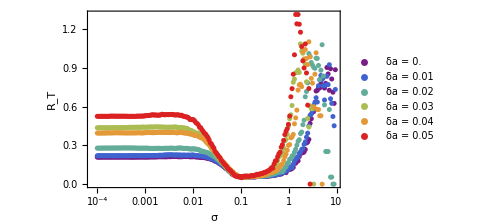
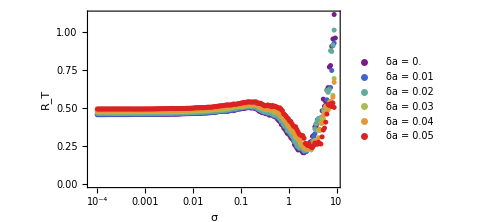
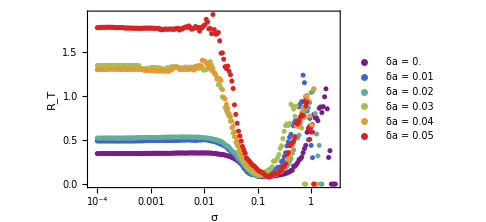
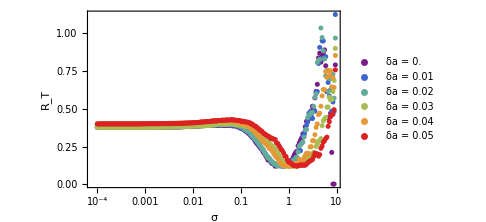

```mathematica
plotsσR=Table[ListLogLinearPlot[curvesσRs[[i]],
Axes->False,
Frame->True,
PlotRange->All,
FrameLabel->{"σ","R_T"},
FrameStyle->Black,
LabelStyle->Directive[Black,16],
(*PlotLabel->"a = "<>ToString[dataσR["as"][[i]]],*)
PlotLegends->PointLegend[ColorData["Rainbow"]/@Range[0,1,1/(Length[curvesσRs[[i]]]-1)],Table["δa = "<>ToString[dataσR["das"][[j]]](*<>", D = "<>ToString[dataσR["ds"][[i,j]]]*),{j,Length[dataσR["das"]]}]],
PlotStyle->(Directive[PointSize[0.01],ColorData["Rainbow"][#]]&)/@Range[0,1,1/(Length[curvesσRs[[i]]]-1)],
ImageSize->Medium],{i,Length@curvesσRs}]
```

#### Exports

```mathematica
Table[Export["D:/plotsR_a"<>StringDelete[ToString[dataDR[["as"]][[i]]],"."]<>".pdf",plotsσR[[i]],ImageResolution->500],{i,Length@plotsσR}]
```

{D:/plotsR_a105.pdf,D:/plotsR_a13.pdf,D:/plotsR_a11.pdf,D:/plotsR_a12.pdf}

### Space—Time Plots

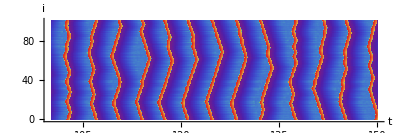

```mathematica
plotXT=With[{traj=GetTrajectory@RunCommand[DiffusionConstant,0.00012,
Seed,42,
NodeCount,100,
WarmupTime,100,
MaximumTime,150,
BifurcationParameterMean,1.05,
BifurcationParameterVariance,0.05,
Trajectory,TrajectoryV]},
ArrayPlot[traj,
LabelStyle->Directive[Black,16],
Frame->False,
Axes->True,
AspectRatio->1/3,
LabelStyle->Directive[Black,16],
ColorFunction->ColorData["Rainbow"],
DataRange->{{100,150},{0,100}},
PlotLegends->Placed[BarLegend[{"Rainbow",{-2,2}},LegendLabel->"u_i",LegendMarkerSize->100],Right],
AxesLabel->{"t","i","u_i"}]]
```

```mathematica
Export["D:/plotXTD000012a105da005.pdf",plotXT]
```

D:/plotXTD000012a105da005.pdf

### Animations

```mathematica
animData=<||>;
```

```mathematica
animData[["Low"]]=RunCommand[DiffusionConstant,0.00012,
Seed,42,
MeasurementInterval,0.01,
NodeCount,100,
WarmupTime,100,
MaximumTime,200,
BifurcationParameterMean,1.05,
BifurcationParameterVariance,0,
Trajectory,TrajectoryV];
```

```mathematica
animData[["LowHetero"]]=RunCommand[DiffusionConstant,0.00012,
Seed,42,
MeasurementInterval,0.01,
NodeCount,100,
WarmupTime,100,
MaximumTime,200,
BifurcationParameterMean,1.05,
BifurcationParameterVariance,0.05,
Trajectory,TrajectoryV];
```

```mathematica
animData[["Resonance"]]=RunCommand[DiffusionConstant,0.001,
Seed,42,
MeasurementInterval,0.01,
NodeCount,100,
WarmupTime,100,
MaximumTime,130,
BifurcationParameterMean,1.05,
BifurcationParameterVariance,0,
Trajectory,TrajectoryV];
```

```mathematica
animFrames=<||>;
```

```mathematica
With[{name="Low"},
animFrames[[name]]=With[{traj=Transpose@GetTrajectory[animData[[name]]],trajV=Transpose@GetTrajectoryV[animData[[name]]]},
With[{framesUV=Table[ListPlot[MapThread[List,{traj[[i]],trajV[[i]]}],
ImageSize->400,
Axes->None,
Frame->True,
FrameStyle->Black,
AspectRatio->1,
PlotStyle->PointSize[0.015],
PlotRange->{{-2,2},{-1,1}},
FrameLabel->{"u","v"},
LabelStyle->Directive[Black,16]
],{i,1,Length@traj,1}],
framesXU=Table[ListLinePlot[traj[[i]],
ImageSize->500,
Axes->None,
Frame->True,
FrameStyle->Black,
AspectRatio->1/3,
PlotStyle->Directive[Thin,Opacity@0.5],
PlotMarkers->{Graphics@{Opacity@1,Disk[{0,0}]},0.04},
FrameLabel->{"i","u_i"},
LabelStyle->Directive[Black,16],
PlotRange->{All,{-2,2}}
],{i,1,Length@traj,1}]},
MapThread[GraphicsColumn[{##},Alignment->Center,Spacings->-120]&,{framesUV,framesXU}]
]];
ListAnimate[animFrames[[name]],AnimationRate->10]]
```

```mathematica
Export["D:/animD000012a105da0.mov",animFrames[["Low"]],ImageResolution->500]
```

D:/animD000012a105da0.mov

```mathematica
Export["D:/animD000012a105da005.mov",animFrames[["LowHetero"]]]
```

D:/animD000012a105da005.mov